```mathematica
(* calculating d sigma/dQ^2 as z=Q^s/sHat->1 *)

(* this notebook tries to use the completeness relation |q><q| = |qn><qn| + |qnb><qnb| - |qsoft><qsoft| *)
(* we define |qsoft><qsoft| as |q1soft><q1soft|/2 + |q2soft><q2soft|/2 *)

Quiet[NotebookEvaluate["/Users/Matt/Documents/Research/MIW_mathematica/MIW_header_file.nb"]];

(* use integrateForThrustfunction instead of massive wall of text *)

(* operators are defined in the dijet picture RHS of the picture *)

(*
         /      \
     /        \
    / g g  g g \
O_2 /            \ O_2^*
      \           /
     \         /
    \       /
   \     /

*)
```

Notebook load complete.

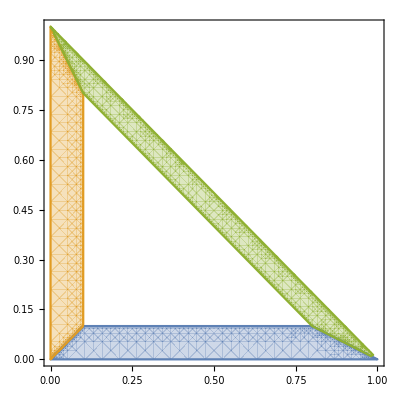

```mathematica
regA=x13<tau&&x13<x23&&x13<x12&&x13>0&&x23>0&&x12>0;
regB=x23<tau&&x23<x13&&x23<x12&&x13>0&&x23>0&&x12>0;
regC=x12<tau&&x12<x13&&x12<x23&&x13>0&&x23>0&&x12>0;
plotPS={regA,regB,regC}/.tau->0.1/.x12->1-x13-x23;
RegionPlot[plotPS,{x23,0,1},{x13,0,1},MaxRecursion->5]
```

## Integral Tables in Dalitz Space

```mathematica
(* we divide the integration into four disjoint regions  *)

(* Region A -- blue   -- the region where p2 has the largest energy  *)
(* Region B -- orange -- the region where p1 has the largest energy  *)
(* Region C -- green  -- the region where q has the largest energy   *)
(* Region τ -- white  -- the region where the thrust τ=1-T is larger than some value τ *)
(*
-Graphics-
(* ^Here the x-axis is x23 and the y-axis is x13 *)
*)

measure=(x13*x23*(1-x13-x23))^(eps);  (* The transformed measure from Collins FoPQCD eq. A44  *)
commonDenominator=x13*x23; 

(* the denominator that appears when we combine amplitudes squared *)
```

### Phase Space Integrals

#### A -- Sideways Integration (x-first)

```mathematica
(*regAs1=Integrate[x^(n-1+eps)(1-x-y)^(eps),{x,y,1-2*y},Assumptions->0<y<1/3]//Normal;*)
(*Series[regAs1*y^(m-1+eps)/.n->3/.m->0,{y,0,2},Assumptions->0<y<1/3]//Normal
regAs2=Integrate[%,{y,0,tau}];
regAs3=Series[%,{tau,0,2}]//Normal;
Series[%,{eps,0,0},Assumptions->0<eps<1/10]//Normal;
Series[%,{tau,0,1}]//Normal//FullSimplify
Series[%,{eps,0,0}]//Normal//FullSimplify;*)
```

```mathematica
(* try integrating x first, then y *)

(*
regAs1=Integrate[x^(n-1+eps)(1-x-y)^(eps),{x,y,1-2*y}];
regAs2=Integrate[%*y^(m-1+eps),{y,0,tau}];
regAs3=Series[%,{tau,0,2}]//Normal;
*)

(* it worked but the output is HUGE! Almost 57000 terms long *)

(* instead of keeping the huge result, we'll store the 4x4 {n,m} elements that are necessary for usual calculations *)
(* remember, the epsilons here are IR regulators, so negative. Later, use /.eps->negeps/.negeps->-eps to revert back to regular epsilons *)

regA00=-Pi^2/6+1/(2*ϵ^2)-2*τ-Log[τ]^2/2; 
regA01=τ*(1-Log[τ]);
regA02=0;
regA03=0;

regA10=-2+ϵ^(-1)-3*τ+Log[τ];
regA11=τ;
regA12=0;
regA13=0;

regA20=-1+1/(2*ϵ)-2*τ+Log[τ]/2;
regA21=τ/2;
regA22=0;
regA23=0;
1/18 (-36 τ+6 log(τ)+6/ϵ-13)
regA30=-13/18+1/(3*ϵ)-2*τ+Log[τ]/3;
regA31=τ/3;
regA32=0;
regA33=0;

intTotalA[n_,m_]:=Switch[{n,m},{0,0},regA00 ,{0,1},regA01,{0,2},regA02,{0,3},regA03,{0,4},regA04,
							    {1,0},regA10 ,{1,1},regA11,{1,2},regA12,{1,3},regA13,{1,4},regA14,
						   	 {2,0},regA20 ,{2,1},regA21,{2,2},regA22,{2,3},regA23,{2,4},regA24,
						    	{3,0},regA30 ,{3,1},regA31,{3,2},regA32,{3,3},regA33,{3,4},regA34,
						    	{4,0},regA40 ,{4,1},regA41,{4,2},regA42,{4,3},regA43,{4,4},regA44]/.eps->-eps;
```

1/18 (-36 τ+6 log(τ)+6/ϵ-13)

```mathematica
(*
Integrate[x^(0-1+eps)(1-x-y)^(eps),{x,y,1-2*y}]
Integrate[%*y^(0-1+eps),{y,0,tau}]
Series[%,{tau,0,4}]//Normal

Series[%,{tau,0,1}]//Normal
Series[%,{eps,0,0}]//Normal
Series[%,{tau,0,1}]//Normal
*)
```

#### B -- Vertical Integration (y-first)

```mathematica
(* summary *)

regB00=regA00;
regB01=regA10;
regB02=regA20;
regB03=regA30;

regB10=regA01;
regB11=regA11;
regB12=regA21;
regB13=regA31;

regB20=regA02;
regB21=regA12;
regB22=regA22;
regB23=regA32;

regB30=regA03;
regB31=regA13;
regB32=regA23;
regB33=regA33;
```

```mathematica
(*
Integrate[y^(m-1+eps)(1-x-y)^(eps),{y,x,1-2*x}]
Integrate[%*x^(n-1+eps),{x,0,tau}]
regBlong=Series[%,{tau,0,2}]//Normal
*)

(* this is equivalent to the region A integration, but with n interchanged with m *)
```

#### C -- Sideways Integration (x-first)

```mathematica
(* summary *)

(* it looks like I only need to know the result for c02, c11, and c20, so let's just do those *)

(* remember, the epsilons here are IR regulators, so negative. Later, use /.eps->negeps/.negeps->-eps to revert back to regular epsilons *)

regC00=τ*(2-2*Log[τ]);
regC01=τ-τ*Log[τ];
regC02=-(τ*Log[τ]);
regC03=τ*(-1/2-Log[τ]);

regC10=τ*(1-Log[τ]);
regC11=τ;
regC12=τ/2;
regC13=τ/3;

regC20=-(τ*Log[τ]);
regC21=τ/2;
regC22=τ/6;
regC23=τ/12;

regC30=-(τ*(1+2*Log[τ]))/2;
regC31=τ/3;
regC32=τ/12;
regC33=τ/30;

intC[n_,m_]:=Switch[{n,m},{0,0},regC00 ,{0,1},regC01,{0,2},regC02,{0,3},regC03,{0,4},regC04,
							    {1,0},regC10 ,{1,1},regC11,{1,2},regC12,{1,3},regC13,{1,4},regC14,
						   	 {2,0},regC20 ,{2,1},regC21,{2,2},regC22,{2,3},regC23,{2,4},regC24,
						    	{3,0},regC30 ,{3,1},regC31,{3,2},regC32,{3,3},regC33,{3,4},regC34,
						    	{4,0},regC40 ,{4,1},regC41,{4,2},regC42,{4,3},regC43,{4,4},regC44]/.eps->-eps;
```

```mathematica
(* convert integrals from y to u=1-x-y *)
(* then the integration region has the same form as region A so we can try the sideways integration again *)

(*nn=1;
mm=1;

regCs02i=Integrate[x^(nn-1+eps)(1-x-u)^(mm-1+eps),{x,u,1-2*u}]

%/.Hypergeometric2F1Regularized[a_,b_,c_,d_]:>HypExp[Hypergeometric2F1Regularized[a,b,c,d],eps,2]/.Hypergeometric2F1[a_,b_,c_,d_]:>HypExp[Hypergeometric2F1[a,b,c,d],eps,2]/.Beta[z_,a_,b_]:>(z^a/a)*HypExp[Hypergeometric2F1[a,1-b,1+a,z],eps,2]

regCs02ii=Integrate[%*u^eps,{u,0,tau}]
regCs02=Series[%,{tau,0,2}];
regCs02=Series[%,{tau,0,1}]//Normal;
regCs02=Series[%,{eps,0,0}]//Normal
regCsnnmm=Series[%,{tau,0,1}]//Normal
regCsnnmm//InputForm*)
```

#### Overall

```mathematica
int00=regA00+regB00+regC00;
int01=regA01+regB01+regC01;
int02=regA02+regB02+regC02;
int03=regA03+regB03+regC03;

int10=regA10+regB10+regC10;
int11=regA11+regB11+regC11;
int12=regA12+regB12+regC12;
int13=regA13+regB13+regC13;

int20=regA20+regB20+regC20;
int21=regA21+regB21+regC21;
int22=regA22+regB22+regC22;
int23=regA23+regB23+regC23;

int30=regA30+regB30+regC30;
int31=regA31+regB31+regC31;
int32=regA32+regB32+regC32;
int33=regA33+regB33+regC33;

intTotal[n_,m_]:=Switch[{n,m},{0,0},int00 ,{0,1},int01,{0,2},int02,{0,3},int03,{0,4},int04,
							    {1,0},int10 ,{1,1},int11,{1,2},int12,{1,3},int13,{1,4},int14,
						   	 {2,0},int20 ,{2,1},int21,{2,2},int22,{2,3},int23,{2,4},int24,
						    	{3,0},int30 ,{3,1},int31,{3,2},int32,{3,3},int33,{3,4},int34,
						    	{4,0},int40 ,{4,1},int41,{4,2},int42,{4,3},int43,{4,4},int44]/.eps->-eps;
```

## Setup

### Prelim

```mathematica
$Assumptions=alphabar>0&&muMS>0&&0<delta<1&&p1m>0&&p2p>0&&p1p>0&&p2m>0&&eps>0&&QT>0&&sHat>0&&0<zbar<1&&Y∈Reals&&Vperp[p1]>0&&Vperp[p2]>0&&Qp>0&&Qm>0&&w>0&&wbar>0&&u<0

gluonSign=-1;
waveZpureDR=1(*-Cf*alphaMS*(1/eps-1/eps)/(4*Pi)*)

vertexQCD0=1
vertexQCD1UV=(alphabar/2)(1/eps)
vertexQCD1IR=(alphabar/2)(-2/eps^2-(4-2Log[p1m*p2p/muMS^2])/eps-Log[p1m*p2p/muMS^2]^2+3Log[p1m*p2p/muMS^2]-8+Pi^2/6)
vertexQCD1=vertexQCD1UV+vertexQCD1IR
vertexQCD=vertexQCD0+vertexQCD1

waveGraph1UV=(alphabar/2)(1/eps)
waveGraph1IR=(alphabar/2)(-1/eps)
waveGraph1=waveGraph1UV+waveGraph1IR



Z2=1+Cf*alphaMS(2/eps^2+(-2*Log[(-nu^2-I*delta)/muMS^2]+3)/eps)/(4*Pi)
Z2bar=ComplexConjugate[Z2]
hardFunc=1+alphabar(-Log[nu^2/muMS^2]^2+3Log[nu^2/muMS^2]+7zeta2-8)

keepEpsOrderMatElemSqr=2;
keepBoole=0;
(*turnOffConditional[];*)

Unprotect[Tr];
Tr/:Tr[0]:=0;
Protect[Tr];

spinSumHornig=(-MTD[alpha,beta])(-(MTD[mu,nu]-FVD[n+nb,mu]FVD[n+nb,nu]/4));
spinSum=spinSumHornig;

collect[e_]:=Collect2[e,omega,QT]
noLambdaQCD[e_]:=e/.Vperp[p1]->0/.p1p->0/.Vperp[p2]->0/.p2m->0

Vperp/:Vperp[eta]:=0
Vperp/:Vperp[etabar]:=0
SPD/:SPD[eta,etabar]:=2
SPD/:SPD[eta,eta]:=0
SPD/:SPD[etabar,etabar]:=0
```

ᾱ>0∧μ_OverBar[MS]>0∧0<δ<1∧p_1^->0∧p_2^+>0∧p_1^+>0∧p_2^->0∧ϵ>0∧Q_T>0∧ŝ>0∧0<z̄<1∧Y∈ℝ∧p_1_⊥>0∧p_2_⊥>0∧Q^+>0∧Q^->0∧w>0∧w̄>0∧u<0

1

1

(ᾱ)/(2 ϵ)

1/2 ᾱ (-(4-2 log((p_2^+ p_1^-)/μ_OverBar[MS]^2))/ϵ-log^2((p_2^+ p_1^-)/μ_OverBar[MS]^2)+3 log((p_2^+ p_1^-)/μ_OverBar[MS]^2)-2/ϵ^2+π^2/6-8)

(ᾱ)/(2 ϵ)+1/2 ᾱ (-(4-2 log((p_2^+ p_1^-)/μ_OverBar[MS]^2))/ϵ-log^2((p_2^+ p_1^-)/μ_OverBar[MS]^2)+3 log((p_2^+ p_1^-)/μ_OverBar[MS]^2)-2/ϵ^2+π^2/6-8)

(ᾱ)/(2 ϵ)+1/2 ᾱ (-(4-2 log((p_2^+ p_1^-)/μ_OverBar[MS]^2))/ϵ-log^2((p_2^+ p_1^-)/μ_OverBar[MS]^2)+3 log((p_2^+ p_1^-)/μ_OverBar[MS]^2)-2/ϵ^2+π^2/6-8)+1

(ᾱ)/(2 ϵ)

-(ᾱ)/(2 ϵ)

0

1+(C_F α_OverBar[MS] (2/ϵ^2+(3-2 log((-ν^2-ⅈ δ)/μ_OverBar[MS]^2))/ϵ))/(4 π)

1+(C_F α_OverBar[MS] (2/ϵ^2+(3-2 log((-ν^2+ⅈ δ)/μ_OverBar[MS]^2))/ϵ))/(4 π)

ᾱ (7 ζ_2-log^2(ν^2/μ_OverBar[MS]^2)+3 log(ν^2/μ_OverBar[MS]^2)-8)+1

### Useful Functions

```mathematica
applyDiracDeltaUV[e_]:=e/.(myDelta[u+a_]*b_:>(b/.u->-a))/.myDelta[u-a_]*b_:>(b/.u->a)/.myDelta[v+a_]*b_:>(b/.v->-a)/.myDelta[v-a_]*b_:>(b/.v->a)


simplifyDeltas[e_]:=e/.myDelta[a_*b_-a_]:>myDelta[1-b]/a

lcCompFVDreverse[e_]:=e/.FVD[Vperp[v_],a_]:>FVD[v,a]-FVD[nb,a]*SPD[v,n]/2-FVD[n,a]SPD[v,nb]/2

etaIze[e_]:=e/.FVD[nb,a_]:> Sqrt[Qm/Qp]FVD[etabar,a]/.FVD[n,a_]:> Sqrt[Qp/Qm]FVD[eta,a]/.SPD[n,a_]/;!MatchQ[a,Q]:> Sqrt[Qp/Qm]SPD[eta,a]/.SPD[nb,a_]/;!MatchQ[a,Q]:> Sqrt[Qm/Qp]SPD[etabar,a]


getOnlyLong[e_]:=e/.Vperp[MTD[_,_]]->0/.FVD[Vperp[_],_]->0
```

```mathematica
findDensity[elem1_,elemdag2_]:=Module[{temp,returnMe},
temp=gluonSign(elem1/.b_ .Spinor[Momentum[a_],_,_]:>b.GSD[a]/.Spinor[___].a_:>a).(elemdag2/.b_ .Spinor[Momentum[a_],_,_]:>b.GSD[a]/.Spinor[___].a_:>a)/.eps->zerop//DiracSimplify//FCE;

temp=temp//lcCompAll//PhatDef//DiracSimplify//FCE;

temp=-Cf*Tr[temp//gPerpDef]/4//FCE//Simplify;(* negative from the lepton tensor, 4 from 2 spin options for each quark, Cf from colour trace and averaging *)

temp=temp/.SPD[k,k]->0//lcCompMTD//Simplify;
returnMe=Series[temp/.D->4-2*eps,{eps,0,keepEpsOrderMatElemSqr}]//Normal//Simplify;
Return[returnMe];
]
```

```mathematica
analyzeAndClean[integratedWmunu_]:=Module[{temp,returnMe},
temp=integratedWmunu//cleanForIdentities;
temp=temp//applyAllIdentities;
If[SeriesCoefficient[temp,{eps,0,-1}]≠0,
temp=Series[temp,{eps,0,0}]//Normal//Expand;
,
temp=temp;
];
returnMe=temp/.myDelta[w]*a_:>myDelta[w]*(a/.w->0/.wbar->1)//FullSimplify;
Return[returnMe];
]
```

```mathematica
integrateForThrust[e_]:=Module[{temp,tempIgrand,afterKplus,afterKPerp,afterQPerp,afterY,preIntMinus1,preIntMinus2,newPreInt,afterKminus,afterAll,integratedPortion,unintegratedPortion,afterKminusUnintegrated},

temp=e*onShellDelta*momConservation*WmunuNorm*ddkMeasure;

temp=temp/.myDelta[u+km/(p1m-km)]->(p1m-km)*myDelta[km*ubar+u*p1m]/.myDelta[u+p1m/(p1m-km)]->(p1m-km)*myDelta[km*u-p1m(1+u)];
temp=temp/.g^2->4*Pi*alphaMS*(Pi*muMS^2*Exp[EulerGamma])^eps//replacementalphaMS//Simplify;

(* matching so we can set to zero the order lambda_QCD p1p, p2m, pperp terms *)
temp=temp/.zerop->0//applyThresholdNotation//Simplify;
tempIgrand=Simplify[temp/.z->1-zbar//applyDiracDeltaSimplification,Assumptions->p2p>0];

afterKplus=tempIgrand//applyKsqrDiracDeltaKPlus;
afterKPerp=afterKplus//applyDiracDeltaKPerp;
temp=afterKPerp/.SPD[Vperp[Q]]->-QT^2/.myDelta[-km+a_]:>myDelta[km-a]/.myDelta[-km-a_]:>myDelta[km+a];


temp=temp/.HeavisideTheta[___]->1//applyNoLambdaQCD;

afterQPerp=temp*myTheta[QT^2]//applyDiracDeltaQTsqr//Simplify;


(* the following line integrates dY *)
afterY=afterQPerp/.D->4-2*eps//applyDiracDeltaY;

preIntMinus1=afterY//.(a_*b_)^eps:>a^eps*b^eps/. 1/(km-p1m*zbar)->-1/(p1m*zbar-km)/.eps->-eps;


preIntMinus2=FullSimplify[preIntMinus1]/.zbar-1->-z//FullSimplify;

newPreInt=preIntMinus2/.(a_/b_)^c_:>a^c*b^(-c)/.(a_*b_)^c_:>a^c*b^c/. 1/(km-p1m*zbar)->-1/(p1m*zbar-km);

afterKminus=newPreInt(**Boole[zbar*p1m>km]*)//applyDiracDeltaKMinus;

integratedPortion = SeriesCoefficient[afterKminus,{UNINTEGRATEDKM,0,0}];
unintegratedPortion = SeriesCoefficient[afterKminus,{UNINTEGRATEDKM,0,1}];

afterKminusUnintegrated=integrateTermByTerm[unintegratedPortion/.myTheta[_]->1/.wbar->1-w/.wwbar->1-ww,{km,0,zbar*p1m},Assumptions->eps>0&&0<zbar<1&&p1m>0&&p2p>0&&km>0&&0<w<zbar<1&&1<1/zbar<ww<Infinity];
Return[integratedPortion+afterKminusUnintegrated/.eps->-eps];

]
```

```mathematica
treeLevelDensityAnalysis[e_]:=Module[{tmp},
tmp=e//lcCompAll//Expand;


tmp=tmp/.FVD[n,_]FVD[Vperp[_],_]->0/.FVD[nb,_]FVD[Vperp[_],_]->0//lcCompMTDReverse;
tmp=tmp//etaIze//Simplify;
tmp=tmp/.Sqrt[a_]Sqrt[b_]:>Sqrt[a*b]/.Sqrt[a_]/Sqrt[b_]:>Sqrt[a/b];

myPrint[tmp];

tmp=tmp/.SPD[p1,eta]->-SPD[Vperp[pa]]/SPD[p1,etabar]/.SPD[p2,etabar]->-SPD[Vperp[pb]]/SPD[p2,eta];
tmp=tmp/.SPD[p1,etabar]->Sqrt[Qp*Qm](1+SPD[Vperp[pb]]/(SPD[pb,eta]Sqrt[Qp*Qm]))/.SPD[p2,eta]->Sqrt[Qp*Qm](1+SPD[Vperp[pa]]/(SPD[pa,etabar]Sqrt[Qp*Qm]));
tmp=tmp/.SPD[pa,etabar]->Sqrt[Qp*Qm](1+SPD[Vperp[pb]]/(SPD[pb,eta]Sqrt[Qp*Qm]))/.SPD[pb,eta]->Sqrt[Qp*Qm](1+SPD[Vperp[pa]]/(SPD[pa,etabar]Sqrt[Qp*Qm]));
tmp=tmp/.Qp->(Q^2+QT^2)/Qm/.p1->pa/.p2->pb;

tmp=Series[tmp,{Q,Infinity,0}]//Normal//Simplify;
tmp=tmp/.Sqrt[a_]Sqrt[b_]:>Sqrt[a*b]/.Sqrt[a_]/Sqrt[b_]:>Sqrt[a/b];;
tmp=tmp/.QT^2->-SPD[Vperp[pa+pb]];
Return[Collect2[tmp/(2Q^2),Q,MTD]];
];
```

```mathematica
takeDagger[e_]:=e/.u->uu/.v->u/.uu->v/.rho->rhoo/.psi->rho/.rhoo->psi/.sigma->sigmaa/.phi->sigma/.sigmaa->phi/.mu->muu/.nu->mu/.muu->nu//ComplexConjugate

takeCPconjugate[e_]:=e/.n->nn/.nb->n/.nn->nb/.p1->P1/.p2->p1/.P1->p2//ComplexConjugate


takeBarConjugate[e_]:=e/.n->nn/.nb->n/.nn->nb

(*matElem1a1
%//takeCPconjugate//Simplify
matElem1b1//FCI//Simplify*)
```

```mathematica
integrateForThresholdVerbose[e_]:=Module[{temp,tempIgrand,afterKplus,afterKPerp,afterQPerp,afterY,preIntMinus1,preIntMinus2,newPreInt,afterKminus,afterAll,integratedPortion,unintegratedPortion,afterKminusUnintegrated},

temp=e*onShellDelta*momConservation*WmunuNorm*ddkMeasure;
Print[temp];
temp=temp/.myDelta[u+km/(p1m-km)]->(p1m-km)*myDelta[km*ubar+u*p1m]/.myDelta[u+p1m/(p1m-km)]->(p1m-km)*myDelta[km*u-p1m(1+u)];
temp=temp/.g^2->4*Pi*alphaMS*(Pi*muMS^2*Exp[EulerGamma])^eps//replacementalphaMS//Simplify;

(* matching so we can set to zero the order lambda_QCD p1p, p2m, pperp terms *)
temp=temp/.zerop->0//applyThresholdNotation//Simplify;
tempIgrand=Simplify[temp/.z->1-zbar//applyDiracDeltaSimplification,Assumptions->p2p>0];

afterKplus=tempIgrand//applyKsqrDiracDeltaKPlus;
afterKPerp=afterKplus//applyDiracDeltaKPerp;
temp=afterKPerp/.SPD[Vperp[Q]]->-QT^2/.myDelta[-km+a_]:>myDelta[km-a]/.myDelta[-km-a_]:>myDelta[km+a];

Print[temp//applyNoLambdaQCD];
temp=temp/.HeavisideTheta[___]->1//applyNoLambdaQCD;

afterQPerp=temp*myTheta[QT^2]//applyDiracDeltaQTsqr//Simplify;


(* the following line integrates dY *)
afterY=afterQPerp/.D->4-2*eps//applyDiracDeltaY;

preIntMinus1=afterY//.(a_*b_)^eps:>a^eps*b^eps/. 1/(km-p1m*zbar)->-1/(p1m*zbar-km)/.eps->-eps;

Print[preIntMinus1];
preIntMinus2=FullSimplify[preIntMinus1]/.zbar-1->-z//FullSimplify;
Print[preIntMinus2];
newPreInt=preIntMinus2/.(a_/b_)^c_:>a^c*b^(-c)/.(a_*b_)^c_:>a^c*b^c/. 1/(km-p1m*zbar)->-1/(p1m*zbar-km);

Print[newPreInt];

afterKminus=newPreInt(**Boole[zbar*p1m>km]*)//applyDiracDeltaKMinus;

integratedPortion = SeriesCoefficient[afterKminus,{UNINTEGRATEDKM,0,0}];
unintegratedPortion = SeriesCoefficient[afterKminus,{UNINTEGRATEDKM,0,1}];

afterKminusUnintegrated=integrateTermByTerm[unintegratedPortion/.myTheta[_]->1/.wbar->1-w/.wwbar->1-ww,{km,0,zbar*p1m},Assumptions->eps>0&&0<zbar<1&&p1m>0&&p2p>0&&km>0&&0<w<zbar<1&&1<1/zbar<ww<Infinity];
Return[integratedPortion+afterKminusUnintegrated/.eps->-eps];

]
```

### Identities

```mathematica
applyIdentityQ[p_]:=MatchQ[p,zbar|z1bar|z2bar|tauPerp|u|w]

cleanForIdentities[e_]:=e/.(1/var_^2)^(a_/2)/;applyIdentityQ[var]:>var^-a/.(var_*p1m)^a_/;applyIdentityQ[var]:>var^a*p1m^a/.(p1m*p2p*var_)^a_/;applyIdentityQ[var]:>p1m^a*p2p^a*var^a/.(b_*var_/c_)^a_/;applyIdentityQ[var]:>b^a*c^(-a)*var^a/.(b_/(c_*var_))^a_/;applyIdentityQ[var]:>b^a*c^(-a)*var^(-a)/.(p1m*p2p*var_/muMS^2)^a_/;applyIdentityQ[var]:>p1m^a*p2p^a*var^a*muMS^(-2a)/.(muMS/var_)^a_/;applyIdentityQ[var]:>muMS^a*var^-a/.(muMS*Sqrt[var_])^a_/;applyIdentityQ[var]:>muMS^a*var^(Expand[a/2])//Expand

identityPowerPos1[e_]:= e/.(a_)^(1-b_)/;applyIdentityQ[a]:>a^2(PlusDistribution[myTheta[a]/a]-b*PlusDistribution[myTheta[a]*Log[a]/a]+myDelta[a]*A+D[myDelta[a],a]*B/.A->-1/b/.B->0)/.(a_)^(1+b_)/;applyIdentityQ[a]:>a^2(PlusDistribution[myTheta[a]/a]+b*PlusDistribution[myTheta[a]*Log[a]/a]+myDelta[a]*A+D[myDelta[a],a]*B/.A->1/b/.B->0)


identityPowerNeg1[e_]:= e/.(a_)^(-1-b_)/;applyIdentityQ[a]:>(PlusDistribution[myTheta[a]/a]-b*PlusDistribution[myTheta[a]*Log[a]/a]+myDelta[a]*A+D[myDelta[a],a]*B/.A->-1/b/.B->0)/.(a_)^(-1+b_)/;applyIdentityQ[a]:>(PlusDistribution[myTheta[a]/a]+b*PlusDistribution[myTheta[a]*Log[a]/a]+myDelta[a]*A+D[myDelta[a],a]*B/.A->1/b/.B->0)

identityPowerNeg1WithLog[e_]:= e/.Log[a_](a_)^(-1-b_)/;applyIdentityQ[a]:>(PlusDistribution[Log[a]myTheta[a]/a]-b*PlusDistribution[myTheta[a]*Log[a]^2/a]+myDelta[a]*A+D[myDelta[a],a]*B/.A->-1/b^2/.B->0)/.Log[a_](a_)^(-1+b_)/;applyIdentityQ[a]:>(PlusDistribution[Log[a]myTheta[a]/a]+b*PlusDistribution[myTheta[a]*Log[a]^2/a]+myDelta[a]*A+D[myDelta[a],a]*B/.A->-1/b^2/.B->0)

identityPowerNeg2[e_]:=e/.{(a_)^(-2-b_)/;applyIdentityQ[a]:>(DoublePlusDistribution[myTheta[a]/a^2]-b*DoublePlusDistribution[myTheta[a]*Log[a]/a^2]+myDelta[a]*A+D[myDelta[a],a]*B/.A->(b-1)/.B->1/b)}/.(a_)^(-2+b_)/;applyIdentityQ[a]:>(DoublePlusDistribution[myTheta[a]/a^2]+b*DoublePlusDistribution[myTheta[a]*Log[a]/a^2]+myDelta[a]*A+D[myDelta[a],a]*B/.A->(-b-1)/.B->-1/b);

identityPowerPos0[e_]:= e/.(a_)^(-b_)/;applyIdentityQ[a]&&(!IntegerQ[b]):>a(PlusDistribution[myTheta[a]/a]-b*PlusDistribution[myTheta[a]*Log[a]/a]+myDelta[a]*A+D[myDelta[a],a]*B/.A->-1/b/.B->0)/.(a_)^(+b_)/;applyIdentityQ[a]&&(!IntegerQ[b]):>a(PlusDistribution[myTheta[a]/a]+b*PlusDistribution[myTheta[a]*Log[a]/a]+myDelta[a]*A+D[myDelta[a],a]*B/.A->1/b/.B->0)

identityPowerPos0WithLog[e_]:= e/.Log[a_](a_)^(-b_)/;applyIdentityQ[a]&&(!IntegerQ[b]):>a(PlusDistribution[Log[a]myTheta[a]/a]-b*PlusDistribution[myTheta[a]*Log[a]^2/a]+myDelta[a]*A+D[myDelta[a],a]*B/.A->-1/b^2/.B->0)/.Log[a_](a_)^(+b_)/;applyIdentityQ[a]&&(!IntegerQ[b]):>a(PlusDistribution[Log[a]myTheta[a]/a]+b*PlusDistribution[myTheta[a]*Log[a]^2/a]+myDelta[a]*A+D[myDelta[a],a]*B/.A->-1/b^2/.B->0)



applyAllIdentities[e_]:=e//cleanForIdentities//identityPowerNeg2//identityPowerNeg1WithLog//identityPowerNeg1//identityPowerPos1//identityPowerPos0WithLog//identityPowerPos0
```

```mathematica
applyIdentitiesTermByTerm[e_]:=Module[{nterms,expexp,it,iterm,igral,result},expexp=Expand[e];Print["Applying identities for ",expexp];If[Head[expexp]===Plus,nterms=Length[expexp];it=1;iterm=0;igral=0;result=0;Print["Integrating ",nterms," terms."] For[it=1,it≤nterms,it++,iterm=expexp⟦it⟧;Print["Term ",it," : ",iterm];igral=applyAllIdentities[iterm];Print["     ",it," : ",igral];result+=igral;];,nterms=1;it=1;igral=0;result=0;Print["Integrating ",nterms," terms."] For[it=1,it≤nterms,it++,iterm=expexp;Print["Term ",it," : ",iterm];igral=applyAllIdentities[iterm,];Print["     ",it," : ",igral];result+=igral;];];Return[result];]
```

```mathematica
zbar^(1-eps)
Log[zbar/z]/(zbar)^(1+eps)//expLogs
%//applyAllIdentities
%//applyDiracDeltaSimplification
```

(z̄)^(1-ϵ)

(z̄)^(-ϵ-1) (log(z̄)-log(z))

-log(z) (-DiracDelta[z̄]/ϵ-ϵ ((log(z̄) HeavisideTheta[z̄])/(z̄))_++(HeavisideTheta[z̄]/(z̄))_+)-DiracDelta[z̄]/ϵ^2-ϵ ((log^2(z̄) HeavisideTheta[z̄])/(z̄))_++((log(z̄) HeavisideTheta[z̄])/(z̄))_+

applyDiracDeltaSimplification(-log(z) (-DiracDelta[z̄]/ϵ-ϵ ((log(z̄) HeavisideTheta[z̄])/(z̄))_++(HeavisideTheta[z̄]/(z̄))_+)-DiracDelta[z̄]/ϵ^2-ϵ ((log^2(z̄) HeavisideTheta[z̄])/(z̄))_++((log(z̄) HeavisideTheta[z̄])/(z̄))_+)

### Kinematics

```mathematica
nondimensionalize[e_]:=e/.qm->qhatm*Q/.qp->qhatp*Q/.p1m->p1hatm*Q/.p1p->p1hatp*Q/.p2m->p2hatm*Q/.p2p->p2hatp*Q;
dimensionalize[e_]:=e/.qhatm->qm/Q/.qhatp->qp/Q/.p1hatm->p1m/Q/.p1hatp->p1p/Q/.p2hatm->p2m/Q/.p2hatp->p2p/Q;

(* 3 body kinematics *)
kinematicsA[e_]:=nondimensionalize[e/.Vperp[p1]->-Vperp[q]/.Vperp[p2]->0]/.p2hatm->0/.p2hatp->1-qhatp-p1hatp/.p1hatp->qhatp*qhatm/p1hatm/.p1hatm->1-qhatm/.qhatp->x13*(1-qhatm)/.qhatm->x23/(1-x13);
kinematicsB[e_]:=nondimensionalize[e/.Vperp[p2]->-Vperp[q]/.Vperp[p1]->0]/.p2hatm->0/.p2hatp->1-qhatp/.p1hatp->0/.p1hatm->1-qhatm-p2hatm/.qhatm->x23*(1-qhatp)/.qhatp->x13/(1-x23);
kinematicsC[e_]:=nondimensionalize[e/.Vperp[p1]->-Vperp[p2]/.Vperp[q]->0]/.p2hatm->0/.p2hatp->1-qhatp-p1hatp/.p1hatp->qhatp*qhatm/p1hatm/.p1hatm->1-qhatm/.qhatp->x13*(1-qhatm)/.qhatm->x23/(1-x13);
```

## 1 Gluon

### NLO @ LP

#### LP Matrix Elements

```mathematica
(* dagger on the left, operator on the right *)

(* n sector *)
matElem0N=(-I*g*SpinorUBar[p1].((2FVD[p1,alpha]+GAD[alpha].GSD[q])/(2SPD[p1,q])-FVD[nb,alpha]/(SPD[nb,q])).Phatnb.GAD[mu].Phatnb.SpinorV[p2]//lcCompAll//FCI)

(* nb sector *)
matElem0Nb=matElem0N//takeCPconjugate


matElemDag0N=matElem0N//takeDagger
matElemDag0Nb=matElem0Nb//takeDagger
```

-ⅈ g φ(p_1).((2 (1/2 p_1^- n^α+1/2 p_1^+ (n̄)^α+(p_1_⊥)^α)+((γ^α)_⊥+(γ^- n^α)/2+(γ^+ (n̄)^α)/2).((γ^- q^+)/2+(γ^+ q^-)/2+γ·q_⊥))/(2 (1/2 p_1^- q^++1/2 p_1^+ q^-+p_1_⊥·q_⊥))-(n̄)^α/q^-).γ^-/2.γ^+/2.((γ^μ)_⊥+(γ^- n^μ)/2+(γ^+ (n̄)^μ)/2).γ^-/2.γ^+/2.φ(p_2)

1/16 ⅈ g φ(p_1).γ^-.γ^+.((γ^μ)_⊥+(γ^- n^μ)/2+(γ^+ (n̄)^μ)/2).γ^-.γ^+.((2 (1/2 p_2^- n^α+1/2 p_2^+ (n̄)^α+(p_2_⊥)^α)+((γ^- q^+)/2+(γ^+ q^-)/2+γ·q_⊥).((γ^α)_⊥+(γ^- n^α)/2+(γ^+ (n̄)^α)/2))/(2 (1/2 p_2^- q^++1/2 p_2^+ q^-+p_2_⊥·q_⊥))-n^α/q^+).φ(p_2)

1/16 ⅈ g φ(p_2).γ^+.γ^-.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^+.γ^-.((2 (1/2 p_1^- n^α+1/2 p_1^+ (n̄)^α+(p_1_⊥)^α)+((γ^- q^+)/2+(γ^+ q^-)/2+γ·q_⊥).((γ^α)_⊥+(γ^- n^α)/2+(γ^+ (n̄)^α)/2))/(2 (1/2 p_1^- q^++1/2 p_1^+ q^-+p_1_⊥·q_⊥))-(n̄)^α/q^-).φ(p_1)

-1/16 ⅈ g φ(p_2).((2 (1/2 p_2^- n^α+1/2 p_2^+ (n̄)^α+(p_2_⊥)^α)+((γ^α)_⊥+(γ^- n^α)/2+(γ^+ (n̄)^α)/2).((γ^- q^+)/2+(γ^+ q^-)/2+γ·q_⊥))/(2 (1/2 p_2^- q^++1/2 p_2^+ q^-+p_2_⊥·q_⊥))-n^α/q^+).γ^+.γ^-.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^+.γ^-.φ(p_1)

#### Soft Subtractions

```mathematica
(* soft limits *)

(* brem into n sector in soft limit *)
matElem0NSoft=(-I*g*SpinorUBar[p1].(     FVD[n,alpha]/SPD[n,q]-FVD[nb,alpha]/SPD[nb,q]+2FVD[Vperp[p1],rho]Delta[q,alpha,rho]/(p1m*qp)+(1/(p1m*qp))FVD[q,rho]Delta[q,alpha,sigma]Vperp[GAD[sigma]].Vperp[GAD[rho]]+(qm/(p1m*qp))(GSD[Vperp[p1]]/p1m).Vperp[GAD[rho]]*Deltabar[q,alpha,rho]).Phatnb.GAD[mu].Phatnb.SpinorV[p2]//DeltaDef//lcCompAll//FCI)

(* brem into nb sector in soft limit *)
matElem0NbSoft=matElem0NSoft//takeCPconjugate

matElemDag0NSoft=matElem0NSoft//takeDagger
matElemDag0NbSoft=matElem0NbSoft//takeDagger
```

-ⅈ g φ(p_1).((q^- (γ·p_1_⊥)/p_1^-.(γ^ρ)_⊥ (g^αρ-((n̄)^α ((q^- n^ρ)/2+(q^+ (n̄)^ρ)/2+(q_⊥)^ρ))/q^-))/(p_1^- q^+)+((γ^σ)_⊥.(γ^ρ)_⊥ ((q^- n^ρ)/2+(q^+ (n̄)^ρ)/2+(q_⊥)^ρ) (g^ασ-(n^α ((q^- n^σ)/2+(q^+ (n̄)^σ)/2+(q_⊥)^σ))/q^+))/(p_1^- q^+)+(2 (p_1_⊥)^ρ (g^αρ-(n^α ((q^- n^ρ)/2+(q^+ (n̄)^ρ)/2+(q_⊥)^ρ))/q^+))/(p_1^- q^+)+n^α/q^+-(n̄)^α/q^-).γ^-/2.γ^+/2.((γ^μ)_⊥+(γ^- n^μ)/2+(γ^+ (n̄)^μ)/2).γ^-/2.γ^+/2.φ(p_2)

1/16 ⅈ g φ(p_1).γ^-.γ^+.((γ^μ)_⊥+(γ^- n^μ)/2+(γ^+ (n̄)^μ)/2).γ^-.γ^+.((q^+ (γ^ρ)_⊥.(γ·p_2_⊥) (g^αρ-(n^α ((q^- n^ρ)/2+(q^+ (n̄)^ρ)/2+(q_⊥)^ρ))/q^+))/((p_2^+)^2 q^-)+((γ^ρ)_⊥.(γ^σ)_⊥ ((q^- n^ρ)/2+(q^+ (n̄)^ρ)/2+(q_⊥)^ρ) (g^ασ-((n̄)^α ((q^- n^σ)/2+(q^+ (n̄)^σ)/2+(q_⊥)^σ))/q^-))/(p_2^+ q^-)+(2 (p_2_⊥)^ρ (g^αρ-((n̄)^α ((q^- n^ρ)/2+(q^+ (n̄)^ρ)/2+(q_⊥)^ρ))/q^-))/(p_2^+ q^-)-n^α/q^++(n̄)^α/q^-).φ(p_2)

1/16 ⅈ g φ(p_2).γ^+.γ^-.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^+.γ^-.((q^- (γ^ψ)_⊥.(γ·p_1_⊥) (g^αψ-((n̄)^α ((q^- n^ψ)/2+(q^+ (n̄)^ψ)/2+(q_⊥)^ψ))/q^-))/((p_1^-)^2 q^+)+((γ^ψ)_⊥.(γ^ϕ)_⊥ ((q^- n^ψ)/2+(q^+ (n̄)^ψ)/2+(q_⊥)^ψ) (g^αϕ-(n^α ((q^- n^ϕ)/2+(q^+ (n̄)^ϕ)/2+(q_⊥)^ϕ))/q^+))/(p_1^- q^+)+(2 (p_1_⊥)^ψ (g^αψ-(n^α ((q^- n^ψ)/2+(q^+ (n̄)^ψ)/2+(q_⊥)^ψ))/q^+))/(p_1^- q^+)+n^α/q^+-(n̄)^α/q^-).φ(p_1)

-1/16 ⅈ g φ(p_2).((q^+ (γ·p_2_⊥).(γ^ψ)_⊥ (g^αψ-(n^α ((q^- n^ψ)/2+(q^+ (n̄)^ψ)/2+(q_⊥)^ψ))/q^+))/((p_2^+)^2 q^-)+((γ^ϕ)_⊥.(γ^ψ)_⊥ ((q^- n^ψ)/2+(q^+ (n̄)^ψ)/2+(q_⊥)^ψ) (g^αϕ-((n̄)^α ((q^- n^ϕ)/2+(q^+ (n̄)^ϕ)/2+(q_⊥)^ϕ))/q^-))/(p_2^+ q^-)+(2 (p_2_⊥)^ψ (g^αψ-((n̄)^α ((q^- n^ψ)/2+(q^+ (n̄)^ψ)/2+(q_⊥)^ψ))/q^-))/(p_2^+ q^-)-n^α/q^++(n̄)^α/q^-).γ^+.γ^-.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^+.γ^-.φ(p_1)

### NLO @ NLP

#### Matrix Elements A

```mathematica
(* these operator have the tree-level matching coefficients shifted into the operator *)

(* operators are on the right (jet-like) and daggers are on the left (DY-like) *)
(* need to fix this for the rest of the notebook *)

(* the sqrt[Qp/Qm] is supposed to be representing eta^mu = sqrt[Qm/Qp] n^mu as in Goerke and Luke's SCET/Modes paper *)




(* ------------------ 1/Q operators ------------------ *)

matElem1a1=((1)(I*g*SpinorUBar[p1].(Phatnb.GAD[mu].(Sqrt[Qm/Qp]GSD[n]/2).Vperp[GAD[rho]]).SpinorV[p2]*Deltabar[q,alpha,rho]*myDelta[u-qhatm]/.qhatm->qm/(p1m+qm))//DeltaDef//lcCompAll//FCI)

matElem1a2=((-1)(I*g*SpinorUBar[p1].(Vperp[GAD[rho]].(Sqrt[Qp/Qm]GSD[nb]/2).GAD[mu].Phatnb).SpinorV[p2]*Deltabar[q,alpha,rho]*myDelta[u-qhatm]/.qhatm->qm/(p1m+qm))//DeltaDef//lcCompAll//FCI)



matElem1a=matElem1a1+matElem1a2


(* ------------------ unfixed 1/Q^2 operators ------------------ *)

matElem2a1=((-1/u)(-I*g*SpinorUBar[p1].(Phatnb.GAD[mu].Phatnb.Vperp[GAD[rho]].Vperp[GAD[sigma]]).SpinorV[p2]*FVD[q,rho]*Deltabar[q,alpha,sigma]*myDelta[u-qhatm]/.qhatm->qm/(p1m+qm))//DeltaDef//lcCompAll//FCI)


matElem2a2=((-1/u)(-I*g*SpinorUBar[p1].(Vperp[GAD[rho]].(GSD[nb]/2).GAD[mu].(GSD[n]/2).Vperp[GAD[sigma]]).SpinorV[p2]*FVD[q,rho]*Deltabar[q,alpha,sigma]*myDelta[u-p1hatm]/.p1hatm->p1m/(p1m+qm))//DeltaDef//lcCompAll//FCI)
```

ⅈ g (g^αρ-((n̄)^α ((q^- n^ρ)/2+(q^+ (n̄)^ρ)/2+(q_⊥)^ρ))/q^-) DiracDelta[u-q^-/(p_1^-+q^-)] φ(p_1).γ^-/2.γ^+/2.((γ^μ)_⊥+(γ^- n^μ)/2+(γ^+ (n̄)^μ)/2).(1/2 γ^+ √(Q^-/Q^+)).(γ^ρ)_⊥.φ(p_2)

-ⅈ g (g^αρ-((n̄)^α ((q^- n^ρ)/2+(q^+ (n̄)^ρ)/2+(q_⊥)^ρ))/q^-) DiracDelta[u-q^-/(p_1^-+q^-)] φ(p_1).(γ^ρ)_⊥.(1/2 γ^- √(Q^+/Q^-)).((γ^μ)_⊥+(γ^- n^μ)/2+(γ^+ (n̄)^μ)/2).γ^-/2.γ^+/2.φ(p_2)

ⅈ g (g^αρ-((n̄)^α ((q^- n^ρ)/2+(q^+ (n̄)^ρ)/2+(q_⊥)^ρ))/q^-) DiracDelta[u-q^-/(p_1^-+q^-)] φ(p_1).γ^-/2.γ^+/2.((γ^μ)_⊥+(γ^- n^μ)/2+(γ^+ (n̄)^μ)/2).(1/2 γ^+ √(Q^-/Q^+)).(γ^ρ)_⊥.φ(p_2)-ⅈ g (g^αρ-((n̄)^α ((q^- n^ρ)/2+(q^+ (n̄)^ρ)/2+(q_⊥)^ρ))/q^-) DiracDelta[u-q^-/(p_1^-+q^-)] φ(p_1).(γ^ρ)_⊥.(1/2 γ^- √(Q^+/Q^-)).((γ^μ)_⊥+(γ^- n^μ)/2+(γ^+ (n̄)^μ)/2).γ^-/2.γ^+/2.φ(p_2)

(ⅈ g ((q^- n^ρ)/2+(q^+ (n̄)^ρ)/2+(q_⊥)^ρ) (g^ασ-((n̄)^α ((q^- n^σ)/2+(q^+ (n̄)^σ)/2+(q_⊥)^σ))/q^-) DiracDelta[u-q^-/(p_1^-+q^-)] φ(p_1).γ^-/2.γ^+/2.((γ^μ)_⊥+(γ^- n^μ)/2+(γ^+ (n̄)^μ)/2).γ^-/2.γ^+/2.(γ^ρ)_⊥.(γ^σ)_⊥.φ(p_2))/u

(ⅈ g ((q^- n^ρ)/2+(q^+ (n̄)^ρ)/2+(q_⊥)^ρ) (g^ασ-((n̄)^α ((q^- n^σ)/2+(q^+ (n̄)^σ)/2+(q_⊥)^σ))/q^-) DiracDelta[u-p_1^-/(p_1^-+q^-)] φ(p_1).(γ^ρ)_⊥.γ^-/2.((γ^μ)_⊥+(γ^- n^μ)/2+(γ^+ (n̄)^μ)/2).γ^+/2.(γ^σ)_⊥.φ(p_2))/u

```mathematica
(* ------------------ 1/Q operators ----------------|-- *)

matElemDag1a1=matElem1a1//takeDagger

matElemDag1a2=matElem1a2//takeDagger
matElemDag1Perp1a=matElem1Perp1a//takeDagger
matElemDag1Perp2a=matElem1Perp2a//takeDagger


matElemDag1a=matElemDag1a1+matElemDag1a2
matElemDag1Perpa=matElemDag1Perp1a+matElemDag1Perp2a

(* ----------------- 1/Q^2 operators ------------------ *)

matElemDag2a1=matElem2a1//takeDagger
matElemDag2a2=matElem2a2//takeDagger
matElemDag2a3=matElem2a3//takeDagger
```

jetOrDY(-1/8 ⅈ g √(Q^-/Q^+) (g^αψ-((n̄)^α ((q^- n^ψ)/2+(q^+ (n̄)^ψ)/2+(q_⊥)^ψ))/q^-) φ(p_2).(γ^ψ)_⊥.γ^+.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^+.γ^-.φ(p_1) DiracDelta[v-q^-/(p_1^-+q^-)])

jetOrDY(1/8 ⅈ g √(Q^+/Q^-) (g^αψ-((n̄)^α ((q^- n^ψ)/2+(q^+ (n̄)^ψ)/2+(q_⊥)^ψ))/q^-) φ(p_2).γ^+.γ^-.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^-.(γ^ψ)_⊥.φ(p_1) DiracDelta[v-q^-/(p_1^-+q^-)])

jetOrDY(-1/8 ⅈ g √(Q^+/Q^-) ((p_1_⊥)^ψ+(q_⊥)^ψ) φ(p_2).γ^+.γ^-.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^-.(γ^ψ)_⊥.((2 (1/2 p_1^- n^α+1/2 p_1^+ (n̄)^α+(p_1_⊥)^α)+((γ^- q^+)/2+(γ^+ q^-)/2+γ·q_⊥).((γ^α)_⊥+(γ^- n^α)/2+(γ^+ (n̄)^α)/2))/(2 (1/2 p_1^- q^++1/2 p_1^+ q^-+p_1_⊥·q_⊥))-(n̄)^α/q^-).φ(p_1))

jetOrDY(-1/8 ⅈ g √(Q^-/Q^+) (p_2_⊥)^ψ φ(p_2).(γ^ψ)_⊥.γ^+.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^+.γ^-.((2 (1/2 p_1^- n^α+1/2 p_1^+ (n̄)^α+(p_1_⊥)^α)+((γ^- q^+)/2+(γ^+ q^-)/2+γ·q_⊥).((γ^α)_⊥+(γ^- n^α)/2+(γ^+ (n̄)^α)/2))/(2 (1/2 p_1^- q^++1/2 p_1^+ q^-+p_1_⊥·q_⊥))-(n̄)^α/q^-).φ(p_1))

jetOrDY(1/8 ⅈ g √(Q^+/Q^-) (g^αψ-((n̄)^α ((q^- n^ψ)/2+(q^+ (n̄)^ψ)/2+(q_⊥)^ψ))/q^-) φ(p_2).γ^+.γ^-.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^-.(γ^ψ)_⊥.φ(p_1) DiracDelta[v-q^-/(p_1^-+q^-)])+jetOrDY(-1/8 ⅈ g √(Q^-/Q^+) (g^αψ-((n̄)^α ((q^- n^ψ)/2+(q^+ (n̄)^ψ)/2+(q_⊥)^ψ))/q^-) φ(p_2).(γ^ψ)_⊥.γ^+.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^+.γ^-.φ(p_1) DiracDelta[v-q^-/(p_1^-+q^-)])

jetOrDY(-1/8 ⅈ g √(Q^+/Q^-) ((p_1_⊥)^ψ+(q_⊥)^ψ) φ(p_2).γ^+.γ^-.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^-.(γ^ψ)_⊥.((2 (1/2 p_1^- n^α+1/2 p_1^+ (n̄)^α+(p_1_⊥)^α)+((γ^- q^+)/2+(γ^+ q^-)/2+γ·q_⊥).((γ^α)_⊥+(γ^- n^α)/2+(γ^+ (n̄)^α)/2))/(2 (1/2 p_1^- q^++1/2 p_1^+ q^-+p_1_⊥·q_⊥))-(n̄)^α/q^-).φ(p_1))+jetOrDY(-1/8 ⅈ g √(Q^-/Q^+) (p_2_⊥)^ψ φ(p_2).(γ^ψ)_⊥.γ^+.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^+.γ^-.((2 (1/2 p_1^- n^α+1/2 p_1^+ (n̄)^α+(p_1_⊥)^α)+((γ^- q^+)/2+(γ^+ q^-)/2+γ·q_⊥).((γ^α)_⊥+(γ^- n^α)/2+(γ^+ (n̄)^α)/2))/(2 (1/2 p_1^- q^++1/2 p_1^+ q^-+p_1_⊥·q_⊥))-(n̄)^α/q^-).φ(p_1))

jetOrDY(-(ⅈ g ((q^- n^ψ)/2+(q^+ (n̄)^ψ)/2+(q_⊥)^ψ) (g^αϕ-((n̄)^α ((q^- n^ϕ)/2+(q^+ (n̄)^ϕ)/2+(q_⊥)^ϕ))/q^-) DiracDelta[v-q^-/(p_1^-+q^-)] φ(p_2).(γ^ϕ)_⊥.(γ^ψ)_⊥.γ^+.γ^-.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^+.γ^-.φ(p_1))/(16 v))

jetOrDY(-(ⅈ g ((q^- n^ψ)/2+(q^+ (n̄)^ψ)/2+(q_⊥)^ψ) (g^αϕ-((n̄)^α ((q^- n^ϕ)/2+(q^+ (n̄)^ϕ)/2+(q_⊥)^ϕ))/q^-) DiracDelta[v-p_1^-/(p_1^-+q^-)] φ(p_2).(γ^ϕ)_⊥.γ^+.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^-.(γ^ψ)_⊥.φ(p_1))/(4 v))

jetOrDY((ⅈ g (1/2 p_1^- n^ψ+(q^- n^ψ)/2+1/2 p_1^+ (n̄)^ψ+(q^+ (n̄)^ψ)/2+(p_1_⊥)^ψ+(q_⊥)^ψ) (g^αϕ-((n̄)^α ((q^- n^ϕ)/2+(q^+ (n̄)^ϕ)/2+(q_⊥)^ϕ))/q^-) DiracDelta[v-p_1^-/(p_1^-+q^-)] φ(p_2).(γ^ϕ)_⊥.γ^+.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^-.(γ^ψ)_⊥.φ(p_1))/(4 v))

#### Soft Limits A

```mathematica
(* soft limits of the A-type operators. for qqbar->V+X, these soft limits are given by taking the gluon momentum to be small. The soft limit will be different for gq->V+q, since then the X will be a quark *)

(* ------------------ 1/Q operators ------------------ *)

(* these two operators are interesting, in that their soft limit is equal to the operator itself *)
matElem1a1Soft=((1)(I*g*SpinorUBar[p1].(Phatnb.GAD[mu].(Sqrt[Qm/Qp]GSD[n]/2).Vperp[GAD[rho]]).SpinorV[p2]*Deltabar[q,alpha,rho]*myDelta[u-qhatm]/.qhatm->qm/(p1m+qm))//DeltaDef//lcCompAll//FCI)

matElem1a2Soft=((-1)(I*g*SpinorUBar[p1].(Vperp[GAD[rho]].(Sqrt[Qp/Qm]GSD[nb]/2).GAD[mu].Phatnb).SpinorV[p2]*Deltabar[q,alpha,rho]*myDelta[u-qhatm]/.qhatm->qm/(p1m+qm))//DeltaDef//lcCompAll//FCI)


matElem1aSoft=matElem1a1Soft+matElem1a2Soft


(* ------------------ unfixed 1/Q^2 operators ------------------ *)

(* again, these three operators are interesting, in that their soft limit is equal to the operator itself *)
matElem2a1Soft=((-1/u)(-I*g*SpinorUBar[p1].(Phatnb.GAD[mu].Phatnb.Vperp[GAD[rho]].Vperp[GAD[sigma]]).SpinorV[p2]*FVD[q,rho]*Deltabar[q,alpha,sigma]*myDelta[u-qhatm]/.qhatm->qm/(p1m+qm))//DeltaDef//lcCompAll//FCI)


matElem2a2Soft=((-1/u)(-I*g*SpinorUBar[p1].(Vperp[GAD[rho]].(GSD[nb]/2).GAD[mu].(GSD[n]/2).Vperp[GAD[sigma]]).SpinorV[p2]*FVD[q,rho]*Deltabar[q,alpha,sigma]*myDelta[u-p1hatm]/.p1hatm->p1m/(p1m+qm))//DeltaDef//lcCompAll//FCI)
```

jetOrDY(ⅈ g (g^αρ-((n̄)^α ((q^- n^ρ)/2+(q^+ (n̄)^ρ)/2+(q_⊥)^ρ))/q^-) DiracDelta[u-q^-/(p_1^-+q^-)] φ(p_1).γ^-/2.γ^+/2.((γ^μ)_⊥+(γ^- n^μ)/2+(γ^+ (n̄)^μ)/2).(1/2 γ^+ √(Q^-/Q^+)).(γ^ρ)_⊥.φ(p_2))

jetOrDY(-ⅈ g (g^αρ-((n̄)^α ((q^- n^ρ)/2+(q^+ (n̄)^ρ)/2+(q_⊥)^ρ))/q^-) DiracDelta[u-q^-/(p_1^-+q^-)] φ(p_1).(γ^ρ)_⊥.(1/2 γ^- √(Q^+/Q^-)).((γ^μ)_⊥+(γ^- n^μ)/2+(γ^+ (n̄)^μ)/2).γ^-/2.γ^+/2.φ(p_2))

jetOrDY(ⅈ g ((p_1_⊥)^ρ+(q_⊥)^ρ) φ(p_1).(n^α/q^+-(n̄)^α/q^-).(γ^ρ)_⊥.(1/2 γ^- √(Q^+/Q^-)).((γ^μ)_⊥+(γ^- n^μ)/2+(γ^+ (n̄)^μ)/2).γ^-/2.γ^+/2.φ(p_2))

jetOrDY(ⅈ g (p_2_⊥)^ρ φ(p_1).(n^α/q^+-(n̄)^α/q^-).γ^-/2.γ^+/2.((γ^μ)_⊥+(γ^- n^μ)/2+(γ^+ (n̄)^μ)/2).(1/2 γ^+ √(Q^-/Q^+)).(γ^ρ)_⊥.φ(p_2))

jetOrDY(ⅈ g (g^αρ-((n̄)^α ((q^- n^ρ)/2+(q^+ (n̄)^ρ)/2+(q_⊥)^ρ))/q^-) DiracDelta[u-q^-/(p_1^-+q^-)] φ(p_1).γ^-/2.γ^+/2.((γ^μ)_⊥+(γ^- n^μ)/2+(γ^+ (n̄)^μ)/2).(1/2 γ^+ √(Q^-/Q^+)).(γ^ρ)_⊥.φ(p_2))+jetOrDY(-ⅈ g (g^αρ-((n̄)^α ((q^- n^ρ)/2+(q^+ (n̄)^ρ)/2+(q_⊥)^ρ))/q^-) DiracDelta[u-q^-/(p_1^-+q^-)] φ(p_1).(γ^ρ)_⊥.(1/2 γ^- √(Q^+/Q^-)).((γ^μ)_⊥+(γ^- n^μ)/2+(γ^+ (n̄)^μ)/2).γ^-/2.γ^+/2.φ(p_2))

jetOrDY(ⅈ g (p_2_⊥)^ρ φ(p_1).(n^α/q^+-(n̄)^α/q^-).γ^-/2.γ^+/2.((γ^μ)_⊥+(γ^- n^μ)/2+(γ^+ (n̄)^μ)/2).(1/2 γ^+ √(Q^-/Q^+)).(γ^ρ)_⊥.φ(p_2))+jetOrDY(ⅈ g ((p_1_⊥)^ρ+(q_⊥)^ρ) φ(p_1).(n^α/q^+-(n̄)^α/q^-).(γ^ρ)_⊥.(1/2 γ^- √(Q^+/Q^-)).((γ^μ)_⊥+(γ^- n^μ)/2+(γ^+ (n̄)^μ)/2).γ^-/2.γ^+/2.φ(p_2))

jetOrDY((ⅈ g ((q^- n^ρ)/2+(q^+ (n̄)^ρ)/2+(q_⊥)^ρ) (g^ασ-((n̄)^α ((q^- n^σ)/2+(q^+ (n̄)^σ)/2+(q_⊥)^σ))/q^-) DiracDelta[u-q^-/(p_1^-+q^-)] φ(p_1).γ^-/2.γ^+/2.((γ^μ)_⊥+(γ^- n^μ)/2+(γ^+ (n̄)^μ)/2).γ^-/2.γ^+/2.(γ^ρ)_⊥.(γ^σ)_⊥.φ(p_2))/u)

jetOrDY((ⅈ g ((q^- n^ρ)/2+(q^+ (n̄)^ρ)/2+(q_⊥)^ρ) (g^ασ-((n̄)^α ((q^- n^σ)/2+(q^+ (n̄)^σ)/2+(q_⊥)^σ))/q^-) DiracDelta[u-p_1^-/(p_1^-+q^-)] φ(p_1).(γ^ρ)_⊥.γ^-/2.((γ^μ)_⊥+(γ^- n^μ)/2+(γ^+ (n̄)^μ)/2).γ^+/2.(γ^σ)_⊥.φ(p_2))/u)

jetOrDY(-(ⅈ g (1/2 p_1^- n^ρ+(q^- n^ρ)/2+1/2 p_1^+ (n̄)^ρ+(q^+ (n̄)^ρ)/2+(p_1_⊥)^ρ+(q_⊥)^ρ) (g^ασ-((n̄)^α ((q^- n^σ)/2+(q^+ (n̄)^σ)/2+(q_⊥)^σ))/q^-) DiracDelta[u-p_1^-/(p_1^-+q^-)] φ(p_1).(γ^ρ)_⊥.γ^-/2.((γ^μ)_⊥+(γ^- n^μ)/2+(γ^+ (n̄)^μ)/2).γ^+/2.(γ^σ)_⊥.φ(p_2))/u)

```mathematica
(* ------------------ 1/Q operators ----------------|-- *)

matElemDag1a1Soft=matElem1a1Soft//takeDagger

matElemDag1a2Soft=matElem1a2Soft//takeDagger
matElemDag1Perp1aSoft=matElem1Perp1aSoft//takeDagger
matElemDag1Perp2aSoft=matElem1Perp2aSoft//takeDagger


matElemDag1aSoft=matElemDag1a1Soft+matElemDag1a2Soft
matElemDag1PerpaSoft=matElemDag1Perp1aSoft+matElemDag1Perp2aSoft

(* ----------------- 1/Q^2 operators ------------------ *)

matElemDag2a1Soft=matElem2a1Soft//takeDagger


matElemDag2a2Soft=matElem2a2Soft//takeDagger
(* total perp acting on 1a1 *)
matElemDag2a3Soft=matElem2a3Soft//takeDagger
```

jetOrDY(-1/8 ⅈ g √(Q^-/Q^+) (g^αψ-((n̄)^α ((q^- n^ψ)/2+(q^+ (n̄)^ψ)/2+(q_⊥)^ψ))/q^-) φ(p_2).(γ^ψ)_⊥.γ^+.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^+.γ^-.φ(p_1) DiracDelta[v-q^-/(p_1^-+q^-)])

jetOrDY(1/8 ⅈ g √(Q^+/Q^-) (g^αψ-((n̄)^α ((q^- n^ψ)/2+(q^+ (n̄)^ψ)/2+(q_⊥)^ψ))/q^-) φ(p_2).γ^+.γ^-.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^-.(γ^ψ)_⊥.φ(p_1) DiracDelta[v-q^-/(p_1^-+q^-)])

jetOrDY(-1/8 ⅈ g √(Q^+/Q^-) (n^α/q^+-(n̄)^α/q^-) ((p_1_⊥)^ψ+(q_⊥)^ψ) φ(p_2).γ^+.γ^-.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^-.(γ^ψ)_⊥.φ(p_1))

jetOrDY(-1/8 ⅈ g √(Q^-/Q^+) (p_2_⊥)^ψ (n^α/q^+-(n̄)^α/q^-) φ(p_2).(γ^ψ)_⊥.γ^+.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^+.γ^-.φ(p_1))

jetOrDY(1/8 ⅈ g √(Q^+/Q^-) (g^αψ-((n̄)^α ((q^- n^ψ)/2+(q^+ (n̄)^ψ)/2+(q_⊥)^ψ))/q^-) φ(p_2).γ^+.γ^-.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^-.(γ^ψ)_⊥.φ(p_1) DiracDelta[v-q^-/(p_1^-+q^-)])+jetOrDY(-1/8 ⅈ g √(Q^-/Q^+) (g^αψ-((n̄)^α ((q^- n^ψ)/2+(q^+ (n̄)^ψ)/2+(q_⊥)^ψ))/q^-) φ(p_2).(γ^ψ)_⊥.γ^+.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^+.γ^-.φ(p_1) DiracDelta[v-q^-/(p_1^-+q^-)])

jetOrDY(-1/8 ⅈ g √(Q^+/Q^-) (n^α/q^+-(n̄)^α/q^-) ((p_1_⊥)^ψ+(q_⊥)^ψ) φ(p_2).γ^+.γ^-.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^-.(γ^ψ)_⊥.φ(p_1))+jetOrDY(-1/8 ⅈ g √(Q^-/Q^+) (p_2_⊥)^ψ (n^α/q^+-(n̄)^α/q^-) φ(p_2).(γ^ψ)_⊥.γ^+.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^+.γ^-.φ(p_1))

jetOrDY(-(ⅈ g ((q^- n^ψ)/2+(q^+ (n̄)^ψ)/2+(q_⊥)^ψ) (g^αϕ-((n̄)^α ((q^- n^ϕ)/2+(q^+ (n̄)^ϕ)/2+(q_⊥)^ϕ))/q^-) DiracDelta[v-q^-/(p_1^-+q^-)] φ(p_2).(γ^ϕ)_⊥.(γ^ψ)_⊥.γ^+.γ^-.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^+.γ^-.φ(p_1))/(16 v))

jetOrDY(-(ⅈ g ((q^- n^ψ)/2+(q^+ (n̄)^ψ)/2+(q_⊥)^ψ) (g^αϕ-((n̄)^α ((q^- n^ϕ)/2+(q^+ (n̄)^ϕ)/2+(q_⊥)^ϕ))/q^-) DiracDelta[v-p_1^-/(p_1^-+q^-)] φ(p_2).(γ^ϕ)_⊥.γ^+.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^-.(γ^ψ)_⊥.φ(p_1))/(4 v))

jetOrDY((ⅈ g (1/2 p_1^- n^ψ+(q^- n^ψ)/2+1/2 p_1^+ (n̄)^ψ+(q^+ (n̄)^ψ)/2+(p_1_⊥)^ψ+(q_⊥)^ψ) (g^αϕ-((n̄)^α ((q^- n^ϕ)/2+(q^+ (n̄)^ϕ)/2+(q_⊥)^ϕ))/q^-) DiracDelta[v-p_1^-/(p_1^-+q^-)] φ(p_2).(γ^ϕ)_⊥.γ^+.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^-.(γ^ψ)_⊥.φ(p_1))/(4 v))

#### Matrix Elements B

```mathematica
(* use known CP properties to derive B-type operators from A-type operators *)
(* i.e. B type operator is hermitian conjugate of A type with n<->nb and 1<->2 *)

matElem1b1=matElem1a1//takeCPconjugate
matElem1b2=matElem1a2//takeCPconjugate


matElem1b=matElem1b1+matElem1b2


matElem2b1=matElem2a1//takeCPconjugate
matElem2b2=matElem2a2//takeCPconjugate
```

-1/8 ⅈ g √(Q^+/Q^-) (g^αρ-(n^α ((q^- n^ρ)/2+(q^+ (n̄)^ρ)/2+(q_⊥)^ρ))/q^+) φ(p_1).(γ^ρ)_⊥.γ^-.((γ^μ)_⊥+(γ^- n^μ)/2+(γ^+ (n̄)^μ)/2).γ^-.γ^+.φ(p_2) DiracDelta[u-q^+/(p_2^++q^+)]

1/8 ⅈ g √(Q^-/Q^+) (g^αρ-(n^α ((q^- n^ρ)/2+(q^+ (n̄)^ρ)/2+(q_⊥)^ρ))/q^+) φ(p_1).γ^-.γ^+.((γ^μ)_⊥+(γ^- n^μ)/2+(γ^+ (n̄)^μ)/2).γ^+.(γ^ρ)_⊥.φ(p_2) DiracDelta[u-q^+/(p_2^++q^+)]

1/8 ⅈ g √(Q^-/Q^+) (g^αρ-(n^α ((q^- n^ρ)/2+(q^+ (n̄)^ρ)/2+(q_⊥)^ρ))/q^+) φ(p_1).γ^-.γ^+.((γ^μ)_⊥+(γ^- n^μ)/2+(γ^+ (n̄)^μ)/2).γ^+.(γ^ρ)_⊥.φ(p_2) DiracDelta[u-q^+/(p_2^++q^+)]-1/8 ⅈ g √(Q^+/Q^-) (g^αρ-(n^α ((q^- n^ρ)/2+(q^+ (n̄)^ρ)/2+(q_⊥)^ρ))/q^+) φ(p_1).(γ^ρ)_⊥.γ^-.((γ^μ)_⊥+(γ^- n^μ)/2+(γ^+ (n̄)^μ)/2).γ^-.γ^+.φ(p_2) DiracDelta[u-q^+/(p_2^++q^+)]

-(ⅈ g ((q^- n^ρ)/2+(q^+ (n̄)^ρ)/2+(q_⊥)^ρ) (g^ασ-(n^α ((q^- n^σ)/2+(q^+ (n̄)^σ)/2+(q_⊥)^σ))/q^+) DiracDelta[u-q^+/(p_2^++q^+)] φ(p_1).(γ^σ)_⊥.(γ^ρ)_⊥.γ^-.γ^+.((γ^μ)_⊥+(γ^- n^μ)/2+(γ^+ (n̄)^μ)/2).γ^-.γ^+.φ(p_2))/(16 u)

-(ⅈ g ((q^- n^ρ)/2+(q^+ (n̄)^ρ)/2+(q_⊥)^ρ) (g^ασ-(n^α ((q^- n^σ)/2+(q^+ (n̄)^σ)/2+(q_⊥)^σ))/q^+) DiracDelta[u-p_2^+/(p_2^++q^+)] φ(p_1).(γ^σ)_⊥.γ^-.((γ^μ)_⊥+(γ^- n^μ)/2+(γ^+ (n̄)^μ)/2).γ^+.(γ^ρ)_⊥.φ(p_2))/(4 u)

```mathematica
matElemDag1b1=matElem1b1//takeDagger
matElemDag1b2=matElem1b2//takeDagger
matElemDag1Perp1b=matElem1Perp1b//takeDagger
matElemDag1Perp2b=matElem1Perp2b//takeDagger

matElemDag1b=matElemDag1b1+matElemDag1b2
matElemDag1Perpb=matElemDag1Perp1b+matElemDag1Perp2b

matElemDag2b1=matElem2b1//takeDagger
matElemDag2b2=matElem2b2//takeDagger
matElemDag2b3=matElem2b3//takeDagger
```

jetOrDY(1/8 ⅈ g √(Q^+/Q^-) (g^αψ-(n^α ((q^- n^ψ)/2+(q^+ (n̄)^ψ)/2+(q_⊥)^ψ))/q^+) φ(p_2).γ^+.γ^-.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^-.(γ^ψ)_⊥.φ(p_1) DiracDelta[v-q^+/(p_2^++q^+)])

jetOrDY(-1/8 ⅈ g √(Q^-/Q^+) (g^αψ-(n^α ((q^- n^ψ)/2+(q^+ (n̄)^ψ)/2+(q_⊥)^ψ))/q^+) φ(p_2).(γ^ψ)_⊥.γ^+.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^+.γ^-.φ(p_1) DiracDelta[v-q^+/(p_2^++q^+)])

jetOrDY(1/8 ⅈ g √(Q^-/Q^+) ((p_2_⊥)^ψ+(q_⊥)^ψ) φ(p_2).((2 (1/2 p_2^- n^α+1/2 p_2^+ (n̄)^α+(p_2_⊥)^α)+((γ^α)_⊥+(γ^- n^α)/2+(γ^+ (n̄)^α)/2).((γ^- q^+)/2+(γ^+ q^-)/2+γ·q_⊥))/(2 (1/2 p_2^- q^++1/2 p_2^+ q^-+p_2_⊥·q_⊥))-n^α/q^+).(γ^ψ)_⊥.γ^+.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^+.γ^-.φ(p_1))

jetOrDY(1/8 ⅈ g √(Q^+/Q^-) (p_1_⊥)^ψ φ(p_2).((2 (1/2 p_2^- n^α+1/2 p_2^+ (n̄)^α+(p_2_⊥)^α)+((γ^α)_⊥+(γ^- n^α)/2+(γ^+ (n̄)^α)/2).((γ^- q^+)/2+(γ^+ q^-)/2+γ·q_⊥))/(2 (1/2 p_2^- q^++1/2 p_2^+ q^-+p_2_⊥·q_⊥))-n^α/q^+).γ^+.γ^-.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^-.(γ^ψ)_⊥.φ(p_1))

jetOrDY(1/8 ⅈ g √(Q^+/Q^-) (g^αψ-(n^α ((q^- n^ψ)/2+(q^+ (n̄)^ψ)/2+(q_⊥)^ψ))/q^+) φ(p_2).γ^+.γ^-.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^-.(γ^ψ)_⊥.φ(p_1) DiracDelta[v-q^+/(p_2^++q^+)])+jetOrDY(-1/8 ⅈ g √(Q^-/Q^+) (g^αψ-(n^α ((q^- n^ψ)/2+(q^+ (n̄)^ψ)/2+(q_⊥)^ψ))/q^+) φ(p_2).(γ^ψ)_⊥.γ^+.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^+.γ^-.φ(p_1) DiracDelta[v-q^+/(p_2^++q^+)])

jetOrDY(1/8 ⅈ g √(Q^+/Q^-) (p_1_⊥)^ψ φ(p_2).((2 (1/2 p_2^- n^α+1/2 p_2^+ (n̄)^α+(p_2_⊥)^α)+((γ^α)_⊥+(γ^- n^α)/2+(γ^+ (n̄)^α)/2).((γ^- q^+)/2+(γ^+ q^-)/2+γ·q_⊥))/(2 (1/2 p_2^- q^++1/2 p_2^+ q^-+p_2_⊥·q_⊥))-n^α/q^+).γ^+.γ^-.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^-.(γ^ψ)_⊥.φ(p_1))+jetOrDY(1/8 ⅈ g √(Q^-/Q^+) ((p_2_⊥)^ψ+(q_⊥)^ψ) φ(p_2).((2 (1/2 p_2^- n^α+1/2 p_2^+ (n̄)^α+(p_2_⊥)^α)+((γ^α)_⊥+(γ^- n^α)/2+(γ^+ (n̄)^α)/2).((γ^- q^+)/2+(γ^+ q^-)/2+γ·q_⊥))/(2 (1/2 p_2^- q^++1/2 p_2^+ q^-+p_2_⊥·q_⊥))-n^α/q^+).(γ^ψ)_⊥.γ^+.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^+.γ^-.φ(p_1))

jetOrDY((ⅈ g ((q^- n^ψ)/2+(q^+ (n̄)^ψ)/2+(q_⊥)^ψ) (g^αϕ-(n^α ((q^- n^ϕ)/2+(q^+ (n̄)^ϕ)/2+(q_⊥)^ϕ))/q^+) DiracDelta[v-q^+/(p_2^++q^+)] φ(p_2).γ^+.γ^-.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^+.γ^-.(γ^ψ)_⊥.(γ^ϕ)_⊥.φ(p_1))/(16 v))

jetOrDY((ⅈ g ((q^- n^ψ)/2+(q^+ (n̄)^ψ)/2+(q_⊥)^ψ) (g^αϕ-(n^α ((q^- n^ϕ)/2+(q^+ (n̄)^ϕ)/2+(q_⊥)^ϕ))/q^+) DiracDelta[v-p_2^+/(p_2^++q^+)] φ(p_2).(γ^ψ)_⊥.γ^+.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^-.(γ^ϕ)_⊥.φ(p_1))/(4 v))

jetOrDY(-(ⅈ g (1/2 p_2^- n^ψ+(q^- n^ψ)/2+1/2 p_2^+ (n̄)^ψ+(q^+ (n̄)^ψ)/2+(p_2_⊥)^ψ+(q_⊥)^ψ) (g^αϕ-(n^α ((q^- n^ϕ)/2+(q^+ (n̄)^ϕ)/2+(q_⊥)^ϕ))/q^+) DiracDelta[v-p_2^+/(p_2^++q^+)] φ(p_2).(γ^ψ)_⊥.γ^+.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^-.(γ^ϕ)_⊥.φ(p_1))/(4 v))

#### Soft Limits B

```mathematica
(* use known CP properties to derive B-type operators from A-type operators *)
(* i.e. B type operator is hermitian conjugate of A type with n<->nb and 1<->2 *)

matElem1b1Soft=matElem1a1Soft//takeCPconjugate
matElem1b2Soft=matElem1a2Soft//takeCPconjugate


matElem1bSoft=matElem1b1Soft+matElem1b2Soft


matElem2b1Soft=matElem2a1Soft//takeCPconjugate
matElem2b2Soft=matElem2a2Soft//takeCPconjugate
```

jetOrDY(-1/8 ⅈ g √(Q^+/Q^-) (g^αρ-(n^α ((q^- n^ρ)/2+(q^+ (n̄)^ρ)/2+(q_⊥)^ρ))/q^+) φ(p_1).(γ^ρ)_⊥.γ^-.((γ^μ)_⊥+(γ^- n^μ)/2+(γ^+ (n̄)^μ)/2).γ^-.γ^+.φ(p_2) DiracDelta[u-q^+/(p_2^++q^+)])

jetOrDY(1/8 ⅈ g √(Q^-/Q^+) (g^αρ-(n^α ((q^- n^ρ)/2+(q^+ (n̄)^ρ)/2+(q_⊥)^ρ))/q^+) φ(p_1).γ^-.γ^+.((γ^μ)_⊥+(γ^- n^μ)/2+(γ^+ (n̄)^μ)/2).γ^+.(γ^ρ)_⊥.φ(p_2) DiracDelta[u-q^+/(p_2^++q^+)])

jetOrDY(-1/8 ⅈ g √(Q^+/Q^-) (g^αρ-(n^α ((q^- n^ρ)/2+(q^+ (n̄)^ρ)/2+(q_⊥)^ρ))/q^+) φ(p_1).(γ^ρ)_⊥.γ^-.((γ^μ)_⊥+(γ^- n^μ)/2+(γ^+ (n̄)^μ)/2).γ^-.γ^+.φ(p_2) DiracDelta[u-q^+/(p_2^++q^+)])+jetOrDY(1/8 ⅈ g √(Q^-/Q^+) (g^αρ-(n^α ((q^- n^ρ)/2+(q^+ (n̄)^ρ)/2+(q_⊥)^ρ))/q^+) φ(p_1).γ^-.γ^+.((γ^μ)_⊥+(γ^- n^μ)/2+(γ^+ (n̄)^μ)/2).γ^+.(γ^ρ)_⊥.φ(p_2) DiracDelta[u-q^+/(p_2^++q^+)])

jetOrDY(-(ⅈ g ((q^- n^ρ)/2+(q^+ (n̄)^ρ)/2+(q_⊥)^ρ) (g^ασ-(n^α ((q^- n^σ)/2+(q^+ (n̄)^σ)/2+(q_⊥)^σ))/q^+) DiracDelta[u-q^+/(p_2^++q^+)] φ(p_1).(γ^σ)_⊥.(γ^ρ)_⊥.γ^-.γ^+.((γ^μ)_⊥+(γ^- n^μ)/2+(γ^+ (n̄)^μ)/2).γ^-.γ^+.φ(p_2))/(16 u))

jetOrDY(-(ⅈ g ((q^- n^ρ)/2+(q^+ (n̄)^ρ)/2+(q_⊥)^ρ) (g^ασ-(n^α ((q^- n^σ)/2+(q^+ (n̄)^σ)/2+(q_⊥)^σ))/q^+) DiracDelta[u-p_2^+/(p_2^++q^+)] φ(p_1).(γ^σ)_⊥.γ^-.((γ^μ)_⊥+(γ^- n^μ)/2+(γ^+ (n̄)^μ)/2).γ^+.(γ^ρ)_⊥.φ(p_2))/(4 u))

```mathematica
matElemDag1b1Soft=matElem1b1Soft//takeDagger
matElemDag1b2Soft=matElem1b2Soft//takeDagger
matElemDag1Perp1bSoft=matElem1Perp1bSoft//takeDagger
matElemDag1Perp2bSoft=matElem1Perp2bSoft//takeDagger

matElemDag1bSoft=matElemDag1b1Soft+matElemDag1b2Soft
matElemDag1PerpbSoft=matElemDag1Perp1bSoft+matElemDag1Perp2bSoft

matElemDag2b1Soft=matElem2b1Soft//takeDagger
matElemDag2b2Soft=matElem2b2Soft//takeDagger
matElemDag2b3Soft=matElem2b3Soft//takeDagger
```

jetOrDY(1/8 ⅈ g √(Q^+/Q^-) (g^αψ-(n^α ((q^- n^ψ)/2+(q^+ (n̄)^ψ)/2+(q_⊥)^ψ))/q^+) φ(p_2).γ^+.γ^-.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^-.(γ^ψ)_⊥.φ(p_1) DiracDelta[v-q^+/(p_2^++q^+)])

jetOrDY(-1/8 ⅈ g √(Q^-/Q^+) (g^αψ-(n^α ((q^- n^ψ)/2+(q^+ (n̄)^ψ)/2+(q_⊥)^ψ))/q^+) φ(p_2).(γ^ψ)_⊥.γ^+.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^+.γ^-.φ(p_1) DiracDelta[v-q^+/(p_2^++q^+)])

jetOrDY(1/8 ⅈ g √(Q^-/Q^+) ((n̄)^α/q^--n^α/q^+) ((p_2_⊥)^ψ+(q_⊥)^ψ) φ(p_2).(γ^ψ)_⊥.γ^+.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^+.γ^-.φ(p_1))

jetOrDY(1/8 ⅈ g √(Q^+/Q^-) (p_1_⊥)^ψ ((n̄)^α/q^--n^α/q^+) φ(p_2).γ^+.γ^-.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^-.(γ^ψ)_⊥.φ(p_1))

jetOrDY(1/8 ⅈ g √(Q^+/Q^-) (g^αψ-(n^α ((q^- n^ψ)/2+(q^+ (n̄)^ψ)/2+(q_⊥)^ψ))/q^+) φ(p_2).γ^+.γ^-.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^-.(γ^ψ)_⊥.φ(p_1) DiracDelta[v-q^+/(p_2^++q^+)])+jetOrDY(-1/8 ⅈ g √(Q^-/Q^+) (g^αψ-(n^α ((q^- n^ψ)/2+(q^+ (n̄)^ψ)/2+(q_⊥)^ψ))/q^+) φ(p_2).(γ^ψ)_⊥.γ^+.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^+.γ^-.φ(p_1) DiracDelta[v-q^+/(p_2^++q^+)])

jetOrDY(1/8 ⅈ g √(Q^+/Q^-) (p_1_⊥)^ψ ((n̄)^α/q^--n^α/q^+) φ(p_2).γ^+.γ^-.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^-.(γ^ψ)_⊥.φ(p_1))+jetOrDY(1/8 ⅈ g √(Q^-/Q^+) ((n̄)^α/q^--n^α/q^+) ((p_2_⊥)^ψ+(q_⊥)^ψ) φ(p_2).(γ^ψ)_⊥.γ^+.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^+.γ^-.φ(p_1))

jetOrDY((ⅈ g ((q^- n^ψ)/2+(q^+ (n̄)^ψ)/2+(q_⊥)^ψ) (g^αϕ-(n^α ((q^- n^ϕ)/2+(q^+ (n̄)^ϕ)/2+(q_⊥)^ϕ))/q^+) DiracDelta[v-q^+/(p_2^++q^+)] φ(p_2).γ^+.γ^-.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^+.γ^-.(γ^ψ)_⊥.(γ^ϕ)_⊥.φ(p_1))/(16 v))

jetOrDY((ⅈ g ((q^- n^ψ)/2+(q^+ (n̄)^ψ)/2+(q_⊥)^ψ) (g^αϕ-(n^α ((q^- n^ϕ)/2+(q^+ (n̄)^ϕ)/2+(q_⊥)^ϕ))/q^+) DiracDelta[v-p_2^+/(p_2^++q^+)] φ(p_2).(γ^ψ)_⊥.γ^+.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^-.(γ^ϕ)_⊥.φ(p_1))/(4 v))

jetOrDY(-(ⅈ g (1/2 p_2^- n^ψ+(q^- n^ψ)/2+1/2 p_2^+ (n̄)^ψ+(q^+ (n̄)^ψ)/2+(p_2_⊥)^ψ+(q_⊥)^ψ) (g^αϕ-(n^α ((q^- n^ϕ)/2+(q^+ (n̄)^ϕ)/2+(q_⊥)^ϕ))/q^+) DiracDelta[v-p_2^+/(p_2^++q^+)] φ(p_2).(γ^ψ)_⊥.γ^+.((γ^ν)_⊥+(γ^- n^ν)/2+(γ^+ (n̄)^ν)/2).γ^-.(γ^ϕ)_⊥.φ(p_1))/(4 v))

### 0 cross 0

#### Probability Density < 0 | 0 >

```mathematica
Wmunu$0a$0a=findDensity[matElem0N,matElemDag0N]
Wmunu$0b$0b=findDensity[matElem0Nb,matElemDag0Nb]

Wmunu$0a$0aSoft=findDensity[matElem0NSoft,matElemDag0NSoft]
Wmunu$0b$0bSoft=findDensity[matElem0NbSoft,matElemDag0NbSoft]
```

-(g^2 p_2^+ C_F (2 p_1^- q^-+2 (p_1^-)^2-(q^-)^2 (ϵ-1)) (-2 g^μν+n^ν (n̄)^μ+n^μ (n̄)^ν))/(2 q^- (p_1^- q^++p_1^+ q^-+2 p_1_⊥·q_⊥))

-(g^2 p_1^- C_F (2 p_2^+ q^++2 (p_2^+)^2-(q^+)^2 (ϵ-1)) (-2 g^μν+n^ν (n̄)^μ+n^μ (n̄)^ν))/(2 q^+ (p_2^- q^++p_2^+ q^-+2 p_2_⊥·q_⊥))

-1/(2 (p_1^-)^2 (q^+)^3 q^-)g^2 p_2^+ C_F (-2 g^μν+n^ν (n̄)^μ+n^μ (n̄)^ν) (p_1^- (q^+)^2 (2 p_1^- q^-+2 (p_1^-)^2-(q^-)^2 (ϵ-1))+q^+ (p_1^+ q^- (2 p_1^- q^-+2 (p_1^-)^2-(q^-)^2 (ϵ-1))+2 (-2 (p_1^-)^2-(q^-)^2 (ϵ-1)) p_1_⊥·q_⊥)-4 q^- (p_1_⊥·q_⊥)^2)

-1/(2 (p_2^+)^2 q^+ (q^-)^3)g^2 p_1^- C_F (-2 g^μν+n^ν (n̄)^μ+n^μ (n̄)^ν) (p_2^+ (q^+)^2 q^- (2 p_2^--q^- (ϵ-1))+q^+ (p_2^- q^- (q^+)^2 (-(ϵ-1))-2 q^- q^+ (ϵ-1) p_2_⊥·q_⊥-4 (p_2_⊥·q_⊥)^2)+2 (p_2^+)^3 (q^-)^2+2 (p_2^+)^2 q^- (q^+ (p_2^-+q^-)-2 p_2_⊥·q_⊥))

```mathematica
Wmunu$0a$0a//kinematicsA//Simplify
```

-(g^2 C_F (2 x13^2+2 x13 (x23-2)-x23^2 (ϵ-1)-2 x23+2) (-2 g^μν+n^ν (n̄)^μ+n^μ (n̄)^ν))/(2 x13 x23)

### 1 cross 1

#### Probability Density < 1a | 1a >

```mathematica
Wmunu$1a$1a=findDensity[matElem1a,matElemDag1a]
Wmunu$1Perpa$1Perpa=findDensity[matElem1Perpa,matElemDag1Perpa]
Wmunu$1Perpa$1a=findDensity[matElem1Perpa,matElemDag1a]
Wmunu$1a$1Perpa=findDensity[matElem1a,matElemDag1Perpa]
```

-1/4 C_F (-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g √(Q^+/Q^-) (n̄)^μ ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-) DiracDelta[u-q^-/(p_1^-+q^-)]),jetOrDY(-1/2 ⅈ g √(Q^-/Q^+) n^ν ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-) DiracDelta[v-q^-/(p_1^-+q^-)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g √(Q^-/Q^+) n^μ ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-) DiracDelta[u-q^-/(p_1^-+q^-)]),jetOrDY(1/2 ⅈ g √(Q^+/Q^-) (n̄)^ν ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-) DiracDelta[v-q^-/(p_1^-+q^-)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g √(Q^-/Q^+) n^μ ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-) DiracDelta[u-q^-/(p_1^-+q^-)]),jetOrDY(-1/2 ⅈ g √(Q^-/Q^+) n^ν ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-) DiracDelta[v-q^-/(p_1^-+q^-)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g √(Q^+/Q^-) (n̄)^μ ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-) DiracDelta[u-q^-/(p_1^-+q^-)]),jetOrDY(1/2 ⅈ g √(Q^+/Q^-) (n̄)^ν ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-) DiracDelta[v-q^-/(p_1^-+q^-)])))

C_F (HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-(ⅈ g n^μ p_2^+ √(Q^-/Q^+) (q^- (2 (p_1_⊥)^α p_2^-+(q_⊥)^α p_2^-+n^α p_1^- p_2^-+n^α q^- p_2^-+(p_2_⊥)^α q^-)-(n̄)^α (q^+ p_1^- p_2^-+2 p_1_⊥·q_⊥ p_2^-+q^- p_2_⊥·q_⊥)))/(2 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))),jetOrDY(-1/(4 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g (n̄)^ν ((p_1_⊥)^ψ+(q_⊥)^ψ) √(Q^+/Q^-) (q^- (2 (p_1_⊥)^α (2 (p_1_⊥)^ψ+(q_⊥)^ψ)+2 (p_1_⊥)^ψ ((q_⊥)^α+n^α (p_1^-+q^-))+(n^α (n̄)^ψ-2 g^αψ) (p_1^+ q^-+p_1_⊥·q_⊥))+(n̄)^α (q^- (2 (q_⊥)^ψ p_1^++n^ψ (p_1^+ q^-+p_1_⊥·q_⊥))-2 (p_1_⊥)^ψ (q^+ p_1^-+2 p_1_⊥·q_⊥)))))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-(ⅈ g n^μ p_2^+ √(Q^-/Q^+) (q^- (2 (p_1_⊥)^α p_2^-+(q_⊥)^α p_2^-+n^α p_1^- p_2^-+n^α q^- p_2^-+(p_2_⊥)^α q^-)-(n̄)^α (q^+ p_1^- p_2^-+2 p_1_⊥·q_⊥ p_2^-+q^- p_2_⊥·q_⊥)))/(2 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))),jetOrDY(1/(2 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g n^ν √(Q^-/Q^+) ((p_2_⊥)^α q^- (p_1^+ q^-+p_1_⊥·q_⊥)+(n̄)^α (q^+ p_1^- p_1_⊥·p_2_⊥+2 p_1_⊥·q_⊥ p_1_⊥·p_2_⊥-p_1^+ q^- p_2_⊥·q_⊥)-q^- (((q_⊥)^α+n^α (p_1^-+q^-)) p_1_⊥·p_2_⊥+(p_1_⊥)^α (2 p_1_⊥·p_2_⊥+p_2_⊥·q_⊥)))))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/(4 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g (n̄)^μ ((p_1_⊥)^ρ+(q_⊥)^ρ) √(Q^+/Q^-) (q^- (4 (p_1_⊥)^α (p_2_⊥)^ρ+2 ((q_⊥)^α+n^α (p_1^-+q^-)) (p_2_⊥)^ρ+2 (p_2_⊥)^α (q_⊥)^ρ+n^α (n̄)^ρ p_2^+ q^--2 g^αρ p_2^+ q^-+n^α (n̄)^ρ p_2_⊥·q_⊥-2 g^αρ p_2_⊥·q_⊥)+(n̄)^α (q^- (2 (q_⊥)^ρ p_2^++n^ρ (p_2^+ q^-+p_2_⊥·q_⊥))-2 (p_2_⊥)^ρ (q^+ p_1^-+2 p_1_⊥·q_⊥)))),jetOrDY(-1/(4 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g (n̄)^ν ((p_1_⊥)^ψ+(q_⊥)^ψ) √(Q^+/Q^-) (q^- (2 (p_1_⊥)^α (2 (p_1_⊥)^ψ+(q_⊥)^ψ)+2 (p_1_⊥)^ψ ((q_⊥)^α+n^α (p_1^-+q^-))+(n^α (n̄)^ψ-2 g^αψ) (p_1^+ q^-+p_1_⊥·q_⊥))+(n̄)^α (q^- (2 (q_⊥)^ψ p_1^++n^ψ (p_1^+ q^-+p_1_⊥·q_⊥))-2 (p_1_⊥)^ψ (q^+ p_1^-+2 p_1_⊥·q_⊥)))))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/(4 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g (n̄)^μ ((p_1_⊥)^ρ+(q_⊥)^ρ) √(Q^+/Q^-) (q^- (4 (p_1_⊥)^α (p_2_⊥)^ρ+2 ((q_⊥)^α+n^α (p_1^-+q^-)) (p_2_⊥)^ρ+2 (p_2_⊥)^α (q_⊥)^ρ+n^α (n̄)^ρ p_2^+ q^--2 g^αρ p_2^+ q^-+n^α (n̄)^ρ p_2_⊥·q_⊥-2 g^αρ p_2_⊥·q_⊥)+(n̄)^α (q^- (2 (q_⊥)^ρ p_2^++n^ρ (p_2^+ q^-+p_2_⊥·q_⊥))-2 (p_2_⊥)^ρ (q^+ p_1^-+2 p_1_⊥·q_⊥)))),jetOrDY(1/(2 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g n^ν √(Q^-/Q^+) ((p_2_⊥)^α q^- (p_1^+ q^-+p_1_⊥·q_⊥)+(n̄)^α (q^+ p_1^- p_1_⊥·p_2_⊥+2 p_1_⊥·q_⊥ p_1_⊥·p_2_⊥-p_1^+ q^- p_2_⊥·q_⊥)-q^- (((q_⊥)^α+n^α (p_1^-+q^-)) p_1_⊥·p_2_⊥+(p_1_⊥)^α (2 p_1_⊥·p_2_⊥+p_2_⊥·q_⊥))))))

-1/4 C_F (-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-(ⅈ g n^μ p_2^+ √(Q^-/Q^+) (q^- (2 (p_1_⊥)^α p_2^-+(q_⊥)^α p_2^-+n^α p_1^- p_2^-+n^α q^- p_2^-+(p_2_⊥)^α q^-)-(n̄)^α (q^+ p_1^- p_2^-+2 p_1_⊥·q_⊥ p_2^-+q^- p_2_⊥·q_⊥)))/(2 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))),jetOrDY(1/2 ⅈ g (n̄)^ν √(Q^+/Q^-) ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-) DiracDelta[v-q^-/(p_1^-+q^-)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-(ⅈ g n^μ p_2^+ √(Q^-/Q^+) (q^- (2 (p_1_⊥)^α p_2^-+(q_⊥)^α p_2^-+n^α p_1^- p_2^-+n^α q^- p_2^-+(p_2_⊥)^α q^-)-(n̄)^α (q^+ p_1^- p_2^-+2 p_1_⊥·q_⊥ p_2^-+q^- p_2_⊥·q_⊥)))/(2 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))),jetOrDY(-1/2 ⅈ g n^ν √(Q^-/Q^+) ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-) DiracDelta[v-q^-/(p_1^-+q^-)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/(4 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g (n̄)^μ ((p_1_⊥)^ρ+(q_⊥)^ρ) √(Q^+/Q^-) (q^- (4 (p_1_⊥)^α (p_2_⊥)^ρ+2 ((q_⊥)^α+n^α (p_1^-+q^-)) (p_2_⊥)^ρ+2 (p_2_⊥)^α (q_⊥)^ρ+n^α (n̄)^ρ p_2^+ q^--2 g^αρ p_2^+ q^-+n^α (n̄)^ρ p_2_⊥·q_⊥-2 g^αρ p_2_⊥·q_⊥)+(n̄)^α (q^- (2 (q_⊥)^ρ p_2^++n^ρ (p_2^+ q^-+p_2_⊥·q_⊥))-2 (p_2_⊥)^ρ (q^+ p_1^-+2 p_1_⊥·q_⊥)))),jetOrDY(1/2 ⅈ g (n̄)^ν √(Q^+/Q^-) ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-) DiracDelta[v-q^-/(p_1^-+q^-)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/(4 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g (n̄)^μ ((p_1_⊥)^ρ+(q_⊥)^ρ) √(Q^+/Q^-) (q^- (4 (p_1_⊥)^α (p_2_⊥)^ρ+2 ((q_⊥)^α+n^α (p_1^-+q^-)) (p_2_⊥)^ρ+2 (p_2_⊥)^α (q_⊥)^ρ+n^α (n̄)^ρ p_2^+ q^--2 g^αρ p_2^+ q^-+n^α (n̄)^ρ p_2_⊥·q_⊥-2 g^αρ p_2_⊥·q_⊥)+(n̄)^α (q^- (2 (q_⊥)^ρ p_2^++n^ρ (p_2^+ q^-+p_2_⊥·q_⊥))-2 (p_2_⊥)^ρ (q^+ p_1^-+2 p_1_⊥·q_⊥)))),jetOrDY(-1/2 ⅈ g n^ν √(Q^-/Q^+) ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-) DiracDelta[v-q^-/(p_1^-+q^-)])))

-1/4 C_F (-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g (n̄)^μ √(Q^+/Q^-) ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-) DiracDelta[u-q^-/(p_1^-+q^-)]),jetOrDY(-1/(4 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g (n̄)^ν ((p_1_⊥)^ψ+(q_⊥)^ψ) √(Q^+/Q^-) (q^- (2 (p_1_⊥)^α (2 (p_1_⊥)^ψ+(q_⊥)^ψ)+2 (p_1_⊥)^ψ ((q_⊥)^α+n^α (p_1^-+q^-))+(n^α (n̄)^ψ-2 g^αψ) (p_1^+ q^-+p_1_⊥·q_⊥))+(n̄)^α (q^- (2 (q_⊥)^ψ p_1^++n^ψ (p_1^+ q^-+p_1_⊥·q_⊥))-2 (p_1_⊥)^ψ (q^+ p_1^-+2 p_1_⊥·q_⊥)))))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g (n̄)^μ √(Q^+/Q^-) ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-) DiracDelta[u-q^-/(p_1^-+q^-)]),jetOrDY(1/(2 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g n^ν √(Q^-/Q^+) ((p_2_⊥)^α q^- (p_1^+ q^-+p_1_⊥·q_⊥)+(n̄)^α (q^+ p_1^- p_1_⊥·p_2_⊥+2 p_1_⊥·q_⊥ p_1_⊥·p_2_⊥-p_1^+ q^- p_2_⊥·q_⊥)-q^- (((q_⊥)^α+n^α (p_1^-+q^-)) p_1_⊥·p_2_⊥+(p_1_⊥)^α (2 p_1_⊥·p_2_⊥+p_2_⊥·q_⊥)))))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g n^μ √(Q^-/Q^+) ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-) DiracDelta[u-q^-/(p_1^-+q^-)]),jetOrDY(-1/(4 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g (n̄)^ν ((p_1_⊥)^ψ+(q_⊥)^ψ) √(Q^+/Q^-) (q^- (2 (p_1_⊥)^α (2 (p_1_⊥)^ψ+(q_⊥)^ψ)+2 (p_1_⊥)^ψ ((q_⊥)^α+n^α (p_1^-+q^-))+(n^α (n̄)^ψ-2 g^αψ) (p_1^+ q^-+p_1_⊥·q_⊥))+(n̄)^α (q^- (2 (q_⊥)^ψ p_1^++n^ψ (p_1^+ q^-+p_1_⊥·q_⊥))-2 (p_1_⊥)^ψ (q^+ p_1^-+2 p_1_⊥·q_⊥)))))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g n^μ √(Q^-/Q^+) ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-) DiracDelta[u-q^-/(p_1^-+q^-)]),jetOrDY(1/(2 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g n^ν √(Q^-/Q^+) ((p_2_⊥)^α q^- (p_1^+ q^-+p_1_⊥·q_⊥)+(n̄)^α (q^+ p_1^- p_1_⊥·p_2_⊥+2 p_1_⊥·q_⊥ p_1_⊥·p_2_⊥-p_1^+ q^- p_2_⊥·q_⊥)-q^- (((q_⊥)^α+n^α (p_1^-+q^-)) p_1_⊥·p_2_⊥+(p_1_⊥)^α (2 p_1_⊥·p_2_⊥+p_2_⊥·q_⊥))))))

```mathematica
Wmunu$1a$1a//applyThresholdNotation;
%/.D->4/.eps->0/.myDelta[_]->1/.SPD[Vperp[k]]->-kp*km//FullSimplify
Wmunu$1a$1Perpa//applyThresholdNotation;
%/.D->4/.eps->0/.myDelta[_]->1/.SPD[Vperp[k]]->-kp*km//FullSimplify
Wmunu$1Perpa$1Perpa//applyThresholdNotation;
%/.D->4/.eps->0/.myDelta[_]->1/.SPD[Vperp[k]]->-kp*km//FullSimplify
Wmunu$1Perpa$1a//applyThresholdNotation;
%/.D->4/.eps->0/.myDelta[_]->1/.SPD[Vperp[k]]->-kp*km//FullSimplify
```

applyThresholdNotation(C_F (HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g √(Q^+/Q^-) (n̄)^μ ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-)),jetOrDY(-1/2 ⅈ g √(Q^-/Q^+) n^ν ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-)))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g √(Q^-/Q^+) n^μ ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-)),jetOrDY(1/2 ⅈ g √(Q^+/Q^-) (n̄)^ν ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-)))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g √(Q^-/Q^+) n^μ ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-)),jetOrDY(-1/2 ⅈ g √(Q^-/Q^+) n^ν ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-)))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g √(Q^+/Q^-) (n̄)^μ ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-)),jetOrDY(1/2 ⅈ g √(Q^+/Q^-) (n̄)^ν ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-)))))

applyThresholdNotation(C_F (HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g (n̄)^μ √(Q^+/Q^-) ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-)),jetOrDY(-1/(4 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g (n̄)^ν ((p_1_⊥)^ψ+(q_⊥)^ψ) √(Q^+/Q^-) (q^- (2 (p_1_⊥)^α (2 (p_1_⊥)^ψ+(q_⊥)^ψ)+2 (p_1_⊥)^ψ ((q_⊥)^α+n^α (p_1^-+q^-))+(n^α (n̄)^ψ-2 g^αψ) (p_1^+ q^-+p_1_⊥·q_⊥))+(n̄)^α (q^- (2 (q_⊥)^ψ p_1^++n^ψ (p_1^+ q^-+p_1_⊥·q_⊥))-2 (p_1_⊥)^ψ (q^+ p_1^-+2 p_1_⊥·q_⊥)))))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g (n̄)^μ √(Q^+/Q^-) ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-)),jetOrDY((ⅈ g n^ν √(Q^-/Q^+) ((p_2_⊥)^α q^- (p_1^+ q^-+p_1_⊥·q_⊥)+p_1_⊥·p_2_⊥ ((n̄)^α (q^+ p_1^-+2 p_1_⊥·q_⊥)-q^- (2 (p_1_⊥)^α+(q_⊥)^α+n^α (p_1^-+q^-)))-((p_1_⊥)^α+(n̄)^α p_1^+) q^- p_2_⊥·q_⊥))/(2 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g n^μ √(Q^-/Q^+) ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-)),jetOrDY(-1/(4 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g (n̄)^ν ((p_1_⊥)^ψ+(q_⊥)^ψ) √(Q^+/Q^-) (q^- (2 (p_1_⊥)^α (2 (p_1_⊥)^ψ+(q_⊥)^ψ)+2 (p_1_⊥)^ψ ((q_⊥)^α+n^α (p_1^-+q^-))+(n^α (n̄)^ψ-2 g^αψ) (p_1^+ q^-+p_1_⊥·q_⊥))+(n̄)^α (q^- (2 (q_⊥)^ψ p_1^++n^ψ (p_1^+ q^-+p_1_⊥·q_⊥))-2 (p_1_⊥)^ψ (q^+ p_1^-+2 p_1_⊥·q_⊥)))))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g n^μ √(Q^-/Q^+) ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-)),jetOrDY((ⅈ g n^ν √(Q^-/Q^+) ((p_2_⊥)^α q^- (p_1^+ q^-+p_1_⊥·q_⊥)+p_1_⊥·p_2_⊥ ((n̄)^α (q^+ p_1^-+2 p_1_⊥·q_⊥)-q^- (2 (p_1_⊥)^α+(q_⊥)^α+n^α (p_1^-+q^-)))-((p_1_⊥)^α+(n̄)^α p_1^+) q^- p_2_⊥·q_⊥))/(2 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))))))

applyThresholdNotation(C_F (HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-(ⅈ g n^μ p_2^+ √(Q^-/Q^+) (q^- ((p_2_⊥)^α q^-+p_2^- (2 (p_1_⊥)^α+(q_⊥)^α+n^α (p_1^-+q^-)))-(n̄)^α (p_2^- (q^+ p_1^-+2 p_1_⊥·q_⊥)+q^- p_2_⊥·q_⊥)))/(2 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))),jetOrDY(-1/(4 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g (n̄)^ν ((p_1_⊥)^ψ+(q_⊥)^ψ) √(Q^+/Q^-) (q^- (2 (p_1_⊥)^α (2 (p_1_⊥)^ψ+(q_⊥)^ψ)+2 (p_1_⊥)^ψ ((q_⊥)^α+n^α (p_1^-+q^-))+(n^α (n̄)^ψ-2 g^αψ) (p_1^+ q^-+p_1_⊥·q_⊥))+(n̄)^α (q^- (2 (q_⊥)^ψ p_1^++n^ψ (p_1^+ q^-+p_1_⊥·q_⊥))-2 (p_1_⊥)^ψ (q^+ p_1^-+2 p_1_⊥·q_⊥)))))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-(ⅈ g n^μ p_2^+ √(Q^-/Q^+) (q^- ((p_2_⊥)^α q^-+p_2^- (2 (p_1_⊥)^α+(q_⊥)^α+n^α (p_1^-+q^-)))-(n̄)^α (p_2^- (q^+ p_1^-+2 p_1_⊥·q_⊥)+q^- p_2_⊥·q_⊥)))/(2 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))),jetOrDY((ⅈ g n^ν √(Q^-/Q^+) ((p_2_⊥)^α q^- (p_1^+ q^-+p_1_⊥·q_⊥)+p_1_⊥·p_2_⊥ ((n̄)^α (q^+ p_1^-+2 p_1_⊥·q_⊥)-q^- (2 (p_1_⊥)^α+(q_⊥)^α+n^α (p_1^-+q^-)))-((p_1_⊥)^α+(n̄)^α p_1^+) q^- p_2_⊥·q_⊥))/(2 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/(4 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g (n̄)^μ ((p_1_⊥)^ρ+(q_⊥)^ρ) √(Q^+/Q^-) (q^- (4 (p_1_⊥)^α (p_2_⊥)^ρ+2 ((q_⊥)^α+n^α (p_1^-+q^-)) (p_2_⊥)^ρ+2 (p_2_⊥)^α (q_⊥)^ρ+(n^α (n̄)^ρ-2 g^αρ) (p_2^+ q^-+p_2_⊥·q_⊥))+(n̄)^α (q^- (2 (q_⊥)^ρ p_2^++n^ρ (p_2^+ q^-+p_2_⊥·q_⊥))-2 (p_2_⊥)^ρ (q^+ p_1^-+2 p_1_⊥·q_⊥)))),jetOrDY(-1/(4 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g (n̄)^ν ((p_1_⊥)^ψ+(q_⊥)^ψ) √(Q^+/Q^-) (q^- (2 (p_1_⊥)^α (2 (p_1_⊥)^ψ+(q_⊥)^ψ)+2 (p_1_⊥)^ψ ((q_⊥)^α+n^α (p_1^-+q^-))+(n^α (n̄)^ψ-2 g^αψ) (p_1^+ q^-+p_1_⊥·q_⊥))+(n̄)^α (q^- (2 (q_⊥)^ψ p_1^++n^ψ (p_1^+ q^-+p_1_⊥·q_⊥))-2 (p_1_⊥)^ψ (q^+ p_1^-+2 p_1_⊥·q_⊥)))))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/(4 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g (n̄)^μ ((p_1_⊥)^ρ+(q_⊥)^ρ) √(Q^+/Q^-) (q^- (4 (p_1_⊥)^α (p_2_⊥)^ρ+2 ((q_⊥)^α+n^α (p_1^-+q^-)) (p_2_⊥)^ρ+2 (p_2_⊥)^α (q_⊥)^ρ+(n^α (n̄)^ρ-2 g^αρ) (p_2^+ q^-+p_2_⊥·q_⊥))+(n̄)^α (q^- (2 (q_⊥)^ρ p_2^++n^ρ (p_2^+ q^-+p_2_⊥·q_⊥))-2 (p_2_⊥)^ρ (q^+ p_1^-+2 p_1_⊥·q_⊥)))),jetOrDY((ⅈ g n^ν √(Q^-/Q^+) ((p_2_⊥)^α q^- (p_1^+ q^-+p_1_⊥·q_⊥)+p_1_⊥·p_2_⊥ ((n̄)^α (q^+ p_1^-+2 p_1_⊥·q_⊥)-q^- (2 (p_1_⊥)^α+(q_⊥)^α+n^α (p_1^-+q^-)))-((p_1_⊥)^α+(n̄)^α p_1^+) q^- p_2_⊥·q_⊥))/(2 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))))))

applyThresholdNotation(C_F (HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-(ⅈ g n^μ p_2^+ √(Q^-/Q^+) (q^- ((p_2_⊥)^α q^-+p_2^- (2 (p_1_⊥)^α+(q_⊥)^α+n^α (p_1^-+q^-)))-(n̄)^α (p_2^- (q^+ p_1^-+2 p_1_⊥·q_⊥)+q^- p_2_⊥·q_⊥)))/(2 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))),jetOrDY(1/2 ⅈ g (n̄)^ν √(Q^+/Q^-) ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-)))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-(ⅈ g n^μ p_2^+ √(Q^-/Q^+) (q^- ((p_2_⊥)^α q^-+p_2^- (2 (p_1_⊥)^α+(q_⊥)^α+n^α (p_1^-+q^-)))-(n̄)^α (p_2^- (q^+ p_1^-+2 p_1_⊥·q_⊥)+q^- p_2_⊥·q_⊥)))/(2 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))),jetOrDY(-1/2 ⅈ g n^ν √(Q^-/Q^+) ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-)))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/(4 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g (n̄)^μ ((p_1_⊥)^ρ+(q_⊥)^ρ) √(Q^+/Q^-) (q^- (4 (p_1_⊥)^α (p_2_⊥)^ρ+2 ((q_⊥)^α+n^α (p_1^-+q^-)) (p_2_⊥)^ρ+2 (p_2_⊥)^α (q_⊥)^ρ+(n^α (n̄)^ρ-2 g^αρ) (p_2^+ q^-+p_2_⊥·q_⊥))+(n̄)^α (q^- (2 (q_⊥)^ρ p_2^++n^ρ (p_2^+ q^-+p_2_⊥·q_⊥))-2 (p_2_⊥)^ρ (q^+ p_1^-+2 p_1_⊥·q_⊥)))),jetOrDY(1/2 ⅈ g (n̄)^ν √(Q^+/Q^-) ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-)))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/(4 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g (n̄)^μ ((p_1_⊥)^ρ+(q_⊥)^ρ) √(Q^+/Q^-) (q^- (4 (p_1_⊥)^α (p_2_⊥)^ρ+2 ((q_⊥)^α+n^α (p_1^-+q^-)) (p_2_⊥)^ρ+2 (p_2_⊥)^α (q_⊥)^ρ+(n^α (n̄)^ρ-2 g^αρ) (p_2^+ q^-+p_2_⊥·q_⊥))+(n̄)^α (q^- (2 (q_⊥)^ρ p_2^++n^ρ (p_2^+ q^-+p_2_⊥·q_⊥))-2 (p_2_⊥)^ρ (q^+ p_1^-+2 p_1_⊥·q_⊥)))),jetOrDY(-1/2 ⅈ g n^ν √(Q^-/Q^+) ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-)))))

#### Probability Density < 1b | 1b >

```mathematica
Wmunu$1b$1b=findDensity[matElem1b,matElemDag1b]
Wmunu$1Perpb$1Perpb=findDensity[matElem1Perpb,matElemDag1Perpb]
Wmunu$1Perpb$1b=findDensity[matElem1Perpb,matElemDag1b]
Wmunu$1b$1Perpb=findDensity[matElem1b,matElemDag1Perpb]
```

-1/4 C_F (-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g √(Q^+/Q^-) (n̄)^μ ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+) DiracDelta[u-q^+/(p_2^++q^+)]),jetOrDY(1/2 ⅈ g √(Q^+/Q^-) (n̄)^ν ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+) DiracDelta[v-q^+/(p_2^++q^+)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g √(Q^+/Q^-) (n̄)^μ ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+) DiracDelta[u-q^+/(p_2^++q^+)]),jetOrDY(-1/2 ⅈ g √(Q^-/Q^+) n^ν ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+) DiracDelta[v-q^+/(p_2^++q^+)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g √(Q^-/Q^+) n^μ ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+) DiracDelta[u-q^+/(p_2^++q^+)]),jetOrDY(1/2 ⅈ g √(Q^+/Q^-) (n̄)^ν ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+) DiracDelta[v-q^+/(p_2^++q^+)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g √(Q^-/Q^+) n^μ ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+) DiracDelta[u-q^+/(p_2^++q^+)]),jetOrDY(-1/2 ⅈ g √(Q^-/Q^+) n^ν ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+) DiracDelta[v-q^+/(p_2^++q^+)])))

C_F (HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/4 ⅈ g (n̄)^μ √(Q^+/Q^-) ((2 ((q_⊥)^α p_1_⊥·p_2_⊥+(n̄)^α p_2^+ p_1_⊥·p_2_⊥+(n̄)^α q^+ p_1_⊥·p_2_⊥+n^α p_2^- p_1_⊥·p_2_⊥+n^α p_2^- p_1_⊥·q_⊥+(p_2_⊥)^α (2 p_1_⊥·p_2_⊥+p_1_⊥·q_⊥)-(p_1_⊥)^α (q^+ p_2^-+p_2_⊥·q_⊥)))/(q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥)-(2 n^α p_1_⊥·p_2_⊥)/q^+)),jetOrDY(-(ⅈ g (n̄)^ν p_1^- √(Q^+/Q^-) ((p_1_⊥)^α (q^+)^2+(n̄)^α p_1^+ (q^+)^2+2 (p_2_⊥)^α p_1^+ q^++(q_⊥)^α p_1^+ q^++(n̄)^α p_1^+ p_2^+ q^+-n^α p_1_⊥·q_⊥ q^+-n^α p_1^+ p_2^+ q^--2 n^α p_1^+ p_2_⊥·q_⊥))/(2 q^+ (q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥))))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/4 ⅈ g (n̄)^μ √(Q^+/Q^-) ((2 ((q_⊥)^α p_1_⊥·p_2_⊥+(n̄)^α p_2^+ p_1_⊥·p_2_⊥+(n̄)^α q^+ p_1_⊥·p_2_⊥+n^α p_2^- p_1_⊥·p_2_⊥+n^α p_2^- p_1_⊥·q_⊥+(p_2_⊥)^α (2 p_1_⊥·p_2_⊥+p_1_⊥·q_⊥)-(p_1_⊥)^α (q^+ p_2^-+p_2_⊥·q_⊥)))/(q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥)-(2 n^α p_1_⊥·p_2_⊥)/q^+)),jetOrDY(1/(4 q^+ (q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥))ⅈ g n^ν ((p_2_⊥)^ψ+(q_⊥)^ψ) √(Q^-/Q^+) (q^+ (2 (p_1_⊥)^α (q_⊥)^ψ+(n^ψ (n̄)^α-2 g^αψ) (q^+ p_1^-+p_1_⊥·q_⊥)+n^α (2 (q_⊥)^ψ p_1^-+(n̄)^ψ (q^+ p_1^-+p_1_⊥·q_⊥)))+2 (p_1_⊥)^ψ ((n̄)^α (q^+)^2+2 (p_2_⊥)^α q^++(q_⊥)^α q^++(n̄)^α p_2^+ q^+-n^α p_2^+ q^--2 n^α p_2_⊥·q_⊥))))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/(4 q^+ (q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥))ⅈ g n^μ ((p_2_⊥)^ρ+(q_⊥)^ρ) √(Q^-/Q^+) (2 (p_2_⊥)^α (2 (p_2_⊥)^ρ+(q_⊥)^ρ) q^++((n^ρ (n̄)^α-2 g^αρ) (q^+ p_2^-+p_2_⊥·q_⊥)+n^α (2 (q_⊥)^ρ p_2^-+(n̄)^ρ (q^+ p_2^-+p_2_⊥·q_⊥))) q^++2 (p_2_⊥)^ρ ((q_⊥)^α q^++(n̄)^α (p_2^++q^+) q^+-n^α (p_2^+ q^-+2 p_2_⊥·q_⊥)))),jetOrDY(-(ⅈ g (n̄)^ν p_1^- √(Q^+/Q^-) ((p_1_⊥)^α (q^+)^2+(n̄)^α p_1^+ (q^+)^2+2 (p_2_⊥)^α p_1^+ q^++(q_⊥)^α p_1^+ q^++(n̄)^α p_1^+ p_2^+ q^+-n^α p_1_⊥·q_⊥ q^+-n^α p_1^+ p_2^+ q^--2 n^α p_1^+ p_2_⊥·q_⊥))/(2 q^+ (q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥))))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/(4 q^+ (q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥))ⅈ g n^μ ((p_2_⊥)^ρ+(q_⊥)^ρ) √(Q^-/Q^+) (2 (p_2_⊥)^α (2 (p_2_⊥)^ρ+(q_⊥)^ρ) q^++((n^ρ (n̄)^α-2 g^αρ) (q^+ p_2^-+p_2_⊥·q_⊥)+n^α (2 (q_⊥)^ρ p_2^-+(n̄)^ρ (q^+ p_2^-+p_2_⊥·q_⊥))) q^++2 (p_2_⊥)^ρ ((q_⊥)^α q^++(n̄)^α (p_2^++q^+) q^+-n^α (p_2^+ q^-+2 p_2_⊥·q_⊥)))),jetOrDY(1/(4 q^+ (q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥))ⅈ g n^ν ((p_2_⊥)^ψ+(q_⊥)^ψ) √(Q^-/Q^+) (q^+ (2 (p_1_⊥)^α (q_⊥)^ψ+(n^ψ (n̄)^α-2 g^αψ) (q^+ p_1^-+p_1_⊥·q_⊥)+n^α (2 (q_⊥)^ψ p_1^-+(n̄)^ψ (q^+ p_1^-+p_1_⊥·q_⊥)))+2 (p_1_⊥)^ψ ((n̄)^α (q^+)^2+2 (p_2_⊥)^α q^++(q_⊥)^α q^++(n̄)^α p_2^+ q^+-n^α p_2^+ q^--2 n^α p_2_⊥·q_⊥)))))

-1/4 C_F (-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/4 ⅈ g (n̄)^μ √(Q^+/Q^-) (1/(q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥)2 ((q_⊥)^α p_1_⊥·p_2_⊥+(n̄)^α p_2^+ p_1_⊥·p_2_⊥+(n̄)^α q^+ p_1_⊥·p_2_⊥+n^α p_2^- p_1_⊥·p_2_⊥+n^α p_2^- p_1_⊥·q_⊥+(p_2_⊥)^α (2 p_1_⊥·p_2_⊥+p_1_⊥·q_⊥)-(p_1_⊥)^α (q^+ p_2^-+p_2_⊥·q_⊥))-(2 n^α p_1_⊥·p_2_⊥)/q^+)),jetOrDY(1/2 ⅈ g (n̄)^ν √(Q^+/Q^-) ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+) DiracDelta[v-q^+/(p_2^++q^+)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/4 ⅈ g (n̄)^μ √(Q^+/Q^-) (1/(q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥)2 ((q_⊥)^α p_1_⊥·p_2_⊥+(n̄)^α p_2^+ p_1_⊥·p_2_⊥+(n̄)^α q^+ p_1_⊥·p_2_⊥+n^α p_2^- p_1_⊥·p_2_⊥+n^α p_2^- p_1_⊥·q_⊥+(p_2_⊥)^α (2 p_1_⊥·p_2_⊥+p_1_⊥·q_⊥)-(p_1_⊥)^α (q^+ p_2^-+p_2_⊥·q_⊥))-(2 n^α p_1_⊥·p_2_⊥)/q^+)),jetOrDY(-1/2 ⅈ g n^ν √(Q^-/Q^+) ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+) DiracDelta[v-q^+/(p_2^++q^+)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/(4 q^+ (q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥))ⅈ g n^μ ((p_2_⊥)^ρ+(q_⊥)^ρ) √(Q^-/Q^+) (2 (p_2_⊥)^α (2 (p_2_⊥)^ρ+(q_⊥)^ρ) q^++((n^ρ (n̄)^α-2 g^αρ) (q^+ p_2^-+p_2_⊥·q_⊥)+n^α (2 (q_⊥)^ρ p_2^-+(n̄)^ρ (q^+ p_2^-+p_2_⊥·q_⊥))) q^++2 (p_2_⊥)^ρ ((q_⊥)^α q^++(n̄)^α (p_2^++q^+) q^+-n^α (p_2^+ q^-+2 p_2_⊥·q_⊥)))),jetOrDY(1/2 ⅈ g (n̄)^ν √(Q^+/Q^-) ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+) DiracDelta[v-q^+/(p_2^++q^+)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/(4 q^+ (q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥))ⅈ g n^μ ((p_2_⊥)^ρ+(q_⊥)^ρ) √(Q^-/Q^+) (2 (p_2_⊥)^α (2 (p_2_⊥)^ρ+(q_⊥)^ρ) q^++((n^ρ (n̄)^α-2 g^αρ) (q^+ p_2^-+p_2_⊥·q_⊥)+n^α (2 (q_⊥)^ρ p_2^-+(n̄)^ρ (q^+ p_2^-+p_2_⊥·q_⊥))) q^++2 (p_2_⊥)^ρ ((q_⊥)^α q^++(n̄)^α (p_2^++q^+) q^+-n^α (p_2^+ q^-+2 p_2_⊥·q_⊥)))),jetOrDY(-1/2 ⅈ g n^ν √(Q^-/Q^+) ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+) DiracDelta[v-q^+/(p_2^++q^+)])))

-1/4 C_F (-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g (n̄)^μ √(Q^+/Q^-) ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+) DiracDelta[u-q^+/(p_2^++q^+)]),jetOrDY(-(ⅈ g (n̄)^ν p_1^- √(Q^+/Q^-) ((p_1_⊥)^α (q^+)^2+(n̄)^α p_1^+ (q^+)^2+2 (p_2_⊥)^α p_1^+ q^++(q_⊥)^α p_1^+ q^++(n̄)^α p_1^+ p_2^+ q^+-n^α p_1_⊥·q_⊥ q^+-n^α p_1^+ p_2^+ q^--2 n^α p_1^+ p_2_⊥·q_⊥))/(2 q^+ (q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥))))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g (n̄)^μ √(Q^+/Q^-) ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+) DiracDelta[u-q^+/(p_2^++q^+)]),jetOrDY(1/(4 q^+ (q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥))ⅈ g n^ν ((p_2_⊥)^ψ+(q_⊥)^ψ) √(Q^-/Q^+) (q^+ (2 (p_1_⊥)^α (q_⊥)^ψ+(n^ψ (n̄)^α-2 g^αψ) (q^+ p_1^-+p_1_⊥·q_⊥)+n^α (2 (q_⊥)^ψ p_1^-+(n̄)^ψ (q^+ p_1^-+p_1_⊥·q_⊥)))+2 (p_1_⊥)^ψ ((n̄)^α (q^+)^2+2 (p_2_⊥)^α q^++(q_⊥)^α q^++(n̄)^α p_2^+ q^+-n^α p_2^+ q^--2 n^α p_2_⊥·q_⊥))))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g n^μ √(Q^-/Q^+) ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+) DiracDelta[u-q^+/(p_2^++q^+)]),jetOrDY(-(ⅈ g (n̄)^ν p_1^- √(Q^+/Q^-) ((p_1_⊥)^α (q^+)^2+(n̄)^α p_1^+ (q^+)^2+2 (p_2_⊥)^α p_1^+ q^++(q_⊥)^α p_1^+ q^++(n̄)^α p_1^+ p_2^+ q^+-n^α p_1_⊥·q_⊥ q^+-n^α p_1^+ p_2^+ q^--2 n^α p_1^+ p_2_⊥·q_⊥))/(2 q^+ (q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥))))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g n^μ √(Q^-/Q^+) ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+) DiracDelta[u-q^+/(p_2^++q^+)]),jetOrDY(1/(4 q^+ (q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥))ⅈ g n^ν ((p_2_⊥)^ψ+(q_⊥)^ψ) √(Q^-/Q^+) (q^+ (2 (p_1_⊥)^α (q_⊥)^ψ+(n^ψ (n̄)^α-2 g^αψ) (q^+ p_1^-+p_1_⊥·q_⊥)+n^α (2 (q_⊥)^ψ p_1^-+(n̄)^ψ (q^+ p_1^-+p_1_⊥·q_⊥)))+2 (p_1_⊥)^ψ ((n̄)^α (q^+)^2+2 (p_2_⊥)^α q^++(q_⊥)^α q^++(n̄)^α p_2^+ q^+-n^α p_2^+ q^--2 n^α p_2_⊥·q_⊥)))))

```mathematica
Wmunu$1b$1b//applyThresholdNotation;
%/.D->4/.eps->0/.myDelta[_]->1/.SPD[Vperp[k]]->-kp*km//FullSimplify
Wmunu$1b$1Perpb//applyThresholdNotation;
%/.D->4/.eps->0/.myDelta[_]->1/.SPD[Vperp[k]]->-kp*km//FullSimplify
Wmunu$1Perpb$1Perpb//applyThresholdNotation;
%/.D->4/.eps->0/.myDelta[_]->1/.SPD[Vperp[k]]->-kp*km//FullSimplify
Wmunu$1Perpb$1b//applyThresholdNotation;
%/.D->4/.eps->0/.myDelta[_]->1/.SPD[Vperp[k]]->-kp*km//FullSimplify
```

applyThresholdNotation(C_F (HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g √(Q^+/Q^-) (n̄)^μ ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+)),jetOrDY(1/2 ⅈ g √(Q^+/Q^-) (n̄)^ν ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+)))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g √(Q^+/Q^-) (n̄)^μ ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+)),jetOrDY(-1/2 ⅈ g √(Q^-/Q^+) n^ν ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+)))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g √(Q^-/Q^+) n^μ ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+)),jetOrDY(1/2 ⅈ g √(Q^+/Q^-) (n̄)^ν ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+)))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g √(Q^-/Q^+) n^μ ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+)),jetOrDY(-1/2 ⅈ g √(Q^-/Q^+) n^ν ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+)))))

applyThresholdNotation(C_F (HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g (n̄)^μ √(Q^+/Q^-) ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+)),jetOrDY(-(ⅈ g (n̄)^ν p_1^- √(Q^+/Q^-) ((p_1_⊥)^α (q^+)^2+(n̄)^α p_1^+ (q^+)^2+2 (p_2_⊥)^α p_1^+ q^++(q_⊥)^α p_1^+ q^++(n̄)^α p_1^+ p_2^+ q^+-n^α p_1_⊥·q_⊥ q^+-n^α p_1^+ p_2^+ q^--2 n^α p_1^+ p_2_⊥·q_⊥))/(2 q^+ (q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥))))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g (n̄)^μ √(Q^+/Q^-) ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+)),jetOrDY(1/(4 q^+ (q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥))ⅈ g n^ν ((p_2_⊥)^ψ+(q_⊥)^ψ) √(Q^-/Q^+) (q^+ (2 (p_1_⊥)^α (q_⊥)^ψ+(n^ψ (n̄)^α-2 g^αψ) (q^+ p_1^-+p_1_⊥·q_⊥)+n^α (2 (q_⊥)^ψ p_1^-+(n̄)^ψ (q^+ p_1^-+p_1_⊥·q_⊥)))+2 (p_1_⊥)^ψ ((n̄)^α (q^+)^2+2 (p_2_⊥)^α q^++(q_⊥)^α q^++(n̄)^α p_2^+ q^+-n^α p_2^+ q^--2 n^α p_2_⊥·q_⊥))))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g n^μ √(Q^-/Q^+) ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+)),jetOrDY(-(ⅈ g (n̄)^ν p_1^- √(Q^+/Q^-) ((p_1_⊥)^α (q^+)^2+(n̄)^α p_1^+ (q^+)^2+2 (p_2_⊥)^α p_1^+ q^++(q_⊥)^α p_1^+ q^++(n̄)^α p_1^+ p_2^+ q^+-n^α p_1_⊥·q_⊥ q^+-n^α p_1^+ p_2^+ q^--2 n^α p_1^+ p_2_⊥·q_⊥))/(2 q^+ (q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥))))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g n^μ √(Q^-/Q^+) ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+)),jetOrDY(1/(4 q^+ (q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥))ⅈ g n^ν ((p_2_⊥)^ψ+(q_⊥)^ψ) √(Q^-/Q^+) (q^+ (2 (p_1_⊥)^α (q_⊥)^ψ+(n^ψ (n̄)^α-2 g^αψ) (q^+ p_1^-+p_1_⊥·q_⊥)+n^α (2 (q_⊥)^ψ p_1^-+(n̄)^ψ (q^+ p_1^-+p_1_⊥·q_⊥)))+2 (p_1_⊥)^ψ ((n̄)^α (q^+)^2+2 (p_2_⊥)^α q^++(q_⊥)^α q^++(n̄)^α p_2^+ q^+-n^α p_2^+ q^--2 n^α p_2_⊥·q_⊥))))))

applyThresholdNotation(C_F (HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/4 ⅈ g (n̄)^μ √(Q^+/Q^-) ((2 ((2 (p_2_⊥)^α+(q_⊥)^α+(n̄)^α (p_2^++q^+)+n^α p_2^-) p_1_⊥·p_2_⊥+((p_2_⊥)^α+n^α p_2^-) p_1_⊥·q_⊥-(p_1_⊥)^α (q^+ p_2^-+p_2_⊥·q_⊥)))/(q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥)-(2 n^α p_1_⊥·p_2_⊥)/q^+)),jetOrDY(-(ⅈ g (n̄)^ν p_1^- √(Q^+/Q^-) ((p_1_⊥)^α (q^+)^2+(n̄)^α p_1^+ (q^+)^2+2 (p_2_⊥)^α p_1^+ q^++(q_⊥)^α p_1^+ q^++(n̄)^α p_1^+ p_2^+ q^+-n^α p_1_⊥·q_⊥ q^+-n^α p_1^+ p_2^+ q^--2 n^α p_1^+ p_2_⊥·q_⊥))/(2 q^+ (q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥))))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/4 ⅈ g (n̄)^μ √(Q^+/Q^-) ((2 ((2 (p_2_⊥)^α+(q_⊥)^α+(n̄)^α (p_2^++q^+)+n^α p_2^-) p_1_⊥·p_2_⊥+((p_2_⊥)^α+n^α p_2^-) p_1_⊥·q_⊥-(p_1_⊥)^α (q^+ p_2^-+p_2_⊥·q_⊥)))/(q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥)-(2 n^α p_1_⊥·p_2_⊥)/q^+)),jetOrDY(1/(4 q^+ (q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥))ⅈ g n^ν ((p_2_⊥)^ψ+(q_⊥)^ψ) √(Q^-/Q^+) (q^+ (2 (p_1_⊥)^α (q_⊥)^ψ+(n^ψ (n̄)^α-2 g^αψ) (q^+ p_1^-+p_1_⊥·q_⊥)+n^α (2 (q_⊥)^ψ p_1^-+(n̄)^ψ (q^+ p_1^-+p_1_⊥·q_⊥)))+2 (p_1_⊥)^ψ ((n̄)^α (q^+)^2+2 (p_2_⊥)^α q^++(q_⊥)^α q^++(n̄)^α p_2^+ q^+-n^α p_2^+ q^--2 n^α p_2_⊥·q_⊥))))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/(4 q^+ (q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥))ⅈ g n^μ ((p_2_⊥)^ρ+(q_⊥)^ρ) √(Q^-/Q^+) (2 (p_2_⊥)^α (2 (p_2_⊥)^ρ+(q_⊥)^ρ) q^++((n^ρ (n̄)^α-2 g^αρ) (q^+ p_2^-+p_2_⊥·q_⊥)+n^α (2 (q_⊥)^ρ p_2^-+(n̄)^ρ (q^+ p_2^-+p_2_⊥·q_⊥))) q^++2 (p_2_⊥)^ρ ((q_⊥)^α q^++(n̄)^α (p_2^++q^+) q^+-n^α (p_2^+ q^-+2 p_2_⊥·q_⊥)))),jetOrDY(-(ⅈ g (n̄)^ν p_1^- √(Q^+/Q^-) ((p_1_⊥)^α (q^+)^2+(n̄)^α p_1^+ (q^+)^2+2 (p_2_⊥)^α p_1^+ q^++(q_⊥)^α p_1^+ q^++(n̄)^α p_1^+ p_2^+ q^+-n^α p_1_⊥·q_⊥ q^+-n^α p_1^+ p_2^+ q^--2 n^α p_1^+ p_2_⊥·q_⊥))/(2 q^+ (q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥))))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/(4 q^+ (q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥))ⅈ g n^μ ((p_2_⊥)^ρ+(q_⊥)^ρ) √(Q^-/Q^+) (2 (p_2_⊥)^α (2 (p_2_⊥)^ρ+(q_⊥)^ρ) q^++((n^ρ (n̄)^α-2 g^αρ) (q^+ p_2^-+p_2_⊥·q_⊥)+n^α (2 (q_⊥)^ρ p_2^-+(n̄)^ρ (q^+ p_2^-+p_2_⊥·q_⊥))) q^++2 (p_2_⊥)^ρ ((q_⊥)^α q^++(n̄)^α (p_2^++q^+) q^+-n^α (p_2^+ q^-+2 p_2_⊥·q_⊥)))),jetOrDY(1/(4 q^+ (q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥))ⅈ g n^ν ((p_2_⊥)^ψ+(q_⊥)^ψ) √(Q^-/Q^+) (q^+ (2 (p_1_⊥)^α (q_⊥)^ψ+(n^ψ (n̄)^α-2 g^αψ) (q^+ p_1^-+p_1_⊥·q_⊥)+n^α (2 (q_⊥)^ψ p_1^-+(n̄)^ψ (q^+ p_1^-+p_1_⊥·q_⊥)))+2 (p_1_⊥)^ψ ((n̄)^α (q^+)^2+2 (p_2_⊥)^α q^++(q_⊥)^α q^++(n̄)^α p_2^+ q^+-n^α p_2^+ q^--2 n^α p_2_⊥·q_⊥))))))

applyThresholdNotation(C_F (HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/4 ⅈ g (n̄)^μ √(Q^+/Q^-) ((2 ((2 (p_2_⊥)^α+(q_⊥)^α+(n̄)^α (p_2^++q^+)+n^α p_2^-) p_1_⊥·p_2_⊥+((p_2_⊥)^α+n^α p_2^-) p_1_⊥·q_⊥-(p_1_⊥)^α (q^+ p_2^-+p_2_⊥·q_⊥)))/(q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥)-(2 n^α p_1_⊥·p_2_⊥)/q^+)),jetOrDY(1/2 ⅈ g (n̄)^ν √(Q^+/Q^-) ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+)))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/4 ⅈ g (n̄)^μ √(Q^+/Q^-) ((2 ((2 (p_2_⊥)^α+(q_⊥)^α+(n̄)^α (p_2^++q^+)+n^α p_2^-) p_1_⊥·p_2_⊥+((p_2_⊥)^α+n^α p_2^-) p_1_⊥·q_⊥-(p_1_⊥)^α (q^+ p_2^-+p_2_⊥·q_⊥)))/(q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥)-(2 n^α p_1_⊥·p_2_⊥)/q^+)),jetOrDY(-1/2 ⅈ g n^ν √(Q^-/Q^+) ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+)))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/(4 q^+ (q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥))ⅈ g n^μ ((p_2_⊥)^ρ+(q_⊥)^ρ) √(Q^-/Q^+) (2 (p_2_⊥)^α (2 (p_2_⊥)^ρ+(q_⊥)^ρ) q^++((n^ρ (n̄)^α-2 g^αρ) (q^+ p_2^-+p_2_⊥·q_⊥)+n^α (2 (q_⊥)^ρ p_2^-+(n̄)^ρ (q^+ p_2^-+p_2_⊥·q_⊥))) q^++2 (p_2_⊥)^ρ ((q_⊥)^α q^++(n̄)^α (p_2^++q^+) q^+-n^α (p_2^+ q^-+2 p_2_⊥·q_⊥)))),jetOrDY(1/2 ⅈ g (n̄)^ν √(Q^+/Q^-) ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+)))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/(4 q^+ (q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥))ⅈ g n^μ ((p_2_⊥)^ρ+(q_⊥)^ρ) √(Q^-/Q^+) (2 (p_2_⊥)^α (2 (p_2_⊥)^ρ+(q_⊥)^ρ) q^++((n^ρ (n̄)^α-2 g^αρ) (q^+ p_2^-+p_2_⊥·q_⊥)+n^α (2 (q_⊥)^ρ p_2^-+(n̄)^ρ (q^+ p_2^-+p_2_⊥·q_⊥))) q^++2 (p_2_⊥)^ρ ((q_⊥)^α q^++(n̄)^α (p_2^++q^+) q^+-n^α (p_2^+ q^-+2 p_2_⊥·q_⊥)))),jetOrDY(-1/2 ⅈ g n^ν √(Q^-/Q^+) ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+)))))

#### Probability Density < 1soft | 1soft >

```mathematica
Wmunu$1a$1aSoft=findDensity[matElem1aSoft,matElemDag1aSoft]
Wmunu$1Perpa$1PerpaSoft=findDensity[matElem1PerpaSoft,matElemDag1PerpaSoft]
Wmunu$1Perpa$1aSoft=findDensity[matElem1PerpaSoft,matElemDag1aSoft]
Wmunu$1a$1PerpaSoft=findDensity[matElem1aSoft,matElemDag1PerpaSoft]

Wmunu$1b$1bSoft=findDensity[matElem1bSoft,matElemDag1bSoft]
Wmunu$1Perpb$1PerpbSoft=findDensity[matElem1PerpbSoft,matElemDag1PerpbSoft]
Wmunu$1Perpb$1bSoft=findDensity[matElem1PerpbSoft,matElemDag1bSoft]
Wmunu$1b$1PerpbSoft=findDensity[matElem1bSoft,matElemDag1PerpbSoft]
```

-1/4 C_F (-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g √(Q^+/Q^-) (n̄)^μ ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-) DiracDelta[u-q^-/(p_1^-+q^-)]),jetOrDY(-1/2 ⅈ g √(Q^-/Q^+) n^ν ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-) DiracDelta[v-q^-/(p_1^-+q^-)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g √(Q^-/Q^+) n^μ ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-) DiracDelta[u-q^-/(p_1^-+q^-)]),jetOrDY(1/2 ⅈ g √(Q^+/Q^-) (n̄)^ν ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-) DiracDelta[v-q^-/(p_1^-+q^-)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g √(Q^-/Q^+) n^μ ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-) DiracDelta[u-q^-/(p_1^-+q^-)]),jetOrDY(-1/2 ⅈ g √(Q^-/Q^+) n^ν ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-) DiracDelta[v-q^-/(p_1^-+q^-)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g √(Q^+/Q^-) (n̄)^μ ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-) DiracDelta[u-q^-/(p_1^-+q^-)]),jetOrDY(1/2 ⅈ g √(Q^+/Q^-) (n̄)^ν ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-) DiracDelta[v-q^-/(p_1^-+q^-)])))

C_F (HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g √(Q^+/Q^-) (n̄)^μ (n^α/q^+-(n̄)^α/q^-) (p_2_⊥·q_⊥+p_1_⊥·p_2_⊥)),jetOrDY(-1/2 ⅈ g √(Q^+/Q^-) (n̄)^ν (n^α/q^+-(n̄)^α/q^-) (p_1_⊥·q_⊥-p_1^+ p_1^-)))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g √(Q^+/Q^-) (n̄)^μ (n^α/q^+-(n̄)^α/q^-) (p_2_⊥·q_⊥+p_1_⊥·p_2_⊥)),jetOrDY(-1/2 ⅈ g √(Q^-/Q^+) n^ν p_1_⊥·p_2_⊥ (n^α/q^+-(n̄)^α/q^-)))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g p_2^+ p_2^- √(Q^-/Q^+) n^μ (n^α/q^+-(n̄)^α/q^-)),jetOrDY(-1/2 ⅈ g √(Q^+/Q^-) (n̄)^ν (n^α/q^+-(n̄)^α/q^-) (p_1_⊥·q_⊥-p_1^+ p_1^-)))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g p_2^+ p_2^- √(Q^-/Q^+) n^μ (n^α/q^+-(n̄)^α/q^-)),jetOrDY(-1/2 ⅈ g √(Q^-/Q^+) n^ν p_1_⊥·p_2_⊥ (n^α/q^+-(n̄)^α/q^-))))

-1/4 C_F (-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g √(Q^+/Q^-) (n̄)^μ (n^α/q^+-(n̄)^α/q^-) (p_2_⊥·q_⊥+p_1_⊥·p_2_⊥)),jetOrDY(1/2 ⅈ g √(Q^+/Q^-) (n̄)^ν ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-) DiracDelta[v-q^-/(p_1^-+q^-)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g √(Q^+/Q^-) (n̄)^μ (n^α/q^+-(n̄)^α/q^-) (p_2_⊥·q_⊥+p_1_⊥·p_2_⊥)),jetOrDY(-1/2 ⅈ g √(Q^-/Q^+) n^ν ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-) DiracDelta[v-q^-/(p_1^-+q^-)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g p_2^+ p_2^- √(Q^-/Q^+) n^μ (n^α/q^+-(n̄)^α/q^-)),jetOrDY(1/2 ⅈ g √(Q^+/Q^-) (n̄)^ν ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-) DiracDelta[v-q^-/(p_1^-+q^-)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g p_2^+ p_2^- √(Q^-/Q^+) n^μ (n^α/q^+-(n̄)^α/q^-)),jetOrDY(-1/2 ⅈ g √(Q^-/Q^+) n^ν ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-) DiracDelta[v-q^-/(p_1^-+q^-)])))

-1/4 C_F (-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g √(Q^+/Q^-) (n̄)^μ ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-) DiracDelta[u-q^-/(p_1^-+q^-)]),jetOrDY(-1/2 ⅈ g √(Q^+/Q^-) (n̄)^ν (n^α/q^+-(n̄)^α/q^-) (p_1_⊥·q_⊥-p_1^+ p_1^-)))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g √(Q^+/Q^-) (n̄)^μ ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-) DiracDelta[u-q^-/(p_1^-+q^-)]),jetOrDY(-1/2 ⅈ g √(Q^-/Q^+) n^ν p_1_⊥·p_2_⊥ (n^α/q^+-(n̄)^α/q^-)))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g √(Q^-/Q^+) n^μ ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-) DiracDelta[u-q^-/(p_1^-+q^-)]),jetOrDY(-1/2 ⅈ g √(Q^+/Q^-) (n̄)^ν (n^α/q^+-(n̄)^α/q^-) (p_1_⊥·q_⊥-p_1^+ p_1^-)))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g √(Q^-/Q^+) n^μ ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-) DiracDelta[u-q^-/(p_1^-+q^-)]),jetOrDY(-1/2 ⅈ g √(Q^-/Q^+) n^ν p_1_⊥·p_2_⊥ (n^α/q^+-(n̄)^α/q^-))))

-1/4 C_F (-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g √(Q^+/Q^-) (n̄)^μ ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+) DiracDelta[u-q^+/(p_2^++q^+)]),jetOrDY(1/2 ⅈ g √(Q^+/Q^-) (n̄)^ν ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+) DiracDelta[v-q^+/(p_2^++q^+)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g √(Q^+/Q^-) (n̄)^μ ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+) DiracDelta[u-q^+/(p_2^++q^+)]),jetOrDY(-1/2 ⅈ g √(Q^-/Q^+) n^ν ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+) DiracDelta[v-q^+/(p_2^++q^+)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g √(Q^-/Q^+) n^μ ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+) DiracDelta[u-q^+/(p_2^++q^+)]),jetOrDY(1/2 ⅈ g √(Q^+/Q^-) (n̄)^ν ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+) DiracDelta[v-q^+/(p_2^++q^+)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g √(Q^-/Q^+) n^μ ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+) DiracDelta[u-q^+/(p_2^++q^+)]),jetOrDY(-1/2 ⅈ g √(Q^-/Q^+) n^ν ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+) DiracDelta[v-q^+/(p_2^++q^+)])))

C_F (HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g √(Q^+/Q^-) (n̄)^μ p_1_⊥·p_2_⊥ ((n̄)^α/q^--n^α/q^+)),jetOrDY(-1/2 ⅈ g p_1^+ p_1^- √(Q^+/Q^-) (n̄)^ν ((n̄)^α/q^--n^α/q^+)))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g √(Q^+/Q^-) (n̄)^μ p_1_⊥·p_2_⊥ ((n̄)^α/q^--n^α/q^+)),jetOrDY(1/2 ⅈ g √(Q^-/Q^+) n^ν ((n̄)^α/q^--n^α/q^+) (p_1_⊥·q_⊥+p_1_⊥·p_2_⊥)))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g √(Q^-/Q^+) n^μ ((n̄)^α/q^--n^α/q^+) (p_2_⊥·q_⊥-p_2^+ p_2^-)),jetOrDY(-1/2 ⅈ g p_1^+ p_1^- √(Q^+/Q^-) (n̄)^ν ((n̄)^α/q^--n^α/q^+)))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g √(Q^-/Q^+) n^μ ((n̄)^α/q^--n^α/q^+) (p_2_⊥·q_⊥-p_2^+ p_2^-)),jetOrDY(1/2 ⅈ g √(Q^-/Q^+) n^ν ((n̄)^α/q^--n^α/q^+) (p_1_⊥·q_⊥+p_1_⊥·p_2_⊥))))

-1/4 C_F (-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g √(Q^+/Q^-) (n̄)^μ p_1_⊥·p_2_⊥ ((n̄)^α/q^--n^α/q^+)),jetOrDY(1/2 ⅈ g √(Q^+/Q^-) (n̄)^ν ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+) DiracDelta[v-q^+/(p_2^++q^+)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g √(Q^+/Q^-) (n̄)^μ p_1_⊥·p_2_⊥ ((n̄)^α/q^--n^α/q^+)),jetOrDY(-1/2 ⅈ g √(Q^-/Q^+) n^ν ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+) DiracDelta[v-q^+/(p_2^++q^+)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g √(Q^-/Q^+) n^μ ((n̄)^α/q^--n^α/q^+) (p_2_⊥·q_⊥-p_2^+ p_2^-)),jetOrDY(1/2 ⅈ g √(Q^+/Q^-) (n̄)^ν ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+) DiracDelta[v-q^+/(p_2^++q^+)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g √(Q^-/Q^+) n^μ ((n̄)^α/q^--n^α/q^+) (p_2_⊥·q_⊥-p_2^+ p_2^-)),jetOrDY(-1/2 ⅈ g √(Q^-/Q^+) n^ν ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+) DiracDelta[v-q^+/(p_2^++q^+)])))

-1/4 C_F (-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g √(Q^+/Q^-) (n̄)^μ ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+) DiracDelta[u-q^+/(p_2^++q^+)]),jetOrDY(-1/2 ⅈ g p_1^+ p_1^- √(Q^+/Q^-) (n̄)^ν ((n̄)^α/q^--n^α/q^+)))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g √(Q^+/Q^-) (n̄)^μ ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+) DiracDelta[u-q^+/(p_2^++q^+)]),jetOrDY(1/2 ⅈ g √(Q^-/Q^+) n^ν ((n̄)^α/q^--n^α/q^+) (p_1_⊥·q_⊥+p_1_⊥·p_2_⊥)))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g √(Q^-/Q^+) n^μ ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+) DiracDelta[u-q^+/(p_2^++q^+)]),jetOrDY(-1/2 ⅈ g p_1^+ p_1^- √(Q^+/Q^-) (n̄)^ν ((n̄)^α/q^--n^α/q^+)))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g √(Q^-/Q^+) n^μ ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+) DiracDelta[u-q^+/(p_2^++q^+)]),jetOrDY(1/2 ⅈ g √(Q^-/Q^+) n^ν ((n̄)^α/q^--n^α/q^+) (p_1_⊥·q_⊥+p_1_⊥·p_2_⊥))))

```mathematica
Wmunu$1a$1aSoft//applyThresholdNotation;
%/.D->4/.eps->0/.myDelta[_]->1/.SPD[Vperp[k]]->-kp*km//FullSimplify
Wmunu$1a$1PerpaSoft//applyThresholdNotation;
%/.D->4/.eps->0/.myDelta[_]->1/.SPD[Vperp[k]]->-kp*km//FullSimplify
Wmunu$1Perpa$1PerpaSoft//applyThresholdNotation;
%/.D->4/.eps->0/.myDelta[_]->1/.SPD[Vperp[k]]->-kp*km//FullSimplify
Wmunu$1Perpa$1aSoft//applyThresholdNotation;
%/.D->4/.eps->0/.myDelta[_]->1/.SPD[Vperp[k]]->-kp*km//FullSimplify
```

applyThresholdNotation(C_F (HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g √(Q^+/Q^-) (n̄)^μ ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-)),jetOrDY(-1/2 ⅈ g √(Q^-/Q^+) n^ν ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-)))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g √(Q^-/Q^+) n^μ ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-)),jetOrDY(1/2 ⅈ g √(Q^+/Q^-) (n̄)^ν ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-)))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g √(Q^-/Q^+) n^μ ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-)),jetOrDY(-1/2 ⅈ g √(Q^-/Q^+) n^ν ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-)))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g √(Q^+/Q^-) (n̄)^μ ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-)),jetOrDY(1/2 ⅈ g √(Q^+/Q^-) (n̄)^ν ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-)))))

applyThresholdNotation(C_F (HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g √(Q^+/Q^-) (n̄)^μ ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-)),jetOrDY(-1/2 ⅈ g √(Q^+/Q^-) (n̄)^ν (n^α/q^+-(n̄)^α/q^-) (p_1_⊥·q_⊥-p_1^+ p_1^-)))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g √(Q^+/Q^-) (n̄)^μ ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-)),jetOrDY(-1/2 ⅈ g √(Q^-/Q^+) n^ν p_1_⊥·p_2_⊥ (n^α/q^+-(n̄)^α/q^-)))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g √(Q^-/Q^+) n^μ ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-)),jetOrDY(-1/2 ⅈ g √(Q^+/Q^-) (n̄)^ν (n^α/q^+-(n̄)^α/q^-) (p_1_⊥·q_⊥-p_1^+ p_1^-)))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g √(Q^-/Q^+) n^μ ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-)),jetOrDY(-1/2 ⅈ g √(Q^-/Q^+) n^ν p_1_⊥·p_2_⊥ (n^α/q^+-(n̄)^α/q^-)))))

applyThresholdNotation(C_F (HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g √(Q^+/Q^-) (n̄)^μ (n^α/q^+-(n̄)^α/q^-) (p_2_⊥·q_⊥+p_1_⊥·p_2_⊥)),jetOrDY(-1/2 ⅈ g √(Q^+/Q^-) (n̄)^ν (n^α/q^+-(n̄)^α/q^-) (p_1_⊥·q_⊥-p_1^+ p_1^-)))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g √(Q^+/Q^-) (n̄)^μ (n^α/q^+-(n̄)^α/q^-) (p_2_⊥·q_⊥+p_1_⊥·p_2_⊥)),jetOrDY(-1/2 ⅈ g √(Q^-/Q^+) n^ν p_1_⊥·p_2_⊥ (n^α/q^+-(n̄)^α/q^-)))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g p_2^+ p_2^- √(Q^-/Q^+) n^μ (n^α/q^+-(n̄)^α/q^-)),jetOrDY(-1/2 ⅈ g √(Q^+/Q^-) (n̄)^ν (n^α/q^+-(n̄)^α/q^-) (p_1_⊥·q_⊥-p_1^+ p_1^-)))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g p_2^+ p_2^- √(Q^-/Q^+) n^μ (n^α/q^+-(n̄)^α/q^-)),jetOrDY(-1/2 ⅈ g √(Q^-/Q^+) n^ν p_1_⊥·p_2_⊥ (n^α/q^+-(n̄)^α/q^-)))))

applyThresholdNotation(C_F (HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g √(Q^+/Q^-) (n̄)^μ (n^α/q^+-(n̄)^α/q^-) (p_2_⊥·q_⊥+p_1_⊥·p_2_⊥)),jetOrDY(1/2 ⅈ g √(Q^+/Q^-) (n̄)^ν ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-)))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g √(Q^+/Q^-) (n̄)^μ (n^α/q^+-(n̄)^α/q^-) (p_2_⊥·q_⊥+p_1_⊥·p_2_⊥)),jetOrDY(-1/2 ⅈ g √(Q^-/Q^+) n^ν ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-)))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g p_2^+ p_2^- √(Q^-/Q^+) n^μ (n^α/q^+-(n̄)^α/q^-)),jetOrDY(1/2 ⅈ g √(Q^+/Q^-) (n̄)^ν ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-)))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g p_2^+ p_2^- √(Q^-/Q^+) n^μ (n^α/q^+-(n̄)^α/q^-)),jetOrDY(-1/2 ⅈ g √(Q^-/Q^+) n^ν ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-)))))

```mathematica
Wmunu$1b$1bSoft//applyThresholdNotation;
%/.D->4/.eps->0/.myDelta[_]->1/.SPD[Vperp[k]]->-kp*km//FullSimplify
Wmunu$1b$1PerpbSoft//applyThresholdNotation;
%/.D->4/.eps->0/.myDelta[_]->1/.SPD[Vperp[k]]->-kp*km//FullSimplify
Wmunu$1Perpb$1PerpbSoft//applyThresholdNotation;
%/.D->4/.eps->0/.myDelta[_]->1/.SPD[Vperp[k]]->-kp*km//FullSimplify
Wmunu$1Perpb$1bSoft//applyThresholdNotation;
%/.D->4/.eps->0/.myDelta[_]->1/.SPD[Vperp[k]]->-kp*km//FullSimplify
```

applyThresholdNotation(C_F (HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g √(Q^+/Q^-) (n̄)^μ ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+)),jetOrDY(1/2 ⅈ g √(Q^+/Q^-) (n̄)^ν ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+)))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g √(Q^+/Q^-) (n̄)^μ ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+)),jetOrDY(-1/2 ⅈ g √(Q^-/Q^+) n^ν ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+)))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g √(Q^-/Q^+) n^μ ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+)),jetOrDY(1/2 ⅈ g √(Q^+/Q^-) (n̄)^ν ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+)))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g √(Q^-/Q^+) n^μ ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+)),jetOrDY(-1/2 ⅈ g √(Q^-/Q^+) n^ν ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+)))))

applyThresholdNotation(C_F (HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g √(Q^+/Q^-) (n̄)^μ ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+)),jetOrDY(-1/2 ⅈ g p_1^+ p_1^- √(Q^+/Q^-) (n̄)^ν ((n̄)^α/q^--n^α/q^+)))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g √(Q^+/Q^-) (n̄)^μ ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+)),jetOrDY(1/2 ⅈ g √(Q^-/Q^+) n^ν ((n̄)^α/q^--n^α/q^+) (p_1_⊥·q_⊥+p_1_⊥·p_2_⊥)))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g √(Q^-/Q^+) n^μ ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+)),jetOrDY(-1/2 ⅈ g p_1^+ p_1^- √(Q^+/Q^-) (n̄)^ν ((n̄)^α/q^--n^α/q^+)))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g √(Q^-/Q^+) n^μ ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+)),jetOrDY(1/2 ⅈ g √(Q^-/Q^+) n^ν ((n̄)^α/q^--n^α/q^+) (p_1_⊥·q_⊥+p_1_⊥·p_2_⊥)))))

applyThresholdNotation(C_F (HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g √(Q^+/Q^-) (n̄)^μ p_1_⊥·p_2_⊥ ((n̄)^α/q^--n^α/q^+)),jetOrDY(-1/2 ⅈ g p_1^+ p_1^- √(Q^+/Q^-) (n̄)^ν ((n̄)^α/q^--n^α/q^+)))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g √(Q^+/Q^-) (n̄)^μ p_1_⊥·p_2_⊥ ((n̄)^α/q^--n^α/q^+)),jetOrDY(1/2 ⅈ g √(Q^-/Q^+) n^ν ((n̄)^α/q^--n^α/q^+) (p_1_⊥·q_⊥+p_1_⊥·p_2_⊥)))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g √(Q^-/Q^+) n^μ ((n̄)^α/q^--n^α/q^+) (p_2_⊥·q_⊥-p_2^+ p_2^-)),jetOrDY(-1/2 ⅈ g p_1^+ p_1^- √(Q^+/Q^-) (n̄)^ν ((n̄)^α/q^--n^α/q^+)))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g √(Q^-/Q^+) n^μ ((n̄)^α/q^--n^α/q^+) (p_2_⊥·q_⊥-p_2^+ p_2^-)),jetOrDY(1/2 ⅈ g √(Q^-/Q^+) n^ν ((n̄)^α/q^--n^α/q^+) (p_1_⊥·q_⊥+p_1_⊥·p_2_⊥)))))

applyThresholdNotation(C_F (HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g √(Q^+/Q^-) (n̄)^μ p_1_⊥·p_2_⊥ ((n̄)^α/q^--n^α/q^+)),jetOrDY(1/2 ⅈ g √(Q^+/Q^-) (n̄)^ν ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+)))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g √(Q^+/Q^-) (n̄)^μ p_1_⊥·p_2_⊥ ((n̄)^α/q^--n^α/q^+)),jetOrDY(-1/2 ⅈ g √(Q^-/Q^+) n^ν ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+)))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g √(Q^-/Q^+) n^μ ((n̄)^α/q^--n^α/q^+) (p_2_⊥·q_⊥-p_2^+ p_2^-)),jetOrDY(1/2 ⅈ g √(Q^+/Q^-) (n̄)^ν ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+)))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g √(Q^-/Q^+) n^μ ((n̄)^α/q^--n^α/q^+) (p_2_⊥·q_⊥-p_2^+ p_2^-)),jetOrDY(-1/2 ⅈ g √(Q^-/Q^+) n^ν ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+)))))

### 2 cross 0

#### Probability Density < 2a | 0a >

```mathematica
Wmunu$2a1$0a=findDensity[matElem2a1,matElemDag0N]
Wmunu$2a2$0a=findDensity[matElem2a2,matElemDag0N]
Wmunu$2a3$0a=findDensity[matElem2a3,matElemDag0N]
```

C_F HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/(16 q^- u)ⅈ g (q^- n^ρ+q^+ (n̄)^ρ+2 (q_⊥)^ρ) ((n̄)^α (q^- n^σ+q^+ (n̄)^σ+2 (q_⊥)^σ)-2 q^- g^ασ) (2 g^μσ (p_2_⊥)^ρ-2 g^μρ (p_2_⊥)^σ-2 g^ρσ (p_2_⊥)^μ+n^σ ((n̄)^ρ (p_2_⊥)^μ-(n̄)^μ (p_2_⊥)^ρ)+n^ρ ((n̄)^σ (p_2_⊥)^μ+(n̄)^μ (p_2_⊥)^σ)-n^μ (n̄)^σ (p_2_⊥)^ρ+n^μ (n̄)^ρ (p_2_⊥)^σ) DiracDelta[u-q^-/(p_1^-+q^-)]),jetOrDY(1/(4 q^- (p_1^- q^++p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g (q^- ((p_1^+ q^-+p_1_⊥·q_⊥) (n^α (n̄)^ν-2 g^αν)+2 (p_1_⊥)^ν (n^α (p_1^-+q^-)+(q_⊥)^α)+2 (p_1_⊥)^α (2 (p_1_⊥)^ν+(q_⊥)^ν))+(n̄)^α (q^- (n^ν (p_1^+ q^-+p_1_⊥·q_⊥)+2 p_1^+ (q_⊥)^ν)-2 (p_1_⊥)^ν (p_1^- q^++2 p_1_⊥·q_⊥)))))

C_F HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/(16 q^- u)ⅈ g (q^- n^ρ+q^+ (n̄)^ρ+2 (q_⊥)^ρ) ((n̄)^α (q^- n^σ+q^+ (n̄)^σ+2 (q_⊥)^σ)-2 q^- g^ασ) (-2 g^μσ (p_2_⊥)^ρ-2 g^μρ (p_2_⊥)^σ+2 g^ρσ (p_2_⊥)^μ+n^σ ((n̄)^μ (p_2_⊥)^ρ-(n̄)^ρ (p_2_⊥)^μ)+n^ρ ((n̄)^μ (p_2_⊥)^σ-(n̄)^σ (p_2_⊥)^μ)+n^μ (n̄)^σ (p_2_⊥)^ρ+n^μ (n̄)^ρ (p_2_⊥)^σ) DiracDelta[u-p_1^-/(p_1^-+q^-)]),jetOrDY(1/(4 q^- (p_1^- q^++p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g (q^- ((p_1^+ q^-+p_1_⊥·q_⊥) (n^α (n̄)^ν-2 g^αν)+2 (p_1_⊥)^ν (n^α (p_1^-+q^-)+(q_⊥)^α)+2 (p_1_⊥)^α (2 (p_1_⊥)^ν+(q_⊥)^ν))+(n̄)^α (q^- (n^ν (p_1^+ q^-+p_1_⊥·q_⊥)+2 p_1^+ (q_⊥)^ν)-2 (p_1_⊥)^ν (p_1^- q^++2 p_1_⊥·q_⊥)))))

C_F HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/(16 q^- u)ⅈ g (p_1^- n^ρ+q^- n^ρ+p_1^+ (n̄)^ρ+q^+ (n̄)^ρ+2 (p_1_⊥)^ρ+2 (q_⊥)^ρ) ((n̄)^α (q^- n^σ+q^+ (n̄)^σ+2 (q_⊥)^σ)-2 q^- g^ασ) (-2 g^μσ (p_2_⊥)^ρ-2 g^μρ (p_2_⊥)^σ+2 g^ρσ (p_2_⊥)^μ+n^σ ((n̄)^μ (p_2_⊥)^ρ-(n̄)^ρ (p_2_⊥)^μ)+n^ρ ((n̄)^μ (p_2_⊥)^σ-(n̄)^σ (p_2_⊥)^μ)+n^μ (n̄)^σ (p_2_⊥)^ρ+n^μ (n̄)^ρ (p_2_⊥)^σ) DiracDelta[u-p_1^-/(p_1^-+q^-)]),jetOrDY(1/(4 q^- (p_1^- q^++p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g (q^- ((p_1^+ q^-+p_1_⊥·q_⊥) (n^α (n̄)^ν-2 g^αν)+2 (p_1_⊥)^ν (n^α (p_1^-+q^-)+(q_⊥)^α)+2 (p_1_⊥)^α (2 (p_1_⊥)^ν+(q_⊥)^ν))+(n̄)^α (q^- (n^ν (p_1^+ q^-+p_1_⊥·q_⊥)+2 p_1^+ (q_⊥)^ν)-2 (p_1_⊥)^ν (p_1^- q^++2 p_1_⊥·q_⊥)))))

```mathematica
Wmunu$2a1$0a//applyThresholdNotation;
%/.D->4/.eps->0/.SPD[Vperp[k]]->-kp*km//FullSimplify
Wmunu$2a2$0a//applyThresholdNotation;
%/.D->4/.eps->0/.SPD[Vperp[k]]->-kp*km//FullSimplify
Wmunu$2a3$0a//applyThresholdNotation;
%/.D->4/.eps->0/.SPD[Vperp[k]]->-kp*km//FullSimplify
%//applyDiracDeltaUV
```

applyThresholdNotation(C_F HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/(16 q^- u)ⅈ g (q^- n^ρ+q^+ (n̄)^ρ+2 (q_⊥)^ρ) ((n̄)^α (q^- n^σ+q^+ (n̄)^σ+2 (q_⊥)^σ)-2 q^- g^ασ) (2 g^μσ (p_2_⊥)^ρ-2 g^μρ (p_2_⊥)^σ-2 g^ρσ (p_2_⊥)^μ+n^σ ((n̄)^ρ (p_2_⊥)^μ-(n̄)^μ (p_2_⊥)^ρ)+n^ρ ((n̄)^σ (p_2_⊥)^μ+(n̄)^μ (p_2_⊥)^σ)-n^μ (n̄)^σ (p_2_⊥)^ρ+n^μ (n̄)^ρ (p_2_⊥)^σ) DiracDelta[u-q^-/(p_1^-+q^-)]),jetOrDY(1/(4 q^- (p_1^- q^++p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g (q^- ((p_1^+ q^-+p_1_⊥·q_⊥) (n^α (n̄)^ν-2 g^αν)+2 (p_1_⊥)^ν (n^α (p_1^-+q^-)+(q_⊥)^α)+2 (p_1_⊥)^α (2 (p_1_⊥)^ν+(q_⊥)^ν))+(n̄)^α (q^- (n^ν (p_1^+ q^-+p_1_⊥·q_⊥)+2 p_1^+ (q_⊥)^ν)-2 (p_1_⊥)^ν (p_1^- q^++2 p_1_⊥·q_⊥))))))

applyThresholdNotation(C_F HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/(16 q^- u)ⅈ g (q^- n^ρ+q^+ (n̄)^ρ+2 (q_⊥)^ρ) ((n̄)^α (q^- n^σ+q^+ (n̄)^σ+2 (q_⊥)^σ)-2 q^- g^ασ) (-2 g^μσ (p_2_⊥)^ρ-2 g^μρ (p_2_⊥)^σ+2 g^ρσ (p_2_⊥)^μ+n^σ ((n̄)^μ (p_2_⊥)^ρ-(n̄)^ρ (p_2_⊥)^μ)+n^ρ ((n̄)^μ (p_2_⊥)^σ-(n̄)^σ (p_2_⊥)^μ)+n^μ (n̄)^σ (p_2_⊥)^ρ+n^μ (n̄)^ρ (p_2_⊥)^σ) DiracDelta[u-p_1^-/(p_1^-+q^-)]),jetOrDY(1/(4 q^- (p_1^- q^++p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g (q^- ((p_1^+ q^-+p_1_⊥·q_⊥) (n^α (n̄)^ν-2 g^αν)+2 (p_1_⊥)^ν (n^α (p_1^-+q^-)+(q_⊥)^α)+2 (p_1_⊥)^α (2 (p_1_⊥)^ν+(q_⊥)^ν))+(n̄)^α (q^- (n^ν (p_1^+ q^-+p_1_⊥·q_⊥)+2 p_1^+ (q_⊥)^ν)-2 (p_1_⊥)^ν (p_1^- q^++2 p_1_⊥·q_⊥))))))

applyThresholdNotation(C_F HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/(16 q^- u)ⅈ g (n^ρ (p_1^-+q^-)+(n̄)^ρ (p_1^++q^+)+2 (p_1_⊥)^ρ+2 (q_⊥)^ρ) ((n̄)^α (q^- n^σ+q^+ (n̄)^σ+2 (q_⊥)^σ)-2 q^- g^ασ) (-2 g^μσ (p_2_⊥)^ρ-2 g^μρ (p_2_⊥)^σ+2 g^ρσ (p_2_⊥)^μ+n^σ ((n̄)^μ (p_2_⊥)^ρ-(n̄)^ρ (p_2_⊥)^μ)+n^ρ ((n̄)^μ (p_2_⊥)^σ-(n̄)^σ (p_2_⊥)^μ)+n^μ (n̄)^σ (p_2_⊥)^ρ+n^μ (n̄)^ρ (p_2_⊥)^σ) DiracDelta[u-p_1^-/(p_1^-+q^-)]),jetOrDY(1/(4 q^- (p_1^- q^++p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g (q^- ((p_1^+ q^-+p_1_⊥·q_⊥) (n^α (n̄)^ν-2 g^αν)+2 (p_1_⊥)^ν (n^α (p_1^-+q^-)+(q_⊥)^α)+2 (p_1_⊥)^α (2 (p_1_⊥)^ν+(q_⊥)^ν))+(n̄)^α (q^- (n^ν (p_1^+ q^-+p_1_⊥·q_⊥)+2 p_1^+ (q_⊥)^ν)-2 (p_1_⊥)^ν (p_1^- q^++2 p_1_⊥·q_⊥))))))

applyThresholdNotation(C_F HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/(16 p_1^- q^-)ⅈ g (p_1^-+q^-) (n^ρ (p_1^-+q^-)+(n̄)^ρ (p_1^++q^+)+2 (p_1_⊥)^ρ+2 (q_⊥)^ρ) ((n̄)^α (q^- n^σ+q^+ (n̄)^σ+2 (q_⊥)^σ)-2 q^- g^ασ) (-2 g^μσ (p_2_⊥)^ρ-2 g^μρ (p_2_⊥)^σ+2 g^ρσ (p_2_⊥)^μ+n^σ ((n̄)^μ (p_2_⊥)^ρ-(n̄)^ρ (p_2_⊥)^μ)+n^ρ ((n̄)^μ (p_2_⊥)^σ-(n̄)^σ (p_2_⊥)^μ)+n^μ (n̄)^σ (p_2_⊥)^ρ+n^μ (n̄)^ρ (p_2_⊥)^σ)),jetOrDY(1/(4 q^- (p_1^- q^++p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g (q^- ((p_1^+ q^-+p_1_⊥·q_⊥) (n^α (n̄)^ν-2 g^αν)+2 (p_1_⊥)^ν (n^α (p_1^-+q^-)+(q_⊥)^α)+2 (p_1_⊥)^α (2 (p_1_⊥)^ν+(q_⊥)^ν))+(n̄)^α (q^- (n^ν (p_1^+ q^-+p_1_⊥·q_⊥)+2 p_1^+ (q_⊥)^ν)-2 (p_1_⊥)^ν (p_1^- q^++2 p_1_⊥·q_⊥))))))

#### Probability Density < 2b | 0a >

```mathematica
Wmunu$2b1$0b=findDensity[matElem2b1,matElemDag0Nb]
Wmunu$2b2$0b=findDensity[matElem2b2,matElemDag0Nb]
Wmunu$2b3$0b=findDensity[matElem2b3,matElemDag0Nb]
```

C_F HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/(16 q^+ u)ⅈ g (q^- n^ρ+q^+ (n̄)^ρ+2 (q_⊥)^ρ) (n^α (q^- n^σ+q^+ (n̄)^σ+2 (q_⊥)^σ)-2 q^+ g^ασ) (2 g^μσ (p_2_⊥)^ρ-2 g^μρ (p_2_⊥)^σ-2 g^ρσ (p_2_⊥)^μ+n^σ ((n̄)^ρ (p_2_⊥)^μ-(n̄)^μ (p_2_⊥)^ρ)+n^ρ ((n̄)^σ (p_2_⊥)^μ+(n̄)^μ (p_2_⊥)^σ)-n^μ (n̄)^σ (p_2_⊥)^ρ+n^μ (n̄)^ρ (p_2_⊥)^σ) DiracDelta[u-q^+/(p_2^++q^+)]),jetOrDY(-1/(4 q^+ (p_2^- q^++p_2^+ q^-+2 p_2_⊥·q_⊥))ⅈ g (q^+ ((p_1^- q^++p_1_⊥·q_⊥) (n^ν (n̄)^α-2 g^αν)+n^α ((n̄)^ν (p_1^- q^++p_1_⊥·q_⊥)+2 p_1^- (q_⊥)^ν)+2 (p_1_⊥)^α (q_⊥)^ν)+2 (p_1_⊥)^ν (-p_2^+ q^- n^α-2 n^α p_2_⊥·q_⊥+p_2^+ q^+ (n̄)^α+(q^+)^2 (n̄)^α+2 q^+ (p_2_⊥)^α+q^+ (q_⊥)^α))))

C_F HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/(16 q^+ u)ⅈ g (q^- n^ρ+q^+ (n̄)^ρ+2 (q_⊥)^ρ) (n^α (q^- n^σ+q^+ (n̄)^σ+2 (q_⊥)^σ)-2 q^+ g^ασ) (-2 g^μσ (p_2_⊥)^ρ-2 g^μρ (p_2_⊥)^σ+2 g^ρσ (p_2_⊥)^μ+n^σ ((n̄)^μ (p_2_⊥)^ρ-(n̄)^ρ (p_2_⊥)^μ)+n^ρ ((n̄)^μ (p_2_⊥)^σ-(n̄)^σ (p_2_⊥)^μ)+n^μ (n̄)^σ (p_2_⊥)^ρ+n^μ (n̄)^ρ (p_2_⊥)^σ) DiracDelta[u-p_2^+/(p_2^++q^+)]),jetOrDY(-1/(4 q^+ (p_2^- q^++p_2^+ q^-+2 p_2_⊥·q_⊥))ⅈ g (q^+ ((p_1^- q^++p_1_⊥·q_⊥) (n^ν (n̄)^α-2 g^αν)+n^α ((n̄)^ν (p_1^- q^++p_1_⊥·q_⊥)+2 p_1^- (q_⊥)^ν)+2 (p_1_⊥)^α (q_⊥)^ν)+2 (p_1_⊥)^ν (-p_2^+ q^- n^α-2 n^α p_2_⊥·q_⊥+p_2^+ q^+ (n̄)^α+(q^+)^2 (n̄)^α+2 q^+ (p_2_⊥)^α+q^+ (q_⊥)^α))))

C_F HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/(16 q^+ u)ⅈ g (p_2^- n^ρ+q^- n^ρ+p_2^+ (n̄)^ρ+q^+ (n̄)^ρ+2 (p_2_⊥)^ρ+2 (q_⊥)^ρ) (n^α (q^- n^σ+q^+ (n̄)^σ+2 (q_⊥)^σ)-2 q^+ g^ασ) (-2 g^μσ (p_2_⊥)^ρ-2 g^μρ (p_2_⊥)^σ+2 g^ρσ (p_2_⊥)^μ+n^σ ((n̄)^μ (p_2_⊥)^ρ-(n̄)^ρ (p_2_⊥)^μ)+n^ρ ((n̄)^μ (p_2_⊥)^σ-(n̄)^σ (p_2_⊥)^μ)+n^μ (n̄)^σ (p_2_⊥)^ρ+n^μ (n̄)^ρ (p_2_⊥)^σ) DiracDelta[u-p_2^+/(p_2^++q^+)]),jetOrDY(-1/(4 q^+ (p_2^- q^++p_2^+ q^-+2 p_2_⊥·q_⊥))ⅈ g (q^+ ((p_1^- q^++p_1_⊥·q_⊥) (n^ν (n̄)^α-2 g^αν)+n^α ((n̄)^ν (p_1^- q^++p_1_⊥·q_⊥)+2 p_1^- (q_⊥)^ν)+2 (p_1_⊥)^α (q_⊥)^ν)+2 (p_1_⊥)^ν (-p_2^+ q^- n^α-2 n^α p_2_⊥·q_⊥+p_2^+ q^+ (n̄)^α+(q^+)^2 (n̄)^α+2 q^+ (p_2_⊥)^α+q^+ (q_⊥)^α))))

```mathematica
Wmunu$2b1$0a//applyThresholdNotation;
%/.D->4/.eps->0/.SPD[Vperp[k]]->-kp*km//FullSimplify
Wmunu$2b2$0a//applyThresholdNotation;
%/.D->4/.eps->0/.SPD[Vperp[k]]->-kp*km//FullSimplify
Wmunu$2b3$0a//applyThresholdNotation;
%/.D->4/.eps->0/.SPD[Vperp[k]]->-kp*km//FullSimplify
%//applyDiracDeltaUV
```

applyThresholdNotation(Wmunu$2b1$0a)

applyThresholdNotation(Wmunu$2b2$0a)

applyThresholdNotation(Wmunu$2b3$0a)

applyThresholdNotation(Wmunu$2b3$0a)

#### Probability Density < 2soft | 0soft >

```mathematica
Wmunu$2a1$0aSoft=findDensity[matElem2a1Soft,matElemDag0NSoft]
Wmunu$2a2$0aSoft=findDensity[matElem2a2Soft//Contract,matElemDag0NSoft]
Wmunu$2a3$0aSoft=findDensity[matElem2a3Soft//Contract,matElemDag0NSoft]

Wmunu$2b1$0bSoft=findDensity[matElem2b1Soft,matElemDag0NbSoft]
Wmunu$2b2$0bSoft=findDensity[matElem2b2Soft,matElemDag0NbSoft]
Wmunu$2b3$0bSoft=findDensity[matElem2b3Soft,matElemDag0NbSoft]
```

C_F HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/(16 q^- u)ⅈ g (q^- n^ρ+q^+ (n̄)^ρ+2 (q_⊥)^ρ) ((n̄)^α (q^- n^σ+q^+ (n̄)^σ+2 (q_⊥)^σ)-2 q^- g^ασ) (2 g^μσ (p_2_⊥)^ρ-2 g^μρ (p_2_⊥)^σ-2 g^ρσ (p_2_⊥)^μ+n^σ ((n̄)^ρ (p_2_⊥)^μ-(n̄)^μ (p_2_⊥)^ρ)+n^ρ ((n̄)^σ (p_2_⊥)^μ+(n̄)^μ (p_2_⊥)^σ)-n^μ (n̄)^σ (p_2_⊥)^ρ+n^μ (n̄)^ρ (p_2_⊥)^σ) DiracDelta[u-q^-/(p_1^-+q^-)]),jetOrDY(1/16 ⅈ g (-(2 p_1^+ (-2 g^νψ+n^ψ (n̄)^ν+n^ν (n̄)^ψ) ((n̄)^α (q^- n^ψ+q^+ (n̄)^ψ+2 (q_⊥)^ψ)-2 q^- g^αψ))/(p_1^- q^+)+1/(p_1^- (q^+)^2)(q^- n^ψ+q^+ (n̄)^ψ+2 (q_⊥)^ψ) (n^α (q^- n^ϕ+q^+ (n̄)^ϕ+2 (q_⊥)^ϕ)-2 q^+ g^αϕ) (-2 g^νψ (p_1_⊥)^ϕ+2 g^νϕ (p_1_⊥)^ψ-2 g^ϕψ (p_1_⊥)^ν+n^ϕ ((n̄)^ψ (p_1_⊥)^ν-(n̄)^ν (p_1_⊥)^ψ)+n^ψ ((n̄)^ϕ (p_1_⊥)^ν+(n̄)^ν (p_1_⊥)^ϕ)+n^ν (n̄)^ψ (p_1_⊥)^ϕ-n^ν (n̄)^ϕ (p_1_⊥)^ψ)+(16 (p_1_⊥)^ν (q^+ (p_1_⊥)^α-n^α p_1_⊥·q_⊥))/(p_1^- (q^+)^2)+(8 n^α (p_1_⊥)^ν)/q^+-(8 (n̄)^α (p_1_⊥)^ν)/q^-)))

C_F HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/(16 q^- u)ⅈ g (q^- n^ρ+q^+ (n̄)^ρ+2 (q_⊥)^ρ) ((n̄)^α (q^- n^σ+q^+ (n̄)^σ+2 (q_⊥)^σ)-2 q^- g^ασ) (-2 g^μσ (p_2_⊥)^ρ-2 g^μρ (p_2_⊥)^σ+2 g^ρσ (p_2_⊥)^μ+n^σ ((n̄)^μ (p_2_⊥)^ρ-(n̄)^ρ (p_2_⊥)^μ)+n^ρ ((n̄)^μ (p_2_⊥)^σ-(n̄)^σ (p_2_⊥)^μ)+n^μ (n̄)^σ (p_2_⊥)^ρ+n^μ (n̄)^ρ (p_2_⊥)^σ) DiracDelta[u-p_1^-/(p_1^-+q^-)]),jetOrDY(1/16 ⅈ g (-(2 p_1^+ (-2 g^νψ+n^ψ (n̄)^ν+n^ν (n̄)^ψ) ((n̄)^α (q^- n^ψ+q^+ (n̄)^ψ+2 (q_⊥)^ψ)-2 q^- g^αψ))/(p_1^- q^+)+1/(p_1^- (q^+)^2)(q^- n^ψ+q^+ (n̄)^ψ+2 (q_⊥)^ψ) (n^α (q^- n^ϕ+q^+ (n̄)^ϕ+2 (q_⊥)^ϕ)-2 q^+ g^αϕ) (-2 g^νψ (p_1_⊥)^ϕ+2 g^νϕ (p_1_⊥)^ψ-2 g^ϕψ (p_1_⊥)^ν+n^ϕ ((n̄)^ψ (p_1_⊥)^ν-(n̄)^ν (p_1_⊥)^ψ)+n^ψ ((n̄)^ϕ (p_1_⊥)^ν+(n̄)^ν (p_1_⊥)^ϕ)+n^ν (n̄)^ψ (p_1_⊥)^ϕ-n^ν (n̄)^ϕ (p_1_⊥)^ψ)+(16 (p_1_⊥)^ν (q^+ (p_1_⊥)^α-n^α p_1_⊥·q_⊥))/(p_1^- (q^+)^2)+(8 n^α (p_1_⊥)^ν)/q^+-(8 (n̄)^α (p_1_⊥)^ν)/q^-)))

C_F HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/(16 q^- u)ⅈ g (p_1^- n^ρ+q^- n^ρ+p_1^+ (n̄)^ρ+q^+ (n̄)^ρ+2 (p_1_⊥)^ρ+2 (q_⊥)^ρ) ((n̄)^α (q^- n^σ+q^+ (n̄)^σ+2 (q_⊥)^σ)-2 q^- g^ασ) (-2 g^μσ (p_2_⊥)^ρ-2 g^μρ (p_2_⊥)^σ+2 g^ρσ (p_2_⊥)^μ+n^σ ((n̄)^μ (p_2_⊥)^ρ-(n̄)^ρ (p_2_⊥)^μ)+n^ρ ((n̄)^μ (p_2_⊥)^σ-(n̄)^σ (p_2_⊥)^μ)+n^μ (n̄)^σ (p_2_⊥)^ρ+n^μ (n̄)^ρ (p_2_⊥)^σ) DiracDelta[u-p_1^-/(p_1^-+q^-)]),jetOrDY(1/16 ⅈ g (-(2 p_1^+ (-2 g^νψ+n^ψ (n̄)^ν+n^ν (n̄)^ψ) ((n̄)^α (q^- n^ψ+q^+ (n̄)^ψ+2 (q_⊥)^ψ)-2 q^- g^αψ))/(p_1^- q^+)+1/(p_1^- (q^+)^2)(q^- n^ψ+q^+ (n̄)^ψ+2 (q_⊥)^ψ) (n^α (q^- n^ϕ+q^+ (n̄)^ϕ+2 (q_⊥)^ϕ)-2 q^+ g^αϕ) (-2 g^νψ (p_1_⊥)^ϕ+2 g^νϕ (p_1_⊥)^ψ-2 g^ϕψ (p_1_⊥)^ν+n^ϕ ((n̄)^ψ (p_1_⊥)^ν-(n̄)^ν (p_1_⊥)^ψ)+n^ψ ((n̄)^ϕ (p_1_⊥)^ν+(n̄)^ν (p_1_⊥)^ϕ)+n^ν (n̄)^ψ (p_1_⊥)^ϕ-n^ν (n̄)^ϕ (p_1_⊥)^ψ)+(16 (p_1_⊥)^ν (q^+ (p_1_⊥)^α-n^α p_1_⊥·q_⊥))/(p_1^- (q^+)^2)+(8 n^α (p_1_⊥)^ν)/q^+-(8 (n̄)^α (p_1_⊥)^ν)/q^-)))

C_F HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/(16 q^+ u)ⅈ g (q^- n^ρ+q^+ (n̄)^ρ+2 (q_⊥)^ρ) (n^α (q^- n^σ+q^+ (n̄)^σ+2 (q_⊥)^σ)-2 q^+ g^ασ) (2 g^μσ (p_2_⊥)^ρ-2 g^μρ (p_2_⊥)^σ-2 g^ρσ (p_2_⊥)^μ+n^σ ((n̄)^ρ (p_2_⊥)^μ-(n̄)^μ (p_2_⊥)^ρ)+n^ρ ((n̄)^σ (p_2_⊥)^μ+(n̄)^μ (p_2_⊥)^σ)-n^μ (n̄)^σ (p_2_⊥)^ρ+n^μ (n̄)^ρ (p_2_⊥)^σ) DiracDelta[u-q^+/(p_2^++q^+)]),jetOrDY(-1/16 ⅈ g (1/(p_2^+ (q^-)^2)(q^- n^ψ+q^+ (n̄)^ψ+2 (q_⊥)^ψ) ((n̄)^α (q^- n^ϕ+q^+ (n̄)^ϕ+2 (q_⊥)^ϕ)-2 q^- g^αϕ) (-2 g^νψ (p_1_⊥)^ϕ+2 g^νϕ (p_1_⊥)^ψ-2 g^ϕψ (p_1_⊥)^ν+n^ϕ ((n̄)^ψ (p_1_⊥)^ν-(n̄)^ν (p_1_⊥)^ψ)+n^ψ ((n̄)^ϕ (p_1_⊥)^ν+(n̄)^ν (p_1_⊥)^ϕ)+n^ν (n̄)^ψ (p_1_⊥)^ϕ-n^ν (n̄)^ϕ (p_1_⊥)^ψ)+(2 (n^α (q^- n^ψ+q^+ (n̄)^ψ+2 (q_⊥)^ψ)-2 q^+ g^αψ) (p_1_⊥·p_2_⊥ (-2 g^νψ+n^ψ (n̄)^ν+n^ν (n̄)^ψ)+2 (p_2_⊥)^ν (p_1_⊥)^ψ-2 (p_1_⊥)^ν (p_2_⊥)^ψ))/((p_2^+)^2 q^-)-(8 n^α (p_1_⊥)^ν)/q^++(16 (p_1_⊥)^ν (q^- (p_2_⊥)^α-(n̄)^α p_2_⊥·q_⊥))/(p_2^+ (q^-)^2)+(8 (n̄)^α (p_1_⊥)^ν)/q^-)))

C_F HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/(16 q^+ u)ⅈ g (q^- n^ρ+q^+ (n̄)^ρ+2 (q_⊥)^ρ) (n^α (q^- n^σ+q^+ (n̄)^σ+2 (q_⊥)^σ)-2 q^+ g^ασ) (-2 g^μσ (p_2_⊥)^ρ-2 g^μρ (p_2_⊥)^σ+2 g^ρσ (p_2_⊥)^μ+n^σ ((n̄)^μ (p_2_⊥)^ρ-(n̄)^ρ (p_2_⊥)^μ)+n^ρ ((n̄)^μ (p_2_⊥)^σ-(n̄)^σ (p_2_⊥)^μ)+n^μ (n̄)^σ (p_2_⊥)^ρ+n^μ (n̄)^ρ (p_2_⊥)^σ) DiracDelta[u-p_2^+/(p_2^++q^+)]),jetOrDY(-1/16 ⅈ g (1/(p_2^+ (q^-)^2)(q^- n^ψ+q^+ (n̄)^ψ+2 (q_⊥)^ψ) ((n̄)^α (q^- n^ϕ+q^+ (n̄)^ϕ+2 (q_⊥)^ϕ)-2 q^- g^αϕ) (-2 g^νψ (p_1_⊥)^ϕ+2 g^νϕ (p_1_⊥)^ψ-2 g^ϕψ (p_1_⊥)^ν+n^ϕ ((n̄)^ψ (p_1_⊥)^ν-(n̄)^ν (p_1_⊥)^ψ)+n^ψ ((n̄)^ϕ (p_1_⊥)^ν+(n̄)^ν (p_1_⊥)^ϕ)+n^ν (n̄)^ψ (p_1_⊥)^ϕ-n^ν (n̄)^ϕ (p_1_⊥)^ψ)+(2 (n^α (q^- n^ψ+q^+ (n̄)^ψ+2 (q_⊥)^ψ)-2 q^+ g^αψ) (p_1_⊥·p_2_⊥ (-2 g^νψ+n^ψ (n̄)^ν+n^ν (n̄)^ψ)+2 (p_2_⊥)^ν (p_1_⊥)^ψ-2 (p_1_⊥)^ν (p_2_⊥)^ψ))/((p_2^+)^2 q^-)-(8 n^α (p_1_⊥)^ν)/q^++(16 (p_1_⊥)^ν (q^- (p_2_⊥)^α-(n̄)^α p_2_⊥·q_⊥))/(p_2^+ (q^-)^2)+(8 (n̄)^α (p_1_⊥)^ν)/q^-)))

C_F HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/(16 q^+ u)ⅈ g (p_2^- n^ρ+q^- n^ρ+p_2^+ (n̄)^ρ+q^+ (n̄)^ρ+2 (p_2_⊥)^ρ+2 (q_⊥)^ρ) (n^α (q^- n^σ+q^+ (n̄)^σ+2 (q_⊥)^σ)-2 q^+ g^ασ) (-2 g^μσ (p_2_⊥)^ρ-2 g^μρ (p_2_⊥)^σ+2 g^ρσ (p_2_⊥)^μ+n^σ ((n̄)^μ (p_2_⊥)^ρ-(n̄)^ρ (p_2_⊥)^μ)+n^ρ ((n̄)^μ (p_2_⊥)^σ-(n̄)^σ (p_2_⊥)^μ)+n^μ (n̄)^σ (p_2_⊥)^ρ+n^μ (n̄)^ρ (p_2_⊥)^σ) DiracDelta[u-p_2^+/(p_2^++q^+)]),jetOrDY(-1/16 ⅈ g (1/(p_2^+ (q^-)^2)(q^- n^ψ+q^+ (n̄)^ψ+2 (q_⊥)^ψ) ((n̄)^α (q^- n^ϕ+q^+ (n̄)^ϕ+2 (q_⊥)^ϕ)-2 q^- g^αϕ) (-2 g^νψ (p_1_⊥)^ϕ+2 g^νϕ (p_1_⊥)^ψ-2 g^ϕψ (p_1_⊥)^ν+n^ϕ ((n̄)^ψ (p_1_⊥)^ν-(n̄)^ν (p_1_⊥)^ψ)+n^ψ ((n̄)^ϕ (p_1_⊥)^ν+(n̄)^ν (p_1_⊥)^ϕ)+n^ν (n̄)^ψ (p_1_⊥)^ϕ-n^ν (n̄)^ϕ (p_1_⊥)^ψ)+(2 (n^α (q^- n^ψ+q^+ (n̄)^ψ+2 (q_⊥)^ψ)-2 q^+ g^αψ) (p_1_⊥·p_2_⊥ (-2 g^νψ+n^ψ (n̄)^ν+n^ν (n̄)^ψ)+2 (p_2_⊥)^ν (p_1_⊥)^ψ-2 (p_1_⊥)^ν (p_2_⊥)^ψ))/((p_2^+)^2 q^-)-(8 n^α (p_1_⊥)^ν)/q^++(16 (p_1_⊥)^ν (q^- (p_2_⊥)^α-(n̄)^α p_2_⊥·q_⊥))/(p_2^+ (q^-)^2)+(8 (n̄)^α (p_1_⊥)^ν)/q^-)))

### 0 cross 2

#### Probability Density < 0a | 2a >

```mathematica
Wmunu$0a$2a1=findDensity[matElemDag0N,matElem2a1]
Wmunu$0a$2a2=findDensity[matElemDag0N,matElem2a2]
Wmunu$0a$2a3=findDensity[matElemDag0N,matElem2a3]
```

C_F HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/(4 q^- (p_1^- q^++p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g (q^- ((p_1^+ q^-+p_1_⊥·q_⊥) (n^α (n̄)^ν-2 g^αν)+2 (p_1_⊥)^ν (n^α (p_1^-+q^-)+(q_⊥)^α)+2 (p_1_⊥)^α (2 (p_1_⊥)^ν+(q_⊥)^ν))+(n̄)^α (q^- (n^ν (p_1^+ q^-+p_1_⊥·q_⊥)+2 p_1^+ (q_⊥)^ν)-2 (p_1_⊥)^ν (p_1^- q^++2 p_1_⊥·q_⊥)))),jetOrDY(1/(16 q^- u)ⅈ g (q^- n^ρ+q^+ (n̄)^ρ+2 (q_⊥)^ρ) ((n̄)^α (q^- n^σ+q^+ (n̄)^σ+2 (q_⊥)^σ)-2 q^- g^ασ) (2 g^μσ (p_2_⊥)^ρ-2 g^μρ (p_2_⊥)^σ-2 g^ρσ (p_2_⊥)^μ+n^σ ((n̄)^ρ (p_2_⊥)^μ-(n̄)^μ (p_2_⊥)^ρ)+n^ρ ((n̄)^σ (p_2_⊥)^μ+(n̄)^μ (p_2_⊥)^σ)-n^μ (n̄)^σ (p_2_⊥)^ρ+n^μ (n̄)^ρ (p_2_⊥)^σ) DiracDelta[u-q^-/(p_1^-+q^-)]))

C_F HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/(4 q^- (p_1^- q^++p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g (q^- ((p_1^+ q^-+p_1_⊥·q_⊥) (n^α (n̄)^ν-2 g^αν)+2 (p_1_⊥)^ν (n^α (p_1^-+q^-)+(q_⊥)^α)+2 (p_1_⊥)^α (2 (p_1_⊥)^ν+(q_⊥)^ν))+(n̄)^α (q^- (n^ν (p_1^+ q^-+p_1_⊥·q_⊥)+2 p_1^+ (q_⊥)^ν)-2 (p_1_⊥)^ν (p_1^- q^++2 p_1_⊥·q_⊥)))),jetOrDY(-1/(16 q^- u)ⅈ g (q^- n^ρ+q^+ (n̄)^ρ+2 (q_⊥)^ρ) ((n̄)^α (q^- n^σ+q^+ (n̄)^σ+2 (q_⊥)^σ)-2 q^- g^ασ) (-2 g^μσ (p_2_⊥)^ρ-2 g^μρ (p_2_⊥)^σ+2 g^ρσ (p_2_⊥)^μ+n^σ ((n̄)^μ (p_2_⊥)^ρ-(n̄)^ρ (p_2_⊥)^μ)+n^ρ ((n̄)^μ (p_2_⊥)^σ-(n̄)^σ (p_2_⊥)^μ)+n^μ (n̄)^σ (p_2_⊥)^ρ+n^μ (n̄)^ρ (p_2_⊥)^σ) DiracDelta[u-p_1^-/(p_1^-+q^-)]))

C_F HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/(4 q^- (p_1^- q^++p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g (q^- ((p_1^+ q^-+p_1_⊥·q_⊥) (n^α (n̄)^ν-2 g^αν)+2 (p_1_⊥)^ν (n^α (p_1^-+q^-)+(q_⊥)^α)+2 (p_1_⊥)^α (2 (p_1_⊥)^ν+(q_⊥)^ν))+(n̄)^α (q^- (n^ν (p_1^+ q^-+p_1_⊥·q_⊥)+2 p_1^+ (q_⊥)^ν)-2 (p_1_⊥)^ν (p_1^- q^++2 p_1_⊥·q_⊥)))),jetOrDY(1/(16 q^- u)ⅈ g (p_1^- n^ρ+q^- n^ρ+p_1^+ (n̄)^ρ+q^+ (n̄)^ρ+2 (p_1_⊥)^ρ+2 (q_⊥)^ρ) ((n̄)^α (q^- n^σ+q^+ (n̄)^σ+2 (q_⊥)^σ)-2 q^- g^ασ) (-2 g^μσ (p_2_⊥)^ρ-2 g^μρ (p_2_⊥)^σ+2 g^ρσ (p_2_⊥)^μ+n^σ ((n̄)^μ (p_2_⊥)^ρ-(n̄)^ρ (p_2_⊥)^μ)+n^ρ ((n̄)^μ (p_2_⊥)^σ-(n̄)^σ (p_2_⊥)^μ)+n^μ (n̄)^σ (p_2_⊥)^ρ+n^μ (n̄)^ρ (p_2_⊥)^σ) DiracDelta[u-p_1^-/(p_1^-+q^-)]))

#### Probability Density < 0b | 2a >

```mathematica
Wmunu$0b$2b1=findDensity[matElemDag0Nb,matElem2b1]
Wmunu$0b$2b2=findDensity[matElemDag0Nb,matElem2b2]
Wmunu$0b$2b3=findDensity[matElemDag0Nb,matElem2b3]
```

C_F HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/(4 q^+ (p_2^- q^++p_2^+ q^-+2 p_2_⊥·q_⊥))ⅈ g (q^+ ((p_1^- q^++p_1_⊥·q_⊥) (n^ν (n̄)^α-2 g^αν)+n^α ((n̄)^ν (p_1^- q^++p_1_⊥·q_⊥)+2 p_1^- (q_⊥)^ν)+2 (p_1_⊥)^α (q_⊥)^ν)+2 (p_1_⊥)^ν (-p_2^+ q^- n^α-2 n^α p_2_⊥·q_⊥+p_2^+ q^+ (n̄)^α+(q^+)^2 (n̄)^α+2 q^+ (p_2_⊥)^α+q^+ (q_⊥)^α))),jetOrDY(-1/(16 q^+ u)ⅈ g (q^- n^ρ+q^+ (n̄)^ρ+2 (q_⊥)^ρ) (n^α (q^- n^σ+q^+ (n̄)^σ+2 (q_⊥)^σ)-2 q^+ g^ασ) (2 g^μσ (p_2_⊥)^ρ-2 g^μρ (p_2_⊥)^σ-2 g^ρσ (p_2_⊥)^μ+n^σ ((n̄)^ρ (p_2_⊥)^μ-(n̄)^μ (p_2_⊥)^ρ)+n^ρ ((n̄)^σ (p_2_⊥)^μ+(n̄)^μ (p_2_⊥)^σ)-n^μ (n̄)^σ (p_2_⊥)^ρ+n^μ (n̄)^ρ (p_2_⊥)^σ) DiracDelta[u-q^+/(p_2^++q^+)]))

C_F HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/(4 q^+ (p_2^- q^++p_2^+ q^-+2 p_2_⊥·q_⊥))ⅈ g (q^+ ((p_1^- q^++p_1_⊥·q_⊥) (n^ν (n̄)^α-2 g^αν)+n^α ((n̄)^ν (p_1^- q^++p_1_⊥·q_⊥)+2 p_1^- (q_⊥)^ν)+2 (p_1_⊥)^α (q_⊥)^ν)+2 (p_1_⊥)^ν (-p_2^+ q^- n^α-2 n^α p_2_⊥·q_⊥+p_2^+ q^+ (n̄)^α+(q^+)^2 (n̄)^α+2 q^+ (p_2_⊥)^α+q^+ (q_⊥)^α))),jetOrDY(1/(16 q^+ u)ⅈ g (q^- n^ρ+q^+ (n̄)^ρ+2 (q_⊥)^ρ) (n^α (q^- n^σ+q^+ (n̄)^σ+2 (q_⊥)^σ)-2 q^+ g^ασ) (-2 g^μσ (p_2_⊥)^ρ-2 g^μρ (p_2_⊥)^σ+2 g^ρσ (p_2_⊥)^μ+n^σ ((n̄)^μ (p_2_⊥)^ρ-(n̄)^ρ (p_2_⊥)^μ)+n^ρ ((n̄)^μ (p_2_⊥)^σ-(n̄)^σ (p_2_⊥)^μ)+n^μ (n̄)^σ (p_2_⊥)^ρ+n^μ (n̄)^ρ (p_2_⊥)^σ) DiracDelta[u-p_2^+/(p_2^++q^+)]))

C_F HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/(4 q^+ (p_2^- q^++p_2^+ q^-+2 p_2_⊥·q_⊥))ⅈ g (q^+ ((p_1^- q^++p_1_⊥·q_⊥) (n^ν (n̄)^α-2 g^αν)+n^α ((n̄)^ν (p_1^- q^++p_1_⊥·q_⊥)+2 p_1^- (q_⊥)^ν)+2 (p_1_⊥)^α (q_⊥)^ν)+2 (p_1_⊥)^ν (-p_2^+ q^- n^α-2 n^α p_2_⊥·q_⊥+p_2^+ q^+ (n̄)^α+(q^+)^2 (n̄)^α+2 q^+ (p_2_⊥)^α+q^+ (q_⊥)^α))),jetOrDY(-1/(16 q^+ u)ⅈ g (p_2^- n^ρ+q^- n^ρ+p_2^+ (n̄)^ρ+q^+ (n̄)^ρ+2 (p_2_⊥)^ρ+2 (q_⊥)^ρ) (n^α (q^- n^σ+q^+ (n̄)^σ+2 (q_⊥)^σ)-2 q^+ g^ασ) (-2 g^μσ (p_2_⊥)^ρ-2 g^μρ (p_2_⊥)^σ+2 g^ρσ (p_2_⊥)^μ+n^σ ((n̄)^μ (p_2_⊥)^ρ-(n̄)^ρ (p_2_⊥)^μ)+n^ρ ((n̄)^μ (p_2_⊥)^σ-(n̄)^σ (p_2_⊥)^μ)+n^μ (n̄)^σ (p_2_⊥)^ρ+n^μ (n̄)^ρ (p_2_⊥)^σ) DiracDelta[u-p_2^+/(p_2^++q^+)]))

#### Probability Density < 0soft | 2soft >

```mathematica
Wmunu$0a$2a1Soft=findDensity[matElemDag0NSoft,matElem2a1Soft]
Wmunu$0a$2a2Soft=findDensity[matElemDag0NSoft,matElem2a2Soft]
Wmunu$0a$2a3Soft=findDensity[matElemDag0NSoft,matElem2a3Soft]

Wmunu$0b$2b1Soft=findDensity[matElemDag0NbSoft,matElem2b1Soft]
Wmunu$0b$2b2Soft=findDensity[matElemDag0NbSoft,matElem2b2Soft]
Wmunu$0b$2b3Soft=findDensity[matElemDag0NbSoft,matElem2b3Soft]
```

C_F HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/16 ⅈ g (-(2 p_1^+ (-2 g^νψ+n^ψ (n̄)^ν+n^ν (n̄)^ψ) ((n̄)^α (q^- n^ψ+q^+ (n̄)^ψ+2 (q_⊥)^ψ)-2 q^- g^αψ))/(p_1^- q^+)+1/(p_1^- (q^+)^2)(q^- n^ψ+q^+ (n̄)^ψ+2 (q_⊥)^ψ) (n^α (q^- n^ϕ+q^+ (n̄)^ϕ+2 (q_⊥)^ϕ)-2 q^+ g^αϕ) (-2 g^νψ (p_1_⊥)^ϕ+2 g^νϕ (p_1_⊥)^ψ-2 g^ϕψ (p_1_⊥)^ν+n^ϕ ((n̄)^ψ (p_1_⊥)^ν-(n̄)^ν (p_1_⊥)^ψ)+n^ψ ((n̄)^ϕ (p_1_⊥)^ν+(n̄)^ν (p_1_⊥)^ϕ)+n^ν (n̄)^ψ (p_1_⊥)^ϕ-n^ν (n̄)^ϕ (p_1_⊥)^ψ)+(16 (p_1_⊥)^ν (q^+ (p_1_⊥)^α-n^α p_1_⊥·q_⊥))/(p_1^- (q^+)^2)+(8 n^α (p_1_⊥)^ν)/q^+-(8 (n̄)^α (p_1_⊥)^ν)/q^-)),jetOrDY(1/(16 q^- u)ⅈ g (q^- n^ρ+q^+ (n̄)^ρ+2 (q_⊥)^ρ) ((n̄)^α (q^- n^σ+q^+ (n̄)^σ+2 (q_⊥)^σ)-2 q^- g^ασ) (2 g^μσ (p_2_⊥)^ρ-2 g^μρ (p_2_⊥)^σ-2 g^ρσ (p_2_⊥)^μ+n^σ ((n̄)^ρ (p_2_⊥)^μ-(n̄)^μ (p_2_⊥)^ρ)+n^ρ ((n̄)^σ (p_2_⊥)^μ+(n̄)^μ (p_2_⊥)^σ)-n^μ (n̄)^σ (p_2_⊥)^ρ+n^μ (n̄)^ρ (p_2_⊥)^σ) DiracDelta[u-q^-/(p_1^-+q^-)]))

C_F HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/16 ⅈ g (-(2 p_1^+ (-2 g^νψ+n^ψ (n̄)^ν+n^ν (n̄)^ψ) ((n̄)^α (q^- n^ψ+q^+ (n̄)^ψ+2 (q_⊥)^ψ)-2 q^- g^αψ))/(p_1^- q^+)+1/(p_1^- (q^+)^2)(q^- n^ψ+q^+ (n̄)^ψ+2 (q_⊥)^ψ) (n^α (q^- n^ϕ+q^+ (n̄)^ϕ+2 (q_⊥)^ϕ)-2 q^+ g^αϕ) (-2 g^νψ (p_1_⊥)^ϕ+2 g^νϕ (p_1_⊥)^ψ-2 g^ϕψ (p_1_⊥)^ν+n^ϕ ((n̄)^ψ (p_1_⊥)^ν-(n̄)^ν (p_1_⊥)^ψ)+n^ψ ((n̄)^ϕ (p_1_⊥)^ν+(n̄)^ν (p_1_⊥)^ϕ)+n^ν (n̄)^ψ (p_1_⊥)^ϕ-n^ν (n̄)^ϕ (p_1_⊥)^ψ)+(16 (p_1_⊥)^ν (q^+ (p_1_⊥)^α-n^α p_1_⊥·q_⊥))/(p_1^- (q^+)^2)+(8 n^α (p_1_⊥)^ν)/q^+-(8 (n̄)^α (p_1_⊥)^ν)/q^-)),jetOrDY(-1/(16 q^- u)ⅈ g (q^- n^ρ+q^+ (n̄)^ρ+2 (q_⊥)^ρ) ((n̄)^α (q^- n^σ+q^+ (n̄)^σ+2 (q_⊥)^σ)-2 q^- g^ασ) (-2 g^μσ (p_2_⊥)^ρ-2 g^μρ (p_2_⊥)^σ+2 g^ρσ (p_2_⊥)^μ+n^σ ((n̄)^μ (p_2_⊥)^ρ-(n̄)^ρ (p_2_⊥)^μ)+n^ρ ((n̄)^μ (p_2_⊥)^σ-(n̄)^σ (p_2_⊥)^μ)+n^μ (n̄)^σ (p_2_⊥)^ρ+n^μ (n̄)^ρ (p_2_⊥)^σ) DiracDelta[u-p_1^-/(p_1^-+q^-)]))

C_F HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/16 ⅈ g (-(2 p_1^+ (-2 g^νψ+n^ψ (n̄)^ν+n^ν (n̄)^ψ) ((n̄)^α (q^- n^ψ+q^+ (n̄)^ψ+2 (q_⊥)^ψ)-2 q^- g^αψ))/(p_1^- q^+)+1/(p_1^- (q^+)^2)(q^- n^ψ+q^+ (n̄)^ψ+2 (q_⊥)^ψ) (n^α (q^- n^ϕ+q^+ (n̄)^ϕ+2 (q_⊥)^ϕ)-2 q^+ g^αϕ) (-2 g^νψ (p_1_⊥)^ϕ+2 g^νϕ (p_1_⊥)^ψ-2 g^ϕψ (p_1_⊥)^ν+n^ϕ ((n̄)^ψ (p_1_⊥)^ν-(n̄)^ν (p_1_⊥)^ψ)+n^ψ ((n̄)^ϕ (p_1_⊥)^ν+(n̄)^ν (p_1_⊥)^ϕ)+n^ν (n̄)^ψ (p_1_⊥)^ϕ-n^ν (n̄)^ϕ (p_1_⊥)^ψ)+(16 (p_1_⊥)^ν (q^+ (p_1_⊥)^α-n^α p_1_⊥·q_⊥))/(p_1^- (q^+)^2)+(8 n^α (p_1_⊥)^ν)/q^+-(8 (n̄)^α (p_1_⊥)^ν)/q^-)),jetOrDY(1/(16 q^- u)ⅈ g (p_1^- n^ρ+q^- n^ρ+p_1^+ (n̄)^ρ+q^+ (n̄)^ρ+2 (p_1_⊥)^ρ+2 (q_⊥)^ρ) ((n̄)^α (q^- n^σ+q^+ (n̄)^σ+2 (q_⊥)^σ)-2 q^- g^ασ) (-2 g^μσ (p_2_⊥)^ρ-2 g^μρ (p_2_⊥)^σ+2 g^ρσ (p_2_⊥)^μ+n^σ ((n̄)^μ (p_2_⊥)^ρ-(n̄)^ρ (p_2_⊥)^μ)+n^ρ ((n̄)^μ (p_2_⊥)^σ-(n̄)^σ (p_2_⊥)^μ)+n^μ (n̄)^σ (p_2_⊥)^ρ+n^μ (n̄)^ρ (p_2_⊥)^σ) DiracDelta[u-p_1^-/(p_1^-+q^-)]))

C_F HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/16 ⅈ g (1/(p_2^+ (q^-)^2)(q^- n^ψ+q^+ (n̄)^ψ+2 (q_⊥)^ψ) ((n̄)^α (q^- n^ϕ+q^+ (n̄)^ϕ+2 (q_⊥)^ϕ)-2 q^- g^αϕ) (-2 g^νψ (p_1_⊥)^ϕ+2 g^νϕ (p_1_⊥)^ψ-2 g^ϕψ (p_1_⊥)^ν+n^ϕ ((n̄)^ψ (p_1_⊥)^ν-(n̄)^ν (p_1_⊥)^ψ)+n^ψ ((n̄)^ϕ (p_1_⊥)^ν+(n̄)^ν (p_1_⊥)^ϕ)+n^ν (n̄)^ψ (p_1_⊥)^ϕ-n^ν (n̄)^ϕ (p_1_⊥)^ψ)+(2 (n^α (q^- n^ψ+q^+ (n̄)^ψ+2 (q_⊥)^ψ)-2 q^+ g^αψ) (p_1_⊥·p_2_⊥ (-2 g^νψ+n^ψ (n̄)^ν+n^ν (n̄)^ψ)+2 (p_2_⊥)^ν (p_1_⊥)^ψ-2 (p_1_⊥)^ν (p_2_⊥)^ψ))/((p_2^+)^2 q^-)-(8 n^α (p_1_⊥)^ν)/q^++(16 (p_1_⊥)^ν (q^- (p_2_⊥)^α-(n̄)^α p_2_⊥·q_⊥))/(p_2^+ (q^-)^2)+(8 (n̄)^α (p_1_⊥)^ν)/q^-)),jetOrDY(-1/(16 q^+ u)ⅈ g (q^- n^ρ+q^+ (n̄)^ρ+2 (q_⊥)^ρ) (n^α (q^- n^σ+q^+ (n̄)^σ+2 (q_⊥)^σ)-2 q^+ g^ασ) (2 g^μσ (p_2_⊥)^ρ-2 g^μρ (p_2_⊥)^σ-2 g^ρσ (p_2_⊥)^μ+n^σ ((n̄)^ρ (p_2_⊥)^μ-(n̄)^μ (p_2_⊥)^ρ)+n^ρ ((n̄)^σ (p_2_⊥)^μ+(n̄)^μ (p_2_⊥)^σ)-n^μ (n̄)^σ (p_2_⊥)^ρ+n^μ (n̄)^ρ (p_2_⊥)^σ) DiracDelta[u-q^+/(p_2^++q^+)]))

C_F HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/16 ⅈ g (1/(p_2^+ (q^-)^2)(q^- n^ψ+q^+ (n̄)^ψ+2 (q_⊥)^ψ) ((n̄)^α (q^- n^ϕ+q^+ (n̄)^ϕ+2 (q_⊥)^ϕ)-2 q^- g^αϕ) (-2 g^νψ (p_1_⊥)^ϕ+2 g^νϕ (p_1_⊥)^ψ-2 g^ϕψ (p_1_⊥)^ν+n^ϕ ((n̄)^ψ (p_1_⊥)^ν-(n̄)^ν (p_1_⊥)^ψ)+n^ψ ((n̄)^ϕ (p_1_⊥)^ν+(n̄)^ν (p_1_⊥)^ϕ)+n^ν (n̄)^ψ (p_1_⊥)^ϕ-n^ν (n̄)^ϕ (p_1_⊥)^ψ)+(2 (n^α (q^- n^ψ+q^+ (n̄)^ψ+2 (q_⊥)^ψ)-2 q^+ g^αψ) (p_1_⊥·p_2_⊥ (-2 g^νψ+n^ψ (n̄)^ν+n^ν (n̄)^ψ)+2 (p_2_⊥)^ν (p_1_⊥)^ψ-2 (p_1_⊥)^ν (p_2_⊥)^ψ))/((p_2^+)^2 q^-)-(8 n^α (p_1_⊥)^ν)/q^++(16 (p_1_⊥)^ν (q^- (p_2_⊥)^α-(n̄)^α p_2_⊥·q_⊥))/(p_2^+ (q^-)^2)+(8 (n̄)^α (p_1_⊥)^ν)/q^-)),jetOrDY(1/(16 q^+ u)ⅈ g (q^- n^ρ+q^+ (n̄)^ρ+2 (q_⊥)^ρ) (n^α (q^- n^σ+q^+ (n̄)^σ+2 (q_⊥)^σ)-2 q^+ g^ασ) (-2 g^μσ (p_2_⊥)^ρ-2 g^μρ (p_2_⊥)^σ+2 g^ρσ (p_2_⊥)^μ+n^σ ((n̄)^μ (p_2_⊥)^ρ-(n̄)^ρ (p_2_⊥)^μ)+n^ρ ((n̄)^μ (p_2_⊥)^σ-(n̄)^σ (p_2_⊥)^μ)+n^μ (n̄)^σ (p_2_⊥)^ρ+n^μ (n̄)^ρ (p_2_⊥)^σ) DiracDelta[u-p_2^+/(p_2^++q^+)]))

C_F HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/16 ⅈ g (1/(p_2^+ (q^-)^2)(q^- n^ψ+q^+ (n̄)^ψ+2 (q_⊥)^ψ) ((n̄)^α (q^- n^ϕ+q^+ (n̄)^ϕ+2 (q_⊥)^ϕ)-2 q^- g^αϕ) (-2 g^νψ (p_1_⊥)^ϕ+2 g^νϕ (p_1_⊥)^ψ-2 g^ϕψ (p_1_⊥)^ν+n^ϕ ((n̄)^ψ (p_1_⊥)^ν-(n̄)^ν (p_1_⊥)^ψ)+n^ψ ((n̄)^ϕ (p_1_⊥)^ν+(n̄)^ν (p_1_⊥)^ϕ)+n^ν (n̄)^ψ (p_1_⊥)^ϕ-n^ν (n̄)^ϕ (p_1_⊥)^ψ)+(2 (n^α (q^- n^ψ+q^+ (n̄)^ψ+2 (q_⊥)^ψ)-2 q^+ g^αψ) (p_1_⊥·p_2_⊥ (-2 g^νψ+n^ψ (n̄)^ν+n^ν (n̄)^ψ)+2 (p_2_⊥)^ν (p_1_⊥)^ψ-2 (p_1_⊥)^ν (p_2_⊥)^ψ))/((p_2^+)^2 q^-)-(8 n^α (p_1_⊥)^ν)/q^++(16 (p_1_⊥)^ν (q^- (p_2_⊥)^α-(n̄)^α p_2_⊥·q_⊥))/(p_2^+ (q^-)^2)+(8 (n̄)^α (p_1_⊥)^ν)/q^-)),jetOrDY(-1/(16 q^+ u)ⅈ g (p_2^- n^ρ+q^- n^ρ+p_2^+ (n̄)^ρ+q^+ (n̄)^ρ+2 (p_2_⊥)^ρ+2 (q_⊥)^ρ) (n^α (q^- n^σ+q^+ (n̄)^σ+2 (q_⊥)^σ)-2 q^+ g^ασ) (-2 g^μσ (p_2_⊥)^ρ-2 g^μρ (p_2_⊥)^σ+2 g^ρσ (p_2_⊥)^μ+n^σ ((n̄)^μ (p_2_⊥)^ρ-(n̄)^ρ (p_2_⊥)^μ)+n^ρ ((n̄)^μ (p_2_⊥)^σ-(n̄)^σ (p_2_⊥)^μ)+n^μ (n̄)^σ (p_2_⊥)^ρ+n^μ (n̄)^ρ (p_2_⊥)^σ) DiracDelta[u-p_2^+/(p_2^++q^+)]))

### Density Crosschecks

```mathematica
(* comparing to QCD amplitude squared *)

WmunuQCD/.Y->Log[Qm/Qp]/2/.D->4-2*eps/.eps->0/.myDelta[_]->1/.SPD[Vperp[k]]->-kp*km//lcCompMTDReverse//Together;
%/.FVD[n,_]FVD[Vperp[k],_]->0/.FVD[nb,_]FVD[Vperp[k],_]->0;
compareToThis=Collect2[%,MTD[_,_]]
```

-C_F applyThresholdNotation(applyNoLambdaQCD(-HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g (1/(q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥)(2 (p_2_⊥)^α (q_⊥)^μ+(n̄)^α p_2^+ (q_⊥)^μ+n^α p_2^- (q_⊥)^μ+(n̄)^μ (q_⊥)^α p_2^++(n̄)^α (n̄)^μ p_1^+ p_2^++(n̄)^μ (p_2_⊥)^α q^++(n̄)^α (n̄)^μ p_2^+ q^++n^α (n̄)^μ p_2^+ p_1^-+n^μ (q_⊥)^α p_2^-+n^μ (n̄)^α p_1^+ p_2^-+n^α n^μ p_1^- p_2^-+2 (p_1_⊥)^α (2 (p_2_⊥)^μ+(n̄)^μ p_2^++n^μ p_2^-)+n^μ (p_2_⊥)^α q^-+n^α n^μ p_2^- q^-+(p_2_⊥)^μ (2 (q_⊥)^α+(n̄)^α (2 p_1^++q^+)+n^α (2 p_1^-+q^-))-n^μ (n̄)^α p_2_⊥·q_⊥-n^α (n̄)^μ p_2_⊥·q_⊥-q^+ p_2^- (g^αμ)_⊥-p_2^+ q^- (g^αμ)_⊥-2 p_2_⊥·q_⊥ (g^αμ)_⊥)-1/(q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥)((n̄)^α (n̄)^μ (p_2^+)^2+(n̄)^μ (q_⊥)^α p_2^++(n̄)^α (q_⊥)^μ p_2^++(n̄)^α (n̄)^μ q^+ p_2^++n^μ (n̄)^α p_2^- p_2^++n^α (n̄)^μ p_2^- p_2^+-q^- (g^αμ)_⊥ p_2^++n^α n^μ (p_2^-)^2+n^μ (q_⊥)^α p_2^-+n^α (q_⊥)^μ p_2^-+n^α n^μ p_2^- q^-+(p_2_⊥)^α (4 (p_2_⊥)^μ+2 (q_⊥)^μ+2 (n̄)^μ p_2^++(n̄)^μ q^++2 n^μ p_2^-+n^μ q^-)+(p_2_⊥)^μ (2 (q_⊥)^α+(n̄)^α (2 p_2^++q^+)+n^α (2 p_2^-+q^-))-n^μ (n̄)^α p_2_⊥·q_⊥-n^α (n̄)^μ p_2_⊥·q_⊥-q^+ p_2^- (g^αμ)_⊥-2 p_2_⊥·q_⊥ (g^αμ)_⊥))),jetOrDY(-1/2 ⅈ g (1/(q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥)(2 (n̄)^ν (p_2_⊥)^α p_1^++(n̄)^ν (q_⊥)^α p_1^++(n̄)^α (q_⊥)^ν p_1^++(n̄)^α (n̄)^ν p_2^+ p_1^++(n̄)^α (n̄)^ν q^+ p_1^++n^α (n̄)^ν p_2^- p_1^+-q^- (g^αν)_⊥ p_1^++2 n^ν (p_2_⊥)^α p_1^-+n^ν (q_⊥)^α p_1^-+n^α (q_⊥)^ν p_1^-+n^ν (n̄)^α p_2^+ p_1^-+n^α n^ν p_1^- p_2^-+n^α n^ν p_1^- q^-+(p_1_⊥)^ν (4 (p_2_⊥)^α+2 (q_⊥)^α+2 (n̄)^α p_2^++(n̄)^α q^++2 n^α p_2^-+n^α q^-)+(p_1_⊥)^α (2 (q_⊥)^ν+(n̄)^ν q^++n^ν q^-)-n^ν (n̄)^α p_1_⊥·q_⊥-n^α (n̄)^ν p_1_⊥·q_⊥-q^+ p_1^- (g^αν)_⊥-2 p_1_⊥·q_⊥ (g^αν)_⊥)-1/(q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥)((n̄)^α (n̄)^ν (p_1^+)^2+(n̄)^ν (q_⊥)^α p_1^++(n̄)^α (q_⊥)^ν p_1^++(n̄)^α (n̄)^ν q^+ p_1^++n^ν (n̄)^α p_1^- p_1^++n^α (n̄)^ν p_1^- p_1^+-q^- (g^αν)_⊥ p_1^++n^α n^ν (p_1^-)^2+n^ν (q_⊥)^α p_1^-+n^α (q_⊥)^ν p_1^-+n^α n^ν p_1^- q^-+(p_1_⊥)^α (4 (p_1_⊥)^ν+2 (q_⊥)^ν+2 (n̄)^ν p_1^++(n̄)^ν q^++2 n^ν p_1^-+n^ν q^-)+(p_1_⊥)^ν (2 (q_⊥)^α+(n̄)^α (2 p_1^++q^+)+n^α (2 p_1^-+q^-))-n^ν (n̄)^α p_1_⊥·q_⊥-n^α (n̄)^ν p_1_⊥·q_⊥-q^+ p_1^- (g^αν)_⊥-2 p_1_⊥·q_⊥ (g^αν)_⊥))))))

#### Density Crosscheck (0)(N+Nb-Soft)

```mathematica
net0N=(Wmunu$0a$0a)-(Wmunu$0a$0aSoft)/2
net0Nb=(Wmunu$0b$0b)-(Wmunu$0b$0bSoft)/2

net0N+net0Nb
density00=%/.Y->Log[Qm/Qp]/2/.D->4-2*eps/.eps->0/.myDelta[_]->1/.SPD[Vperp[k]]->-kp*km//lcCompMTDReverse//Together
```

C_F HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/(4 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g (q^- (4 (p_1_⊥)^α (p_2_⊥)^μ+2 ((q_⊥)^α+n^α (p_1^-+q^-)) (p_2_⊥)^μ+2 (p_2_⊥)^α (q_⊥)^μ+n^α (n̄)^μ p_2^+ q^--2 g^αμ p_2^+ q^-+n^α (n̄)^μ p_2_⊥·q_⊥-2 g^αμ p_2_⊥·q_⊥)+(n̄)^α (q^- (2 (q_⊥)^μ p_2^++n^μ (p_2^+ q^-+p_2_⊥·q_⊥))-2 (p_2_⊥)^μ (q^+ p_1^-+2 p_1_⊥·q_⊥)))),jetOrDY(1/(4 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g (q^- (2 (p_1_⊥)^α (2 (p_1_⊥)^ν+(q_⊥)^ν)+2 (p_1_⊥)^ν ((q_⊥)^α+n^α (p_1^-+q^-))+(n^α (n̄)^ν-2 g^αν) (p_1^+ q^-+p_1_⊥·q_⊥))+(n̄)^α (q^- (2 (q_⊥)^ν p_1^++n^ν (p_1^+ q^-+p_1_⊥·q_⊥))-2 (p_1_⊥)^ν (q^+ p_1^-+2 p_1_⊥·q_⊥)))))-1/2 C_F HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/16 ⅈ g ((16 ((p_1_⊥)^α q^+-n^α p_1_⊥·q_⊥) (p_2_⊥)^μ)/((q^+)^2 p_1^-)+(8 n^α (p_2_⊥)^μ)/q^+-(8 (n̄)^α (p_2_⊥)^μ)/q^-+1/((q^+)^2 p_1^-)(-n^μ (n̄)^σ (p_2_⊥)^ρ+2 g^μσ (p_2_⊥)^ρ+n^σ ((n̄)^ρ (p_2_⊥)^μ-(n̄)^μ (p_2_⊥)^ρ)+n^μ (n̄)^ρ (p_2_⊥)^σ+n^ρ ((n̄)^σ (p_2_⊥)^μ+(n̄)^μ (p_2_⊥)^σ)-2 (p_2_⊥)^σ g^μρ-2 (p_2_⊥)^μ g^ρσ) (2 (q_⊥)^ρ+(n̄)^ρ q^++n^ρ q^-) (n^α (2 (q_⊥)^σ+(n̄)^σ q^++n^σ q^-)-2 g^ασ q^+)+(2 ((n̄)^α (2 (q_⊥)^ρ+(n̄)^ρ q^++n^ρ q^-)-2 g^αρ q^-) (-2 (p_1_⊥)^ρ (p_2_⊥)^μ+2 (p_1_⊥)^μ (p_2_⊥)^ρ+(n^ρ (n̄)^μ+n^μ (n̄)^ρ-2 g^μρ) p_1_⊥·p_2_⊥))/(q^+ (p_1^-)^2))),jetOrDY(1/16 ⅈ g ((16 ((p_1_⊥)^α q^+-n^α p_1_⊥·q_⊥) (p_1_⊥)^ν)/((q^+)^2 p_1^-)+(8 n^α (p_1_⊥)^ν)/q^+-(8 (n̄)^α (p_1_⊥)^ν)/q^-+1/((q^+)^2 p_1^-)(n^ν (n̄)^ψ (p_1_⊥)^ϕ-2 g^νψ (p_1_⊥)^ϕ+n^ψ ((n̄)^ϕ (p_1_⊥)^ν+(n̄)^ν (p_1_⊥)^ϕ)-n^ν (n̄)^ϕ (p_1_⊥)^ψ+n^ϕ ((n̄)^ψ (p_1_⊥)^ν-(n̄)^ν (p_1_⊥)^ψ)+2 (p_1_⊥)^ψ g^νϕ-2 (p_1_⊥)^ν g^ϕψ) (2 (q_⊥)^ψ+(n̄)^ψ q^++n^ψ q^-) (n^α (2 (q_⊥)^ϕ+(n̄)^ϕ q^++n^ϕ q^-)-2 g^αϕ q^+)-(2 (n^ψ (n̄)^ν+n^ν (n̄)^ψ-2 g^νψ) p_1^+ ((n̄)^α (2 (q_⊥)^ψ+(n̄)^ψ q^++n^ψ q^-)-2 g^αψ q^-))/(q^+ p_1^-))))

C_F HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/(4 q^+ (q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥))ⅈ g (2 (p_2_⊥)^α (2 (p_2_⊥)^μ+(q_⊥)^μ) q^++((n^μ (n̄)^α-2 g^αμ) (q^+ p_2^-+p_2_⊥·q_⊥)+n^α (2 (q_⊥)^μ p_2^-+(n̄)^μ (q^+ p_2^-+p_2_⊥·q_⊥))) q^++2 (p_2_⊥)^μ ((q_⊥)^α q^++(n̄)^α (p_2^++q^+) q^+-n^α (p_2^+ q^-+2 p_2_⊥·q_⊥)))),jetOrDY(-1/(4 q^+ (q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥))ⅈ g (q^+ (2 (p_1_⊥)^α (q_⊥)^ν+(n^ν (n̄)^α-2 g^αν) (q^+ p_1^-+p_1_⊥·q_⊥)+n^α (2 (q_⊥)^ν p_1^-+(n̄)^ν (q^+ p_1^-+p_1_⊥·q_⊥)))+2 (p_1_⊥)^ν ((n̄)^α (q^+)^2+2 (p_2_⊥)^α q^++(q_⊥)^α q^++(n̄)^α p_2^+ q^+-n^α p_2^+ q^--2 n^α p_2_⊥·q_⊥))))-1/2 C_F HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/16 ⅈ g ((16 ((p_2_⊥)^α q^--(n̄)^α p_2_⊥·q_⊥) (p_2_⊥)^μ)/(p_2^+ (q^-)^2)-(8 n^α (p_2_⊥)^μ)/q^++(8 (n̄)^α (p_2_⊥)^μ)/q^--(2 (n^ρ (n̄)^μ+n^μ (n̄)^ρ-2 g^μρ) p_2^- (n^α (2 (q_⊥)^ρ+(n̄)^ρ q^++n^ρ q^-)-2 g^αρ q^+))/(p_2^+ q^-)+1/(p_2^+ (q^-)^2)(-n^μ (n̄)^σ (p_2_⊥)^ρ+2 g^μσ (p_2_⊥)^ρ+n^σ ((n̄)^ρ (p_2_⊥)^μ-(n̄)^μ (p_2_⊥)^ρ)+n^μ (n̄)^ρ (p_2_⊥)^σ+n^ρ ((n̄)^σ (p_2_⊥)^μ+(n̄)^μ (p_2_⊥)^σ)-2 (p_2_⊥)^σ g^μρ-2 (p_2_⊥)^μ g^ρσ) (2 (q_⊥)^ρ+(n̄)^ρ q^++n^ρ q^-) ((n̄)^α (2 (q_⊥)^σ+(n̄)^σ q^++n^σ q^-)-2 g^ασ q^-))),jetOrDY(-1/16 ⅈ g ((16 ((p_2_⊥)^α q^--(n̄)^α p_2_⊥·q_⊥) (p_1_⊥)^ν)/(p_2^+ (q^-)^2)-(8 n^α (p_1_⊥)^ν)/q^++(8 (n̄)^α (p_1_⊥)^ν)/q^-+1/(p_2^+ (q^-)^2)(n^ν (n̄)^ψ (p_1_⊥)^ϕ-2 g^νψ (p_1_⊥)^ϕ+n^ψ ((n̄)^ϕ (p_1_⊥)^ν+(n̄)^ν (p_1_⊥)^ϕ)-n^ν (n̄)^ϕ (p_1_⊥)^ψ+n^ϕ ((n̄)^ψ (p_1_⊥)^ν-(n̄)^ν (p_1_⊥)^ψ)+2 (p_1_⊥)^ψ g^νϕ-2 (p_1_⊥)^ν g^ϕψ) (2 (q_⊥)^ψ+(n̄)^ψ q^++n^ψ q^-) ((n̄)^α (2 (q_⊥)^ϕ+(n̄)^ϕ q^++n^ϕ q^-)-2 g^αϕ q^-)+(2 (n^α (2 (q_⊥)^ψ+(n̄)^ψ q^++n^ψ q^-)-2 g^αψ q^+) (2 (p_1_⊥)^ψ (p_2_⊥)^ν-2 (p_1_⊥)^ν (p_2_⊥)^ψ+(n^ψ (n̄)^ν+n^ν (n̄)^ψ-2 g^νψ) p_1_⊥·p_2_⊥))/((p_2^+)^2 q^-))))

-1/2 C_F HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/16 ⅈ g ((16 ((p_1_⊥)^α q^+-n^α p_1_⊥·q_⊥) (p_2_⊥)^μ)/((q^+)^2 p_1^-)+(8 n^α (p_2_⊥)^μ)/q^+-(8 (n̄)^α (p_2_⊥)^μ)/q^-+1/((q^+)^2 p_1^-)(-n^μ (n̄)^σ (p_2_⊥)^ρ+2 g^μσ (p_2_⊥)^ρ+n^σ ((n̄)^ρ (p_2_⊥)^μ-(n̄)^μ (p_2_⊥)^ρ)+n^μ (n̄)^ρ (p_2_⊥)^σ+n^ρ ((n̄)^σ (p_2_⊥)^μ+(n̄)^μ (p_2_⊥)^σ)-2 (p_2_⊥)^σ g^μρ-2 (p_2_⊥)^μ g^ρσ) (2 (q_⊥)^ρ+(n̄)^ρ q^++n^ρ q^-) (n^α (2 (q_⊥)^σ+(n̄)^σ q^++n^σ q^-)-2 g^ασ q^+)+(2 ((n̄)^α (2 (q_⊥)^ρ+(n̄)^ρ q^++n^ρ q^-)-2 g^αρ q^-) (-2 (p_1_⊥)^ρ (p_2_⊥)^μ+2 (p_1_⊥)^μ (p_2_⊥)^ρ+(n^ρ (n̄)^μ+n^μ (n̄)^ρ-2 g^μρ) p_1_⊥·p_2_⊥))/(q^+ (p_1^-)^2))),jetOrDY(1/16 ⅈ g ((16 ((p_1_⊥)^α q^+-n^α p_1_⊥·q_⊥) (p_1_⊥)^ν)/((q^+)^2 p_1^-)+(8 n^α (p_1_⊥)^ν)/q^+-(8 (n̄)^α (p_1_⊥)^ν)/q^-+1/((q^+)^2 p_1^-)(n^ν (n̄)^ψ (p_1_⊥)^ϕ-2 g^νψ (p_1_⊥)^ϕ+n^ψ ((n̄)^ϕ (p_1_⊥)^ν+(n̄)^ν (p_1_⊥)^ϕ)-n^ν (n̄)^ϕ (p_1_⊥)^ψ+n^ϕ ((n̄)^ψ (p_1_⊥)^ν-(n̄)^ν (p_1_⊥)^ψ)+2 (p_1_⊥)^ψ g^νϕ-2 (p_1_⊥)^ν g^ϕψ) (2 (q_⊥)^ψ+(n̄)^ψ q^++n^ψ q^-) (n^α (2 (q_⊥)^ϕ+(n̄)^ϕ q^++n^ϕ q^-)-2 g^αϕ q^+)-(2 (n^ψ (n̄)^ν+n^ν (n̄)^ψ-2 g^νψ) p_1^+ ((n̄)^α (2 (q_⊥)^ψ+(n̄)^ψ q^++n^ψ q^-)-2 g^αψ q^-))/(q^+ p_1^-))))-1/2 C_F HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/16 ⅈ g ((16 ((p_2_⊥)^α q^--(n̄)^α p_2_⊥·q_⊥) (p_2_⊥)^μ)/(p_2^+ (q^-)^2)-(8 n^α (p_2_⊥)^μ)/q^++(8 (n̄)^α (p_2_⊥)^μ)/q^--(2 (n^ρ (n̄)^μ+n^μ (n̄)^ρ-2 g^μρ) p_2^- (n^α (2 (q_⊥)^ρ+(n̄)^ρ q^++n^ρ q^-)-2 g^αρ q^+))/(p_2^+ q^-)+1/(p_2^+ (q^-)^2)(-n^μ (n̄)^σ (p_2_⊥)^ρ+2 g^μσ (p_2_⊥)^ρ+n^σ ((n̄)^ρ (p_2_⊥)^μ-(n̄)^μ (p_2_⊥)^ρ)+n^μ (n̄)^ρ (p_2_⊥)^σ+n^ρ ((n̄)^σ (p_2_⊥)^μ+(n̄)^μ (p_2_⊥)^σ)-2 (p_2_⊥)^σ g^μρ-2 (p_2_⊥)^μ g^ρσ) (2 (q_⊥)^ρ+(n̄)^ρ q^++n^ρ q^-) ((n̄)^α (2 (q_⊥)^σ+(n̄)^σ q^++n^σ q^-)-2 g^ασ q^-))),jetOrDY(-1/16 ⅈ g ((16 ((p_2_⊥)^α q^--(n̄)^α p_2_⊥·q_⊥) (p_1_⊥)^ν)/(p_2^+ (q^-)^2)-(8 n^α (p_1_⊥)^ν)/q^++(8 (n̄)^α (p_1_⊥)^ν)/q^-+1/(p_2^+ (q^-)^2)(n^ν (n̄)^ψ (p_1_⊥)^ϕ-2 g^νψ (p_1_⊥)^ϕ+n^ψ ((n̄)^ϕ (p_1_⊥)^ν+(n̄)^ν (p_1_⊥)^ϕ)-n^ν (n̄)^ϕ (p_1_⊥)^ψ+n^ϕ ((n̄)^ψ (p_1_⊥)^ν-(n̄)^ν (p_1_⊥)^ψ)+2 (p_1_⊥)^ψ g^νϕ-2 (p_1_⊥)^ν g^ϕψ) (2 (q_⊥)^ψ+(n̄)^ψ q^++n^ψ q^-) ((n̄)^α (2 (q_⊥)^ϕ+(n̄)^ϕ q^++n^ϕ q^-)-2 g^αϕ q^-)+(2 (n^α (2 (q_⊥)^ψ+(n̄)^ψ q^++n^ψ q^-)-2 g^αψ q^+) (2 (p_1_⊥)^ψ (p_2_⊥)^ν-2 (p_1_⊥)^ν (p_2_⊥)^ψ+(n^ψ (n̄)^ν+n^ν (n̄)^ψ-2 g^νψ) p_1_⊥·p_2_⊥))/((p_2^+)^2 q^-))))+C_F HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/(4 q^+ (q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥))ⅈ g (2 (p_2_⊥)^α (2 (p_2_⊥)^μ+(q_⊥)^μ) q^++((n^μ (n̄)^α-2 g^αμ) (q^+ p_2^-+p_2_⊥·q_⊥)+n^α (2 (q_⊥)^μ p_2^-+(n̄)^μ (q^+ p_2^-+p_2_⊥·q_⊥))) q^++2 (p_2_⊥)^μ ((q_⊥)^α q^++(n̄)^α (p_2^++q^+) q^+-n^α (p_2^+ q^-+2 p_2_⊥·q_⊥)))),jetOrDY(-1/(4 q^+ (q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥))ⅈ g (q^+ (2 (p_1_⊥)^α (q_⊥)^ν+(n^ν (n̄)^α-2 g^αν) (q^+ p_1^-+p_1_⊥·q_⊥)+n^α (2 (q_⊥)^ν p_1^-+(n̄)^ν (q^+ p_1^-+p_1_⊥·q_⊥)))+2 (p_1_⊥)^ν ((n̄)^α (q^+)^2+2 (p_2_⊥)^α q^++(q_⊥)^α q^++(n̄)^α p_2^+ q^+-n^α p_2^+ q^--2 n^α p_2_⊥·q_⊥))))+C_F HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/(4 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g (q^- (4 (p_1_⊥)^α (p_2_⊥)^μ+2 ((q_⊥)^α+n^α (p_1^-+q^-)) (p_2_⊥)^μ+2 (p_2_⊥)^α (q_⊥)^μ+n^α (n̄)^μ p_2^+ q^--2 g^αμ p_2^+ q^-+n^α (n̄)^μ p_2_⊥·q_⊥-2 g^αμ p_2_⊥·q_⊥)+(n̄)^α (q^- (2 (q_⊥)^μ p_2^++n^μ (p_2^+ q^-+p_2_⊥·q_⊥))-2 (p_2_⊥)^μ (q^+ p_1^-+2 p_1_⊥·q_⊥)))),jetOrDY(1/(4 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g (q^- (2 (p_1_⊥)^α (2 (p_1_⊥)^ν+(q_⊥)^ν)+2 (p_1_⊥)^ν ((q_⊥)^α+n^α (p_1^-+q^-))+(n^α (n̄)^ν-2 g^αν) (p_1^+ q^-+p_1_⊥·q_⊥))+(n̄)^α (q^- (2 (q_⊥)^ν p_1^++n^ν (p_1^+ q^-+p_1_⊥·q_⊥))-2 (p_1_⊥)^ν (q^+ p_1^-+2 p_1_⊥·q_⊥)))))

1/2 (2 C_F HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/(4 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g ((n̄)^α (q^- (2 (q_⊥)^μ p_2^++n^μ (p_2^+ q^-+p_2_⊥·q_⊥))-2 (p_2_⊥)^μ (q^+ p_1^-+2 p_1_⊥·q_⊥))+q^- (4 (p_1_⊥)^α (p_2_⊥)^μ+2 ((q_⊥)^α+n^α (p_1^-+q^-)) (p_2_⊥)^μ+2 (p_2_⊥)^α (q_⊥)^μ+n^α (n̄)^μ p_2^+ q^-+n^α (n̄)^μ p_2_⊥·q_⊥-2 p_2^+ q^- ((n^μ (n̄)^α)/2+(n^α (n̄)^μ)/2+(g^αμ)_⊥)-2 p_2_⊥·q_⊥ ((n^μ (n̄)^α)/2+(n^α (n̄)^μ)/2+(g^αμ)_⊥)))),jetOrDY(1/(4 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g ((n̄)^α (q^- (2 (q_⊥)^ν p_1^++n^ν (p_1^+ q^-+p_1_⊥·q_⊥))-2 (p_1_⊥)^ν (q^+ p_1^-+2 p_1_⊥·q_⊥))+q^- (2 (p_1_⊥)^α (2 (p_1_⊥)^ν+(q_⊥)^ν)+2 (p_1_⊥)^ν ((q_⊥)^α+n^α (p_1^-+q^-))+(p_1^+ q^-+p_1_⊥·q_⊥) (n^α (n̄)^ν-2 ((n^ν (n̄)^α)/2+(n^α (n̄)^ν)/2+(g^αν)_⊥))))))+2 C_F HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/(4 q^+ (q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥))ⅈ g (2 (p_2_⊥)^α (2 (p_2_⊥)^μ+(q_⊥)^μ) q^++(n^α (2 (q_⊥)^μ p_2^-+(n̄)^μ (q^+ p_2^-+p_2_⊥·q_⊥))+(q^+ p_2^-+p_2_⊥·q_⊥) (n^μ (n̄)^α-2 ((n^μ (n̄)^α)/2+(n^α (n̄)^μ)/2+(g^αμ)_⊥))) q^++2 (p_2_⊥)^μ ((q_⊥)^α q^++(n̄)^α (p_2^++q^+) q^+-n^α (p_2^+ q^-+2 p_2_⊥·q_⊥)))),jetOrDY(-1/(4 q^+ (q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥))ⅈ g (2 (p_1_⊥)^ν ((n̄)^α (q^+)^2+2 (p_2_⊥)^α q^++(q_⊥)^α q^++(n̄)^α p_2^+ q^+-n^α p_2^+ q^--2 n^α p_2_⊥·q_⊥)+q^+ (2 (p_1_⊥)^α (q_⊥)^ν+n^α (2 (q_⊥)^ν p_1^-+(n̄)^ν (q^+ p_1^-+p_1_⊥·q_⊥))+(q^+ p_1^-+p_1_⊥·q_⊥) (n^ν (n̄)^α-2 ((n^ν (n̄)^α)/2+(n^α (n̄)^ν)/2+(g^αν)_⊥))))))-C_F HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/16 ⅈ g ((16 ((p_1_⊥)^α q^+-n^α p_1_⊥·q_⊥) (p_2_⊥)^μ)/((q^+)^2 p_1^-)+(8 n^α (p_2_⊥)^μ)/q^+-(8 (n̄)^α (p_2_⊥)^μ)/q^-+1/(q^+ (p_1^-)^2)2 ((n̄)^α (2 (q_⊥)^ρ+(n̄)^ρ q^++n^ρ q^-)-2 q^- ((n^ρ (n̄)^α)/2+(n^α (n̄)^ρ)/2+(g^αρ)_⊥)) (-2 (p_1_⊥)^ρ (p_2_⊥)^μ+2 (p_1_⊥)^μ (p_2_⊥)^ρ+p_1_⊥·p_2_⊥ (n^ρ (n̄)^μ+n^μ (n̄)^ρ-2 ((n^ρ (n̄)^μ)/2+(n^μ (n̄)^ρ)/2+(g^μρ)_⊥)))+1/((q^+)^2 p_1^-)(2 (q_⊥)^ρ+(n̄)^ρ q^++n^ρ q^-) (n^α (2 (q_⊥)^σ+(n̄)^σ q^++n^σ q^-)-2 q^+ ((n^σ (n̄)^α)/2+(n^α (n̄)^σ)/2+(g^ασ)_⊥)) (-n^μ (n̄)^σ (p_2_⊥)^ρ+2 ((n^σ (n̄)^μ)/2+(n^μ (n̄)^σ)/2+(g^μσ)_⊥) (p_2_⊥)^ρ+n^σ ((n̄)^ρ (p_2_⊥)^μ-(n̄)^μ (p_2_⊥)^ρ)+n^μ (n̄)^ρ (p_2_⊥)^σ+n^ρ ((n̄)^σ (p_2_⊥)^μ+(n̄)^μ (p_2_⊥)^σ)-2 (p_2_⊥)^σ ((n^ρ (n̄)^μ)/2+(n^μ (n̄)^ρ)/2+(g^μρ)_⊥)-2 (p_2_⊥)^μ ((n^σ (n̄)^ρ)/2+(n^ρ (n̄)^σ)/2+(g^ρσ)_⊥)))),jetOrDY(1/16 ⅈ g ((16 ((p_1_⊥)^α q^+-n^α p_1_⊥·q_⊥) (p_1_⊥)^ν)/((q^+)^2 p_1^-)+(8 n^α (p_1_⊥)^ν)/q^+-(8 (n̄)^α (p_1_⊥)^ν)/q^--(2 p_1^+ ((n̄)^α (2 (q_⊥)^ψ+(n̄)^ψ q^++n^ψ q^-)-2 q^- ((n^ψ (n̄)^α)/2+(n^α (n̄)^ψ)/2+(g^αψ)_⊥)) (n^ψ (n̄)^ν+n^ν (n̄)^ψ-2 ((n^ψ (n̄)^ν)/2+(n^ν (n̄)^ψ)/2+(g^νψ)_⊥)))/(q^+ p_1^-)+1/((q^+)^2 p_1^-)(2 (q_⊥)^ψ+(n̄)^ψ q^++n^ψ q^-) (n^α (2 (q_⊥)^ϕ+(n̄)^ϕ q^++n^ϕ q^-)-2 q^+ ((n^ϕ (n̄)^α)/2+(n^α (n̄)^ϕ)/2+(g^αϕ)_⊥)) (n^ν (n̄)^ψ (p_1_⊥)^ϕ-2 ((n^ψ (n̄)^ν)/2+(n^ν (n̄)^ψ)/2+(g^νψ)_⊥) (p_1_⊥)^ϕ+n^ψ ((n̄)^ϕ (p_1_⊥)^ν+(n̄)^ν (p_1_⊥)^ϕ)-n^ν (n̄)^ϕ (p_1_⊥)^ψ+n^ϕ ((n̄)^ψ (p_1_⊥)^ν-(n̄)^ν (p_1_⊥)^ψ)+2 (p_1_⊥)^ψ ((n^ϕ (n̄)^ν)/2+(n^ν (n̄)^ϕ)/2+(g^νϕ)_⊥)-2 (p_1_⊥)^ν ((n^ψ (n̄)^ϕ)/2+(n^ϕ (n̄)^ψ)/2+(g^ϕψ)_⊥)))))-C_F HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/16 ⅈ g ((16 ((p_2_⊥)^α q^--(n̄)^α p_2_⊥·q_⊥) (p_2_⊥)^μ)/(p_2^+ (q^-)^2)-(8 n^α (p_2_⊥)^μ)/q^++(8 (n̄)^α (p_2_⊥)^μ)/q^--(2 p_2^- (n^α (2 (q_⊥)^ρ+(n̄)^ρ q^++n^ρ q^-)-2 q^+ ((n^ρ (n̄)^α)/2+(n^α (n̄)^ρ)/2+(g^αρ)_⊥)) (n^ρ (n̄)^μ+n^μ (n̄)^ρ-2 ((n^ρ (n̄)^μ)/2+(n^μ (n̄)^ρ)/2+(g^μρ)_⊥)))/(p_2^+ q^-)+1/(p_2^+ (q^-)^2)(2 (q_⊥)^ρ+(n̄)^ρ q^++n^ρ q^-) ((n̄)^α (2 (q_⊥)^σ+(n̄)^σ q^++n^σ q^-)-2 q^- ((n^σ (n̄)^α)/2+(n^α (n̄)^σ)/2+(g^ασ)_⊥)) (-n^μ (n̄)^σ (p_2_⊥)^ρ+2 ((n^σ (n̄)^μ)/2+(n^μ (n̄)^σ)/2+(g^μσ)_⊥) (p_2_⊥)^ρ+n^σ ((n̄)^ρ (p_2_⊥)^μ-(n̄)^μ (p_2_⊥)^ρ)+n^μ (n̄)^ρ (p_2_⊥)^σ+n^ρ ((n̄)^σ (p_2_⊥)^μ+(n̄)^μ (p_2_⊥)^σ)-2 (p_2_⊥)^σ ((n^ρ (n̄)^μ)/2+(n^μ (n̄)^ρ)/2+(g^μρ)_⊥)-2 (p_2_⊥)^μ ((n^σ (n̄)^ρ)/2+(n^ρ (n̄)^σ)/2+(g^ρσ)_⊥)))),jetOrDY(-1/16 ⅈ g ((16 ((p_2_⊥)^α q^--(n̄)^α p_2_⊥·q_⊥) (p_1_⊥)^ν)/(p_2^+ (q^-)^2)-(8 n^α (p_1_⊥)^ν)/q^++(8 (n̄)^α (p_1_⊥)^ν)/q^-+1/((p_2^+)^2 q^-)2 (n^α (2 (q_⊥)^ψ+(n̄)^ψ q^++n^ψ q^-)-2 q^+ ((n^ψ (n̄)^α)/2+(n^α (n̄)^ψ)/2+(g^αψ)_⊥)) (2 (p_1_⊥)^ψ (p_2_⊥)^ν-2 (p_1_⊥)^ν (p_2_⊥)^ψ+p_1_⊥·p_2_⊥ (n^ψ (n̄)^ν+n^ν (n̄)^ψ-2 ((n^ψ (n̄)^ν)/2+(n^ν (n̄)^ψ)/2+(g^νψ)_⊥)))+1/(p_2^+ (q^-)^2)(2 (q_⊥)^ψ+(n̄)^ψ q^++n^ψ q^-) ((n̄)^α (2 (q_⊥)^ϕ+(n̄)^ϕ q^++n^ϕ q^-)-2 q^- ((n^ϕ (n̄)^α)/2+(n^α (n̄)^ϕ)/2+(g^αϕ)_⊥)) (n^ν (n̄)^ψ (p_1_⊥)^ϕ-2 ((n^ψ (n̄)^ν)/2+(n^ν (n̄)^ψ)/2+(g^νψ)_⊥) (p_1_⊥)^ϕ+n^ψ ((n̄)^ϕ (p_1_⊥)^ν+(n̄)^ν (p_1_⊥)^ϕ)-n^ν (n̄)^ϕ (p_1_⊥)^ψ+n^ϕ ((n̄)^ψ (p_1_⊥)^ν-(n̄)^ν (p_1_⊥)^ψ)+2 (p_1_⊥)^ψ ((n^ϕ (n̄)^ν)/2+(n^ν (n̄)^ϕ)/2+(g^νϕ)_⊥)-2 (p_1_⊥)^ν ((n^ψ (n̄)^ϕ)/2+(n^ϕ (n̄)^ψ)/2+(g^ϕψ)_⊥))))))

```mathematica
(* compare *) 
density00*p1m*p2p*km*kp//Expand
%/.km->p1m-Qm/.kp->p2p-Qp//Expand
compareToThis/.FVD[_,_]->0//Expand

(* so we have all order perp dependence from O2 alone. But this is not how you sum subleading logs, since some of these kp-suppressed terms in QCD will also come from 2a1 in SCET which will run differently *)
```

C_F k^+ k^- p_2^+ p_1^- HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/(4 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g ((n̄)^α (q^- (2 (q_⊥)^μ p_2^++n^μ (p_2^+ q^-+p_2_⊥·q_⊥))-2 (p_2_⊥)^μ (q^+ p_1^-+2 p_1_⊥·q_⊥))+q^- (4 (p_1_⊥)^α (p_2_⊥)^μ+2 ((q_⊥)^α+n^α (p_1^-+q^-)) (p_2_⊥)^μ+2 (p_2_⊥)^α (q_⊥)^μ+n^α (n̄)^μ p_2^+ q^-+n^α (n̄)^μ p_2_⊥·q_⊥-2 p_2^+ q^- ((n^μ (n̄)^α)/2+(n^α (n̄)^μ)/2+(g^αμ)_⊥)-2 p_2_⊥·q_⊥ ((n^μ (n̄)^α)/2+(n^α (n̄)^μ)/2+(g^αμ)_⊥)))),jetOrDY(1/(4 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g ((n̄)^α (q^- (2 (q_⊥)^ν p_1^++n^ν (p_1^+ q^-+p_1_⊥·q_⊥))-2 (p_1_⊥)^ν (q^+ p_1^-+2 p_1_⊥·q_⊥))+q^- (2 (p_1_⊥)^α (2 (p_1_⊥)^ν+(q_⊥)^ν)+2 (p_1_⊥)^ν ((q_⊥)^α+n^α (p_1^-+q^-))+(p_1^+ q^-+p_1_⊥·q_⊥) (n^α (n̄)^ν-2 ((n^ν (n̄)^α)/2+(n^α (n̄)^ν)/2+(g^αν)_⊥))))))+C_F k^+ k^- p_2^+ p_1^- HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/(4 q^+ (q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥))ⅈ g (2 (p_2_⊥)^α (2 (p_2_⊥)^μ+(q_⊥)^μ) q^++(n^α (2 (q_⊥)^μ p_2^-+(n̄)^μ (q^+ p_2^-+p_2_⊥·q_⊥))+(q^+ p_2^-+p_2_⊥·q_⊥) (n^μ (n̄)^α-2 ((n^μ (n̄)^α)/2+(n^α (n̄)^μ)/2+(g^αμ)_⊥))) q^++2 (p_2_⊥)^μ ((q_⊥)^α q^++(n̄)^α (p_2^++q^+) q^+-n^α (p_2^+ q^-+2 p_2_⊥·q_⊥)))),jetOrDY(-1/(4 q^+ (q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥))ⅈ g (2 (p_1_⊥)^ν ((n̄)^α (q^+)^2+2 (p_2_⊥)^α q^++(q_⊥)^α q^++(n̄)^α p_2^+ q^+-n^α p_2^+ q^--2 n^α p_2_⊥·q_⊥)+q^+ (2 (p_1_⊥)^α (q_⊥)^ν+n^α (2 (q_⊥)^ν p_1^-+(n̄)^ν (q^+ p_1^-+p_1_⊥·q_⊥))+(q^+ p_1^-+p_1_⊥·q_⊥) (n^ν (n̄)^α-2 ((n^ν (n̄)^α)/2+(n^α (n̄)^ν)/2+(g^αν)_⊥))))))-1/2 C_F k^+ k^- p_2^+ p_1^- HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/16 ⅈ g ((16 ((p_1_⊥)^α q^+-n^α p_1_⊥·q_⊥) (p_2_⊥)^μ)/((q^+)^2 p_1^-)+(8 n^α (p_2_⊥)^μ)/q^+-(8 (n̄)^α (p_2_⊥)^μ)/q^-+(2 ((n̄)^α (2 (q_⊥)^ρ+(n̄)^ρ q^++n^ρ q^-)-2 q^- ((n^ρ (n̄)^α)/2+(n^α (n̄)^ρ)/2+(g^αρ)_⊥)) (-2 (p_1_⊥)^ρ (p_2_⊥)^μ+2 (p_1_⊥)^μ (p_2_⊥)^ρ+p_1_⊥·p_2_⊥ (n^ρ (n̄)^μ+n^μ (n̄)^ρ-2 ((n^ρ (n̄)^μ)/2+(n^μ (n̄)^ρ)/2+(g^μρ)_⊥))))/(q^+ (p_1^-)^2)+1/((q^+)^2 p_1^-)(2 (q_⊥)^ρ+(n̄)^ρ q^++n^ρ q^-) (n^α (2 (q_⊥)^σ+(n̄)^σ q^++n^σ q^-)-2 q^+ ((n^σ (n̄)^α)/2+(n^α (n̄)^σ)/2+(g^ασ)_⊥)) (-n^μ (n̄)^σ (p_2_⊥)^ρ+2 ((n^σ (n̄)^μ)/2+(n^μ (n̄)^σ)/2+(g^μσ)_⊥) (p_2_⊥)^ρ+n^σ ((n̄)^ρ (p_2_⊥)^μ-(n̄)^μ (p_2_⊥)^ρ)+n^μ (n̄)^ρ (p_2_⊥)^σ+n^ρ ((n̄)^σ (p_2_⊥)^μ+(n̄)^μ (p_2_⊥)^σ)-2 (p_2_⊥)^σ ((n^ρ (n̄)^μ)/2+(n^μ (n̄)^ρ)/2+(g^μρ)_⊥)-2 (p_2_⊥)^μ ((n^σ (n̄)^ρ)/2+(n^ρ (n̄)^σ)/2+(g^ρσ)_⊥)))),jetOrDY(1/16 ⅈ g ((16 ((p_1_⊥)^α q^+-n^α p_1_⊥·q_⊥) (p_1_⊥)^ν)/((q^+)^2 p_1^-)+(8 n^α (p_1_⊥)^ν)/q^+-(8 (n̄)^α (p_1_⊥)^ν)/q^--(2 p_1^+ ((n̄)^α (2 (q_⊥)^ψ+(n̄)^ψ q^++n^ψ q^-)-2 q^- ((n^ψ (n̄)^α)/2+(n^α (n̄)^ψ)/2+(g^αψ)_⊥)) (n^ψ (n̄)^ν+n^ν (n̄)^ψ-2 ((n^ψ (n̄)^ν)/2+(n^ν (n̄)^ψ)/2+(g^νψ)_⊥)))/(q^+ p_1^-)+1/((q^+)^2 p_1^-)(2 (q_⊥)^ψ+(n̄)^ψ q^++n^ψ q^-) (n^α (2 (q_⊥)^ϕ+(n̄)^ϕ q^++n^ϕ q^-)-2 q^+ ((n^ϕ (n̄)^α)/2+(n^α (n̄)^ϕ)/2+(g^αϕ)_⊥)) (n^ν (n̄)^ψ (p_1_⊥)^ϕ-2 ((n^ψ (n̄)^ν)/2+(n^ν (n̄)^ψ)/2+(g^νψ)_⊥) (p_1_⊥)^ϕ+n^ψ ((n̄)^ϕ (p_1_⊥)^ν+(n̄)^ν (p_1_⊥)^ϕ)-n^ν (n̄)^ϕ (p_1_⊥)^ψ+n^ϕ ((n̄)^ψ (p_1_⊥)^ν-(n̄)^ν (p_1_⊥)^ψ)+2 (p_1_⊥)^ψ ((n^ϕ (n̄)^ν)/2+(n^ν (n̄)^ϕ)/2+(g^νϕ)_⊥)-2 (p_1_⊥)^ν ((n^ψ (n̄)^ϕ)/2+(n^ϕ (n̄)^ψ)/2+(g^ϕψ)_⊥)))))-1/2 C_F k^+ k^- p_2^+ p_1^- HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/16 ⅈ g ((16 ((p_2_⊥)^α q^--(n̄)^α p_2_⊥·q_⊥) (p_2_⊥)^μ)/(p_2^+ (q^-)^2)-(8 n^α (p_2_⊥)^μ)/q^++(8 (n̄)^α (p_2_⊥)^μ)/q^--(2 p_2^- (n^α (2 (q_⊥)^ρ+(n̄)^ρ q^++n^ρ q^-)-2 q^+ ((n^ρ (n̄)^α)/2+(n^α (n̄)^ρ)/2+(g^αρ)_⊥)) (n^ρ (n̄)^μ+n^μ (n̄)^ρ-2 ((n^ρ (n̄)^μ)/2+(n^μ (n̄)^ρ)/2+(g^μρ)_⊥)))/(p_2^+ q^-)+1/(p_2^+ (q^-)^2)(2 (q_⊥)^ρ+(n̄)^ρ q^++n^ρ q^-) ((n̄)^α (2 (q_⊥)^σ+(n̄)^σ q^++n^σ q^-)-2 q^- ((n^σ (n̄)^α)/2+(n^α (n̄)^σ)/2+(g^ασ)_⊥)) (-n^μ (n̄)^σ (p_2_⊥)^ρ+2 ((n^σ (n̄)^μ)/2+(n^μ (n̄)^σ)/2+(g^μσ)_⊥) (p_2_⊥)^ρ+n^σ ((n̄)^ρ (p_2_⊥)^μ-(n̄)^μ (p_2_⊥)^ρ)+n^μ (n̄)^ρ (p_2_⊥)^σ+n^ρ ((n̄)^σ (p_2_⊥)^μ+(n̄)^μ (p_2_⊥)^σ)-2 (p_2_⊥)^σ ((n^ρ (n̄)^μ)/2+(n^μ (n̄)^ρ)/2+(g^μρ)_⊥)-2 (p_2_⊥)^μ ((n^σ (n̄)^ρ)/2+(n^ρ (n̄)^σ)/2+(g^ρσ)_⊥)))),jetOrDY(-1/16 ⅈ g ((16 ((p_2_⊥)^α q^--(n̄)^α p_2_⊥·q_⊥) (p_1_⊥)^ν)/(p_2^+ (q^-)^2)-(8 n^α (p_1_⊥)^ν)/q^++(8 (n̄)^α (p_1_⊥)^ν)/q^-+(2 (n^α (2 (q_⊥)^ψ+(n̄)^ψ q^++n^ψ q^-)-2 q^+ ((n^ψ (n̄)^α)/2+(n^α (n̄)^ψ)/2+(g^αψ)_⊥)) (2 (p_1_⊥)^ψ (p_2_⊥)^ν-2 (p_1_⊥)^ν (p_2_⊥)^ψ+p_1_⊥·p_2_⊥ (n^ψ (n̄)^ν+n^ν (n̄)^ψ-2 ((n^ψ (n̄)^ν)/2+(n^ν (n̄)^ψ)/2+(g^νψ)_⊥))))/((p_2^+)^2 q^-)+1/(p_2^+ (q^-)^2)(2 (q_⊥)^ψ+(n̄)^ψ q^++n^ψ q^-) ((n̄)^α (2 (q_⊥)^ϕ+(n̄)^ϕ q^++n^ϕ q^-)-2 q^- ((n^ϕ (n̄)^α)/2+(n^α (n̄)^ϕ)/2+(g^αϕ)_⊥)) (n^ν (n̄)^ψ (p_1_⊥)^ϕ-2 ((n^ψ (n̄)^ν)/2+(n^ν (n̄)^ψ)/2+(g^νψ)_⊥) (p_1_⊥)^ϕ+n^ψ ((n̄)^ϕ (p_1_⊥)^ν+(n̄)^ν (p_1_⊥)^ϕ)-n^ν (n̄)^ϕ (p_1_⊥)^ψ+n^ϕ ((n̄)^ψ (p_1_⊥)^ν-(n̄)^ν (p_1_⊥)^ψ)+2 (p_1_⊥)^ψ ((n^ϕ (n̄)^ν)/2+(n^ν (n̄)^ϕ)/2+(g^νϕ)_⊥)-2 (p_1_⊥)^ν ((n^ψ (n̄)^ϕ)/2+(n^ϕ (n̄)^ψ)/2+(g^ϕψ)_⊥)))))

C_F (p_1^-)^2 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-(ⅈ g ((n̄)^α (q^- (2 (q_⊥)^μ p_2^++n^μ (1+1))-2 1^μ (1))+q^- (1)))/(4 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))),jetOrDY((ⅈ g (27^α (1-1)+1))/(4 q^- (q^+ p_1^-+p_1^+ q^-+2 1_⊥·1)))) (p_2^+)^2-C_F p_1^- Q^- 1 (p_2^+)^2+18+1-1/2 C_F 4 p_2^+
 |  |  |  |

-C_F applyThresholdNotation(applyNoLambdaQCD(-HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g ((-2 (g^αμ)_⊥ p_2_⊥·q_⊥+p_2^- (-q^+) (g^αμ)_⊥-p_2^+ q^- (g^αμ)_⊥)/(p_1^- q^++p_1^+ q^-+2 p_1_⊥·q_⊥)-(-2 (g^αμ)_⊥ p_2_⊥·q_⊥+p_2^- (-q^+) (g^αμ)_⊥-p_2^+ q^- (g^αμ)_⊥)/(p_2^- q^++p_2^+ q^-+2 p_2_⊥·q_⊥))),jetOrDY(-1/2 ⅈ g ((-2 (g^αν)_⊥ p_1_⊥·q_⊥+p_1^- (-q^+) (g^αν)_⊥-p_1^+ q^- (g^αν)_⊥)/(p_2^- q^++p_2^+ q^-+2 p_2_⊥·q_⊥)-(-2 (g^αν)_⊥ p_1_⊥·q_⊥+p_1^- (-q^+) (g^αν)_⊥-p_1^+ q^- (g^αν)_⊥)/(p_1^- q^++p_1^+ q^-+2 p_1_⊥·q_⊥))))))

#### Density Crosscheck (1)(N+Nb-Soft)

```mathematica
net1N=(Wmunu$1a$1a+Wmunu$1Perpa$1Perpa+Wmunu$1a$1Perpa+Wmunu$1Perpa$1a)-(Wmunu$1a$1aSoft+Wmunu$1Perpa$1PerpaSoft+Wmunu$1a$1PerpaSoft+Wmunu$1Perpa$1aSoft)/2
net1Nb=(Wmunu$1b$1b+Wmunu$1Perpb$1Perpb+Wmunu$1b$1Perpb+Wmunu$1Perpb$1b)-(Wmunu$1b$1bSoft+Wmunu$1Perpb$1PerpbSoft+Wmunu$1b$1PerpbSoft+Wmunu$1Perpb$1bSoft)/2

(net1N+net1Nb)/Q^2
density11=%/.Y->Log[Qm/Qp]/2/.D->4/.eps->0/.myDelta[_]->1/.SPD[Vperp[k]]->-kp*km//FullSimplify
```

C_F (HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-(ⅈ g n^μ p_2^+ √(Q^-/Q^+) (q^- (2 (p_1_⊥)^α p_2^-+(q_⊥)^α p_2^-+n^α p_1^- p_2^-+n^α q^- p_2^-+(p_2_⊥)^α q^-)-(n̄)^α (q^+ p_1^- p_2^-+2 p_1_⊥·q_⊥ p_2^-+q^- p_2_⊥·q_⊥)))/(2 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))),jetOrDY(-1/(4 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g (n̄)^ν ((p_1_⊥)^ψ+(q_⊥)^ψ) √(Q^+/Q^-) (q^- (2 (p_1_⊥)^α (2 (p_1_⊥)^ψ+(q_⊥)^ψ)+2 (p_1_⊥)^ψ ((q_⊥)^α+n^α (p_1^-+q^-))+(n^α (n̄)^ψ-2 g^αψ) (p_1^+ q^-+p_1_⊥·q_⊥))+(n̄)^α (q^- (2 (q_⊥)^ψ p_1^++n^ψ (p_1^+ q^-+p_1_⊥·q_⊥))-2 (p_1_⊥)^ψ (q^+ p_1^-+2 p_1_⊥·q_⊥)))))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-(ⅈ g n^μ p_2^+ √(Q^-/Q^+) (q^- (2 (p_1_⊥)^α p_2^-+(q_⊥)^α p_2^-+n^α p_1^- p_2^-+n^α q^- p_2^-+(p_2_⊥)^α q^-)-(n̄)^α (q^+ p_1^- p_2^-+2 p_1_⊥·q_⊥ p_2^-+q^- p_2_⊥·q_⊥)))/(2 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))),jetOrDY(1/(2 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g n^ν √(Q^-/Q^+) ((p_2_⊥)^α q^- (p_1^+ q^-+p_1_⊥·q_⊥)+(n̄)^α (q^+ p_1^- p_1_⊥·p_2_⊥+2 p_1_⊥·q_⊥ p_1_⊥·p_2_⊥-p_1^+ q^- p_2_⊥·q_⊥)-q^- (((q_⊥)^α+n^α (p_1^-+q^-)) p_1_⊥·p_2_⊥+(p_1_⊥)^α (2 p_1_⊥·p_2_⊥+p_2_⊥·q_⊥)))))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/(4 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g (n̄)^μ ((p_1_⊥)^ρ+(q_⊥)^ρ) √(Q^+/Q^-) (q^- (4 (p_1_⊥)^α (p_2_⊥)^ρ+2 ((q_⊥)^α+n^α (p_1^-+q^-)) (p_2_⊥)^ρ+2 (p_2_⊥)^α (q_⊥)^ρ+n^α (n̄)^ρ p_2^+ q^--2 g^αρ p_2^+ q^-+n^α (n̄)^ρ p_2_⊥·q_⊥-2 g^αρ p_2_⊥·q_⊥)+(n̄)^α (q^- (2 (q_⊥)^ρ p_2^++n^ρ (p_2^+ q^-+p_2_⊥·q_⊥))-2 (p_2_⊥)^ρ (q^+ p_1^-+2 p_1_⊥·q_⊥)))),jetOrDY(-1/(4 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g (n̄)^ν ((p_1_⊥)^ψ+(q_⊥)^ψ) √(Q^+/Q^-) (q^- (2 (p_1_⊥)^α (2 (p_1_⊥)^ψ+(q_⊥)^ψ)+2 (p_1_⊥)^ψ ((q_⊥)^α+n^α (p_1^-+q^-))+(n^α (n̄)^ψ-2 g^αψ) (p_1^+ q^-+p_1_⊥·q_⊥))+(n̄)^α (q^- (2 (q_⊥)^ψ p_1^++n^ψ (p_1^+ q^-+p_1_⊥·q_⊥))-2 (p_1_⊥)^ψ (q^+ p_1^-+2 p_1_⊥·q_⊥)))))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/(4 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g (n̄)^μ ((p_1_⊥)^ρ+(q_⊥)^ρ) √(Q^+/Q^-) (q^- (4 (p_1_⊥)^α (p_2_⊥)^ρ+2 ((q_⊥)^α+n^α (p_1^-+q^-)) (p_2_⊥)^ρ+2 (p_2_⊥)^α (q_⊥)^ρ+n^α (n̄)^ρ p_2^+ q^--2 g^αρ p_2^+ q^-+n^α (n̄)^ρ p_2_⊥·q_⊥-2 g^αρ p_2_⊥·q_⊥)+(n̄)^α (q^- (2 (q_⊥)^ρ p_2^++n^ρ (p_2^+ q^-+p_2_⊥·q_⊥))-2 (p_2_⊥)^ρ (q^+ p_1^-+2 p_1_⊥·q_⊥)))),jetOrDY(1/(2 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g n^ν √(Q^-/Q^+) ((p_2_⊥)^α q^- (p_1^+ q^-+p_1_⊥·q_⊥)+(n̄)^α (q^+ p_1^- p_1_⊥·p_2_⊥+2 p_1_⊥·q_⊥ p_1_⊥·p_2_⊥-p_1^+ q^- p_2_⊥·q_⊥)-q^- (((q_⊥)^α+n^α (p_1^-+q^-)) p_1_⊥·p_2_⊥+(p_1_⊥)^α (2 p_1_⊥·p_2_⊥+p_2_⊥·q_⊥))))))-1/4 C_F (-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-(ⅈ g n^μ p_2^+ √(Q^-/Q^+) (q^- (2 (p_1_⊥)^α p_2^-+(q_⊥)^α p_2^-+n^α p_1^- p_2^-+n^α q^- p_2^-+(p_2_⊥)^α q^-)-(n̄)^α (q^+ p_1^- p_2^-+2 p_1_⊥·q_⊥ p_2^-+q^- p_2_⊥·q_⊥)))/(2 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))),jetOrDY(1/2 ⅈ g (n̄)^ν √(Q^+/Q^-) ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-) DiracDelta[v-q^-/(p_1^-+q^-)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-(ⅈ g n^μ p_2^+ √(Q^-/Q^+) (q^- (2 (p_1_⊥)^α p_2^-+(q_⊥)^α p_2^-+n^α p_1^- p_2^-+n^α q^- p_2^-+(p_2_⊥)^α q^-)-(n̄)^α (q^+ p_1^- p_2^-+2 p_1_⊥·q_⊥ p_2^-+q^- p_2_⊥·q_⊥)))/(2 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))),jetOrDY(-1/2 ⅈ g n^ν √(Q^-/Q^+) ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-) DiracDelta[v-q^-/(p_1^-+q^-)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/(4 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g (n̄)^μ ((p_1_⊥)^ρ+(q_⊥)^ρ) √(Q^+/Q^-) (q^- (4 (p_1_⊥)^α (p_2_⊥)^ρ+2 ((q_⊥)^α+n^α (p_1^-+q^-)) (p_2_⊥)^ρ+2 (p_2_⊥)^α (q_⊥)^ρ+n^α (n̄)^ρ p_2^+ q^--2 g^αρ p_2^+ q^-+n^α (n̄)^ρ p_2_⊥·q_⊥-2 g^αρ p_2_⊥·q_⊥)+(n̄)^α (q^- (2 (q_⊥)^ρ p_2^++n^ρ (p_2^+ q^-+p_2_⊥·q_⊥))-2 (p_2_⊥)^ρ (q^+ p_1^-+2 p_1_⊥·q_⊥)))),jetOrDY(1/2 ⅈ g (n̄)^ν √(Q^+/Q^-) ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-) DiracDelta[v-q^-/(p_1^-+q^-)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/(4 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g (n̄)^μ ((p_1_⊥)^ρ+(q_⊥)^ρ) √(Q^+/Q^-) (q^- (4 (p_1_⊥)^α (p_2_⊥)^ρ+2 ((q_⊥)^α+n^α (p_1^-+q^-)) (p_2_⊥)^ρ+2 (p_2_⊥)^α (q_⊥)^ρ+n^α (n̄)^ρ p_2^+ q^--2 g^αρ p_2^+ q^-+n^α (n̄)^ρ p_2_⊥·q_⊥-2 g^αρ p_2_⊥·q_⊥)+(n̄)^α (q^- (2 (q_⊥)^ρ p_2^++n^ρ (p_2^+ q^-+p_2_⊥·q_⊥))-2 (p_2_⊥)^ρ (q^+ p_1^-+2 p_1_⊥·q_⊥)))),jetOrDY(-1/2 ⅈ g n^ν √(Q^-/Q^+) ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-) DiracDelta[v-q^-/(p_1^-+q^-)])))-1/4 C_F (-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g (n̄)^μ √(Q^+/Q^-) ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-) DiracDelta[u-q^-/(p_1^-+q^-)]),jetOrDY(-1/(4 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g (n̄)^ν ((p_1_⊥)^ψ+(q_⊥)^ψ) √(Q^+/Q^-) (q^- (2 (p_1_⊥)^α (2 (p_1_⊥)^ψ+(q_⊥)^ψ)+2 (p_1_⊥)^ψ ((q_⊥)^α+n^α (p_1^-+q^-))+(n^α (n̄)^ψ-2 g^αψ) (p_1^+ q^-+p_1_⊥·q_⊥))+(n̄)^α (q^- (2 (q_⊥)^ψ p_1^++n^ψ (p_1^+ q^-+p_1_⊥·q_⊥))-2 (p_1_⊥)^ψ (q^+ p_1^-+2 p_1_⊥·q_⊥)))))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g (n̄)^μ √(Q^+/Q^-) ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-) DiracDelta[u-q^-/(p_1^-+q^-)]),jetOrDY(1/(2 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g n^ν √(Q^-/Q^+) ((p_2_⊥)^α q^- (p_1^+ q^-+p_1_⊥·q_⊥)+(n̄)^α (q^+ p_1^- p_1_⊥·p_2_⊥+2 p_1_⊥·q_⊥ p_1_⊥·p_2_⊥-p_1^+ q^- p_2_⊥·q_⊥)-q^- (((q_⊥)^α+n^α (p_1^-+q^-)) p_1_⊥·p_2_⊥+(p_1_⊥)^α (2 p_1_⊥·p_2_⊥+p_2_⊥·q_⊥)))))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g n^μ √(Q^-/Q^+) ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-) DiracDelta[u-q^-/(p_1^-+q^-)]),jetOrDY(-1/(4 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g (n̄)^ν ((p_1_⊥)^ψ+(q_⊥)^ψ) √(Q^+/Q^-) (q^- (2 (p_1_⊥)^α (2 (p_1_⊥)^ψ+(q_⊥)^ψ)+2 (p_1_⊥)^ψ ((q_⊥)^α+n^α (p_1^-+q^-))+(n^α (n̄)^ψ-2 g^αψ) (p_1^+ q^-+p_1_⊥·q_⊥))+(n̄)^α (q^- (2 (q_⊥)^ψ p_1^++n^ψ (p_1^+ q^-+p_1_⊥·q_⊥))-2 (p_1_⊥)^ψ (q^+ p_1^-+2 p_1_⊥·q_⊥)))))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g n^μ √(Q^-/Q^+) ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-) DiracDelta[u-q^-/(p_1^-+q^-)]),jetOrDY(1/(2 q^- (q^+ p_1^-+p_1^+ q^-+2 p_1_⊥·q_⊥))ⅈ g n^ν √(Q^-/Q^+) ((p_2_⊥)^α q^- (p_1^+ q^-+p_1_⊥·q_⊥)+(n̄)^α (q^+ p_1^- p_1_⊥·p_2_⊥+2 p_1_⊥·q_⊥ p_1_⊥·p_2_⊥-p_1^+ q^- p_2_⊥·q_⊥)-q^- (((q_⊥)^α+n^α (p_1^-+q^-)) p_1_⊥·p_2_⊥+(p_1_⊥)^α (2 p_1_⊥·p_2_⊥+p_2_⊥·q_⊥))))))+1/2 (-C_F (HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g n^μ p_2^+ p_2^- (n^α/q^+-(n̄)^α/q^-) √(Q^-/Q^+)),jetOrDY(-1/2 ⅈ g n^ν (n^α/q^+-(n̄)^α/q^-) √(Q^-/Q^+) p_1_⊥·p_2_⊥))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g n^μ p_2^+ p_2^- (n^α/q^+-(n̄)^α/q^-) √(Q^-/Q^+)),jetOrDY(-1/2 ⅈ g (n̄)^ν (n^α/q^+-(n̄)^α/q^-) √(Q^+/Q^-) (p_1_⊥·q_⊥-p_1^+ p_1^-)))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g (n̄)^μ (n^α/q^+-(n̄)^α/q^-) √(Q^+/Q^-) (p_1_⊥·p_2_⊥+p_2_⊥·q_⊥)),jetOrDY(-1/2 ⅈ g n^ν (n^α/q^+-(n̄)^α/q^-) √(Q^-/Q^+) p_1_⊥·p_2_⊥))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g (n̄)^μ (n^α/q^+-(n̄)^α/q^-) √(Q^+/Q^-) (p_1_⊥·p_2_⊥+p_2_⊥·q_⊥)),jetOrDY(-1/2 ⅈ g (n̄)^ν (n^α/q^+-(n̄)^α/q^-) √(Q^+/Q^-) (p_1_⊥·q_⊥-p_1^+ p_1^-))))+1/4 C_F (-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g n^μ p_2^+ p_2^- (n^α/q^+-(n̄)^α/q^-) √(Q^-/Q^+)),jetOrDY(1/2 ⅈ g (n̄)^ν √(Q^+/Q^-) ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-) DiracDelta[v-q^-/(p_1^-+q^-)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g n^μ p_2^+ p_2^- (n^α/q^+-(n̄)^α/q^-) √(Q^-/Q^+)),jetOrDY(-1/2 ⅈ g n^ν √(Q^-/Q^+) ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-) DiracDelta[v-q^-/(p_1^-+q^-)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g (n̄)^μ (n^α/q^+-(n̄)^α/q^-) √(Q^+/Q^-) (p_1_⊥·p_2_⊥+p_2_⊥·q_⊥)),jetOrDY(1/2 ⅈ g (n̄)^ν √(Q^+/Q^-) ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-) DiracDelta[v-q^-/(p_1^-+q^-)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g (n̄)^μ (n^α/q^+-(n̄)^α/q^-) √(Q^+/Q^-) (p_1_⊥·p_2_⊥+p_2_⊥·q_⊥)),jetOrDY(-1/2 ⅈ g n^ν √(Q^-/Q^+) ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-) DiracDelta[v-q^-/(p_1^-+q^-)])))+1/4 C_F (-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g (n̄)^μ √(Q^+/Q^-) ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-) DiracDelta[u-q^-/(p_1^-+q^-)]),jetOrDY(-1/2 ⅈ g n^ν (n^α/q^+-(n̄)^α/q^-) √(Q^-/Q^+) p_1_⊥·p_2_⊥))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g (n̄)^μ √(Q^+/Q^-) ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-) DiracDelta[u-q^-/(p_1^-+q^-)]),jetOrDY(-1/2 ⅈ g (n̄)^ν (n^α/q^+-(n̄)^α/q^-) √(Q^+/Q^-) (p_1_⊥·q_⊥-p_1^+ p_1^-)))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g n^μ √(Q^-/Q^+) ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-) DiracDelta[u-q^-/(p_1^-+q^-)]),jetOrDY(-1/2 ⅈ g n^ν (n^α/q^+-(n̄)^α/q^-) √(Q^-/Q^+) p_1_⊥·p_2_⊥))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g n^μ √(Q^-/Q^+) ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-) DiracDelta[u-q^-/(p_1^-+q^-)]),jetOrDY(-1/2 ⅈ g (n̄)^ν (n^α/q^+-(n̄)^α/q^-) √(Q^+/Q^-) (p_1_⊥·q_⊥-p_1^+ p_1^-))))+1/4 C_F (-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g (n̄)^μ √(Q^+/Q^-) ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-) DiracDelta[u-q^-/(p_1^-+q^-)]),jetOrDY(1/2 ⅈ g (n̄)^ν √(Q^+/Q^-) ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-) DiracDelta[v-q^-/(p_1^-+q^-)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g (n̄)^μ √(Q^+/Q^-) ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-) DiracDelta[u-q^-/(p_1^-+q^-)]),jetOrDY(-1/2 ⅈ g n^ν √(Q^-/Q^+) ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-) DiracDelta[v-q^-/(p_1^-+q^-)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g n^μ √(Q^-/Q^+) ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-) DiracDelta[u-q^-/(p_1^-+q^-)]),jetOrDY(1/2 ⅈ g (n̄)^ν √(Q^+/Q^-) ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-) DiracDelta[v-q^-/(p_1^-+q^-)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g n^μ √(Q^-/Q^+) ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-) DiracDelta[u-q^-/(p_1^-+q^-)]),jetOrDY(-1/2 ⅈ g n^ν √(Q^-/Q^+) ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-) DiracDelta[v-q^-/(p_1^-+q^-)]))))-1/4 C_F (-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g (n̄)^μ √(Q^+/Q^-) ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-) DiracDelta[u-q^-/(p_1^-+q^-)]),jetOrDY(1/2 ⅈ g (n̄)^ν √(Q^+/Q^-) ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-) DiracDelta[v-q^-/(p_1^-+q^-)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g (n̄)^μ √(Q^+/Q^-) ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-) DiracDelta[u-q^-/(p_1^-+q^-)]),jetOrDY(-1/2 ⅈ g n^ν √(Q^-/Q^+) ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-) DiracDelta[v-q^-/(p_1^-+q^-)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g n^μ √(Q^-/Q^+) ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-) DiracDelta[u-q^-/(p_1^-+q^-)]),jetOrDY(1/2 ⅈ g (n̄)^ν √(Q^+/Q^-) ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-) DiracDelta[v-q^-/(p_1^-+q^-)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g n^μ √(Q^-/Q^+) ((p_2_⊥)^α-((n̄)^α p_2_⊥·q_⊥)/q^-) DiracDelta[u-q^-/(p_1^-+q^-)]),jetOrDY(-1/2 ⅈ g n^ν √(Q^-/Q^+) ((p_1_⊥)^α-((n̄)^α p_1_⊥·q_⊥)/q^-) DiracDelta[v-q^-/(p_1^-+q^-)])))

C_F (HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/4 ⅈ g (n̄)^μ √(Q^+/Q^-) (1/(q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥)2 ((q_⊥)^α p_1_⊥·p_2_⊥+(n̄)^α p_2^+ p_1_⊥·p_2_⊥+(n̄)^α q^+ p_1_⊥·p_2_⊥+n^α p_2^- p_1_⊥·p_2_⊥+n^α p_2^- p_1_⊥·q_⊥+(p_2_⊥)^α (2 p_1_⊥·p_2_⊥+p_1_⊥·q_⊥)-(p_1_⊥)^α (q^+ p_2^-+p_2_⊥·q_⊥))-(2 n^α p_1_⊥·p_2_⊥)/q^+)),jetOrDY(-(ⅈ g (n̄)^ν p_1^- √(Q^+/Q^-) ((p_1_⊥)^α (q^+)^2+(n̄)^α p_1^+ (q^+)^2+2 (p_2_⊥)^α p_1^+ q^++(q_⊥)^α p_1^+ q^++(n̄)^α p_1^+ p_2^+ q^+-n^α p_1_⊥·q_⊥ q^+-n^α p_1^+ p_2^+ q^--2 n^α p_1^+ p_2_⊥·q_⊥))/(2 q^+ (q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥))))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/4 ⅈ g (n̄)^μ √(Q^+/Q^-) (1/(q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥)2 ((q_⊥)^α p_1_⊥·p_2_⊥+(n̄)^α p_2^+ p_1_⊥·p_2_⊥+(n̄)^α q^+ p_1_⊥·p_2_⊥+n^α p_2^- p_1_⊥·p_2_⊥+n^α p_2^- p_1_⊥·q_⊥+(p_2_⊥)^α (2 p_1_⊥·p_2_⊥+p_1_⊥·q_⊥)-(p_1_⊥)^α (q^+ p_2^-+p_2_⊥·q_⊥))-(2 n^α p_1_⊥·p_2_⊥)/q^+)),jetOrDY(1/(4 q^+ (q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥))ⅈ g n^ν ((p_2_⊥)^ψ+(q_⊥)^ψ) √(Q^-/Q^+) (q^+ (2 (p_1_⊥)^α (q_⊥)^ψ+(n^ψ (n̄)^α-2 g^αψ) (q^+ p_1^-+p_1_⊥·q_⊥)+n^α (2 (q_⊥)^ψ p_1^-+(n̄)^ψ (q^+ p_1^-+p_1_⊥·q_⊥)))+2 (p_1_⊥)^ψ ((n̄)^α (q^+)^2+2 (p_2_⊥)^α q^++(q_⊥)^α q^++(n̄)^α p_2^+ q^+-n^α p_2^+ q^--2 n^α p_2_⊥·q_⊥))))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/(4 q^+ (q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥))ⅈ g n^μ ((p_2_⊥)^ρ+(q_⊥)^ρ) √(Q^-/Q^+) (2 (p_2_⊥)^α (2 (p_2_⊥)^ρ+(q_⊥)^ρ) q^++((n^ρ (n̄)^α-2 g^αρ) (q^+ p_2^-+p_2_⊥·q_⊥)+n^α (2 (q_⊥)^ρ p_2^-+(n̄)^ρ (q^+ p_2^-+p_2_⊥·q_⊥))) q^++2 (p_2_⊥)^ρ ((q_⊥)^α q^++(n̄)^α (p_2^++q^+) q^+-n^α (p_2^+ q^-+2 p_2_⊥·q_⊥)))),jetOrDY(-(ⅈ g (n̄)^ν p_1^- √(Q^+/Q^-) ((p_1_⊥)^α (q^+)^2+(n̄)^α p_1^+ (q^+)^2+2 (p_2_⊥)^α p_1^+ q^++(q_⊥)^α p_1^+ q^++(n̄)^α p_1^+ p_2^+ q^+-n^α p_1_⊥·q_⊥ q^+-n^α p_1^+ p_2^+ q^--2 n^α p_1^+ p_2_⊥·q_⊥))/(2 q^+ (q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥))))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/(4 q^+ (q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥))ⅈ g n^μ ((p_2_⊥)^ρ+(q_⊥)^ρ) √(Q^-/Q^+) (2 (p_2_⊥)^α (2 (p_2_⊥)^ρ+(q_⊥)^ρ) q^++((n^ρ (n̄)^α-2 g^αρ) (q^+ p_2^-+p_2_⊥·q_⊥)+n^α (2 (q_⊥)^ρ p_2^-+(n̄)^ρ (q^+ p_2^-+p_2_⊥·q_⊥))) q^++2 (p_2_⊥)^ρ ((q_⊥)^α q^++(n̄)^α (p_2^++q^+) q^+-n^α (p_2^+ q^-+2 p_2_⊥·q_⊥)))),jetOrDY(1/(4 q^+ (q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥))ⅈ g n^ν ((p_2_⊥)^ψ+(q_⊥)^ψ) √(Q^-/Q^+) (q^+ (2 (p_1_⊥)^α (q_⊥)^ψ+(n^ψ (n̄)^α-2 g^αψ) (q^+ p_1^-+p_1_⊥·q_⊥)+n^α (2 (q_⊥)^ψ p_1^-+(n̄)^ψ (q^+ p_1^-+p_1_⊥·q_⊥)))+2 (p_1_⊥)^ψ ((n̄)^α (q^+)^2+2 (p_2_⊥)^α q^++(q_⊥)^α q^++(n̄)^α p_2^+ q^+-n^α p_2^+ q^--2 n^α p_2_⊥·q_⊥)))))-1/4 C_F (-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/4 ⅈ g (n̄)^μ √(Q^+/Q^-) (1/(q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥)2 ((q_⊥)^α p_1_⊥·p_2_⊥+(n̄)^α p_2^+ p_1_⊥·p_2_⊥+(n̄)^α q^+ p_1_⊥·p_2_⊥+n^α p_2^- p_1_⊥·p_2_⊥+n^α p_2^- p_1_⊥·q_⊥+(p_2_⊥)^α (2 p_1_⊥·p_2_⊥+p_1_⊥·q_⊥)-(p_1_⊥)^α (q^+ p_2^-+p_2_⊥·q_⊥))-(2 n^α p_1_⊥·p_2_⊥)/q^+)),jetOrDY(1/2 ⅈ g (n̄)^ν √(Q^+/Q^-) ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+) DiracDelta[v-q^+/(p_2^++q^+)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/4 ⅈ g (n̄)^μ √(Q^+/Q^-) (1/(q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥)2 ((q_⊥)^α p_1_⊥·p_2_⊥+(n̄)^α p_2^+ p_1_⊥·p_2_⊥+(n̄)^α q^+ p_1_⊥·p_2_⊥+n^α p_2^- p_1_⊥·p_2_⊥+n^α p_2^- p_1_⊥·q_⊥+(p_2_⊥)^α (2 p_1_⊥·p_2_⊥+p_1_⊥·q_⊥)-(p_1_⊥)^α (q^+ p_2^-+p_2_⊥·q_⊥))-(2 n^α p_1_⊥·p_2_⊥)/q^+)),jetOrDY(-1/2 ⅈ g n^ν √(Q^-/Q^+) ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+) DiracDelta[v-q^+/(p_2^++q^+)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/(4 q^+ (q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥))ⅈ g n^μ ((p_2_⊥)^ρ+(q_⊥)^ρ) √(Q^-/Q^+) (2 (p_2_⊥)^α (2 (p_2_⊥)^ρ+(q_⊥)^ρ) q^++((n^ρ (n̄)^α-2 g^αρ) (q^+ p_2^-+p_2_⊥·q_⊥)+n^α (2 (q_⊥)^ρ p_2^-+(n̄)^ρ (q^+ p_2^-+p_2_⊥·q_⊥))) q^++2 (p_2_⊥)^ρ ((q_⊥)^α q^++(n̄)^α (p_2^++q^+) q^+-n^α (p_2^+ q^-+2 p_2_⊥·q_⊥)))),jetOrDY(1/2 ⅈ g (n̄)^ν √(Q^+/Q^-) ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+) DiracDelta[v-q^+/(p_2^++q^+)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/(4 q^+ (q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥))ⅈ g n^μ ((p_2_⊥)^ρ+(q_⊥)^ρ) √(Q^-/Q^+) (2 (p_2_⊥)^α (2 (p_2_⊥)^ρ+(q_⊥)^ρ) q^++((n^ρ (n̄)^α-2 g^αρ) (q^+ p_2^-+p_2_⊥·q_⊥)+n^α (2 (q_⊥)^ρ p_2^-+(n̄)^ρ (q^+ p_2^-+p_2_⊥·q_⊥))) q^++2 (p_2_⊥)^ρ ((q_⊥)^α q^++(n̄)^α (p_2^++q^+) q^+-n^α (p_2^+ q^-+2 p_2_⊥·q_⊥)))),jetOrDY(-1/2 ⅈ g n^ν √(Q^-/Q^+) ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+) DiracDelta[v-q^+/(p_2^++q^+)])))-1/4 C_F (-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g (n̄)^μ √(Q^+/Q^-) ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+) DiracDelta[u-q^+/(p_2^++q^+)]),jetOrDY(-(ⅈ g (n̄)^ν p_1^- √(Q^+/Q^-) ((p_1_⊥)^α (q^+)^2+(n̄)^α p_1^+ (q^+)^2+2 (p_2_⊥)^α p_1^+ q^++(q_⊥)^α p_1^+ q^++(n̄)^α p_1^+ p_2^+ q^+-n^α p_1_⊥·q_⊥ q^+-n^α p_1^+ p_2^+ q^--2 n^α p_1^+ p_2_⊥·q_⊥))/(2 q^+ (q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥))))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g (n̄)^μ √(Q^+/Q^-) ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+) DiracDelta[u-q^+/(p_2^++q^+)]),jetOrDY(1/(4 q^+ (q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥))ⅈ g n^ν ((p_2_⊥)^ψ+(q_⊥)^ψ) √(Q^-/Q^+) (q^+ (2 (p_1_⊥)^α (q_⊥)^ψ+(n^ψ (n̄)^α-2 g^αψ) (q^+ p_1^-+p_1_⊥·q_⊥)+n^α (2 (q_⊥)^ψ p_1^-+(n̄)^ψ (q^+ p_1^-+p_1_⊥·q_⊥)))+2 (p_1_⊥)^ψ ((n̄)^α (q^+)^2+2 (p_2_⊥)^α q^++(q_⊥)^α q^++(n̄)^α p_2^+ q^+-n^α p_2^+ q^--2 n^α p_2_⊥·q_⊥))))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g n^μ √(Q^-/Q^+) ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+) DiracDelta[u-q^+/(p_2^++q^+)]),jetOrDY(-(ⅈ g (n̄)^ν p_1^- √(Q^+/Q^-) ((p_1_⊥)^α (q^+)^2+(n̄)^α p_1^+ (q^+)^2+2 (p_2_⊥)^α p_1^+ q^++(q_⊥)^α p_1^+ q^++(n̄)^α p_1^+ p_2^+ q^+-n^α p_1_⊥·q_⊥ q^+-n^α p_1^+ p_2^+ q^--2 n^α p_1^+ p_2_⊥·q_⊥))/(2 q^+ (q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥))))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g n^μ √(Q^-/Q^+) ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+) DiracDelta[u-q^+/(p_2^++q^+)]),jetOrDY(1/(4 q^+ (q^+ p_2^-+p_2^+ q^-+2 p_2_⊥·q_⊥))ⅈ g n^ν ((p_2_⊥)^ψ+(q_⊥)^ψ) √(Q^-/Q^+) (q^+ (2 (p_1_⊥)^α (q_⊥)^ψ+(n^ψ (n̄)^α-2 g^αψ) (q^+ p_1^-+p_1_⊥·q_⊥)+n^α (2 (q_⊥)^ψ p_1^-+(n̄)^ψ (q^+ p_1^-+p_1_⊥·q_⊥)))+2 (p_1_⊥)^ψ ((n̄)^α (q^+)^2+2 (p_2_⊥)^α q^++(q_⊥)^α q^++(n̄)^α p_2^+ q^+-n^α p_2^+ q^--2 n^α p_2_⊥·q_⊥)))))+1/2 (-C_F (HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g (n̄)^μ ((n̄)^α/q^--n^α/q^+) √(Q^+/Q^-) p_1_⊥·p_2_⊥),jetOrDY(-1/2 ⅈ g (n̄)^ν p_1^+ p_1^- ((n̄)^α/q^--n^α/q^+) √(Q^+/Q^-)))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g (n̄)^μ ((n̄)^α/q^--n^α/q^+) √(Q^+/Q^-) p_1_⊥·p_2_⊥),jetOrDY(1/2 ⅈ g n^ν ((n̄)^α/q^--n^α/q^+) √(Q^-/Q^+) (p_1_⊥·p_2_⊥+p_1_⊥·q_⊥)))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g n^μ ((n̄)^α/q^--n^α/q^+) √(Q^-/Q^+) (p_2_⊥·q_⊥-p_2^+ p_2^-)),jetOrDY(-1/2 ⅈ g (n̄)^ν p_1^+ p_1^- ((n̄)^α/q^--n^α/q^+) √(Q^+/Q^-)))+HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g n^μ ((n̄)^α/q^--n^α/q^+) √(Q^-/Q^+) (p_2_⊥·q_⊥-p_2^+ p_2^-)),jetOrDY(1/2 ⅈ g n^ν ((n̄)^α/q^--n^α/q^+) √(Q^-/Q^+) (p_1_⊥·p_2_⊥+p_1_⊥·q_⊥))))+1/4 C_F (-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g (n̄)^μ ((n̄)^α/q^--n^α/q^+) √(Q^+/Q^-) p_1_⊥·p_2_⊥),jetOrDY(1/2 ⅈ g (n̄)^ν √(Q^+/Q^-) ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+) DiracDelta[v-q^+/(p_2^++q^+)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g (n̄)^μ ((n̄)^α/q^--n^α/q^+) √(Q^+/Q^-) p_1_⊥·p_2_⊥),jetOrDY(-1/2 ⅈ g n^ν √(Q^-/Q^+) ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+) DiracDelta[v-q^+/(p_2^++q^+)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g n^μ ((n̄)^α/q^--n^α/q^+) √(Q^-/Q^+) (p_2_⊥·q_⊥-p_2^+ p_2^-)),jetOrDY(1/2 ⅈ g (n̄)^ν √(Q^+/Q^-) ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+) DiracDelta[v-q^+/(p_2^++q^+)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g n^μ ((n̄)^α/q^--n^α/q^+) √(Q^-/Q^+) (p_2_⊥·q_⊥-p_2^+ p_2^-)),jetOrDY(-1/2 ⅈ g n^ν √(Q^-/Q^+) ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+) DiracDelta[v-q^+/(p_2^++q^+)])))+1/4 C_F (-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g (n̄)^μ √(Q^+/Q^-) ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+) DiracDelta[u-q^+/(p_2^++q^+)]),jetOrDY(-1/2 ⅈ g (n̄)^ν p_1^+ p_1^- ((n̄)^α/q^--n^α/q^+) √(Q^+/Q^-)))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g (n̄)^μ √(Q^+/Q^-) ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+) DiracDelta[u-q^+/(p_2^++q^+)]),jetOrDY(1/2 ⅈ g n^ν ((n̄)^α/q^--n^α/q^+) √(Q^-/Q^+) (p_1_⊥·p_2_⊥+p_1_⊥·q_⊥)))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g n^μ √(Q^-/Q^+) ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+) DiracDelta[u-q^+/(p_2^++q^+)]),jetOrDY(-1/2 ⅈ g (n̄)^ν p_1^+ p_1^- ((n̄)^α/q^--n^α/q^+) √(Q^+/Q^-)))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g n^μ √(Q^-/Q^+) ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+) DiracDelta[u-q^+/(p_2^++q^+)]),jetOrDY(1/2 ⅈ g n^ν ((n̄)^α/q^--n^α/q^+) √(Q^-/Q^+) (p_1_⊥·p_2_⊥+p_1_⊥·q_⊥))))+1/4 C_F (-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g (n̄)^μ √(Q^+/Q^-) ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+) DiracDelta[u-q^+/(p_2^++q^+)]),jetOrDY(1/2 ⅈ g (n̄)^ν √(Q^+/Q^-) ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+) DiracDelta[v-q^+/(p_2^++q^+)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g (n̄)^μ √(Q^+/Q^-) ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+) DiracDelta[u-q^+/(p_2^++q^+)]),jetOrDY(-1/2 ⅈ g n^ν √(Q^-/Q^+) ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+) DiracDelta[v-q^+/(p_2^++q^+)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g n^μ √(Q^-/Q^+) ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+) DiracDelta[u-q^+/(p_2^++q^+)]),jetOrDY(1/2 ⅈ g (n̄)^ν √(Q^+/Q^-) ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+) DiracDelta[v-q^+/(p_2^++q^+)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g n^μ √(Q^-/Q^+) ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+) DiracDelta[u-q^+/(p_2^++q^+)]),jetOrDY(-1/2 ⅈ g n^ν √(Q^-/Q^+) ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+) DiracDelta[v-q^+/(p_2^++q^+)]))))-1/4 C_F (-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g (n̄)^μ √(Q^+/Q^-) ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+) DiracDelta[u-q^+/(p_2^++q^+)]),jetOrDY(1/2 ⅈ g (n̄)^ν √(Q^+/Q^-) ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+) DiracDelta[v-q^+/(p_2^++q^+)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(-1/2 ⅈ g (n̄)^μ √(Q^+/Q^-) ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+) DiracDelta[u-q^+/(p_2^++q^+)]),jetOrDY(-1/2 ⅈ g n^ν √(Q^-/Q^+) ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+) DiracDelta[v-q^+/(p_2^++q^+)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g n^μ √(Q^-/Q^+) ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+) DiracDelta[u-q^+/(p_2^++q^+)]),jetOrDY(1/2 ⅈ g (n̄)^ν √(Q^+/Q^-) ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+) DiracDelta[v-q^+/(p_2^++q^+)]))-4 HighEnergyPhysics`fctools`DiracTrace`Private`spursav(jetOrDY(1/2 ⅈ g n^μ √(Q^-/Q^+) ((p_2_⊥)^α-(n^α p_2_⊥·q_⊥)/q^+) DiracDelta[u-q^+/(p_2^++q^+)]),jetOrDY(-1/2 ⅈ g n^ν √(Q^-/Q^+) ((p_1_⊥)^α-(n^α p_1_⊥·q_⊥)/q^+) DiracDelta[v-q^+/(p_2^++q^+)])))

(C_F (1)-1/4 C_F (1)+10+1/2 (-C_F (1)+1/4 C_F (1)+1/4 C_F (1)+1/4 C_F (1))-1/4 C_F (1))/Q^2
 |  |  |  |

$Aborted

```mathematica
(* compare *)
density11/.kp-p2p->Qp/.km-p1m->Qm/. 1/Q^2->1/(Qp*Qm+QT^2)//Simplify
compareToThis/.Vperp[MTD[_,_]]->0

(* so we agree with QCD in the longitudinal structures *)
```

-(g^2 Q^+ Q^- C_F ((p_1^-)^2 n^μ n^ν+(p_2^+)^2 (n̄)^μ (n̄)^ν))/(p_2^+ p_1^- (Q_T^2+Q^+ Q^-))

-(g^2 C_F ((p_1^-)^2 n^μ n^ν+(p_2^+)^2 (n̄)^μ (n̄)^ν))/(p_2^+ p_1^-)

#### Density Crosscheck (0+2)(N+Nb-Soft)

```mathematica
(* make sure the n-sector agrees with QCD in n-limit *)

(* SCET *)
Wmunu$0a$0a+(Wmunu$2a1$0a+Wmunu$0a$2a1)/(Qp*Qm);
%/.eps->0/.SPD[Vperp[k]]->-kp*km//Expand//applyDiracDeltaUV//lcCompMTDReverse;
Series[%,{kp,0,0}]//Normal;
%/.km->p1m-Qm//Simplify;
%*kp*km*p1m*p2p/.p1m-Qm->km;
%/.Qp->p2p

(* QCD *)
WmunuQCD/.FVD[_,_]->0;
%/.eps->0/.SPD[Vperp[k]]->-kp*km//Expand//applyDiracDeltaUV//lcCompMTDReverse;
Series[%,{kp,0,0}]//Normal;
%/.km->p1m-Qm//Simplify;
%*kp*km*p1m*p2p/.p1m-Qm->km;
%/.Qp->p2p (* woohoo *)
```

g^2 p_2^+ C_F (p_2^+ ((p_1^-)^2+(Q^-)^2)-2 k^+ (p_1^-)^2) (g^μν)_⊥

g^2 p_2^+ C_F (p_2^+ ((p_1^-)^2+(Q^-)^2)-2 k^+ (p_1^-)^2) (g^μν)_⊥

```mathematica
(* look at the overall contribution from NLP operators *)
net2N=(Wmunu$2a1$0a+Wmunu$2a2$0a+Wmunu$2a3$0a)-(Wmunu$2a1$0aSoft+Wmunu$2a2$0aSoft+Wmunu$2a3$0aSoft)/2
net2Nb=(Wmunu$2b1$0b+Wmunu$2b2$0b+Wmunu$2b3$0b)-(Wmunu$2b1$0bSoft+Wmunu$2b2$0bSoft+Wmunu$2b3$0bSoft)/2

net2DagN=(Wmunu$0a$2a1+Wmunu$0a$2a2+Wmunu$0a$2a3)-(Wmunu$0a$2a1Soft+Wmunu$0a$2a2Soft+Wmunu$0a$2a3Soft)/2
net2DagNb=(Wmunu$0b$2b1+Wmunu$0b$2b2+Wmunu$0b$2b3)-(Wmunu$0b$2b1Soft+Wmunu$0b$2b2Soft+Wmunu$0b$2b3Soft)/2

(net2N+net2Nb+net2DagN+net2DagNb)/.p1m-km->Qm/.p2p-kp->Qp//Expand
density02and20=%/.Y->Log[Qm/Qp]/2/.D->4/.eps->0/.SPD[Vperp[k]]->-kp*km//applyDiracDeltaUV//lcCompMTDReverse//FullSimplify
```

(g^2 p_2^+ p_1^- C_F (k_⊥)^2 n^ν (n̄)^μ δ[k^-/(p_1^--k^-)+u]+g^2 p_2^+ p_1^- C_F (k_⊥)^2 n^μ (n̄)^ν δ[k^-/(p_1^--k^-)+u]-2 g^2 p_2^+ p_1^- C_F (k_⊥)^2 g^μν δ[k^-/(p_1^--k^-)+u])/(2 k^+ k^- u)+(ϵ (g^2 p_2^+ C_F (k_⊥)^2 n^ν (n̄)^μ δ[k^-/(p_1^--k^-)+u]+g^2 p_2^+ C_F (k_⊥)^2 n^μ (n̄)^ν δ[k^-/(p_1^--k^-)+u]+4 g^2 p_2^+ C_F (k_⊥)^μ (k_⊥)^ν δ[k^-/(p_1^--k^-)+u]-2 g^2 p_2^+ C_F (k_⊥)^2 g^μν δ[k^-/(p_1^--k^-)+u]))/(2 k^+ u)+1/2 (-(g^2 p_2^+ C_F (k_⊥)^2 (k^+ (k^-+p_1^-)+(k_⊥)^2) (-2 g^μν+n^ν (n̄)^μ+n^μ (n̄)^ν) δ[k^-/(p_1^--k^-)+u])/(2 (k^+)^2 k^- u)-(g^2 p_2^+ ϵ C_F ((k_⊥)^2 (-2 g^μν+n^ν (n̄)^μ+n^μ (n̄)^ν)+4 (k_⊥)^μ (k_⊥)^ν) δ[k^-/(p_1^--k^-)+u])/(2 k^+ u))

(g^2 p_2^+ p_1^- C_F (k_⊥)^2 n^ν (n̄)^μ δ[k^+/(p_2^+-k^+)+u]+g^2 p_2^+ p_1^- C_F (k_⊥)^2 n^μ (n̄)^ν δ[k^+/(p_2^+-k^+)+u]-2 g^2 p_2^+ p_1^- C_F (k_⊥)^2 g^μν δ[k^+/(p_2^+-k^+)+u])/(2 k^+ k^- u)+(ϵ (g^2 p_1^- C_F (k_⊥)^2 n^ν (n̄)^μ δ[k^+/(p_2^+-k^+)+u]+g^2 p_1^- C_F (k_⊥)^2 n^μ (n̄)^ν δ[k^+/(p_2^+-k^+)+u]+4 g^2 p_1^- C_F (k_⊥)^μ (k_⊥)^ν δ[k^+/(p_2^+-k^+)+u]-2 g^2 p_1^- C_F (k_⊥)^2 g^μν δ[k^+/(p_2^+-k^+)+u]))/(2 k^- u)+1/2 (-(g^2 p_1^- C_F (k_⊥)^2 (k^- p_2^++k^+ k^-+(k_⊥)^2) (-2 g^μν+n^ν (n̄)^μ+n^μ (n̄)^ν) δ[k^+/(p_2^+-k^+)+u])/(2 k^+ (k^-)^2 u)-(g^2 p_1^- ϵ C_F ((k_⊥)^2 (-2 g^μν+n^ν (n̄)^μ+n^μ (n̄)^ν)+4 (k_⊥)^μ (k_⊥)^ν) δ[k^+/(p_2^+-k^+)+u])/(2 k^- u))

(g^2 p_2^+ p_1^- C_F (k_⊥)^2 n^ν (n̄)^μ δ[k^-/(p_1^--k^-)+u]+g^2 p_2^+ p_1^- C_F (k_⊥)^2 n^μ (n̄)^ν δ[k^-/(p_1^--k^-)+u]-2 g^2 p_2^+ p_1^- C_F (k_⊥)^2 g^μν δ[k^-/(p_1^--k^-)+u])/(2 k^+ k^- u)+(ϵ (g^2 p_2^+ C_F (k_⊥)^2 n^ν (n̄)^μ δ[k^-/(p_1^--k^-)+u]+g^2 p_2^+ C_F (k_⊥)^2 n^μ (n̄)^ν δ[k^-/(p_1^--k^-)+u]+4 g^2 p_2^+ C_F (k_⊥)^μ (k_⊥)^ν δ[k^-/(p_1^--k^-)+u]-2 g^2 p_2^+ C_F (k_⊥)^2 g^μν δ[k^-/(p_1^--k^-)+u]))/(2 k^+ u)+1/2 (-(g^2 p_2^+ C_F (k_⊥)^2 (k^+ (k^-+p_1^-)+(k_⊥)^2) (-2 g^μν+n^ν (n̄)^μ+n^μ (n̄)^ν) δ[k^-/(p_1^--k^-)+u])/(2 (k^+)^2 k^- u)-(g^2 p_2^+ ϵ C_F ((k_⊥)^2 (-2 g^μν+n^ν (n̄)^μ+n^μ (n̄)^ν)+4 (k_⊥)^μ (k_⊥)^ν) δ[k^-/(p_1^--k^-)+u])/(2 k^+ u))

(g^2 p_2^+ p_1^- C_F (k_⊥)^2 n^ν (n̄)^μ δ[k^+/(p_2^+-k^+)+u]+g^2 p_2^+ p_1^- C_F (k_⊥)^2 n^μ (n̄)^ν δ[k^+/(p_2^+-k^+)+u]-2 g^2 p_2^+ p_1^- C_F (k_⊥)^2 g^μν δ[k^+/(p_2^+-k^+)+u])/(2 k^+ k^- u)+(ϵ (g^2 p_1^- C_F (k_⊥)^2 n^ν (n̄)^μ δ[k^+/(p_2^+-k^+)+u]+g^2 p_1^- C_F (k_⊥)^2 n^μ (n̄)^ν δ[k^+/(p_2^+-k^+)+u]+4 g^2 p_1^- C_F (k_⊥)^μ (k_⊥)^ν δ[k^+/(p_2^+-k^+)+u]-2 g^2 p_1^- C_F (k_⊥)^2 g^μν δ[k^+/(p_2^+-k^+)+u]))/(2 k^- u)+1/2 (-(g^2 p_1^- C_F (k_⊥)^2 (k^- p_2^++k^+ k^-+(k_⊥)^2) (-2 g^μν+n^ν (n̄)^μ+n^μ (n̄)^ν) δ[k^+/(p_2^+-k^+)+u])/(2 k^+ (k^-)^2 u)-(g^2 p_1^- ϵ C_F ((k_⊥)^2 (-2 g^μν+n^ν (n̄)^μ+n^μ (n̄)^ν)+4 (k_⊥)^μ (k_⊥)^ν) δ[k^+/(p_2^+-k^+)+u])/(2 k^- u))

-(C_F n^ν (n̄)^μ p_1^- (k_⊥)^4 δ[u+k^+/Q^+] g^2)/(2 u k^+ (k^-)^2)-(C_F n^μ (n̄)^ν p_1^- (k_⊥)^4 δ[u+k^+/Q^+] g^2)/(2 u k^+ (k^-)^2)+(C_F g^μν p_1^- (k_⊥)^4 δ[u+k^+/Q^+] g^2)/(u k^+ (k^-)^2)+(2 C_F ϵ (k_⊥)^μ (k_⊥)^ν p_1^- δ[u+k^+/Q^+] g^2)/(u k^-)+(C_F n^ν (n̄)^μ p_2^+ p_1^- (k_⊥)^2 δ[u+k^+/Q^+] g^2)/(2 u k^+ k^-)+(C_F n^μ (n̄)^ν p_2^+ p_1^- (k_⊥)^2 δ[u+k^+/Q^+] g^2)/(2 u k^+ k^-)-(C_F g^μν p_2^+ p_1^- (k_⊥)^2 δ[u+k^+/Q^+] g^2)/(u k^+ k^-)+(C_F ϵ n^ν (n̄)^μ p_1^- (k_⊥)^2 δ[u+k^+/Q^+] g^2)/(2 u k^-)-(C_F n^ν (n̄)^μ p_1^- (k_⊥)^2 δ[u+k^+/Q^+] g^2)/(2 u k^-)+(C_F ϵ n^μ (n̄)^ν p_1^- (k_⊥)^2 δ[u+k^+/Q^+] g^2)/(2 u k^-)-(C_F n^μ (n̄)^ν p_1^- (k_⊥)^2 δ[u+k^+/Q^+] g^2)/(2 u k^-)-(C_F ϵ g^μν p_1^- (k_⊥)^2 δ[u+k^+/Q^+] g^2)/(u k^-)+(C_F g^μν p_1^- (k_⊥)^2 δ[u+k^+/Q^+] g^2)/(u k^-)-(C_F n^ν (n̄)^μ p_2^+ (k_⊥)^4 δ[u+k^-/Q^-] g^2)/(2 u (k^+)^2 k^-)-(C_F n^μ (n̄)^ν p_2^+ (k_⊥)^4 δ[u+k^-/Q^-] g^2)/(2 u (k^+)^2 k^-)+(C_F g^μν p_2^+ (k_⊥)^4 δ[u+k^-/Q^-] g^2)/(u (k^+)^2 k^-)+(2 C_F ϵ (k_⊥)^μ (k_⊥)^ν p_2^+ δ[u+k^-/Q^-] g^2)/(u k^+)+(C_F ϵ n^ν (n̄)^μ p_2^+ (k_⊥)^2 δ[u+k^-/Q^-] g^2)/(2 u k^+)-(C_F n^ν (n̄)^μ p_2^+ (k_⊥)^2 δ[u+k^-/Q^-] g^2)/(2 u k^+)+(C_F ϵ n^μ (n̄)^ν p_2^+ (k_⊥)^2 δ[u+k^-/Q^-] g^2)/(2 u k^+)-(C_F n^μ (n̄)^ν p_2^+ (k_⊥)^2 δ[u+k^-/Q^-] g^2)/(2 u k^+)-(C_F ϵ g^μν p_2^+ (k_⊥)^2 δ[u+k^-/Q^-] g^2)/(u k^+)+(C_F g^μν p_2^+ (k_⊥)^2 δ[u+k^-/Q^-] g^2)/(u k^+)+(C_F n^ν (n̄)^μ p_2^+ p_1^- (k_⊥)^2 δ[u+k^-/Q^-] g^2)/(2 u k^+ k^-)+(C_F n^μ (n̄)^ν p_2^+ p_1^- (k_⊥)^2 δ[u+k^-/Q^-] g^2)/(2 u k^+ k^-)-(C_F g^μν p_2^+ p_1^- (k_⊥)^2 δ[u+k^-/Q^-] g^2)/(u k^+ k^-)

-(g^2 p_2^+ p_1^- C_F (k^- Q^++k^+ Q^-) (g^μν)_⊥)/(k^+ k^-)

```mathematica
(* compare *) 
density02and20//Expand
density00+%/(Qm*Qp)/.eps->0/.QT^2->-SPD[Vperp[k]]/.SPD[Vperp[k]]->-kp*km/.Qp->p2p-kp/.Qm->p1m-km//lcCompMTDReverse//FullSimplify
(*%/.kp->p2p-Qp/.km->p1m-Qm//Simplify
%/.p1m-Qm->km/.p2p-Qp->kp//Together*)

Series[%,{kp,0,1},{km,0,1}]//Normal//Expand



compareToThis/.FVD[_,_]->0//Expand

(* so we agree up to one suppression of k away from LP *)
```

-(g^2 p_2^+ p_1^- Q^+ C_F (g^μν)_⊥)/k^+-(g^2 p_2^+ p_1^- Q^- C_F (g^μν)_⊥)/k^-

(g^2 C_F ((2 (k^-)^3 (p_2^+)^2)/(k^--p_1^-)-(k^-)^2 (p_2^+)^2-4 k^- (p_2^+)^2 p_1^-+((p_1^-)^2 (-3 (k^+)^2 p_2^++8 k^+ (p_2^+)^2+(k^+)^3-4 (p_2^+)^3))/(k^+-p_2^+)) (g^μν)_⊥)/(2 k^+ k^- p_2^+ p_1^-)

-(2 g^2 p_2^+ C_F (g^μν)_⊥)/k^++(2 g^2 p_2^+ p_1^- C_F (g^μν)_⊥)/(k^+ k^-)-(2 g^2 p_1^- C_F (g^μν)_⊥)/k^--(g^2 k^+ p_1^- C_F (g^μν)_⊥)/(2 k^- p_2^+)-(g^2 k^- p_2^+ C_F (g^μν)_⊥)/(2 k^+ p_1^-)

-(2 g^2 p_2^+ C_F (g^μν)_⊥)/k^++(2 g^2 p_2^+ p_1^- C_F (g^μν)_⊥)/(k^+ k^-)-(2 g^2 p_1^- C_F (g^μν)_⊥)/k^-+(g^2 k^+ p_1^- C_F (g^μν)_⊥)/(k^- p_2^+)+(g^2 k^- p_2^+ C_F (g^μν)_⊥)/(k^+ p_1^-)

### Rate Crosschecks

#### Rate Crosscheck (0)(N+Nb-Soft)

```mathematica
density00/.-2km*p1m->(Qm)^2-p1m^2-km^2/.-2kp*p2p->(Qp)^2-p2p^2-kp^2//Expand
```

(g^2 p_2^+ p_1^- C_F (g^μν)_⊥)/(k^+ k^-)+(g^2 p_2^+ (Q^-)^2 C_F (g^μν)_⊥)/(2 k^+ k^- p_1^-)+(g^2 p_1^- (Q^+)^2 C_F (g^μν)_⊥)/(2 k^+ k^- p_2^+)

```mathematica
density00//integrateForThreshold
integrated00=%//Together//FullSimplify
```

Integrating -(ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) ᾱ (k^-)^(ϵ+1) (p_2^+ (z̄ p_1^--k^-))^ϵ (g^μν)_⊥ (p_1^-)^(-ϵ-1))/(ϵ+1 (k^--z̄ p_1^-))-(2 ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) ᾱ (k^-)^(ϵ-1) (p_2^+ (z̄ p_1^--k^-))^ϵ (g^μν)_⊥ (p_1^-)^(1-ϵ))/(ϵ+1 (k^--z̄ p_1^-))-(ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) (z̄)^2 ᾱ (k^-)^(ϵ-1) (p_2^+ (z̄ p_1^--k^-))^ϵ (g^μν)_⊥ (p_1^-)^(1-ϵ))/(2 ϵ+1 (k^--z̄ p_1^-))+(ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) z̄ ᾱ (k^-)^(ϵ-1) (p_2^+ (z̄ p_1^--k^-))^ϵ (g^μν)_⊥ (p_1^-)^(1-ϵ))/(ϵ+1 (k^--z̄ p_1^-))+(ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) z̄ ᾱ (k^-)^ϵ (p_2^+ (z̄ p_1^--k^-))^ϵ (g^μν)_⊥ (p_1^-)^-ϵ)/(ϵ+1 (k^--z̄ p_1^-))

Integrating 5 terms.

Term 1 : -(ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) ᾱ (k^-)^(ϵ+1) (p_1^-)^(-ϵ-1) (p_2^+ (z̄ p_1^--k^-))^ϵ (g^μν)_⊥)/(ϵ+1 (k^--z̄ p_1^-))

1 : (ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) z̄ (ϵ+1) ϵ ᾱ (p_2^+)^ϵ (p_1^-)^-ϵ (z̄ p_1^-)^(2 ϵ) (g^μν)_⊥)/(2 ϵ+2)

Term 2 : -(2 ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) ᾱ (k^-)^(ϵ-1) (p_1^-)^(1-ϵ) (p_2^+ (z̄ p_1^--k^-))^ϵ (g^μν)_⊥)/(ϵ+1 (k^--z̄ p_1^-))

2 : (4^(1-ϵ) ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) √π ᾱ (p_2^+)^ϵ (p_1^-)^-ϵ (z̄ p_1^-)^(2 ϵ) (g^μν)_⊥)/(z̄ ϵ ϵ+1/2)

Term 3 : (ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) z̄ ᾱ (k^-)^(ϵ-1) (p_1^-)^(1-ϵ) (p_2^+ (z̄ p_1^--k^-))^ϵ (g^μν)_⊥)/(ϵ+1 (k^--z̄ p_1^-))

3 : -(2^(1-2 ϵ) ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) √π ᾱ (p_2^+)^ϵ (p_1^-)^-ϵ (z̄ p_1^-)^(2 ϵ) (g^μν)_⊥)/(ϵ ϵ+1/2)

Term 4 : -(ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) (z̄)^2 ᾱ (k^-)^(ϵ-1) (p_1^-)^(1-ϵ) (p_2^+ (z̄ p_1^--k^-))^ϵ (g^μν)_⊥)/(2 ϵ+1 (k^--z̄ p_1^-))

4 : (ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) z̄ ϵ ᾱ (p_2^+)^ϵ (p_1^-)^-ϵ (z̄ p_1^-)^(2 ϵ) (g^μν)_⊥)/(2 ϵ+1)

Term 5 : (ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) z̄ ᾱ (k^-)^ϵ (p_1^-)^-ϵ (p_2^+ (z̄ p_1^--k^-))^ϵ (g^μν)_⊥)/(ϵ+1 (k^--z̄ p_1^-))

5 : -(ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) z̄ ϵ ᾱ (p_2^+)^ϵ (p_1^-)^-ϵ (z̄ p_1^-)^(2 ϵ) (g^μν)_⊥)/(2 ϵ+1)

(z̄ ⅇ^(ℽ ϵ) (1-ϵ) ᾱ (p_2^+)^-ϵ (p_1^-)^ϵ -ϵ μ_OverBar[MS]^(2 ϵ) (z̄ p_1^-)^(-2 ϵ) (g^μν)_⊥)/(2-2 ϵ)-(√π 4^(ϵ+1) ⅇ^(ℽ ϵ) ᾱ (p_2^+)^-ϵ (p_1^-)^ϵ μ_OverBar[MS]^(2 ϵ) (z̄ p_1^-)^(-2 ϵ) (g^μν)_⊥)/(z̄ ϵ 1/2-ϵ)+(√π 2^(2 ϵ+1) ⅇ^(ℽ ϵ) ᾱ (p_2^+)^-ϵ (p_1^-)^ϵ μ_OverBar[MS]^(2 ϵ) (z̄ p_1^-)^(-2 ϵ) (g^μν)_⊥)/(ϵ 1/2-ϵ)

(√π 2^(2 ϵ-1) ⅇ^(ℽ ϵ) ᾱ (z̄)^(-2 ϵ-1) (z̄ (z̄ (ϵ-1)-4 ϵ+2)+8 ϵ-4) (p_2^+ p_1^-)^-ϵ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥)/(ϵ 3/2-ϵ)

```mathematica
integrated00//analyzeAndClean;
%//applyDiracDeltaSimplification
Collect2[%,eps]//FullSimplify
```

(2^(2 ϵ-1) ⅇ^(ℽ ϵ) μ_OverBar[MS]^(2 ϵ) √π (z̄)^2 ᾱ (θ[z̄]/(z̄))_+ (g^μν)_⊥ (p_2^+ p_1^-)^-ϵ)/(3/2-ϵ)-(2^(2 ϵ+1) ⅇ^(ℽ ϵ) μ_OverBar[MS]^(2 ϵ) √π z̄ ᾱ (θ[z̄]/(z̄))_+ (g^μν)_⊥ (p_2^+ p_1^-)^-ϵ)/(3/2-ϵ)-(2^(2 ϵ-1) ⅇ^(ℽ ϵ) μ_OverBar[MS]^(2 ϵ) √π (z̄)^2 ᾱ (θ[z̄]/(z̄))_+ (g^μν)_⊥ (p_2^+ p_1^-)^-ϵ)/(ϵ 3/2-ϵ)+(2^(2 ϵ) ⅇ^(ℽ ϵ) μ_OverBar[MS]^(2 ϵ) √π z̄ ᾱ (θ[z̄]/(z̄))_+ (g^μν)_⊥ (p_2^+ p_1^-)^-ϵ)/(ϵ 3/2-ϵ)-(2^(2 ϵ+1) ⅇ^(ℽ ϵ) μ_OverBar[MS]^(2 ϵ) √π ᾱ (θ[z̄]/(z̄))_+ (g^μν)_⊥ (p_2^+ p_1^-)^-ϵ)/(ϵ 3/2-ϵ)+(2^(2 ϵ+2) ⅇ^(ℽ ϵ) μ_OverBar[MS]^(2 ϵ) √π ᾱ (θ[z̄]/(z̄))_+ (g^μν)_⊥ (p_2^+ p_1^-)^-ϵ)/(3/2-ϵ)+(2^(2 ϵ) ⅇ^(ℽ ϵ) μ_OverBar[MS]^(2 ϵ) √π (z̄)^2 ᾱ ((log(z̄) θ[z̄])/(z̄))_+ (g^μν)_⊥ (p_2^+ p_1^-)^-ϵ)/(3/2-ϵ)-(2^(2 ϵ+1) ⅇ^(ℽ ϵ) μ_OverBar[MS]^(2 ϵ) √π z̄ ᾱ ((log(z̄) θ[z̄])/(z̄))_+ (g^μν)_⊥ (p_2^+ p_1^-)^-ϵ)/(3/2-ϵ)-(2^(2 ϵ) ⅇ^(ℽ ϵ) μ_OverBar[MS]^(2 ϵ) √π (z̄)^2 ϵ ᾱ ((log(z̄) θ[z̄])/(z̄))_+ (g^μν)_⊥ (p_2^+ p_1^-)^-ϵ)/(3/2-ϵ)+(2^(2 ϵ+2) ⅇ^(ℽ ϵ) μ_OverBar[MS]^(2 ϵ) √π z̄ ϵ ᾱ ((log(z̄) θ[z̄])/(z̄))_+ (g^μν)_⊥ (p_2^+ p_1^-)^-ϵ)/(3/2-ϵ)-(2^(2 ϵ+3) ⅇ^(ℽ ϵ) μ_OverBar[MS]^(2 ϵ) √π ϵ ᾱ ((log(z̄) θ[z̄])/(z̄))_+ (g^μν)_⊥ (p_2^+ p_1^-)^-ϵ)/(3/2-ϵ)+(2^(2 ϵ+2) ⅇ^(ℽ ϵ) μ_OverBar[MS]^(2 ϵ) √π ᾱ ((log(z̄) θ[z̄])/(z̄))_+ (g^μν)_⊥ (p_2^+ p_1^-)^-ϵ)/(3/2-ϵ)-(2^(2 ϵ+1) ⅇ^(ℽ ϵ) μ_OverBar[MS]^(2 ϵ) √π ᾱ (g^μν)_⊥ δ[z̄] (p_2^+ p_1^-)^-ϵ)/(ϵ 3/2-ϵ)+(2^(2 ϵ) ⅇ^(ℽ ϵ) μ_OverBar[MS]^(2 ϵ) √π ᾱ (g^μν)_⊥ δ[z̄] (p_2^+ p_1^-)^-ϵ)/(ϵ^2 3/2-ϵ)

-(√π 2^(2 ϵ+1) ⅇ^(ℽ ϵ) ᾱ (p_2^+ p_1^-)^-ϵ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ (δ[z̄]+(θ[z̄]/(z̄))_+))/(ϵ 3/2-ϵ)+(√π 4^ϵ ⅇ^(ℽ ϵ) ᾱ (p_2^+ p_1^-)^-ϵ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ δ[z̄])/(ϵ^2 3/2-ϵ)-(√π 2^(2 ϵ-1) ⅇ^(ℽ ϵ) ᾱ (p_2^+ p_1^-)^-ϵ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ (((z̄-2) z̄-((z̄-4) z̄+8) ϵ) (θ[z̄]/(z̄))_++2 ϵ (z̄ (z̄ (ϵ-1)-4 ϵ+2)+8 ϵ-4) ((log(z̄) θ[z̄])/(z̄))_+))/(ϵ 3/2-ϵ)

```mathematica
cTermFromVertex=(alphabar/2)*myDelta[zbar]*Vperp[MTD[mu,nu]]*(2/eps^2+(3-2*Log[p1m*p2p/muMS^2])/eps)
renormalizedPDF=-(alphabar)*((1+(1-zbar)^2)PlusDistribution[myTheta[zbar]/zbar]+3myDelta[zbar]/2)/eps
integrated00//cleanForIdentities;
%//applyAllIdentities;
Series[%,{eps,0,0}]//Normal;
%-2cTermFromVertex-2*renormalizedPDF/.Pi^2->6*zeta2/.Vperp[MTD[_,_]]->1/.alphabar->1//Expand//applyDiracDeltaSimplification
Collect2[%,myDelta[_]]
%/.PlusDistribution[Log[zbar]*a_]:>(PlusDistribution[Log[zbar^2*p1m*p2p/muMS^2]*a]-Log[p1m*p2p/muMS^2]PlusDistribution[a])/2
FullSimplify[%,Assumptions->zbar>0&&p2p>0&&p1m>0&&muMS>0]
yaya=Collect2[%,eps]
```

1/2 ᾱ (g^μν)_⊥ ((3-2 log((p_2^+ p_1^-)/μ_OverBar[MS]^2))/ϵ+2/ϵ^2) δ[z̄]

-(ᾱ ((3 δ[z̄])/2+((1-z̄)^2+1) (θ[z̄]/(z̄))_+))/ϵ

(2 log((p_2^+ p_1^-)/μ_OverBar[MS]^2) δ[z̄])/ϵ-4 log(p_2^+ p_1^-) log(μ_OverBar[MS]) δ[z̄]+(4 log(μ_OverBar[MS]) δ[z̄])/ϵ+4 log^2(μ_OverBar[MS]) δ[z̄]+8 log(2) log(μ_OverBar[MS]) δ[z̄]+4 ℽ log(μ_OverBar[MS]) δ[z̄]-8 log(μ_OverBar[MS]) δ[z̄]+4 03/2 log(μ_OverBar[MS]) δ[z̄]-(2 log(p_2^+ p_1^-) δ[z̄])/ϵ+log^2(p_2^+ p_1^-) δ[z̄]-4 log(2) log(p_2^+ p_1^-) δ[z̄]-2 ℽ log(p_2^+ p_1^-) δ[z̄]+4 log(p_2^+ p_1^-) δ[z̄]-2 03/2 log(p_2^+ p_1^-) δ[z̄]-3 ζ_2 δ[z̄]+(2 ℽ δ[z̄])/ϵ-(4 δ[z̄])/ϵ+(4 log(2) δ[z̄])/ϵ+(2 03/2 δ[z̄])/ϵ+ℽ^2 δ[z̄]-4 ℽ δ[z̄]+4 δ[z̄]+4 log^2(2) δ[z̄]+4 ℽ log(2) δ[z̄]-8 log(2) δ[z̄]+(03/2)^2 δ[z̄]+2 ℽ 03/2 δ[z̄]-4 03/2 δ[z̄]+4 log(2) 03/2 δ[z̄]-2 (z̄)^2 log(μ_OverBar[MS]) (θ[z̄]/(z̄))_++4 z̄ log(μ_OverBar[MS]) (θ[z̄]/(z̄))_+-8 log(μ_OverBar[MS]) (θ[z̄]/(z̄))_++(z̄)^2 log(p_2^+ p_1^-) (θ[z̄]/(z̄))_+-ℽ (z̄)^2 (θ[z̄]/(z̄))_++(z̄)^2 (θ[z̄]/(z̄))_+-2 (z̄)^2 log(2) (θ[z̄]/(z̄))_++2 (z̄)^2 ((log(z̄) θ[z̄])/(z̄))_+-(z̄)^2 03/2 (θ[z̄]/(z̄))_++((z̄)^2 (θ[z̄]/(z̄))_+)/ϵ-2 z̄ log(p_2^+ p_1^-) (θ[z̄]/(z̄))_++4 log(p_2^+ p_1^-) (θ[z̄]/(z̄))_++2 ℽ z̄ (θ[z̄]/(z̄))_+-4 z̄ (θ[z̄]/(z̄))_+-4 ℽ (θ[z̄]/(z̄))_++8 (θ[z̄]/(z̄))_++4 z̄ log(2) (θ[z̄]/(z̄))_+-4 z̄ ((log(z̄) θ[z̄])/(z̄))_+-8 log(2) (θ[z̄]/(z̄))_++8 ((log(z̄) θ[z̄])/(z̄))_++2 z̄ 03/2 (θ[z̄]/(z̄))_+-4 03/2 (θ[z̄]/(z̄))_+-(2 z̄ (θ[z̄]/(z̄))_+)/ϵ

1/ϵ(-4 ϵ log(p_2^+ p_1^-) log(μ_OverBar[MS])+2 log((p_2^+ p_1^-)/μ_OverBar[MS]^2)+4 ϵ log^2(μ_OverBar[MS])+4 ℽ ϵ log(μ_OverBar[MS])-8 ϵ log(μ_OverBar[MS])+8 ϵ log(2) log(μ_OverBar[MS])+4 ϵ 03/2 log(μ_OverBar[MS])+4 log(μ_OverBar[MS])+ϵ log^2(p_2^+ p_1^-)-2 ℽ ϵ log(p_2^+ p_1^-)+4 ϵ log(p_2^+ p_1^-)-4 ϵ log(2) log(p_2^+ p_1^-)-2 ϵ 03/2 log(p_2^+ p_1^-)-2 log(p_2^+ p_1^-)-3 ζ_2 ϵ+ℽ^2 ϵ-4 ℽ ϵ+4 ϵ+4 ϵ log^2(2)+4 ℽ ϵ log(2)-8 ϵ log(2)+ϵ (03/2)^2+2 ℽ ϵ 03/2-4 ϵ 03/2+4 ϵ log(2) 03/2+2 ℽ-4+4 log(2)+2 03/2) δ[z̄]-1/ϵ(2 (z̄)^2 ϵ log(μ_OverBar[MS]) (θ[z̄]/(z̄))_+-4 z̄ ϵ log(μ_OverBar[MS]) (θ[z̄]/(z̄))_++8 ϵ log(μ_OverBar[MS]) (θ[z̄]/(z̄))_+-(z̄)^2 ϵ log(p_2^+ p_1^-) (θ[z̄]/(z̄))_+-(z̄)^2 (θ[z̄]/(z̄))_++ℽ (z̄)^2 ϵ (θ[z̄]/(z̄))_+-(z̄)^2 ϵ (θ[z̄]/(z̄))_++2 (z̄)^2 ϵ log(2) (θ[z̄]/(z̄))_+-2 (z̄)^2 ϵ ((log(z̄) θ[z̄])/(z̄))_++(z̄)^2 ϵ 03/2 (θ[z̄]/(z̄))_++2 z̄ ϵ log(p_2^+ p_1^-) (θ[z̄]/(z̄))_+-4 ϵ log(p_2^+ p_1^-) (θ[z̄]/(z̄))_++2 z̄ (θ[z̄]/(z̄))_+-2 ℽ z̄ ϵ (θ[z̄]/(z̄))_++4 z̄ ϵ (θ[z̄]/(z̄))_++4 ℽ ϵ (θ[z̄]/(z̄))_+-8 ϵ (θ[z̄]/(z̄))_+-4 z̄ ϵ log(2) (θ[z̄]/(z̄))_++4 z̄ ϵ ((log(z̄) θ[z̄])/(z̄))_++8 ϵ log(2) (θ[z̄]/(z̄))_+-8 ϵ ((log(z̄) θ[z̄])/(z̄))_+-2 z̄ ϵ 03/2 (θ[z̄]/(z̄))_++4 ϵ 03/2 (θ[z̄]/(z̄))_+)

1/ϵ(-4 ϵ log(p_2^+ p_1^-) log(μ_OverBar[MS])+2 log((p_2^+ p_1^-)/μ_OverBar[MS]^2)+4 ϵ log^2(μ_OverBar[MS])+4 ℽ ϵ log(μ_OverBar[MS])-8 ϵ log(μ_OverBar[MS])+8 ϵ log(2) log(μ_OverBar[MS])+4 ϵ 03/2 log(μ_OverBar[MS])+4 log(μ_OverBar[MS])+ϵ log^2(p_2^+ p_1^-)-2 ℽ ϵ log(p_2^+ p_1^-)+4 ϵ log(p_2^+ p_1^-)-4 ϵ log(2) log(p_2^+ p_1^-)-2 ϵ 03/2 log(p_2^+ p_1^-)-2 log(p_2^+ p_1^-)-3 ζ_2 ϵ+ℽ^2 ϵ-4 ℽ ϵ+4 ϵ+4 ϵ log^2(2)+4 ℽ ϵ log(2)-8 ϵ log(2)+ϵ (03/2)^2+2 ℽ ϵ 03/2-4 ϵ 03/2+4 ϵ log(2) 03/2+2 ℽ-4+4 log(2)+2 03/2) δ[z̄]-1/ϵ(-(z̄)^2 ϵ (((log(((z̄)^2 p_2^+ p_1^-)/μ_OverBar[MS]^2) θ[z̄])/(z̄))_+-log((p_2^+ p_1^-)/μ_OverBar[MS]^2) (θ[z̄]/(z̄))_+)+2 z̄ ϵ (((log(((z̄)^2 p_2^+ p_1^-)/μ_OverBar[MS]^2) θ[z̄])/(z̄))_+-log((p_2^+ p_1^-)/μ_OverBar[MS]^2) (θ[z̄]/(z̄))_+)-4 ϵ (((log(((z̄)^2 p_2^+ p_1^-)/μ_OverBar[MS]^2) θ[z̄])/(z̄))_+-log((p_2^+ p_1^-)/μ_OverBar[MS]^2) (θ[z̄]/(z̄))_+)+2 (z̄)^2 ϵ log(μ_OverBar[MS]) (θ[z̄]/(z̄))_+-4 z̄ ϵ log(μ_OverBar[MS]) (θ[z̄]/(z̄))_++8 ϵ log(μ_OverBar[MS]) (θ[z̄]/(z̄))_+-(z̄)^2 ϵ log(p_2^+ p_1^-) (θ[z̄]/(z̄))_+-(z̄)^2 (θ[z̄]/(z̄))_++ℽ (z̄)^2 ϵ (θ[z̄]/(z̄))_+-(z̄)^2 ϵ (θ[z̄]/(z̄))_++2 (z̄)^2 ϵ log(2) (θ[z̄]/(z̄))_++(z̄)^2 ϵ 03/2 (θ[z̄]/(z̄))_++2 z̄ ϵ log(p_2^+ p_1^-) (θ[z̄]/(z̄))_+-4 ϵ log(p_2^+ p_1^-) (θ[z̄]/(z̄))_++2 z̄ (θ[z̄]/(z̄))_+-2 ℽ z̄ ϵ (θ[z̄]/(z̄))_++4 z̄ ϵ (θ[z̄]/(z̄))_++4 ℽ ϵ (θ[z̄]/(z̄))_+-8 ϵ (θ[z̄]/(z̄))_+-4 z̄ ϵ log(2) (θ[z̄]/(z̄))_++8 ϵ log(2) (θ[z̄]/(z̄))_+-2 z̄ ϵ 03/2 (θ[z̄]/(z̄))_++4 ϵ 03/2 (θ[z̄]/(z̄))_+)

(log^2((p_2^+ p_1^-)/μ_OverBar[MS]^2)-3 ζ_2) δ[z̄]+(((z̄-2) z̄+4) ϵ ((log(((z̄)^2 p_2^+ p_1^-)/μ_OverBar[MS]^2) θ[z̄])/(z̄))_++z̄ (z̄ (-ϵ)+z̄-2) (θ[z̄]/(z̄))_+)/ϵ

log^2((p_2^+ p_1^-)/μ_OverBar[MS]^2) δ[z̄]-3 ζ_2 δ[z̄]+(z̄)^2 ((log(((z̄)^2 p_2^+ p_1^-)/μ_OverBar[MS]^2) θ[z̄])/(z̄))_+-2 z̄ ((log(((z̄)^2 p_2^+ p_1^-)/μ_OverBar[MS]^2) θ[z̄])/(z̄))_++4 ((log(((z̄)^2 p_2^+ p_1^-)/μ_OverBar[MS]^2) θ[z̄])/(z̄))_++(z̄)^2 (-(θ[z̄]/(z̄))_+)+((z̄-2) z̄ (θ[z̄]/(z̄))_+)/ϵ

```mathematica
PlusDistribution[Log[zbar^2*sHat/muMS^2]myTheta[zbar]/zbar]
%//replSingVarPlus
```

((log((ŝ (z̄)^2)/μ_OverBar[MS]^2) θ[z̄])/(z̄))_+

log(β) log((β ŝ)/μ_OverBar[MS]^2) δ[z̄-β]+(log((ŝ (z̄)^2)/μ_OverBar[MS]^2) θ[z̄-β])/(z̄)

```mathematica
HeavisideTheta[zbar-beta]Log[zbar^2*sHat/muMS^2]^2
D[%,{zbar,1}]
%/.HeavisideTheta[zbar-beta]*Log[sHat*zbar^2/muMS^2]/zbar->PlusDistribution[myTheta[zbar]Log[zbar^2*sHat/muMS^2]/zbar]-Log[beta]Log[beta*sHat/muMS^2]*myDelta[zbar-beta]
%/.DiracDelta[a_]:>myDelta[a]//Expand
%/.a_*myDelta[zbar-beta]:> (a/.zbar->beta)*myDelta[zbar-beta]
%//expLogs
Collect2[%,myDelta[_]]
```

z̄-β log^2((ŝ (z̄)^2)/μ_OverBar[MS]^2)

z̄-β log^2((ŝ (z̄)^2)/μ_OverBar[MS]^2)+(4 z̄-β log((ŝ (z̄)^2)/μ_OverBar[MS]^2))/(z̄)

4 (((log((ŝ (z̄)^2)/μ_OverBar[MS]^2) θ[z̄])/(z̄))_+-log(β) log((β ŝ)/μ_OverBar[MS]^2) δ[z̄-β])+z̄-β log^2((ŝ (z̄)^2)/μ_OverBar[MS]^2)

log^2((ŝ (z̄)^2)/μ_OverBar[MS]^2) δ[z̄-β]-4 log(β) log((β ŝ)/μ_OverBar[MS]^2) δ[z̄-β]+4 ((log((ŝ (z̄)^2)/μ_OverBar[MS]^2) θ[z̄])/(z̄))_+

log^2((β^2 ŝ)/μ_OverBar[MS]^2) δ[z̄-β]-4 log(β) log((β ŝ)/μ_OverBar[MS]^2) δ[z̄-β]+4 ((log((ŝ (z̄)^2)/μ_OverBar[MS]^2) θ[z̄])/(z̄))_+

(2 log(β)-2 log(μ_OverBar[MS])+log(ŝ))^2 δ[z̄-β]-4 log(β) (log(β)-2 log(μ_OverBar[MS])+log(ŝ)) δ[z̄-β]+4 (((-2 log(μ_OverBar[MS])+log(ŝ)+2 log(z̄)) θ[z̄])/(z̄))_+

(2 log(μ_OverBar[MS])-log(ŝ))^2 δ[z̄-β]+4 (((-2 log(μ_OverBar[MS])+log(ŝ)+2 log(z̄)) θ[z̄])/(z̄))_+

```mathematica
PlusDistribution[myTheta[zbar]Log[zbar^2*sHat/muMS^2]/zbar]//replSingVarPlus
```

log(β) log((β ŝ)/μ_OverBar[MS]^2) δ[z̄-β]+(log((ŝ (z̄)^2)/μ_OverBar[MS]^2) θ[z̄-β])/(z̄)

#### Rate Crosscheck (1)(N+Nb-Soft)

```mathematica
integrated11=density11//integrateForThreshold
```

Integrating (ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) (n̄)^μ (n̄)^ν ᾱ (k^-)^(ϵ+2) (p_2^+)^2 (p_2^+ (z̄ p_1^--k^-))^ϵ (p_1^-)^(-ϵ-3))/(Q^2 ϵ+1)+(ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) z (n̄)^μ (n̄)^ν ᾱ (k^-)^(ϵ+1) (p_2^+)^2 (p_2^+ (z̄ p_1^--k^-))^ϵ (p_1^-)^(-ϵ-2))/(Q^2 ϵ+1)-(ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) (n̄)^μ (n̄)^ν ᾱ (k^-)^(ϵ+1) (p_2^+)^2 (p_2^+ (z̄ p_1^--k^-))^ϵ (p_1^-)^(-ϵ-2))/(Q^2 ϵ+1)+(ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) n^μ n^ν ᾱ (k^-)^(ϵ+2) (p_2^+ (z̄ p_1^--k^-))^ϵ (p_1^-)^(-ϵ-1))/(Q^2 ϵ+1)-(ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) z (n̄)^μ (n̄)^ν ᾱ (k^-)^ϵ (p_2^+)^2 (p_2^+ (z̄ p_1^--k^-))^ϵ (p_1^-)^(-ϵ-1))/(Q^2 ϵ+1)-(ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) z n^μ n^ν ᾱ (k^-)^ϵ (p_2^+ (z̄ p_1^--k^-))^ϵ (p_1^-)^(1-ϵ))/(Q^2 ϵ+1)+(ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) z n^μ n^ν ᾱ (k^-)^(ϵ+1) (p_2^+ (z̄ p_1^--k^-))^ϵ (p_1^-)^-ϵ)/(Q^2 ϵ+1)-(ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) n^μ n^ν ᾱ (k^-)^(ϵ+1) (p_2^+ (z̄ p_1^--k^-))^ϵ (p_1^-)^-ϵ)/(Q^2 ϵ+1)

Integrating 8 terms.

Term 1 : (ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) (n̄)^μ (n̄)^ν ᾱ (k^-)^(ϵ+2) (p_2^+)^2 (p_1^-)^(-ϵ-3) (p_2^+ (z̄ p_1^--k^-))^ϵ)/(Q^2 ϵ+1)

1 : (ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) (z̄)^3 (n̄)^μ (n̄)^ν ϵ+3 ᾱ (p_2^+)^(ϵ+2) (p_1^-)^-ϵ (z̄ p_1^-)^(2 ϵ))/(Q^2 2 ϵ+4)

Term 2 : -(ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) (n̄)^μ (n̄)^ν ᾱ (k^-)^(ϵ+1) (p_2^+)^2 (p_1^-)^(-ϵ-2) (p_2^+ (z̄ p_1^--k^-))^ϵ)/(Q^2 ϵ+1)

2 : -(ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) (z̄)^2 (n̄)^μ (n̄)^ν ϵ+2 ᾱ (p_2^+)^(ϵ+2) (p_1^-)^-ϵ (z̄ p_1^-)^(2 ϵ))/(Q^2 2 ϵ+3)

Term 3 : (ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) z (n̄)^μ (n̄)^ν ᾱ (k^-)^(ϵ+1) (p_2^+)^2 (p_1^-)^(-ϵ-2) (p_2^+ (z̄ p_1^--k^-))^ϵ)/(Q^2 ϵ+1)

3 : (ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) z (z̄)^2 (n̄)^μ (n̄)^ν ϵ+2 ᾱ (p_2^+)^(ϵ+2) (p_1^-)^-ϵ (z̄ p_1^-)^(2 ϵ))/(Q^2 2 ϵ+3)

Term 4 : (ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) n^μ n^ν ᾱ (k^-)^(ϵ+2) (p_1^-)^(-ϵ-1) (p_2^+ (z̄ p_1^--k^-))^ϵ)/(Q^2 ϵ+1)

4 : (ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) (z̄)^3 n^μ n^ν ϵ+3 ᾱ (p_2^+)^ϵ (p_1^-)^(2-ϵ) (z̄ p_1^-)^(2 ϵ))/(Q^2 2 ϵ+4)

Term 5 : -(ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) z (n̄)^μ (n̄)^ν ᾱ (k^-)^ϵ (p_2^+)^2 (p_1^-)^(-ϵ-1) (p_2^+ (z̄ p_1^--k^-))^ϵ)/(Q^2 ϵ+1)

5 : -(ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) z z̄ (n̄)^μ (n̄)^ν ϵ+1 ᾱ (p_2^+)^(ϵ+2) (p_1^-)^-ϵ (z̄ p_1^-)^(2 ϵ))/(Q^2 2 ϵ+2)

Term 6 : -(ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) z n^μ n^ν ᾱ (k^-)^ϵ (p_1^-)^(1-ϵ) (p_2^+ (z̄ p_1^--k^-))^ϵ)/(Q^2 ϵ+1)

6 : -(ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) z z̄ n^μ n^ν ϵ+1 ᾱ (p_2^+)^ϵ (p_1^-)^(2-ϵ) (z̄ p_1^-)^(2 ϵ))/(Q^2 2 ϵ+2)

Term 7 : -(ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) n^μ n^ν ᾱ (k^-)^(ϵ+1) (p_1^-)^-ϵ (p_2^+ (z̄ p_1^--k^-))^ϵ)/(Q^2 ϵ+1)

7 : -(ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) n^μ n^ν ϵ+2 ᾱ (p_2^+)^ϵ (p_1^-)^-ϵ (z̄ p_1^-)^(2 (ϵ+1)))/(Q^2 2 ϵ+3)

Term 8 : (ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) z n^μ n^ν ᾱ (k^-)^(ϵ+1) (p_1^-)^-ϵ (p_2^+ (z̄ p_1^--k^-))^ϵ)/(Q^2 ϵ+1)

8 : (ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) z n^μ n^ν ϵ+2 ᾱ (p_2^+)^ϵ (p_1^-)^-ϵ (z̄ p_1^-)^(2 (ϵ+1)))/(Q^2 2 ϵ+3)

((z̄)^3 ⅇ^(ℽ ϵ) ᾱ n^μ n^ν (p_2^+)^-ϵ (p_1^-)^(ϵ+2) 3-ϵ μ_OverBar[MS]^(2 ϵ) (z̄ p_1^-)^(-2 ϵ))/(Q^2 4-2 ϵ)-(ⅇ^(ℽ ϵ) ᾱ n^μ n^ν (p_2^+)^-ϵ (p_1^-)^ϵ 2-ϵ μ_OverBar[MS]^(2 ϵ) (z̄ p_1^-)^(2 (1-ϵ)))/(Q^2 3-2 ϵ)+(z ⅇ^(ℽ ϵ) ᾱ n^μ n^ν (p_2^+)^-ϵ (p_1^-)^ϵ 2-ϵ μ_OverBar[MS]^(2 ϵ) (z̄ p_1^-)^(2 (1-ϵ)))/(Q^2 3-2 ϵ)-(z̄ z ⅇ^(ℽ ϵ) ᾱ n^μ n^ν (p_2^+)^-ϵ (p_1^-)^(ϵ+2) 1-ϵ μ_OverBar[MS]^(2 ϵ) (z̄ p_1^-)^(-2 ϵ))/(Q^2 2-2 ϵ)+((z̄)^3 ⅇ^(ℽ ϵ) ᾱ (n̄)^μ (n̄)^ν (p_2^+)^(2-ϵ) (p_1^-)^ϵ 3-ϵ μ_OverBar[MS]^(2 ϵ) (z̄ p_1^-)^(-2 ϵ))/(Q^2 4-2 ϵ)-((z̄)^2 ⅇ^(ℽ ϵ) ᾱ (n̄)^μ (n̄)^ν (p_2^+)^(2-ϵ) (p_1^-)^ϵ 2-ϵ μ_OverBar[MS]^(2 ϵ) (z̄ p_1^-)^(-2 ϵ))/(Q^2 3-2 ϵ)+((z̄)^2 z ⅇ^(ℽ ϵ) ᾱ (n̄)^μ (n̄)^ν (p_2^+)^(2-ϵ) (p_1^-)^ϵ 2-ϵ μ_OverBar[MS]^(2 ϵ) (z̄ p_1^-)^(-2 ϵ))/(Q^2 3-2 ϵ)-(z̄ z ⅇ^(ℽ ϵ) ᾱ (n̄)^μ (n̄)^ν (p_2^+)^(2-ϵ) (p_1^-)^ϵ 1-ϵ μ_OverBar[MS]^(2 ϵ) (z̄ p_1^-)^(-2 ϵ))/(Q^2 2-2 ϵ)

```mathematica
integrated11//analyzeAndClean
```

-((z̄)^2 (p_1^-)^2 z ⅇ^(ℽ ϵ) ᾱ n^μ n^ν (p_2^+ p_1^-)^-ϵ 1-ϵ μ_OverBar[MS]^(2 ϵ) (-δ[z̄]/(2 ϵ)+(θ[z̄]/(z̄))_+-2 ϵ ((log(z̄) θ[z̄])/(z̄))_+))/(Q^2 2-2 ϵ)-(z̄ (p_1^-)^2 ⅇ^(ℽ ϵ) ᾱ n^μ n^ν (p_2^+ p_1^-)^-ϵ 2-ϵ μ_OverBar[MS]^(2 ϵ) (δ[z̄]/(2-2 ϵ)+(θ[z̄]/(z̄))_+-2 (ϵ-1) ((log(z̄) θ[z̄])/(z̄))_+))/(Q^2 3-2 ϵ)+(z̄ (p_1^-)^2 ⅇ^(ℽ ϵ) ᾱ n^μ n^ν (p_2^+ p_1^-)^-ϵ 3-ϵ μ_OverBar[MS]^(2 ϵ) (δ[z̄]/(3-2 ϵ)+(θ[z̄]/(z̄))_++(3-2 ϵ) ((log(z̄) θ[z̄])/(z̄))_+))/(Q^2 4-2 ϵ)+(z̄ (p_1^-)^2 z ⅇ^(ℽ ϵ) ᾱ n^μ n^ν (p_2^+ p_1^-)^-ϵ 2-ϵ μ_OverBar[MS]^(2 ϵ) (δ[z̄]/(2-2 ϵ)+(θ[z̄]/(z̄))_+-2 (ϵ-1) ((log(z̄) θ[z̄])/(z̄))_+))/(Q^2 3-2 ϵ)-((z̄)^2 (p_2^+)^2 z ⅇ^(ℽ ϵ) ᾱ (n̄)^μ (n̄)^ν (p_2^+ p_1^-)^-ϵ 1-ϵ μ_OverBar[MS]^(2 ϵ) (-δ[z̄]/(2 ϵ)+(θ[z̄]/(z̄))_+-2 ϵ ((log(z̄) θ[z̄])/(z̄))_+))/(Q^2 2-2 ϵ)-(z̄ (p_2^+)^2 ⅇ^(ℽ ϵ) ᾱ (n̄)^μ (n̄)^ν (p_2^+ p_1^-)^-ϵ 2-ϵ μ_OverBar[MS]^(2 ϵ) (δ[z̄]/(2-2 ϵ)+(θ[z̄]/(z̄))_++(2-2 ϵ) ((log(z̄) θ[z̄])/(z̄))_+))/(Q^2 3-2 ϵ)+(z̄ (p_2^+)^2 ⅇ^(ℽ ϵ) ᾱ (n̄)^μ (n̄)^ν (p_2^+ p_1^-)^-ϵ 3-ϵ μ_OverBar[MS]^(2 ϵ) (δ[z̄]/(3-2 ϵ)+(θ[z̄]/(z̄))_++(3-2 ϵ) ((log(z̄) θ[z̄])/(z̄))_+))/(Q^2 4-2 ϵ)+(z̄ (p_2^+)^2 z ⅇ^(ℽ ϵ) ᾱ (n̄)^μ (n̄)^ν (p_2^+ p_1^-)^-ϵ 2-ϵ μ_OverBar[MS]^(2 ϵ) (δ[z̄]/(2-2 ϵ)+(θ[z̄]/(z̄))_++(2-2 ϵ) ((log(z̄) θ[z̄])/(z̄))_+))/(Q^2 3-2 ϵ)

```mathematica
s00*S00-(1/2)(s00)(alpha*S11+alpha^2*S22)-(1/2)(alpha*s11+alpha^2*s22)(S00)+(1/4)(alpha*s11+alpha^2*s22)(alpha*S11+alpha^2*S22)
Series[%,{alpha,0,2}]
```

s00 S00-1/2 s00 (α S11+α^2 S22)-1/2 S00 (α s11+α^2 s22)+1/4 (α s11+α^2 s22) (α S11+α^2 S22)

s00 S00+α (-(s00 S11)/2-(S00 s11)/2)+1/4 α^2 (-2 s00 S22-2 S00 s22+s11 S11)+O(α^3)

```mathematica
1+alpha(s00*S11+s11*S00)+alpha^2(s00*S22+s22*S00+s11*S11)
Series[1/%,{alpha,0,2}]
```

α (s00 S11+S00 s11)+α^2 (s00 S22+S00 s22+s11 S11)+1

1+α (-s00 S11-S00 s11)+α^2 (s00^2 S11^2+2 s00 S00 s11 S11-s00 S22+S00^2 s11^2-S00 s22-s11 S11)+O(α^3)

```mathematica
answer11/.km->p1m-Qm/.kp->p2p-Qp//Simplify
```

answer11

```mathematica
answer11/.Q^2->Qp*Qm+kp*km/. 1/Q^2->1/(Qp*Qm+kp*km)//.Qp->p2p-kp/.Qm->p1m-km
%//FullSimplify
Series[%,{kp,0,0},{km,0,0}]//Normal
```

answer11

answer11

answer11

```mathematica
If[!ValueQ[temp1a1arate],
temp1a1arate=integrateForThreshold[answer11];
,
temp1a1arate=temp1a1arate;
]

temp1a1arate//cleanForIdentities;
%//applyAllIdentities;
%//Expand//applyDiracDeltaSimplification;
Series[%,{eps,0,0}]//Normal//Expand

rate$1a$1a=%/.zbar*PlusDistribution[a_/zbar]:>a/.zbar^2*PlusDistribution[a_/zbar]:>zbar*a(*/.myTheta[zbar]->1*)

(* now have to remove vertex correction + wavefunction diagrams *)
```

Integrating (answer11 π^(ϵ-2) (k^-)^ϵ (p_1^-)^(-ϵ-1) (p_2^+ (z̄ p_1^--k^-))^ϵ)/(8 ϵ+1)

Integrating 1 terms.

Term 1 : (answer11 π^(ϵ-2) (k^-)^ϵ (p_1^-)^(-ϵ-1) (p_2^+ (z̄ p_1^--k^-))^ϵ)/(8 ϵ+1)

1 : (answer11 π^(ϵ-2) z̄ ϵ+1 (p_2^+)^ϵ (p_1^-)^-ϵ (z̄ p_1^-)^(2 ϵ))/(8 2 ϵ+2)

(answer11 (z̄)^2 (θ[z̄]/(z̄))_+)/(8 π^2)

(answer11 z̄ θ[z̄])/(8 π^2)

```mathematica
rate$1a$1a
Series[%,{alphabar,0,1}]//Normal//Expand;
%/.(a_/eps:> replSingVarPlus[a]/eps)//Expand

%//applyDiracDeltaSimplification
%/.Log[beta]->BETA/.beta->0/.myTheta[zbar]->1//expLogs//Expand
%/.Pi^2->6*zeta2//FullSimplify
Collect2[%,MTD[_,_],FVD[_,_],myDelta[_]]

%//expLogs//Expand
Collect2[%,zbar,myDelta[_]]
```

(answer11 z̄ θ[z̄])/(8 π^2)

(answer11 z̄ θ[z̄])/(8 π^2)

(answer11 z̄ θ[z̄])/(8 π^2)

(answer11 z̄)/(8 π^2)

(answer11 z̄)/(8 π^2)

(answer11 z̄)/(8 π^2)

«2 more identical outputs»

```mathematica
%/.z->1-zbar//Simplify
```

(answer11 z̄)/(8 π^2)

#### Rate Crosscheck (0+2)(N+Nb-Soft)

```mathematica
(* still need to do this to check subtraction scheme works *)
```

```mathematica
density02and20
(Wmunu$0a$2a1-Wmunu$0a$2a1Soft/2)+(Wmunu$2a1$0a-Wmunu$2a1$0aSoft/2)
rate2a1=%//integrateForThreshold
```

-(g^2 p_2^+ p_1^- C_F (k^- Q^++k^+ Q^-) (g^μν)_⊥)/(k^+ k^-)

-(g^2 p_2^+ C_F (k_⊥)^2 (k^+ (k^-+p_1^-)+(k_⊥)^2) (-2 g^μν+n^ν (n̄)^μ+n^μ (n̄)^ν) δ[k^-/(p_1^--k^-)+u])/(2 (k^+)^2 k^- u)+(g^2 p_2^+ p_1^- C_F (k_⊥)^2 n^ν (n̄)^μ δ[k^-/(p_1^--k^-)+u]+g^2 p_2^+ p_1^- C_F (k_⊥)^2 n^μ (n̄)^ν δ[k^-/(p_1^--k^-)+u]-2 g^2 p_2^+ p_1^- C_F (k_⊥)^2 g^μν δ[k^-/(p_1^--k^-)+u])/(k^+ k^- u)-(g^2 p_2^+ ϵ C_F ((k_⊥)^2 (-2 g^μν+n^ν (n̄)^μ+n^μ (n̄)^ν)+4 (k_⊥)^μ (k_⊥)^ν) δ[k^-/(p_1^--k^-)+u])/(2 k^+ u)+(ϵ (g^2 p_2^+ C_F (k_⊥)^2 n^ν (n̄)^μ δ[k^-/(p_1^--k^-)+u]+g^2 p_2^+ C_F (k_⊥)^2 n^μ (n̄)^ν δ[k^-/(p_1^--k^-)+u]+4 g^2 p_2^+ C_F (k_⊥)^μ (k_⊥)^ν δ[k^-/(p_1^--k^-)+u]-2 g^2 p_2^+ C_F (k_⊥)^2 g^μν δ[k^-/(p_1^--k^-)+u]))/(k^+ u)

Integrating 0

Integrating 1 terms.

Term 1 : 0

1 : 0

-(p_2^+ ⅇ^(ℽ ϵ) ᾱ (p_1^-)^ϵ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ (-(p_1^- u)/(ū))^(1-ϵ) (p_2^+ ((p_1^- u)/(ū)+z̄ p_1^-))^-ϵ θ[-(p_2^+ u ((p_1^- u)/(ū)+z̄ p_1^-))/(ū)])/(u Abs[ū] 1-ϵ)-(p_2^+ ⅇ^(ℽ ϵ) ϵ ᾱ (p_1^-)^ϵ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ (-(p_1^- u)/(ū))^(1-ϵ) (p_2^+ ((p_1^- u)/(ū)+z̄ p_1^-))^-ϵ θ[-(p_2^+ u ((p_1^- u)/(ū)+z̄ p_1^-))/(ū)])/(u Abs[ū] 2-ϵ)-(p_2^+ ⅇ^(ℽ ϵ) ᾱ (p_1^-)^ϵ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ (-(p_1^- u)/(ū))^(1-ϵ) (p_2^+ ((p_1^- u)/(ū)+z̄ p_1^-))^-ϵ θ[-(p_2^+ u ((p_1^- u)/(ū)+z̄ p_1^-))/(ū)])/(u Abs[ū] -ϵ)+(p_2^+ ⅇ^(ℽ ϵ) ϵ ᾱ (p_1^-)^(ϵ-1) μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ (-(p_1^- u)/(ū))^(2-ϵ) (p_2^+ ((p_1^- u)/(ū)+z̄ p_1^-))^-ϵ θ[-(p_2^+ u ((p_1^- u)/(ū)+z̄ p_1^-))/(ū)])/(u Abs[ū] 2-ϵ)+(p_2^+ ⅇ^(ℽ ϵ) ᾱ (p_1^-)^(ϵ-1) μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ (-(p_1^- u)/(ū))^(2-ϵ) (p_2^+ ((p_1^- u)/(ū)+z̄ p_1^-))^-ϵ θ[-(p_2^+ u ((p_1^- u)/(ū)+z̄ p_1^-))/(ū)])/(u Abs[ū] -ϵ)+(p_2^+ ⅇ^(ℽ ϵ) ᾱ (p_1^-)^(ϵ+1) μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ (-(p_1^- u)/(ū))^-ϵ (p_2^+ ((p_1^- u)/(ū)+z̄ p_1^-))^-ϵ θ[-(p_2^+ u ((p_1^- u)/(ū)+z̄ p_1^-))/(ū)])/(u Abs[ū] 1-ϵ)

```mathematica
rate2a1/.ubar->1-u/.u->-w/wbar
Simplify[%]/.w+wbar->1
cleanedRate2a1=%/.myTheta[_]->1//analyzeAndClean
```

(ⅇ^(ℽ ϵ) μ_OverBar[MS]^(2 ϵ) w̄ ᾱ p_2^+ (p_1^-)^ϵ (p_2^+ (z̄ p_1^--(w p_1^-)/((w/(w̄)+1) w̄)))^-ϵ (g^μν)_⊥ θ[(w p_2^+ (z̄ p_1^--(w p_1^-)/((w/(w̄)+1) w̄)))/((w/(w̄)+1) w̄)] ((w p_1^-)/((w/(w̄)+1) w̄))^(1-ϵ))/(w Abs[w/(w̄)+1] 1-ϵ)+(ⅇ^(ℽ ϵ) μ_OverBar[MS]^(2 ϵ) w̄ ϵ ᾱ p_2^+ (p_1^-)^ϵ (p_2^+ (z̄ p_1^--(w p_1^-)/((w/(w̄)+1) w̄)))^-ϵ (g^μν)_⊥ θ[(w p_2^+ (z̄ p_1^--(w p_1^-)/((w/(w̄)+1) w̄)))/((w/(w̄)+1) w̄)] ((w p_1^-)/((w/(w̄)+1) w̄))^(1-ϵ))/(w Abs[w/(w̄)+1] 2-ϵ)+(ⅇ^(ℽ ϵ) μ_OverBar[MS]^(2 ϵ) w̄ ᾱ p_2^+ (p_1^-)^ϵ (p_2^+ (z̄ p_1^--(w p_1^-)/((w/(w̄)+1) w̄)))^-ϵ (g^μν)_⊥ θ[(w p_2^+ (z̄ p_1^--(w p_1^-)/((w/(w̄)+1) w̄)))/((w/(w̄)+1) w̄)] ((w p_1^-)/((w/(w̄)+1) w̄))^(1-ϵ))/(w Abs[w/(w̄)+1] -ϵ)-(ⅇ^(ℽ ϵ) μ_OverBar[MS]^(2 ϵ) w̄ ϵ ᾱ p_2^+ (p_1^-)^(ϵ-1) (p_2^+ (z̄ p_1^--(w p_1^-)/((w/(w̄)+1) w̄)))^-ϵ (g^μν)_⊥ θ[(w p_2^+ (z̄ p_1^--(w p_1^-)/((w/(w̄)+1) w̄)))/((w/(w̄)+1) w̄)] ((w p_1^-)/((w/(w̄)+1) w̄))^(2-ϵ))/(w Abs[w/(w̄)+1] 2-ϵ)-(ⅇ^(ℽ ϵ) μ_OverBar[MS]^(2 ϵ) w̄ ᾱ p_2^+ (p_1^-)^(ϵ-1) (p_2^+ (z̄ p_1^--(w p_1^-)/((w/(w̄)+1) w̄)))^-ϵ (g^μν)_⊥ θ[(w p_2^+ (z̄ p_1^--(w p_1^-)/((w/(w̄)+1) w̄)))/((w/(w̄)+1) w̄)] ((w p_1^-)/((w/(w̄)+1) w̄))^(2-ϵ))/(w Abs[w/(w̄)+1] -ϵ)-(ⅇ^(ℽ ϵ) μ_OverBar[MS]^(2 ϵ) w̄ ᾱ p_2^+ (p_1^-)^(ϵ+1) (p_2^+ (z̄ p_1^--(w p_1^-)/((w/(w̄)+1) w̄)))^-ϵ (g^μν)_⊥ θ[(w p_2^+ (z̄ p_1^--(w p_1^-)/((w/(w̄)+1) w̄)))/((w/(w̄)+1) w̄)] ((w p_1^-)/((w/(w̄)+1) w̄))^-ϵ)/(w Abs[w/(w̄)+1] 1-ϵ)

((w̄)^3 p_2^+ p_1^- ⅇ^(ℽ ϵ) ᾱ μ_OverBar[MS]^(2 ϵ) (w 1-ϵ (2-ϵ+ϵ -ϵ)-2-ϵ -ϵ) (g^μν)_⊥ (p_2^+ p_1^- w (w̄ z̄+(z̄-1) w))^-ϵ θ[p_2^+ p_1^- w (w̄ z̄+(z̄-1) w)])/(w 1-ϵ 2-ϵ -ϵ)

-((w̄)^3 p_2^+ p_1^- ⅇ^(ℽ ϵ) ᾱ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ (p_2^+ p_1^- (w̄ z̄+(z̄-1) w))^-ϵ (-δ[w]/ϵ+(θ[w]/w)_+-ϵ ((log(w) θ[w])/w)_+))/(1-ϵ)+((w̄)^3 p_2^+ p_1^- w ⅇ^(ℽ ϵ) ϵ ᾱ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ (p_2^+ p_1^- (w̄ z̄+(z̄-1) w))^-ϵ (-δ[w]/ϵ+(θ[w]/w)_+-ϵ ((log(w) θ[w])/w)_+))/(2-ϵ)+((w̄)^3 p_2^+ p_1^- w ⅇ^(ℽ ϵ) ᾱ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ (p_2^+ p_1^- (w̄ z̄+(z̄-1) w))^-ϵ (-δ[w]/ϵ+(θ[w]/w)_+-ϵ ((log(w) θ[w])/w)_+))/-ϵ

```mathematica
Series[cleanedRate2a1,{eps,0,0}]//Normal//Expand
%//applyDiracDeltaSimplification//Simplify
```

2 (w̄)^3 p_2^+ p_1^- ᾱ log(μ_OverBar[MS]) (g^μν)_⊥ δ[w]-(w̄)^3 p_2^+ p_1^- ᾱ (g^μν)_⊥ log(p_2^+ p_1^- (w̄ z̄+(z̄-1) w)) δ[w]+((w̄)^3 p_2^+ p_1^- ᾱ (g^μν)_⊥ δ[w])/ϵ+(w̄)^3 p_2^+ p_1^- (-ᾱ) (g^μν)_⊥ (θ[w]/w)_+

2 p_2^+ p_1^- ᾱ log(μ_OverBar[MS]) (g^μν)_⊥ δ[w]-p_2^+ p_1^- ᾱ log(z̄ p_2^+ p_1^-) (g^μν)_⊥ δ[w]+(p_2^+ p_1^- ᾱ (g^μν)_⊥ δ[w])/ϵ+(w̄)^3 p_2^+ p_1^- (-ᾱ) (g^μν)_⊥ (θ[w]/w)_+

```mathematica
%/.myDelta[w]->myDelta[w-beta]//replSingVarPlus
Integrate[%/wbar^2/.wbar-> 1-w//Activate,{w,0,zbar}(*,Assumptions->0<beta<w<1*)]
```

(w̄)^3 p_2^+ p_1^- (-ᾱ) (g^μν)_⊥ (log(β) δ[w-β]+θ[w-β]/w)+2 p_2^+ p_1^- ᾱ log(μ_OverBar[MS]) (g^μν)_⊥ δ[w-β]-p_2^+ p_1^- ᾱ log(z̄ p_2^+ p_1^-) (g^μν)_⊥ δ[w-β]+(p_2^+ p_1^- ᾱ (g^μν)_⊥ δ[w-β])/ϵ

$IterationLimit::itlim: Iteration limit of TraditionalForm`4096 exceeded.

Hold[Piecewise[{{((ϵ log(β) (β-1)^3-ϵ (-z̄+β+log((z̄)/β)) (β-1)^2+2 ϵ log(μ_OverBar[MS])-ϵ log(z̄ p_2^+ p_1^-)+1) ᾱ p_2^+ p_1^- (g^μν)_⊥)/((β-1)^2 ϵ), Re(β)>0∧Im(β)==0∧z̄>β}, {Undefined, True}}]]

```mathematica
Series[%,{beta,0,0}]//Normal
Series[%,{eps,0,0}]//Normal//FullSimplify
```

$IterationLimit::itlim: Iteration limit of TraditionalForm`4096 exceeded.

General::stop: Further output of $IterationLimit :: itlim will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of TraditionalForm`1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[MaxFormatDepthExceededMaxFormatDepthExceededMaxFormatDepthExceededMaxFormatDepthExceeded]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]

$RecursionLimit::reclim: Recursion depth of TraditionalForm`1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[Hold[MaxFormatDepthExceededMaxFormatDepthExceededMaxFormatDepthExceededMaxFormatDepthExceeded]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]

```mathematica
rate2a1//replSingVarPlus
%/.myDelta[w]->myDelta[w-beta]
Integrate[(%/wbar^2)/.wbar->1-w//Activate,{w,0,zbar},Assumptions->0<beta<zbar<1]
%//expLogs//Expand
(*Series[%,{beta,0,0}]//Normal
Collect2[%,zbar,eps]*)
```

-(p_2^+ ⅇ^(ℽ ϵ) ᾱ (p_1^-)^ϵ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ (-(p_1^- u)/(ū))^(1-ϵ) (p_2^+ ((p_1^- u)/(ū)+z̄ p_1^-))^-ϵ θ[-(p_2^+ u ((p_1^- u)/(ū)+z̄ p_1^-))/(ū)])/(u Abs[ū] 1-ϵ)-(p_2^+ ⅇ^(ℽ ϵ) ϵ ᾱ (p_1^-)^ϵ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ (-(p_1^- u)/(ū))^(1-ϵ) (p_2^+ ((p_1^- u)/(ū)+z̄ p_1^-))^-ϵ θ[-(p_2^+ u ((p_1^- u)/(ū)+z̄ p_1^-))/(ū)])/(u Abs[ū] 2-ϵ)-(p_2^+ ⅇ^(ℽ ϵ) ᾱ (p_1^-)^ϵ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ (-(p_1^- u)/(ū))^(1-ϵ) (p_2^+ ((p_1^- u)/(ū)+z̄ p_1^-))^-ϵ θ[-(p_2^+ u ((p_1^- u)/(ū)+z̄ p_1^-))/(ū)])/(u Abs[ū] -ϵ)+(p_2^+ ⅇ^(ℽ ϵ) ϵ ᾱ (p_1^-)^(ϵ-1) μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ (-(p_1^- u)/(ū))^(2-ϵ) (p_2^+ ((p_1^- u)/(ū)+z̄ p_1^-))^-ϵ θ[-(p_2^+ u ((p_1^- u)/(ū)+z̄ p_1^-))/(ū)])/(u Abs[ū] 2-ϵ)+(p_2^+ ⅇ^(ℽ ϵ) ᾱ (p_1^-)^(ϵ-1) μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ (-(p_1^- u)/(ū))^(2-ϵ) (p_2^+ ((p_1^- u)/(ū)+z̄ p_1^-))^-ϵ θ[-(p_2^+ u ((p_1^- u)/(ū)+z̄ p_1^-))/(ū)])/(u Abs[ū] -ϵ)+(p_2^+ ⅇ^(ℽ ϵ) ᾱ (p_1^-)^(ϵ+1) μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ (-(p_1^- u)/(ū))^-ϵ (p_2^+ ((p_1^- u)/(ū)+z̄ p_1^-))^-ϵ θ[-(p_2^+ u ((p_1^- u)/(ū)+z̄ p_1^-))/(ū)])/(u Abs[ū] 1-ϵ)

-(p_2^+ ⅇ^(ℽ ϵ) ᾱ (p_1^-)^ϵ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ (-(p_1^- u)/(ū))^(1-ϵ) (p_2^+ ((p_1^- u)/(ū)+z̄ p_1^-))^-ϵ θ[-(p_2^+ u ((p_1^- u)/(ū)+z̄ p_1^-))/(ū)])/(u Abs[ū] 1-ϵ)-(p_2^+ ⅇ^(ℽ ϵ) ϵ ᾱ (p_1^-)^ϵ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ (-(p_1^- u)/(ū))^(1-ϵ) (p_2^+ ((p_1^- u)/(ū)+z̄ p_1^-))^-ϵ θ[-(p_2^+ u ((p_1^- u)/(ū)+z̄ p_1^-))/(ū)])/(u Abs[ū] 2-ϵ)-(p_2^+ ⅇ^(ℽ ϵ) ᾱ (p_1^-)^ϵ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ (-(p_1^- u)/(ū))^(1-ϵ) (p_2^+ ((p_1^- u)/(ū)+z̄ p_1^-))^-ϵ θ[-(p_2^+ u ((p_1^- u)/(ū)+z̄ p_1^-))/(ū)])/(u Abs[ū] -ϵ)+(p_2^+ ⅇ^(ℽ ϵ) ϵ ᾱ (p_1^-)^(ϵ-1) μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ (-(p_1^- u)/(ū))^(2-ϵ) (p_2^+ ((p_1^- u)/(ū)+z̄ p_1^-))^-ϵ θ[-(p_2^+ u ((p_1^- u)/(ū)+z̄ p_1^-))/(ū)])/(u Abs[ū] 2-ϵ)+(p_2^+ ⅇ^(ℽ ϵ) ᾱ (p_1^-)^(ϵ-1) μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ (-(p_1^- u)/(ū))^(2-ϵ) (p_2^+ ((p_1^- u)/(ū)+z̄ p_1^-))^-ϵ θ[-(p_2^+ u ((p_1^- u)/(ū)+z̄ p_1^-))/(ū)])/(u Abs[ū] -ϵ)+(p_2^+ ⅇ^(ℽ ϵ) ᾱ (p_1^-)^(ϵ+1) μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ (-(p_1^- u)/(ū))^-ϵ (p_2^+ ((p_1^- u)/(ū)+z̄ p_1^-))^-ϵ θ[-(p_2^+ u ((p_1^- u)/(ū)+z̄ p_1^-))/(ū)])/(u Abs[ū] 1-ϵ)

(z̄ p_2^+ ⅇ^(ℽ ϵ) ᾱ (ū+u) (p_1^-)^(ϵ+2) μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ (-(p_1^- u)/(ū))^(-ϵ-1) (ū 2-ϵ -ϵ+u 1-ϵ (2-ϵ+ϵ -ϵ)) -(u (u+ū z̄) p_2^+ p_1^-)/(ū)^2 ((p_2^+ p_1^- (ū z̄+u))/(ū))^-ϵ)/((ū)^3 (z̄-1) Abs[ū] 1-ϵ 2-ϵ -ϵ)

(z̄ p_2^+ ⅇ^(ℽ ϵ) ᾱ (p_1^-)^(ϵ+2) μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ (-(p_1^- u)/(ū))^(-ϵ-1) -(u (u+ū z̄) p_2^+ p_1^-)/(ū)^2 ((p_2^+ p_1^- (ū z̄+u))/(ū))^-ϵ)/(ū (z̄-1) Abs[ū] 1-ϵ)+(z̄ p_2^+ u ⅇ^(ℽ ϵ) ᾱ (p_1^-)^(ϵ+2) μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ (-(p_1^- u)/(ū))^(-ϵ-1) -(u (u+ū z̄) p_2^+ p_1^-)/(ū)^2 ((p_2^+ p_1^- (ū z̄+u))/(ū))^-ϵ)/((ū)^2 (z̄-1) Abs[ū] 1-ϵ)+(z̄ p_2^+ u ⅇ^(ℽ ϵ) ϵ ᾱ (p_1^-)^(ϵ+2) μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ (-(p_1^- u)/(ū))^(-ϵ-1) -(u (u+ū z̄) p_2^+ p_1^-)/(ū)^2 ((p_2^+ p_1^- (ū z̄+u))/(ū))^-ϵ)/((ū)^2 (z̄-1) Abs[ū] 2-ϵ)+(z̄ p_2^+ u ⅇ^(ℽ ϵ) ᾱ (p_1^-)^(ϵ+2) μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ (-(p_1^- u)/(ū))^(-ϵ-1) -(u (u+ū z̄) p_2^+ p_1^-)/(ū)^2 ((p_2^+ p_1^- (ū z̄+u))/(ū))^-ϵ)/((ū)^2 (z̄-1) Abs[ū] -ϵ)+(z̄ p_2^+ u^2 ⅇ^(ℽ ϵ) ϵ ᾱ (p_1^-)^(ϵ+2) μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ (-(p_1^- u)/(ū))^(-ϵ-1) -(u (u+ū z̄) p_2^+ p_1^-)/(ū)^2 ((p_2^+ p_1^- (ū z̄+u))/(ū))^-ϵ)/((ū)^3 (z̄-1) Abs[ū] 2-ϵ)+(z̄ p_2^+ u^2 ⅇ^(ℽ ϵ) ᾱ (p_1^-)^(ϵ+2) μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ (-(p_1^- u)/(ū))^(-ϵ-1) -(u (u+ū z̄) p_2^+ p_1^-)/(ū)^2 ((p_2^+ p_1^- (ū z̄+u))/(ū))^-ϵ)/((ū)^3 (z̄-1) Abs[ū] -ϵ)

#### QCD rate

```mathematica
If[!ValueQ[tempQCDrate],
tempQCDrate=integrateForThreshold[WmunuQCDsimplified];
,
tempQCDrate=tempQCDrate;
]

tempQCDrate//cleanForIdentities;
%//applyAllIdentities;
%//Expand//applyDiracDeltaSimplification;
Series[%,{eps,0,0}]//Normal//Expand

QCDrate=%/.zbar*PlusDistribution[a_/zbar]:>a/.zbar^2*PlusDistribution[a_/zbar]:>zbar*a(*/.myTheta[zbar]->1*)

(* now have to remove vertex correction + wavefunction diagrams *)
```

Integrating -(ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) (n̄)^μ (n̄)^ν ᾱ (k^-)^(ϵ+1) (p_2^+)^(ϵ+1) (z̄ p_1^--k^-)^ϵ (p_1^-)^(-ϵ-2))/(ϵ+1 (k^--z̄ p_1^-))+(ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) z̄ (n̄)^μ (n̄)^ν ᾱ (k^-)^ϵ (p_2^+)^(ϵ+1) (z̄ p_1^--k^-)^ϵ (p_1^-)^(-ϵ-1))/(ϵ+1 (k^--z̄ p_1^-))-(2 ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) ᾱ (k^-)^(ϵ+1) (p_2^+)^ϵ (z̄ p_1^--k^-)^ϵ (g^μν)_⊥ (p_1^-)^(-ϵ-1))/(ϵ+1 (k^--z̄ p_1^-))+(ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) z̄ n^μ n^ν ᾱ (k^-)^ϵ (p_2^+)^(ϵ-1) (z̄ p_1^--k^-)^ϵ (p_1^-)^(1-ϵ))/(ϵ+1 (k^--z̄ p_1^-))-(2 ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) ᾱ (k^-)^(ϵ-1) (p_2^+)^ϵ (z̄ p_1^--k^-)^ϵ (g^μν)_⊥ (p_1^-)^(1-ϵ))/(ϵ+1 (k^--z̄ p_1^-))-(ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) (z̄)^2 ᾱ (k^-)^(ϵ-1) (p_2^+)^ϵ (z̄ p_1^--k^-)^ϵ (g^μν)_⊥ (p_1^-)^(1-ϵ))/(ϵ+1 (k^--z̄ p_1^-))+(2 ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) z̄ ᾱ (k^-)^(ϵ-1) (p_2^+)^ϵ (z̄ p_1^--k^-)^ϵ (g^μν)_⊥ (p_1^-)^(1-ϵ))/(ϵ+1 (k^--z̄ p_1^-))-(ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) n^μ n^ν ᾱ (k^-)^(ϵ+1) (p_2^+)^(ϵ-1) (z̄ p_1^--k^-)^ϵ (p_1^-)^-ϵ)/(ϵ+1 (k^--z̄ p_1^-))+(2 ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) z̄ ᾱ (k^-)^ϵ (p_2^+)^ϵ (z̄ p_1^--k^-)^ϵ (g^μν)_⊥ (p_1^-)^-ϵ)/(ϵ+1 (k^--z̄ p_1^-))

Integrating 9 terms.

Term 1 : -(ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) (n̄)^μ (n̄)^ν ᾱ (k^-)^(ϵ+1) (p_2^+)^(ϵ+1) (p_1^-)^(-ϵ-2) (z̄ p_1^--k^-)^ϵ)/(ϵ+1 (k^--z̄ p_1^-))

1 : (ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) z̄ (n̄)^μ (n̄)^ν ϵ+2 ᾱ (p_2^+)^(ϵ+1) (p_1^-)^(-ϵ-1) (z̄ p_1^-)^(2 ϵ))/(ϵ 2 ϵ+2)

Term 2 : (ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) z̄ (n̄)^μ (n̄)^ν ᾱ (k^-)^ϵ (p_2^+)^(ϵ+1) (p_1^-)^(-ϵ-1) (z̄ p_1^--k^-)^ϵ)/(ϵ+1 (k^--z̄ p_1^-))

2 : -(ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) z̄ (n̄)^μ (n̄)^ν ϵ ᾱ (p_2^+)^(ϵ+1) (p_1^-)^(-ϵ-1) (z̄ p_1^-)^(2 ϵ))/(2 ϵ+1)

Term 3 : (ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) z̄ n^μ n^ν ᾱ (k^-)^ϵ (p_2^+)^(ϵ-1) (p_1^-)^(1-ϵ) (z̄ p_1^--k^-)^ϵ)/(ϵ+1 (k^--z̄ p_1^-))

3 : -(ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) n^μ n^ν ϵ ᾱ (p_2^+)^(ϵ-1) (p_1^-)^-ϵ (z̄ p_1^-)^(2 ϵ+1))/(2 ϵ+1)

Term 4 : -(ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) n^μ n^ν ᾱ (k^-)^(ϵ+1) (p_2^+)^(ϵ-1) (p_1^-)^-ϵ (z̄ p_1^--k^-)^ϵ)/(ϵ+1 (k^--z̄ p_1^-))

4 : (ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) n^μ n^ν ϵ+2 ᾱ (p_2^+)^(ϵ-1) (p_1^-)^-ϵ (z̄ p_1^-)^(2 ϵ+1))/(ϵ 2 ϵ+2)

Term 5 : -(2 ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) ᾱ (k^-)^(ϵ+1) (p_2^+)^ϵ (p_1^-)^(-ϵ-1) (z̄ p_1^--k^-)^ϵ (g^μν)_⊥)/(ϵ+1 (k^--z̄ p_1^-))

5 : (2 ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) z̄ ϵ+2 ᾱ (p_2^+)^ϵ (p_1^-)^-ϵ (z̄ p_1^-)^(2 ϵ) (g^μν)_⊥)/(ϵ 2 ϵ+2)

Term 6 : -(2 ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) ᾱ (k^-)^(ϵ-1) (p_2^+)^ϵ (p_1^-)^(1-ϵ) (z̄ p_1^--k^-)^ϵ (g^μν)_⊥)/(ϵ+1 (k^--z̄ p_1^-))

6 : (2 ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) ϵ^2 ᾱ (p_2^+)^ϵ (p_1^-)^-ϵ (z̄ p_1^-)^(2 ϵ) (g^μν)_⊥)/(z̄ 2 ϵ ϵ+1)

Term 7 : (2 ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) z̄ ᾱ (k^-)^(ϵ-1) (p_2^+)^ϵ (p_1^-)^(1-ϵ) (z̄ p_1^--k^-)^ϵ (g^μν)_⊥)/(ϵ+1 (k^--z̄ p_1^-))

7 : -(2 ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) ϵ^2 ᾱ (p_2^+)^ϵ (p_1^-)^-ϵ (z̄ p_1^-)^(2 ϵ) (g^μν)_⊥)/(2 ϵ ϵ+1)

Term 8 : -(ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) (z̄)^2 ᾱ (k^-)^(ϵ-1) (p_2^+)^ϵ (p_1^-)^(1-ϵ) (z̄ p_1^--k^-)^ϵ (g^μν)_⊥)/(ϵ+1 (k^--z̄ p_1^-))

8 : (ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) z̄ ϵ^2 ᾱ (p_2^+)^ϵ (p_1^-)^-ϵ (z̄ p_1^-)^(2 ϵ) (g^μν)_⊥)/(2 ϵ ϵ+1)

Term 9 : (2 ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) z̄ ᾱ (k^-)^ϵ (p_2^+)^ϵ (p_1^-)^-ϵ (z̄ p_1^--k^-)^ϵ (g^μν)_⊥)/(ϵ+1 (k^--z̄ p_1^-))

9 : -(2^(1-2 ϵ) ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) √π z̄ ᾱ (p_2^+)^ϵ (p_1^-)^-ϵ (z̄ p_1^-)^(2 ϵ) (g^μν)_⊥)/(ϵ ϵ+1/2)

-4 ᾱ log(p_2^+) log(μ_OverBar[MS]) (g^μν)_⊥ δ[z̄]-4 ᾱ log(p_1^-) log(μ_OverBar[MS]) (g^μν)_⊥ δ[z̄]+4 ᾱ log^2(μ_OverBar[MS]) (g^μν)_⊥ δ[z̄]+(4 ᾱ log(μ_OverBar[MS]) (g^μν)_⊥ δ[z̄])/ϵ+ᾱ log^2(p_2^+) (g^μν)_⊥ δ[z̄]+ᾱ log^2(p_1^-) (g^μν)_⊥ δ[z̄]+2 ᾱ log(p_2^+) log(p_1^-) (g^μν)_⊥ δ[z̄]-(2 ᾱ log(p_2^+) (g^μν)_⊥ δ[z̄])/ϵ-(2 ᾱ log(p_1^-) (g^μν)_⊥ δ[z̄])/ϵ-1/2 π^2 ᾱ (g^μν)_⊥ δ[z̄]+(2 ᾱ (g^μν)_⊥ δ[z̄])/ϵ^2-4 (z̄)^2 ᾱ log(μ_OverBar[MS]) (g^μν)_⊥ (θ[z̄]/(z̄))_++8 z̄ ᾱ log(μ_OverBar[MS]) (g^μν)_⊥ (θ[z̄]/(z̄))_+-8 ᾱ log(μ_OverBar[MS]) (g^μν)_⊥ (θ[z̄]/(z̄))_++2 (z̄)^2 ᾱ log(p_2^+) (g^μν)_⊥ (θ[z̄]/(z̄))_++2 (z̄)^2 ᾱ log(p_1^-) (g^μν)_⊥ (θ[z̄]/(z̄))_++2 ℽ (z̄)^2 ᾱ (g^μν)_⊥ (θ[z̄]/(z̄))_+-2 (z̄)^2 ᾱ (g^μν)_⊥ (θ[z̄]/(z̄))_++4 (z̄)^2 log(2) ᾱ (g^μν)_⊥ (θ[z̄]/(z̄))_++4 (z̄)^2 ᾱ (g^μν)_⊥ ((log(z̄) θ[z̄])/(z̄))_++2 (z̄)^2 01/2 ᾱ (g^μν)_⊥ (θ[z̄]/(z̄))_+-(2 (z̄)^2 ᾱ (g^μν)_⊥ (θ[z̄]/(z̄))_+)/ϵ-4 z̄ ᾱ log(p_2^+) (g^μν)_⊥ (θ[z̄]/(z̄))_+-4 z̄ ᾱ log(p_1^-) (g^μν)_⊥ (θ[z̄]/(z̄))_++4 ᾱ log(p_2^+) (g^μν)_⊥ (θ[z̄]/(z̄))_++4 ᾱ log(p_1^-) (g^μν)_⊥ (θ[z̄]/(z̄))_+-8 z̄ ᾱ (g^μν)_⊥ ((log(z̄) θ[z̄])/(z̄))_++8 ᾱ (g^μν)_⊥ ((log(z̄) θ[z̄])/(z̄))_++(4 z̄ ᾱ (g^μν)_⊥ (θ[z̄]/(z̄))_+)/ϵ-(4 ᾱ (g^μν)_⊥ (θ[z̄]/(z̄))_+)/ϵ-((z̄)^2 p_1^- ᾱ n^μ n^ν (θ[z̄]/(z̄))_+)/p_2^+-((z̄)^2 p_2^+ ᾱ (n̄)^μ (n̄)^ν (θ[z̄]/(z̄))_+)/p_1^-

-4 ᾱ log(p_2^+) log(μ_OverBar[MS]) (g^μν)_⊥ δ[z̄]-4 ᾱ log(p_1^-) log(μ_OverBar[MS]) (g^μν)_⊥ δ[z̄]+4 ᾱ log^2(μ_OverBar[MS]) (g^μν)_⊥ δ[z̄]+(4 ᾱ log(μ_OverBar[MS]) (g^μν)_⊥ δ[z̄])/ϵ+ᾱ log^2(p_2^+) (g^μν)_⊥ δ[z̄]+ᾱ log^2(p_1^-) (g^μν)_⊥ δ[z̄]+2 ᾱ log(p_2^+) log(p_1^-) (g^μν)_⊥ δ[z̄]-(2 ᾱ log(p_2^+) (g^μν)_⊥ δ[z̄])/ϵ-(2 ᾱ log(p_1^-) (g^μν)_⊥ δ[z̄])/ϵ-1/2 π^2 ᾱ (g^μν)_⊥ δ[z̄]+(2 ᾱ (g^μν)_⊥ δ[z̄])/ϵ^2-8 ᾱ log(μ_OverBar[MS]) (g^μν)_⊥ (θ[z̄]/(z̄))_+-4 z̄ ᾱ log(μ_OverBar[MS]) (g^μν)_⊥ θ[z̄]+8 ᾱ log(μ_OverBar[MS]) (g^μν)_⊥ θ[z̄]+4 ᾱ log(p_2^+) (g^μν)_⊥ (θ[z̄]/(z̄))_++4 ᾱ log(p_1^-) (g^μν)_⊥ (θ[z̄]/(z̄))_++2 z̄ ᾱ log(p_2^+) (g^μν)_⊥ θ[z̄]-4 ᾱ log(p_2^+) (g^μν)_⊥ θ[z̄]+2 z̄ ᾱ log(p_1^-) (g^μν)_⊥ θ[z̄]-4 ᾱ log(p_1^-) (g^μν)_⊥ θ[z̄]+2 ℽ z̄ ᾱ (g^μν)_⊥ θ[z̄]-2 z̄ ᾱ (g^μν)_⊥ θ[z̄]+8 ᾱ (g^μν)_⊥ ((log(z̄) θ[z̄])/(z̄))_++4 z̄ ᾱ log(z̄) (g^μν)_⊥ θ[z̄]-8 ᾱ log(z̄) (g^μν)_⊥ θ[z̄]+4 z̄ log(2) ᾱ (g^μν)_⊥ θ[z̄]+2 z̄ 01/2 ᾱ (g^μν)_⊥ θ[z̄]-(4 ᾱ (g^μν)_⊥ (θ[z̄]/(z̄))_+)/ϵ-(2 z̄ ᾱ (g^μν)_⊥ θ[z̄])/ϵ+(4 ᾱ (g^μν)_⊥ θ[z̄])/ϵ-(z̄ p_1^- ᾱ n^μ n^ν θ[z̄])/p_2^+-(z̄ p_2^+ ᾱ (n̄)^μ (n̄)^ν θ[z̄])/p_1^-

```mathematica
QCDrate+( (2*vertexQCD1-4(waveGraph1/2))*myDelta[zbar]+2*DGLAPkernel)*Vperp[MTD[mu,nu]]
Series[%,{alphabar,0,1}]//Normal//Expand;
%/.(a_/eps:> replSingVarPlus[a]/eps)//Expand

%//applyDiracDeltaSimplification
%/.Log[beta]->BETA/.beta->0/.myTheta[zbar]->1//expLogs//Expand
%/.Pi^2->6*zeta2//FullSimplify
Collect2[%,MTD[_,_],FVD[_,_],myDelta[_]]

%//expLogs//Expand
qcdExp=Collect2[%,zbar,myDelta[_]]
```

(g^μν)_⊥ (2 ((ᾱ)/(2 ϵ)+1/2 ᾱ (-(4-2 log((p_2^+ p_1^-)/μ_OverBar[MS]^2))/ϵ-log^2((p_2^+ p_1^-)/μ_OverBar[MS]^2)+3 log((p_2^+ p_1^-)/μ_OverBar[MS]^2)-2/ϵ^2+π^2/6-8)) δ[z̄]+(2 ᾱ ((((1-z̄)^2+1) θ[z̄])/(z̄))_+)/ϵ)-4 ᾱ log(p_2^+) log(μ_OverBar[MS]) (g^μν)_⊥ δ[z̄]-4 ᾱ log(p_1^-) log(μ_OverBar[MS]) (g^μν)_⊥ δ[z̄]+4 ᾱ log^2(μ_OverBar[MS]) (g^μν)_⊥ δ[z̄]+(4 ᾱ log(μ_OverBar[MS]) (g^μν)_⊥ δ[z̄])/ϵ+ᾱ log^2(p_2^+) (g^μν)_⊥ δ[z̄]+ᾱ log^2(p_1^-) (g^μν)_⊥ δ[z̄]+2 ᾱ log(p_2^+) log(p_1^-) (g^μν)_⊥ δ[z̄]-(2 ᾱ log(p_2^+) (g^μν)_⊥ δ[z̄])/ϵ-(2 ᾱ log(p_1^-) (g^μν)_⊥ δ[z̄])/ϵ-1/2 π^2 ᾱ (g^μν)_⊥ δ[z̄]+(2 ᾱ (g^μν)_⊥ δ[z̄])/ϵ^2-8 ᾱ log(μ_OverBar[MS]) (g^μν)_⊥ (θ[z̄]/(z̄))_+-4 z̄ ᾱ log(μ_OverBar[MS]) (g^μν)_⊥ θ[z̄]+8 ᾱ log(μ_OverBar[MS]) (g^μν)_⊥ θ[z̄]+4 ᾱ log(p_2^+) (g^μν)_⊥ (θ[z̄]/(z̄))_++4 ᾱ log(p_1^-) (g^μν)_⊥ (θ[z̄]/(z̄))_++2 z̄ ᾱ log(p_2^+) (g^μν)_⊥ θ[z̄]-4 ᾱ log(p_2^+) (g^μν)_⊥ θ[z̄]+2 z̄ ᾱ log(p_1^-) (g^μν)_⊥ θ[z̄]-4 ᾱ log(p_1^-) (g^μν)_⊥ θ[z̄]+2 ℽ z̄ ᾱ (g^μν)_⊥ θ[z̄]-2 z̄ ᾱ (g^μν)_⊥ θ[z̄]+8 ᾱ (g^μν)_⊥ ((log(z̄) θ[z̄])/(z̄))_++4 z̄ ᾱ log(z̄) (g^μν)_⊥ θ[z̄]-8 ᾱ log(z̄) (g^μν)_⊥ θ[z̄]+4 z̄ log(2) ᾱ (g^μν)_⊥ θ[z̄]+2 z̄ 01/2 ᾱ (g^μν)_⊥ θ[z̄]-(4 ᾱ (g^μν)_⊥ (θ[z̄]/(z̄))_+)/ϵ-(2 z̄ ᾱ (g^μν)_⊥ θ[z̄])/ϵ+(4 ᾱ (g^μν)_⊥ θ[z̄])/ϵ-(z̄ p_1^- ᾱ n^μ n^ν θ[z̄])/p_2^+-(z̄ p_2^+ ᾱ (n̄)^μ (n̄)^ν θ[z̄])/p_1^-

-ᾱ (g^μν)_⊥ log^2((p_2^+ p_1^-)/μ_OverBar[MS]^2) δ[z̄]-4 ᾱ log(p_2^+) log(μ_OverBar[MS]) (g^μν)_⊥ δ[z̄]-4 ᾱ log(p_1^-) log(μ_OverBar[MS]) (g^μν)_⊥ δ[z̄]+3 ᾱ (g^μν)_⊥ log((p_2^+ p_1^-)/μ_OverBar[MS]^2) δ[z̄]+(2 ᾱ (g^μν)_⊥ log((p_2^+ p_1^-)/μ_OverBar[MS]^2) δ[z̄])/ϵ+4 ᾱ log^2(μ_OverBar[MS]) (g^μν)_⊥ δ[z̄]+(4 ᾱ log(μ_OverBar[MS]) (g^μν)_⊥ δ[z̄])/ϵ+ᾱ log^2(p_2^+) (g^μν)_⊥ δ[z̄]+ᾱ log^2(p_1^-) (g^μν)_⊥ δ[z̄]+2 ᾱ log(p_2^+) log(p_1^-) (g^μν)_⊥ δ[z̄]-(2 ᾱ log(p_2^+) (g^μν)_⊥ δ[z̄])/ϵ-(2 ᾱ log(p_1^-) (g^μν)_⊥ δ[z̄])/ϵ+(β^2 ᾱ (g^μν)_⊥ δ[z̄-β])/ϵ-(4 β ᾱ (g^μν)_⊥ δ[z̄-β])/ϵ+(3 ᾱ (g^μν)_⊥ δ[z̄-β])/ϵ-1/3 π^2 ᾱ (g^μν)_⊥ δ[z̄]-8 ᾱ (g^μν)_⊥ δ[z̄]-(3 ᾱ (g^μν)_⊥ δ[z̄])/ϵ-8 ᾱ log(μ_OverBar[MS]) (g^μν)_⊥ (θ[z̄]/(z̄))_+-4 z̄ ᾱ log(μ_OverBar[MS]) (g^μν)_⊥ θ[z̄]+8 ᾱ log(μ_OverBar[MS]) (g^μν)_⊥ θ[z̄]+4 ᾱ log(p_2^+) (g^μν)_⊥ (θ[z̄]/(z̄))_++4 ᾱ log(p_1^-) (g^μν)_⊥ (θ[z̄]/(z̄))_++2 z̄ ᾱ log(p_2^+) (g^μν)_⊥ θ[z̄]-4 ᾱ log(p_2^+) (g^μν)_⊥ θ[z̄]+2 z̄ ᾱ log(p_1^-) (g^μν)_⊥ θ[z̄]-4 ᾱ log(p_1^-) (g^μν)_⊥ θ[z̄]+(2 z̄ ᾱ (g^μν)_⊥ θ[z̄-β])/ϵ-(4 ᾱ (g^μν)_⊥ θ[z̄-β])/ϵ+2 ℽ z̄ ᾱ (g^μν)_⊥ θ[z̄]-2 z̄ ᾱ (g^μν)_⊥ θ[z̄]+8 ᾱ (g^μν)_⊥ ((log(z̄) θ[z̄])/(z̄))_++4 z̄ ᾱ log(z̄) (g^μν)_⊥ θ[z̄]-8 ᾱ log(z̄) (g^μν)_⊥ θ[z̄]+4 z̄ log(2) ᾱ (g^μν)_⊥ θ[z̄]+2 z̄ 01/2 ᾱ (g^μν)_⊥ θ[z̄]-(2 z̄ ᾱ (g^μν)_⊥ θ[z̄])/ϵ+(4 ᾱ (g^μν)_⊥ θ[z̄])/ϵ-(z̄ p_1^- ᾱ n^μ n^ν θ[z̄])/p_2^+-(z̄ p_2^+ ᾱ (n̄)^μ (n̄)^ν θ[z̄])/p_1^-

-ᾱ (g^μν)_⊥ log^2((p_2^+ p_1^-)/μ_OverBar[MS]^2) δ[z̄]-4 ᾱ log(p_2^+) log(μ_OverBar[MS]) (g^μν)_⊥ δ[z̄]-4 ᾱ log(p_1^-) log(μ_OverBar[MS]) (g^μν)_⊥ δ[z̄]+3 ᾱ (g^μν)_⊥ log((p_2^+ p_1^-)/μ_OverBar[MS]^2) δ[z̄]+(2 ᾱ (g^μν)_⊥ log((p_2^+ p_1^-)/μ_OverBar[MS]^2) δ[z̄])/ϵ+4 ᾱ log^2(μ_OverBar[MS]) (g^μν)_⊥ δ[z̄]+(4 ᾱ log(μ_OverBar[MS]) (g^μν)_⊥ δ[z̄])/ϵ+ᾱ log^2(p_2^+) (g^μν)_⊥ δ[z̄]+ᾱ log^2(p_1^-) (g^μν)_⊥ δ[z̄]+2 ᾱ log(p_2^+) log(p_1^-) (g^μν)_⊥ δ[z̄]-(2 ᾱ log(p_2^+) (g^μν)_⊥ δ[z̄])/ϵ-(2 ᾱ log(p_1^-) (g^μν)_⊥ δ[z̄])/ϵ+(β^2 ᾱ (g^μν)_⊥ δ[z̄-β])/ϵ-(4 β ᾱ (g^μν)_⊥ δ[z̄-β])/ϵ+(3 ᾱ (g^μν)_⊥ δ[z̄-β])/ϵ-1/3 π^2 ᾱ (g^μν)_⊥ δ[z̄]-8 ᾱ (g^μν)_⊥ δ[z̄]-(3 ᾱ (g^μν)_⊥ δ[z̄])/ϵ-8 ᾱ log(μ_OverBar[MS]) (g^μν)_⊥ (θ[z̄]/(z̄))_+-4 z̄ ᾱ log(μ_OverBar[MS]) (g^μν)_⊥ θ[z̄]+8 ᾱ log(μ_OverBar[MS]) (g^μν)_⊥ θ[z̄]+4 ᾱ log(p_2^+) (g^μν)_⊥ (θ[z̄]/(z̄))_++4 ᾱ log(p_1^-) (g^μν)_⊥ (θ[z̄]/(z̄))_++2 z̄ ᾱ log(p_2^+) (g^μν)_⊥ θ[z̄]-4 ᾱ log(p_2^+) (g^μν)_⊥ θ[z̄]+2 z̄ ᾱ log(p_1^-) (g^μν)_⊥ θ[z̄]-4 ᾱ log(p_1^-) (g^μν)_⊥ θ[z̄]+(2 z̄ ᾱ (g^μν)_⊥ θ[z̄-β])/ϵ-(4 ᾱ (g^μν)_⊥ θ[z̄-β])/ϵ+2 ℽ z̄ ᾱ (g^μν)_⊥ θ[z̄]-2 z̄ ᾱ (g^μν)_⊥ θ[z̄]+8 ᾱ (g^μν)_⊥ ((log(z̄) θ[z̄])/(z̄))_++4 z̄ ᾱ log(z̄) (g^μν)_⊥ θ[z̄]-8 ᾱ log(z̄) (g^μν)_⊥ θ[z̄]+4 z̄ log(2) ᾱ (g^μν)_⊥ θ[z̄]+2 z̄ 01/2 ᾱ (g^μν)_⊥ θ[z̄]-(2 z̄ ᾱ (g^μν)_⊥ θ[z̄])/ϵ+(4 ᾱ (g^μν)_⊥ θ[z̄])/ϵ-(z̄ p_1^- ᾱ n^μ n^ν θ[z̄])/p_2^+-(z̄ p_2^+ ᾱ (n̄)^μ (n̄)^ν θ[z̄])/p_1^-

-6 ᾱ log(μ_OverBar[MS]) (g^μν)_⊥ δ[z̄]+3 ᾱ log(p_2^+) (g^μν)_⊥ δ[z̄]+3 ᾱ log(p_1^-) (g^μν)_⊥ δ[z̄]-1/3 π^2 ᾱ (g^μν)_⊥ δ[z̄]-8 ᾱ (g^μν)_⊥ δ[z̄]-4 z̄ ᾱ log(μ_OverBar[MS]) (g^μν)_⊥-8 (1/(z̄))_+ ᾱ log(μ_OverBar[MS]) (g^μν)_⊥+8 ᾱ log(μ_OverBar[MS]) (g^μν)_⊥+2 ℽ z̄ ᾱ (g^μν)_⊥-2 z̄ ᾱ (g^μν)_⊥+4 z̄ ᾱ log(z̄) (g^μν)_⊥-8 ᾱ log(z̄) (g^μν)_⊥+4 z̄ log(2) ᾱ (g^μν)_⊥+8 ᾱ ((log(z̄))/(z̄))_+ (g^μν)_⊥+2 z̄ 01/2 ᾱ (g^μν)_⊥+2 z̄ ᾱ log(p_2^+) (g^μν)_⊥+2 z̄ ᾱ log(p_1^-) (g^μν)_⊥+4 (1/(z̄))_+ ᾱ log(p_2^+) (g^μν)_⊥+4 (1/(z̄))_+ ᾱ log(p_1^-) (g^μν)_⊥-4 ᾱ log(p_2^+) (g^μν)_⊥-4 ᾱ log(p_1^-) (g^μν)_⊥-(z̄ p_1^- ᾱ n^μ n^ν)/p_2^+-(z̄ p_2^+ ᾱ (n̄)^μ (n̄)^ν)/p_1^-

-6 ᾱ log(μ_OverBar[MS]) (g^μν)_⊥ δ[z̄]+3 ᾱ log(p_2^+) (g^μν)_⊥ δ[z̄]+3 ᾱ log(p_1^-) (g^μν)_⊥ δ[z̄]-2 ζ_2 ᾱ (g^μν)_⊥ δ[z̄]-8 ᾱ (g^μν)_⊥ δ[z̄]+(ᾱ (-2 p_2^+ p_1^- (g^μν)_⊥ ((1/(z̄))_+ (4 log(μ_OverBar[MS])-2 log(p_2^+ p_1^-))+2 z̄ log(μ_OverBar[MS]/(z̄))+4 log((z̄)/μ_OverBar[MS])-(z̄-2) log(p_2^+ p_1^-)+z̄-4 ((log(z̄))/(z̄))_+)-z̄ ((p_1^-)^2 n^μ n^ν+(p_2^+)^2 (n̄)^μ (n̄)^ν)))/(p_2^+ p_1^-)

-ᾱ (g^μν)_⊥ (2 ζ_2+6 log(μ_OverBar[MS])-3 log(p_2^+)-3 log(p_1^-)+8) δ[z̄]-2 ᾱ (g^μν)_⊥ (2 z̄ log(μ_OverBar[MS]/(z̄))+4 log((z̄)/μ_OverBar[MS])+4 (1/(z̄))_+ log(μ_OverBar[MS])-z̄ log(p_2^+ p_1^-)-2 (1/(z̄))_+ log(p_2^+ p_1^-)+z̄-4 ((log(z̄))/(z̄))_++2 log(p_2^+ p_1^-))-(z̄ p_1^- ᾱ n^μ n^ν)/p_2^+-(z̄ p_2^+ ᾱ (n̄)^μ (n̄)^ν)/p_1^-

-6 ᾱ log(μ_OverBar[MS]) (g^μν)_⊥ δ[z̄]+3 ᾱ log(p_2^+) (g^μν)_⊥ δ[z̄]+3 ᾱ log(p_1^-) (g^μν)_⊥ δ[z̄]-2 ζ_2 ᾱ (g^μν)_⊥ δ[z̄]-8 ᾱ (g^μν)_⊥ δ[z̄]-4 z̄ ᾱ log(μ_OverBar[MS]) (g^μν)_⊥-8 (1/(z̄))_+ ᾱ log(μ_OverBar[MS]) (g^μν)_⊥+8 ᾱ log(μ_OverBar[MS]) (g^μν)_⊥-2 z̄ ᾱ (g^μν)_⊥+4 z̄ ᾱ log(z̄) (g^μν)_⊥-8 ᾱ log(z̄) (g^μν)_⊥+8 ᾱ ((log(z̄))/(z̄))_+ (g^μν)_⊥+2 z̄ ᾱ log(p_2^+) (g^μν)_⊥+2 z̄ ᾱ log(p_1^-) (g^μν)_⊥+4 (1/(z̄))_+ ᾱ log(p_2^+) (g^μν)_⊥+4 (1/(z̄))_+ ᾱ log(p_1^-) (g^μν)_⊥-4 ᾱ log(p_2^+) (g^μν)_⊥-4 ᾱ log(p_1^-) (g^μν)_⊥-(z̄ p_1^- ᾱ n^μ n^ν)/p_2^+-(z̄ p_2^+ ᾱ (n̄)^μ (n̄)^ν)/p_1^-

-ᾱ (g^μν)_⊥ (2 ζ_2+6 log(μ_OverBar[MS])-3 log(p_2^+)-3 log(p_1^-)+8) δ[z̄]-(z̄ ᾱ (4 p_1^- p_2^+ log(μ_OverBar[MS]) (g^μν)_⊥+2 p_1^- p_2^+ (g^μν)_⊥-2 p_1^- p_2^+ log(p_2^+) (g^μν)_⊥-2 p_1^- p_2^+ log(p_1^-) (g^μν)_⊥+(p_1^-)^2 n^μ n^ν+(p_2^+)^2 (n̄)^μ (n̄)^ν))/(p_2^+ p_1^-)-4 (1/(z̄))_+ ᾱ (g^μν)_⊥ (2 log(μ_OverBar[MS])-log(p_2^+)-log(p_1^-))+4 ᾱ (g^μν)_⊥ (2 log(μ_OverBar[MS])-log(p_2^+)-log(p_1^-))+4 z̄ ᾱ log(z̄) (g^μν)_⊥-8 ᾱ log(z̄) (g^μν)_⊥+8 ᾱ ((log(z̄))/(z̄))_+ (g^μν)_⊥

```mathematica
qcdExp//Expand
%/.PlusDistribution[1/zbar]*Log[a_]:> PlusDistribution[Log[a]/zbar]
Collect2[%,myDelta[_],FVD[_],MTD[_,_],zbar]
(*%/.Log[muMS]->(Log[p1m*p2p*zbar^2]-LS)/2//expLogs//Expand*)
Collect2[%,MTD[_,_],myDelta[_]]
%/.PlusDistribution[Log[zbar]/zbar]->PlusDistribution[Log[zbar^2]/zbar]/2/.PlusDistribution[Log[muMS]/zbar]->-PlusDistribution[Log[muSqr]/zbar]/2
%//.c_*PlusDistribution[a_/zbar]+c_*PlusDistribution[b_/zbar]:>c PlusDistribution[(a+b)/zbar]//.c_*PlusDistribution[a_/zbar]-c_*PlusDistribution[b_/zbar]:>c PlusDistribution[(a-b)/zbar]
%/.Log[muSqr]->-Log[muMS^2]
%//FullSimplify
qcdResult=Collect2[%,zbar]
```

-6 ᾱ log(μ_OverBar[MS]) (g^μν)_⊥ δ[z̄]+3 ᾱ log(p_2^+) (g^μν)_⊥ δ[z̄]+3 ᾱ log(p_1^-) (g^μν)_⊥ δ[z̄]-2 ζ_2 ᾱ (g^μν)_⊥ δ[z̄]-8 ᾱ (g^μν)_⊥ δ[z̄]-4 z̄ ᾱ log(μ_OverBar[MS]) (g^μν)_⊥-8 (1/(z̄))_+ ᾱ log(μ_OverBar[MS]) (g^μν)_⊥+8 ᾱ log(μ_OverBar[MS]) (g^μν)_⊥-2 z̄ ᾱ (g^μν)_⊥+4 z̄ ᾱ log(z̄) (g^μν)_⊥-8 ᾱ log(z̄) (g^μν)_⊥+8 ᾱ ((log(z̄))/(z̄))_+ (g^μν)_⊥+2 z̄ ᾱ log(p_2^+) (g^μν)_⊥+2 z̄ ᾱ log(p_1^-) (g^μν)_⊥+4 (1/(z̄))_+ ᾱ log(p_2^+) (g^μν)_⊥+4 (1/(z̄))_+ ᾱ log(p_1^-) (g^μν)_⊥-4 ᾱ log(p_2^+) (g^μν)_⊥-4 ᾱ log(p_1^-) (g^μν)_⊥-(z̄ p_1^- ᾱ n^μ n^ν)/p_2^+-(z̄ p_2^+ ᾱ (n̄)^μ (n̄)^ν)/p_1^-

-6 ᾱ log(μ_OverBar[MS]) (g^μν)_⊥ δ[z̄]+3 ᾱ log(p_2^+) (g^μν)_⊥ δ[z̄]+3 ᾱ log(p_1^-) (g^μν)_⊥ δ[z̄]-2 ζ_2 ᾱ (g^μν)_⊥ δ[z̄]-8 ᾱ (g^μν)_⊥ δ[z̄]-4 z̄ ᾱ log(μ_OverBar[MS]) (g^μν)_⊥-8 ᾱ (g^μν)_⊥ ((log(μ_OverBar[MS]))/(z̄))_++8 ᾱ log(μ_OverBar[MS]) (g^μν)_⊥-2 z̄ ᾱ (g^μν)_⊥+4 z̄ ᾱ log(z̄) (g^μν)_⊥-8 ᾱ log(z̄) (g^μν)_⊥+8 ᾱ ((log(z̄))/(z̄))_+ (g^μν)_⊥+2 z̄ ᾱ log(p_2^+) (g^μν)_⊥+2 z̄ ᾱ log(p_1^-) (g^μν)_⊥+4 ᾱ ((log(p_2^+))/(z̄))_+ (g^μν)_⊥+4 ᾱ ((log(p_1^-))/(z̄))_+ (g^μν)_⊥-4 ᾱ log(p_2^+) (g^μν)_⊥-4 ᾱ log(p_1^-) (g^μν)_⊥-(z̄ p_1^- ᾱ n^μ n^ν)/p_2^+-(z̄ p_2^+ ᾱ (n̄)^μ (n̄)^ν)/p_1^-

-ᾱ (g^μν)_⊥ (2 ζ_2+6 log(μ_OverBar[MS])-3 log(p_2^+)-3 log(p_1^-)+8) δ[z̄]-2 z̄ ᾱ (g^μν)_⊥ (2 log(μ_OverBar[MS])-log(p_2^+)-log(p_1^-)+1)-8 ᾱ (g^μν)_⊥ ((log(μ_OverBar[MS]))/(z̄))_++4 ᾱ (g^μν)_⊥ (2 log(μ_OverBar[MS])-log(p_2^+)-log(p_1^-))+4 z̄ ᾱ log(z̄) (g^μν)_⊥-8 ᾱ log(z̄) (g^μν)_⊥+8 ᾱ ((log(z̄))/(z̄))_+ (g^μν)_⊥+4 ᾱ ((log(p_2^+))/(z̄))_+ (g^μν)_⊥+4 ᾱ ((log(p_1^-))/(z̄))_+ (g^μν)_⊥-(z̄ ᾱ ((p_1^-)^2 n^μ n^ν+(p_2^+)^2 (n̄)^μ (n̄)^ν))/(p_2^+ p_1^-)

-ᾱ (g^μν)_⊥ (2 ζ_2+6 log(μ_OverBar[MS])-3 log(p_2^+)-3 log(p_1^-)+8) δ[z̄]+2 ᾱ (g^μν)_⊥ (-2 z̄ log(μ_OverBar[MS])-4 ((log(μ_OverBar[MS]))/(z̄))_++4 log(μ_OverBar[MS])+z̄ log(p_2^+)+z̄ log(p_1^-)+2 ((log(p_2^+))/(z̄))_++2 ((log(p_1^-))/(z̄))_+-z̄+2 z̄ log(z̄)-4 log(z̄)+4 ((log(z̄))/(z̄))_+-2 log(p_2^+)-2 log(p_1^-))-(z̄ ᾱ ((p_1^-)^2 n^μ n^ν+(p_2^+)^2 (n̄)^μ (n̄)^ν))/(p_2^+ p_1^-)

-ᾱ (g^μν)_⊥ (2 ζ_2+6 log(μ_OverBar[MS])-3 log(p_2^+)-3 log(p_1^-)+8) δ[z̄]+2 ᾱ (g^μν)_⊥ (2 ((log(muSqr))/(z̄))_+-2 z̄ log(μ_OverBar[MS])+4 log(μ_OverBar[MS])+2 ((log((z̄)^2))/(z̄))_++z̄ log(p_2^+)+z̄ log(p_1^-)+2 ((log(p_2^+))/(z̄))_++2 ((log(p_1^-))/(z̄))_+-z̄+2 z̄ log(z̄)-4 log(z̄)-2 log(p_2^+)-2 log(p_1^-))-(z̄ ᾱ ((p_1^-)^2 n^μ n^ν+(p_2^+)^2 (n̄)^μ (n̄)^ν))/(p_2^+ p_1^-)

-ᾱ (g^μν)_⊥ (2 ζ_2+6 log(μ_OverBar[MS])-3 log(p_2^+)-3 log(p_1^-)+8) δ[z̄]+2 ᾱ (g^μν)_⊥ (2 ((log(muSqr)+log((z̄)^2)+log(p_2^+)+log(p_1^-))/(z̄))_+-2 z̄ log(μ_OverBar[MS])+4 log(μ_OverBar[MS])+z̄ log(p_2^+)+z̄ log(p_1^-)-z̄+2 z̄ log(z̄)-4 log(z̄)-2 log(p_2^+)-2 log(p_1^-))-(z̄ ᾱ ((p_1^-)^2 n^μ n^ν+(p_2^+)^2 (n̄)^μ (n̄)^ν))/(p_2^+ p_1^-)

-ᾱ (g^μν)_⊥ (2 ζ_2+6 log(μ_OverBar[MS])-3 log(p_2^+)-3 log(p_1^-)+8) δ[z̄]+2 ᾱ (g^μν)_⊥ (2 ((-log(μ_OverBar[MS]^2)+log((z̄)^2)+log(p_2^+)+log(p_1^-))/(z̄))_+-2 z̄ log(μ_OverBar[MS])+4 log(μ_OverBar[MS])+z̄ log(p_2^+)+z̄ log(p_1^-)-z̄+2 z̄ log(z̄)-4 log(z̄)-2 log(p_2^+)-2 log(p_1^-))-(z̄ ᾱ ((p_1^-)^2 n^μ n^ν+(p_2^+)^2 (n̄)^μ (n̄)^ν))/(p_2^+ p_1^-)

(ᾱ (-2 p_2^+ p_1^- (g^μν)_⊥ (-2 ((log(((z̄)^2 p_2^+ p_1^-)/μ_OverBar[MS]^2))/(z̄))_++2 z̄ log(μ_OverBar[MS]/(z̄))+4 log((z̄)/μ_OverBar[MS])-(z̄-2) log(p_2^+ p_1^-)+z̄)-z̄ ((p_1^-)^2 n^μ n^ν+(p_2^+)^2 (n̄)^μ (n̄)^ν)))/(p_2^+ p_1^-)-ᾱ (g^μν)_⊥ (2 ζ_2+6 log(μ_OverBar[MS])-3 log(p_2^+ p_1^-)+8) δ[z̄]

-ᾱ (g^μν)_⊥ (2 ζ_2+6 log(μ_OverBar[MS])-3 log(p_2^+ p_1^-)+8) δ[z̄]-(z̄ ᾱ (2 p_1^- p_2^+ (g^μν)_⊥-2 p_1^- p_2^+ log(p_2^+ p_1^-) (g^μν)_⊥+(p_1^-)^2 n^μ n^ν+(p_2^+)^2 (n̄)^μ (n̄)^ν))/(p_2^+ p_1^-)+4 ᾱ (g^μν)_⊥ ((log(((z̄)^2 p_2^+ p_1^-)/μ_OverBar[MS]^2))/(z̄))_+-4 z̄ ᾱ (g^μν)_⊥ log(μ_OverBar[MS]/(z̄))-8 ᾱ (g^μν)_⊥ log((z̄)/μ_OverBar[MS])-4 ᾱ log(p_2^+ p_1^-) (g^μν)_⊥

### Testing

#### Junk

```mathematica
InverseFourierTransform[HeavisideTheta[t]Exp[I*pm*t]/Sqrt[2Pi],{t},{rm},Assumptions->pm>0]
FourierTransform[%*Sqrt[2*Pi],{rm},{t},Assumptions->(*t>0&&*)pm>0]
```

(rm-p^-)/2-ⅈ/(2 π (rm-p^-))

1/2 ⅇ^(ⅈ p^- t) (sgn(t)+1)

```mathematica
InverseFourierTransform[HeavisideTheta[-t]Exp[I*pm*t]/Sqrt[2Pi],{t},{rm},Assumptions->pm>0]
FourierTransform[%*Sqrt[2*Pi],{rm},{t},Assumptions->(*t>0&&*)pm>0]
```

(p^--rm)/2+ⅈ/(2 π (rm-p^-))

-1/2 (sgn(t)-1) (cos(p^- t)+ⅈ sin(p^- t))

```mathematica
Integrate[Exp[I*(pm-rm)t]Exp[-eps*Abs[t]]/(2*Pi),{t,0,Infinity},Assumptions->pm>0&&rm>0&&eps>0]
%//ComplexExpand
```

-ⅈ/(2 π (-p^-+rm-ⅈ ϵ))

ϵ/(2 π ((rm-p^-)^2+ϵ^2))+ⅈ (p^-/(2 π ((rm-p^-)^2+ϵ^2))-rm/(2 π ((rm-p^-)^2+ϵ^2)))

```mathematica
GSD[p1].GAD[mu].GSD[p1-k].(GSD[nb]/2).GSD[p1-k].GAD[mu]
Tr[%]//FCE
%*(myDelta[SPD[k]]*myDelta[p1m-Qm-km]*myDelta[Vperp[p1-Q-k]])/(SPD[p1-k]^2)
%//lcCompAll//applyNoLambdaQCD
%//applyKsqrDiracDeltaKPlus
%//applyDiracDeltaKPerp
%//applyDiracDeltaKMinus
%/.SPD[Vperp[Q]]->-QT^2
%//Simplify
(*%/.myDelta[-Vperp[k]-Vperp[Q]]*a_:>a/.*)
```

(γ·p_1).γ^μ.(γ·(p_1-k)).(γ·n̄)/2.(γ·(p_1-k)).γ^μ

4 (1/2 D k^2 p_1^--D k^- k·p_1-k^2 p_1^-+2 k^- k·p_1)

(4 (1/2 D k^2 p_1^--D k^- k·p_1-k^2 p_1^-+2 k^- k·p_1) δ[k^2] δ[-k^-+p_1^--Q^-] δ[-k_⊥+p_1_⊥-Q_⊥])/((k^2-2 k·p_1)^2)

(4 (-1/2 D k^+ k^- p_1^-+1/2 D p_1^- (k^+ k^-+(k_⊥)^2)+k^+ k^- p_1^--p_1^- (k^+ k^-+(k_⊥)^2)) δ[k^+ k^-+(k_⊥)^2] δ[-k^-+p_1^--Q^-] δ[-k_⊥-Q_⊥])/((-k^+ p_1^-+k^+ k^-+(k_⊥)^2)^2)

(4 k^- (1/2 D p_1^- (k_⊥)^2-p_1^- (k_⊥)^2) δ[-k^-+p_1^--Q^-] δ[-k_⊥-Q_⊥])/((p_1^-)^2 (k_⊥)^4)

(4 k^- (1/2 D p_1^- (Q_⊥)^2-p_1^- (Q_⊥)^2) δ[-k^-+p_1^--Q^-])/((p_1^-)^2 (Q_⊥)^4)

(2 D (p_1^--Q^-))/(p_1^- (Q_⊥)^2)-(4 (p_1^--Q^-))/(p_1^- (Q_⊥)^2)

(4 (p_1^--Q^-))/(p_1^- Q_T^2)-(2 D (p_1^--Q^-))/(p_1^- Q_T^2)

-(2 (D-2) (p_1^--Q^-))/(p_1^- Q_T^2)

```mathematica
DiracDelta[x(1-x)(2-x)]f[x]
Integrate[%,{x,-Infinity,Infinity}]
```

(1-x) (2-x) x f(x)

1/2 (f(0)+2 f(1)+f(2))

```mathematica
(* testing without QT integration *) 

temp=Wmunu$0a$0a*onShellDelta*momConservation*WmunuNorm*ddkMeasure(*/.SPD[k]->0*);
temp=temp/.g^2->4*Pi*alphaMS*(Pi*muMS^2*Exp[EulerGamma])^eps//replacementalphaMS//Simplify;

(* matching so we can set to zero the order lambda_QCD p1p, p2m, pperp terms *)
temp=temp/.zerop->0//applyThresholdNotation//Simplify;
tempIgrand=Simplify[temp/.z->1-zbar//applyDiracDeltaSimplification,Assumptions->p2p>0];

afterKplus=tempIgrand//applyKsqrDiracDeltaKPlus;
afterKPerp=afterKplus//applyDiracDeltaKPerp;
temp=afterKPerp/.SPD[Vperp[Q]]->-QT^2/.myDelta[-km+a_]:>myDelta[km-a]/.myDelta[-km-a_]:>myDelta[km+a];

temp=temp/.HeavisideTheta[___]->1//noLambdaQCD

afterQPerp=temp(*//applyDiracDeltaQTsqr*)//Simplify


(* the following line integrates dY *)
afterY=afterQPerp/.D->4-2*eps//applyDiracDeltaY

preIntMinus=afterY//.(a_*b_)^eps:>a^eps*b^eps/. 1/(km-p1m*zbar)->-1/(p1m*zbar-km)/.eps->-eps;

preIntMinus=FullSimplify[preIntMinus]/.zbar-1->-z/.myDelta[u+1/(p1m/km-1)]->(wbar)^2*p1m*myDelta[km-w*p1m]/.u->-w/wbar//FullSimplify;
newPreInt=preIntMinus/.(a_/b_)^c_:>a^c*b^(-c)/.(a_*b_)^c_:>a^c*b^c;

afterKminus=integrateTermByTerm[newPreInt/.myDelta[km-w*p1m]->DiracDelta[km-w*p1m]//Activate,{km,0,zbar*p1m},Assumptions->eps>0&&0<zbar<1&&p1m>0&&p2p>0&&km>0&&0<w<zbar<1&&4QT^2<zbar*p1m*p2p]/.eps->-eps;
```

-(2 p_2^+ ⅇ^(ℽ ϵ) π^(ϵ-1) ᾱ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ δ[((p_1^--k^-) Q_T^2)/k^-+k^- p_2^+-z̄ p_2^+ p_1^-+Q_T^2] δ[Y-1/2 log((p_1^--k^-)/(p_2^+-Q_T^2/k^-))])/Q_T^2+(2 p_2^+ p_1^- ⅇ^(ℽ ϵ) π^(ϵ-1) ᾱ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ δ[((p_1^--k^-) Q_T^2)/k^-+k^- p_2^+-z̄ p_2^+ p_1^-+Q_T^2] δ[Y-1/2 log((p_1^--k^-)/(p_2^+-Q_T^2/k^-))])/(k^- Q_T^2)-(k^- p_2^+ ⅇ^(ℽ ϵ) π^(ϵ-1) ϵ ᾱ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ δ[((p_1^--k^-) Q_T^2)/k^-+k^- p_2^+-z̄ p_2^+ p_1^-+Q_T^2] δ[Y-1/2 log((p_1^--k^-)/(p_2^+-Q_T^2/k^-))])/(p_1^- Q_T^2)+(k^- p_2^+ ⅇ^(ℽ ϵ) π^(ϵ-1) ᾱ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ δ[((p_1^--k^-) Q_T^2)/k^-+k^- p_2^+-z̄ p_2^+ p_1^-+Q_T^2] δ[Y-1/2 log((p_1^--k^-)/(p_2^+-Q_T^2/k^-))])/(p_1^- Q_T^2)

-(2 p_2^+ ⅇ^(ℽ ϵ) π^(ϵ-1) ᾱ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ δ[(p_1^- Q_T^2)/k^-+k^- p_2^+-z̄ p_2^+ p_1^-] δ[Y-1/2 log((p_1^--k^-)/(p_2^+-Q_T^2/k^-))])/Q_T^2+(2 p_2^+ p_1^- ⅇ^(ℽ ϵ) π^(ϵ-1) ᾱ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ δ[(p_1^- Q_T^2)/k^-+k^- p_2^+-z̄ p_2^+ p_1^-] δ[Y-1/2 log((p_1^--k^-)/(p_2^+-Q_T^2/k^-))])/(k^- Q_T^2)-(k^- p_2^+ ⅇ^(ℽ ϵ) π^(ϵ-1) ϵ ᾱ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ δ[(p_1^- Q_T^2)/k^-+k^- p_2^+-z̄ p_2^+ p_1^-] δ[Y-1/2 log((p_1^--k^-)/(p_2^+-Q_T^2/k^-))])/(p_1^- Q_T^2)+(k^- p_2^+ ⅇ^(ℽ ϵ) π^(ϵ-1) ᾱ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ δ[(p_1^- Q_T^2)/k^-+k^- p_2^+-z̄ p_2^+ p_1^-] δ[Y-1/2 log((p_1^--k^-)/(p_2^+-Q_T^2/k^-))])/(p_1^- Q_T^2)

-(2 p_2^+ ⅇ^(ℽ ϵ) π^(ϵ-1) ᾱ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ δ[(p_1^- Q_T^2)/k^-+k^- p_2^+-z̄ p_2^+ p_1^-])/Q_T^2+(2 p_2^+ p_1^- ⅇ^(ℽ ϵ) π^(ϵ-1) ᾱ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ δ[(p_1^- Q_T^2)/k^-+k^- p_2^+-z̄ p_2^+ p_1^-])/(k^- Q_T^2)-(k^- p_2^+ ⅇ^(ℽ ϵ) π^(ϵ-1) ϵ ᾱ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ δ[(p_1^- Q_T^2)/k^-+k^- p_2^+-z̄ p_2^+ p_1^-])/(p_1^- Q_T^2)+(k^- p_2^+ ⅇ^(ℽ ϵ) π^(ϵ-1) ᾱ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ δ[(p_1^- Q_T^2)/k^-+k^- p_2^+-z̄ p_2^+ p_1^-])/(p_1^- Q_T^2)

Integrating -(2 ⅇ^(-ℽ ϵ) π^(-ϵ-1) (p_1^- Q_T^2)/k^-+k^- p_2^+-z̄ p_2^+ p_1^- ᾱ p_2^+ (g^μν)_⊥ μ_OverBar[MS]^(-2 ϵ))/Q_T^2+(2 ⅇ^(-ℽ ϵ) π^(-ϵ-1) (p_1^- Q_T^2)/k^-+k^- p_2^+-z̄ p_2^+ p_1^- ᾱ p_2^+ p_1^- (g^μν)_⊥ μ_OverBar[MS]^(-2 ϵ))/(Q_T^2 k^-)+(ⅇ^(-ℽ ϵ) π^(-ϵ-1) ϵ (p_1^- Q_T^2)/k^-+k^- p_2^+-z̄ p_2^+ p_1^- ᾱ k^- p_2^+ (g^μν)_⊥ μ_OverBar[MS]^(-2 ϵ))/(Q_T^2 p_1^-)+(ⅇ^(-ℽ ϵ) π^(-ϵ-1) (p_1^- Q_T^2)/k^-+k^- p_2^+-z̄ p_2^+ p_1^- ᾱ k^- p_2^+ (g^μν)_⊥ μ_OverBar[MS]^(-2 ϵ))/(Q_T^2 p_1^-)

Integrating 4 terms.

Term 1 : -(2 ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) π^(-ϵ-1) (p_1^- Q_T^2)/k^-+k^- p_2^+-z̄ p_2^+ p_1^- ᾱ p_2^+ (g^μν)_⊥)/Q_T^2

$IterationLimit::itlim: Iteration limit of TraditionalForm`4096 exceeded.

1 : -1/Q_T^2 2 ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) π^(-ϵ-1) Hold[ConditionalExpression[Boole[0<(z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+)<z̄ p_1^-∨z̄ p_1^-<(z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+)<0]/Abs[(p_2^+ ((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+))^2-Q_T^2 p_1^-)/(((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+))^2)],¬(False∨(¬((z̄ p_1^-<√(p_1^- ((z̄)^2 p_1^--(4 Q_T^2)/p_2^+))∧z̄ p_1^-+√(p_1^- ((z̄)^2 p_1^--(4 Q_T^2)/p_2^+))<0)∨(z̄ p_1^-+√(p_1^- ((z̄)^2 p_1^--(4 Q_T^2)/p_2^+))>0∧√(p_1^- ((z̄)^2 p_1^--(4 Q_T^2)/p_2^+))<z̄ p_1^-))∧True∧True))]] ᾱ p_2^+ (g^μν)_⊥

Term 2 : (ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) π^(-ϵ-1) (p_1^- Q_T^2)/k^-+k^- p_2^+-z̄ p_2^+ p_1^- ᾱ k^- p_2^+ (g^μν)_⊥)/(Q_T^2 p_1^-)

$IterationLimit::itlim: Iteration limit of TraditionalForm`4096 exceeded.

2 : 1/(Q_T^2 p_1^-)ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) π^(-ϵ-1) Hold[ConditionalExpression[(Boole[0<(z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+)<z̄ p_1^-∨z̄ p_1^-<(z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+)<0] ((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+)))/Abs[(p_2^+ ((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+))^2-Q_T^2 p_1^-)/(((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+))^2)],¬(False∨(¬((z̄ p_1^-<√(p_1^- ((z̄)^2 p_1^--(4 Q_T^2)/p_2^+))∧z̄ p_1^-+√(p_1^- ((z̄)^2 p_1^--(4 Q_T^2)/p_2^+))<0)∨(z̄ p_1^-+√(p_1^- ((z̄)^2 p_1^--(4 Q_T^2)/p_2^+))>0∧√(p_1^- ((z̄)^2 p_1^--(4 Q_T^2)/p_2^+))<z̄ p_1^-))∧True∧True))]] ᾱ p_2^+ (g^μν)_⊥

Term 3 : (ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) π^(-ϵ-1) ϵ (p_1^- Q_T^2)/k^-+k^- p_2^+-z̄ p_2^+ p_1^- ᾱ k^- p_2^+ (g^μν)_⊥)/(Q_T^2 p_1^-)

$IterationLimit::itlim: Iteration limit of TraditionalForm`4096 exceeded.

General::stop: Further output of $IterationLimit :: itlim will be suppressed during this calculation.

3 : 1/(Q_T^2 p_1^-)ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) π^(-ϵ-1) ϵ Hold[ConditionalExpression[(Boole[0<(z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+)<z̄ p_1^-∨z̄ p_1^-<(z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+)<0] ((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+)))/Abs[(p_2^+ ((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+))^2-Q_T^2 p_1^-)/(((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+))^2)],¬(False∨(¬((z̄ p_1^-<√(p_1^- ((z̄)^2 p_1^--(4 Q_T^2)/p_2^+))∧z̄ p_1^-+√(p_1^- ((z̄)^2 p_1^--(4 Q_T^2)/p_2^+))<0)∨(z̄ p_1^-+√(p_1^- ((z̄)^2 p_1^--(4 Q_T^2)/p_2^+))>0∧√(p_1^- ((z̄)^2 p_1^--(4 Q_T^2)/p_2^+))<z̄ p_1^-))∧True∧True))]] ᾱ p_2^+ (g^μν)_⊥

Term 4 : (2 ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) π^(-ϵ-1) (p_1^- Q_T^2)/k^-+k^- p_2^+-z̄ p_2^+ p_1^- ᾱ p_2^+ p_1^- (g^μν)_⊥)/(Q_T^2 k^-)

4 : 1/Q_T^2 2 ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) π^(-ϵ-1) Hold[ConditionalExpression[Boole[0<(z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+)<z̄ p_1^-∨z̄ p_1^-<(z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+)<0]/(Abs[(p_2^+ ((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+))^2-Q_T^2 p_1^-)/(((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+))^2)] ((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+))),¬(False∨(¬((z̄ p_1^-<√(p_1^- ((z̄)^2 p_1^--(4 Q_T^2)/p_2^+))∧z̄ p_1^-+√(p_1^- ((z̄)^2 p_1^--(4 Q_T^2)/p_2^+))<0)∨(z̄ p_1^-+√(p_1^- ((z̄)^2 p_1^--(4 Q_T^2)/p_2^+))>0∧√(p_1^- ((z̄)^2 p_1^--(4 Q_T^2)/p_2^+))<z̄ p_1^-))∧True∧True))]] ᾱ p_2^+ p_1^- (g^μν)_⊥

```mathematica
afterKminus/.Boole[___]->1//Normal
FullSimplify[%,Assumptions->zbar^2*p1m>4QT^2/p2p]
Series[%,{QT,0,2}]//Normal

FullSimplify[%]
Collect2[%,zbar]

(* it's a mess *)
```

-(2 p_2^+ ⅇ^(ℽ ϵ) π^(ϵ-1) ᾱ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ Hold[1/Abs[(p_2^+ ((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+))^2-Q_T^2 p_1^-)/(((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+))^2)]])/Q_T^2+(2 p_2^+ p_1^- ⅇ^(ℽ ϵ) π^(ϵ-1) ᾱ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ Hold[1/(((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 p_1^- Q_T^2)/p_2^+)) Abs[(p_2^+ ((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+))^2-Q_T^2 p_1^-)/(((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+))^2)])])/Q_T^2-(p_2^+ ⅇ^(ℽ ϵ) π^(ϵ-1) ϵ ᾱ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ Hold[((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 p_1^- Q_T^2)/p_2^+))/Abs[(p_2^+ ((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+))^2-Q_T^2 p_1^-)/(((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+))^2)]])/(p_1^- Q_T^2)+(p_2^+ ⅇ^(ℽ ϵ) π^(ϵ-1) ᾱ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ Hold[((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 p_1^- Q_T^2)/p_2^+))/Abs[(p_2^+ ((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+))^2-Q_T^2 p_1^-)/(((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+))^2)]])/(p_1^- Q_T^2)

-1/(p_1^- Q_T^2)p_2^+ ⅇ^(ℽ ϵ) π^(ϵ-1) ᾱ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ ((ϵ-1) Hold[((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 p_1^- Q_T^2)/p_2^+))/Abs[(p_2^+ ((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+))^2-Q_T^2 p_1^-)/(((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+))^2)]]+2 p_1^- (Hold[1/Abs[(p_2^+ ((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+))^2-Q_T^2 p_1^-)/(((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+))^2)]]-p_1^- Hold[1/(((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 p_1^- Q_T^2)/p_2^+)) Abs[(p_2^+ ((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+))^2-Q_T^2 p_1^-)/(((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+))^2)])]))

-(2 p_2^+ ⅇ^(ℽ ϵ) π^(ϵ-1) ᾱ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ Hold[1/Abs[(p_2^+ ((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+))^2-Q_T^2 p_1^-)/(((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+))^2)]])/Q_T^2-(p_2^+ ⅇ^(ℽ ϵ) π^(ϵ-1) ϵ ᾱ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ Hold[(√((z̄)^2 (p_1^-)^2) Q_T^2)/(((z̄)^2 p_2^+ p_1^-) Abs[(p_2^+ ((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+))^2-Q_T^2 p_1^-)/(((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+))^2)])])/(p_1^- Q_T^2)+(p_2^+ ⅇ^(ℽ ϵ) π^(ϵ-1) ᾱ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ Hold[(√((z̄)^2 (p_1^-)^2) Q_T^2)/(((z̄)^2 p_2^+ p_1^-) Abs[(p_2^+ ((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+))^2-Q_T^2 p_1^-)/(((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+))^2)])])/(p_1^- Q_T^2)+(2 p_2^+ p_1^- ⅇ^(ℽ ϵ) π^(ϵ-1) ᾱ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ Hold[((p_2^+ √((z̄)^2 (p_1^-)^2))/(p_1^- Q_T^2)-(√((z̄)^2 (p_1^-)^2))/((z̄)^2 (p_1^-)^2)-(√((z̄)^2 (p_1^-)^2) Q_T^2)/((z̄)^4 p_2^+ (p_1^-)^3))/Abs[(p_2^+ ((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+))^2-Q_T^2 p_1^-)/(((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+))^2)]])/Q_T^2

-1/(p_1^- Q_T^2)p_2^+ ⅇ^(ℽ ϵ) π^(ϵ-1) ᾱ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ ((ϵ-1) Hold[(√((z̄)^2 (p_1^-)^2) Q_T^2)/(((z̄)^2 p_2^+ p_1^-) Abs[(p_2^+ ((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+))^2-Q_T^2 p_1^-)/(((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+))^2)])]+2 p_1^- (Hold[1/Abs[(p_2^+ ((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+))^2-Q_T^2 p_1^-)/(((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+))^2)]]-p_1^- Hold[((p_2^+ √((z̄)^2 (p_1^-)^2))/(p_1^- Q_T^2)-(√((z̄)^2 (p_1^-)^2))/((z̄)^2 (p_1^-)^2)-(√((z̄)^2 (p_1^-)^2) Q_T^2)/((z̄)^4 p_2^+ (p_1^-)^3))/Abs[(p_2^+ ((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+))^2-Q_T^2 p_1^-)/(((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+))^2)]]))

-(2 p_2^+ ⅇ^(ℽ ϵ) π^(ϵ-1) ᾱ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥)/(Q_T^2 Abs[(p_2^+ ((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+))^2-Q_T^2 p_1^-)/(((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+))^2)])-(ⅇ^(ℽ ϵ) π^(ϵ-1) (ϵ-1) ᾱ √((z̄)^2 (p_1^-)^2) μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥)/((z̄)^2 (p_1^-)^2 Abs[(p_2^+ ((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+))^2-Q_T^2 p_1^-)/(((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+))^2)])+(2 p_2^+ p_1^- ⅇ^(ℽ ϵ) π^(ϵ-1) ᾱ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ ((p_2^+ √((z̄)^2 (p_1^-)^2))/(p_1^- Q_T^2)-(√((z̄)^2 (p_1^-)^2))/((z̄)^2 (p_1^-)^2)-(√((z̄)^2 (p_1^-)^2) Q_T^2)/((z̄)^4 p_2^+ (p_1^-)^3)))/(Q_T^2 Abs[(p_2^+ ((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+))^2-Q_T^2 p_1^-)/(((z̄ p_1^-)/2-1/2 √(((z̄)^2 p_2^+ (p_1^-)^2-4 Q_T^2 p_1^-)/p_2^+))^2)])

## Testing

### With Lambda QCD

```mathematica
temp=gluonSign(matElem0N/.b_ .Spinor[Momentum[a_],_,_]:>b.GSD[a]/.Spinor[___].a_:>a).(matElemDag0N/.b_ .Spinor[Momentum[a_],_,_]:>b.GSD[a]/.Spinor[___].a_:>a)/.eps->zerop//DiracSimplify//FCE;

temp=temp//lcCompAll//PhatDef//DiracSimplify//FCE//applyThresholdNotation;

temp=-Cf*Tr[temp/.Vperp[p2]->-Vperp[p1]//gPerpDef]/4//FCE//Simplify;(* negative from the lepton tensor, 4 from 2 spin options for each quark, Cf from colour trace and averaging *)

temp=temp/.SPD[k,k]->0//lcCompMTD//Simplify;
Series[temp/.D->4-2*eps,{eps,0,keepEpsOrderMatElemSqr}]//Normal//Simplify
%//lcCompMTDReverse//Simplify
```

1/(2 k^- (k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥)^2)g^2 p_2^+ C_F (-2 g^μν+n^ν (n̄)^μ+n^μ (n̄)^ν) ((k^-)^3 p_1^+ (ϵ-1)+2 (k^-)^2 ((ϵ-1) k_⊥·p_1_⊥+p_1^+ p_1^-)+k^- p_1^- (2 k^+ p_1^-+4 k_⊥·p_1_⊥-ϵ (k_⊥)^2+(k_⊥)^2-2 p_1^+ p_1^-)-2 (p_1^-)^2 (k^+ p_1^-+2 k_⊥·p_1_⊥))

-(g^2 p_2^+ C_F (g^μν)_⊥ ((k^-)^3 p_1^+ (ϵ-1)+2 (k^-)^2 ((ϵ-1) k_⊥·p_1_⊥+p_1^+ p_1^-)+k^- p_1^- (2 k^+ p_1^-+4 k_⊥·p_1_⊥-ϵ (k_⊥)^2+(k_⊥)^2-2 p_1^+ p_1^-)-2 (p_1^-)^2 (k^+ p_1^-+2 k_⊥·p_1_⊥)))/(k^- (k^- p_1^++k^+ p_1^-+2 k_⊥·p_1_⊥)^2)

```mathematica
Wmunu$0a$0a
%*onShellDelta*momConservation*WmunuNorm*ddkMeasure

temp=%/.myDelta[u+km/(p1m-km)]->(p1m-km)*myDelta[km*ubar+u*p1m]/.myDelta[u+p1m/(p1m-km)]->(p1m-km)*myDelta[km*u-p1m(1+u)];
temp=temp/.g^2->4*Pi*alphaMS*(Pi*muMS^2*Exp[EulerGamma])^eps//replacementalphaMS//Simplify;

(* matching so we can set to zero the order lambda_QCD p1p, p2m, pperp terms *)
temp=temp/.zerop->0//applyThresholdNotation//Simplify;
tempIgrand=Simplify[temp/.z->1-zbar//applyDiracDeltaSimplification,Assumptions->p2p>0];

afterKplus=tempIgrand//applyKsqrDiracDeltaKPlus;
afterKPerp=afterKplus//applyDiracDeltaKPerp;
temp=afterKPerp/.SPD[Vperp[Q]]->-QT^2/.myDelta[-km+a_]:>myDelta[km-a]/.myDelta[-km-a_]:>myDelta[km+a];


temp=temp/.HeavisideTheta[___]->1

%/.Vperp[p2]->-Vperp[p1]//Simplify

afterQPerp=%*myTheta[QT^2]//applyDiracDeltaQTsqr//Simplify


(* the following line integrates dY *)
afterY=afterQPerp/.D->4-2*eps//applyDiracDeltaY

preIntMinus1=afterY//.(a_*b_)^eps:>a^eps*b^eps/. 1/(km-p1m*zbar)->-1/(p1m*zbar-km)/.eps->-eps;


preIntMinus2=FullSimplify[preIntMinus1]/.zbar-1->-z//FullSimplify;

newPreInt=preIntMinus2/.(a_/b_)^c_:>a^c*b^(-c)/.(a_*b_)^c_:>a^c*b^c/. 1/(km-p1m*zbar)->-1/(p1m*zbar-km);

afterKminus=newPreInt(**Boole[zbar*p1m>km]*)//applyDiracDeltaKMinus;

integratedPortion = SeriesCoefficient[afterKminus,{UNINTEGRATEDKM,0,0}];
unintegratedPortion = SeriesCoefficient[afterKminus,{UNINTEGRATEDKM,0,1}];

afterKminusUnintegrated=integrateTermByTerm[unintegratedPortion/.myTheta[_]->1/.wbar->1-w/.wwbar->1-ww,{km,0,zbar*p1m},Assumptions->eps>0&&0<zbar<1&&p1m>0&&p2p>0&&km>0&&0<w<zbar<1&&1<1/zbar<ww<Infinity]
%/.eps->-eps
```

(g^2 p_2^+ C_F (2 k^+ p_1^- (k^--p_1^-)-k^- (ϵ-1) (k_⊥)^2) (-2 g^μν+n^ν (n̄)^μ+n^μ (n̄)^ν))/(2 (k^+)^2 k^- p_1^-)

1/(16 π^3 (k^+)^2 k^- p_1^-)g^2 p_2^+ C_F k^+,k^-,Q^+,Q^- (2 k^+ p_1^- (k^--p_1^-)-k^- (ϵ-1) (k_⊥)^2) (-2 g^μν+n^ν (n̄)^μ+n^μ (n̄)^ν) δ[k^+ k^-+(k_⊥)^2] δ[k_⊥-p_1_⊥-p_2_⊥+Q_⊥] δ[2 k·p_1+2 k·p_2-k^2-2 p_1·p_2+Qsqr] δ[Y-1/2 log((-k^-+p_1^-+p_2^-)/(-k^++p_1^++p_2^+))]

(2 ⅇ^(ℽ ϵ) π^(ϵ-1) ᾱ p_2^+ (g^μν)_⊥ δ[Y-1/2 log((-k^-+p_1^-+p_2^-)/(p_1^++p_2^++(-Q_T^2-p_1^+ p_1^--p_2^+ p_2^-+2 p_1_⊥·p_2_⊥-2 p_1_⊥·Q_⊥-2 p_2_⊥·Q_⊥)/k^-))] δ[Q_T^2+k^- (p_1^++p_2^+)+p_1^+ p_1^--z̄ p_2^+ p_1^--p_1^+ p_2^-+p_2^+ p_2^--4 p_1_⊥·p_2_⊥+2 (-p_1^+ p_1^-+p_1_⊥·p_2_⊥-p_1_⊥·Q_⊥)+2 p_1_⊥·Q_⊥-((-k^-+p_1^-+p_2^-) (-Q_T^2-p_1^+ p_1^--p_2^+ p_2^-+2 p_1_⊥·p_2_⊥-2 p_1_⊥·Q_⊥-2 p_2_⊥·Q_⊥))/k^-+2 (-p_2^+ p_2^-+p_1_⊥·p_2_⊥-p_2_⊥·Q_⊥)+2 p_2_⊥·Q_⊥] μ_OverBar[MS]^(2 ϵ))/(-Q_T^2-p_1^+ p_1^--p_2^+ p_2^-+2 p_1_⊥·p_2_⊥-2 p_1_⊥·Q_⊥-2 p_2_⊥·Q_⊥)-(2 ⅇ^(ℽ ϵ) π^(ϵ-1) ᾱ p_2^+ p_1^- (g^μν)_⊥ δ[Y-1/2 log((-k^-+p_1^-+p_2^-)/(p_1^++p_2^++(-Q_T^2-p_1^+ p_1^--p_2^+ p_2^-+2 p_1_⊥·p_2_⊥-2 p_1_⊥·Q_⊥-2 p_2_⊥·Q_⊥)/k^-))] δ[Q_T^2+k^- (p_1^++p_2^+)+p_1^+ p_1^--z̄ p_2^+ p_1^--p_1^+ p_2^-+p_2^+ p_2^--4 p_1_⊥·p_2_⊥+2 (-p_1^+ p_1^-+p_1_⊥·p_2_⊥-p_1_⊥·Q_⊥)+2 p_1_⊥·Q_⊥-((-k^-+p_1^-+p_2^-) (-Q_T^2-p_1^+ p_1^--p_2^+ p_2^-+2 p_1_⊥·p_2_⊥-2 p_1_⊥·Q_⊥-2 p_2_⊥·Q_⊥))/k^-+2 (-p_2^+ p_2^-+p_1_⊥·p_2_⊥-p_2_⊥·Q_⊥)+2 p_2_⊥·Q_⊥] μ_OverBar[MS]^(2 ϵ))/(k^- (-Q_T^2-p_1^+ p_1^--p_2^+ p_2^-+2 p_1_⊥·p_2_⊥-2 p_1_⊥·Q_⊥-2 p_2_⊥·Q_⊥))-(ⅇ^(ℽ ϵ) π^(ϵ-1) ᾱ k^- p_2^+ (g^μν)_⊥ δ[Y-1/2 log((-k^-+p_1^-+p_2^-)/(p_1^++p_2^++(-Q_T^2-p_1^+ p_1^--p_2^+ p_2^-+2 p_1_⊥·p_2_⊥-2 p_1_⊥·Q_⊥-2 p_2_⊥·Q_⊥)/k^-))] δ[Q_T^2+k^- (p_1^++p_2^+)+p_1^+ p_1^--z̄ p_2^+ p_1^--p_1^+ p_2^-+p_2^+ p_2^--4 p_1_⊥·p_2_⊥+2 (-p_1^+ p_1^-+p_1_⊥·p_2_⊥-p_1_⊥·Q_⊥)+2 p_1_⊥·Q_⊥-((-k^-+p_1^-+p_2^-) (-Q_T^2-p_1^+ p_1^--p_2^+ p_2^-+2 p_1_⊥·p_2_⊥-2 p_1_⊥·Q_⊥-2 p_2_⊥·Q_⊥))/k^-+2 (-p_2^+ p_2^-+p_1_⊥·p_2_⊥-p_2_⊥·Q_⊥)+2 p_2_⊥·Q_⊥] μ_OverBar[MS]^(2 ϵ))/(p_1^- (-Q_T^2-p_1^+ p_1^--p_2^+ p_2^-+2 p_1_⊥·p_2_⊥-2 p_1_⊥·Q_⊥-2 p_2_⊥·Q_⊥))+(ⅇ^(ℽ ϵ) π^(ϵ-1) ϵ ᾱ k^- p_2^+ (g^μν)_⊥ δ[Y-1/2 log((-k^-+p_1^-+p_2^-)/(p_1^++p_2^++(-Q_T^2-p_1^+ p_1^--p_2^+ p_2^-+2 p_1_⊥·p_2_⊥-2 p_1_⊥·Q_⊥-2 p_2_⊥·Q_⊥)/k^-))] δ[Q_T^2+k^- (p_1^++p_2^+)+p_1^+ p_1^--z̄ p_2^+ p_1^--p_1^+ p_2^-+p_2^+ p_2^--4 p_1_⊥·p_2_⊥+2 (-p_1^+ p_1^-+p_1_⊥·p_2_⊥-p_1_⊥·Q_⊥)+2 p_1_⊥·Q_⊥-((-k^-+p_1^-+p_2^-) (-Q_T^2-p_1^+ p_1^--p_2^+ p_2^-+2 p_1_⊥·p_2_⊥-2 p_1_⊥·Q_⊥-2 p_2_⊥·Q_⊥))/k^-+2 (-p_2^+ p_2^-+p_1_⊥·p_2_⊥-p_2_⊥·Q_⊥)+2 p_2_⊥·Q_⊥] μ_OverBar[MS]^(2 ϵ))/(p_1^- (-Q_T^2-p_1^+ p_1^--p_2^+ p_2^-+2 p_1_⊥·p_2_⊥-2 p_1_⊥·Q_⊥-2 p_2_⊥·Q_⊥))

-(2 p_2^+ ⅇ^(ℽ ϵ) π^(ϵ-1) ᾱ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ δ[(-k^- (p_2^+ (z̄ p_1^-+2 p_2^-)+p_1^+ p_2^-)+(k^-)^2 (p_1^++p_2^+)+(p_1^-+p_2^-) (-p_1^+ p_1^-+p_2^+ p_2^-+Q_T^2))/k^-] δ[Y-1/2 log((-k^-+p_1^-+p_2^-)/(-(-p_1^+ p_1^-+p_2^+ p_2^-+Q_T^2)/k^-+p_1^++p_2^+))])/(-p_1^+ p_1^-+p_2^+ p_2^-+Q_T^2)+(2 p_2^+ p_1^- ⅇ^(ℽ ϵ) π^(ϵ-1) ᾱ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ δ[(-k^- (p_2^+ (z̄ p_1^-+2 p_2^-)+p_1^+ p_2^-)+(k^-)^2 (p_1^++p_2^+)+(p_1^-+p_2^-) (-p_1^+ p_1^-+p_2^+ p_2^-+Q_T^2))/k^-] δ[Y-1/2 log((-k^-+p_1^-+p_2^-)/(-(-p_1^+ p_1^-+p_2^+ p_2^-+Q_T^2)/k^-+p_1^++p_2^+))])/(k^- (-p_1^+ p_1^-+p_2^+ p_2^-+Q_T^2))+(k^- p_2^+ ⅇ^(ℽ ϵ) π^(ϵ-1) ᾱ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ δ[(-k^- (p_2^+ (z̄ p_1^-+2 p_2^-)+p_1^+ p_2^-)+(k^-)^2 (p_1^++p_2^+)+(p_1^-+p_2^-) (-p_1^+ p_1^-+p_2^+ p_2^-+Q_T^2))/k^-] δ[Y-1/2 log((-k^-+p_1^-+p_2^-)/(-(-p_1^+ p_1^-+p_2^+ p_2^-+Q_T^2)/k^-+p_1^++p_2^+))])/(p_1^- (-p_1^+ p_1^-+p_2^+ p_2^-+Q_T^2))-(k^- p_2^+ ⅇ^(ℽ ϵ) π^(ϵ-1) ϵ ᾱ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ δ[(-k^- (p_2^+ (z̄ p_1^-+2 p_2^-)+p_1^+ p_2^-)+(k^-)^2 (p_1^++p_2^+)+(p_1^-+p_2^-) (-p_1^+ p_1^-+p_2^+ p_2^-+Q_T^2))/k^-] δ[Y-1/2 log((-k^-+p_1^-+p_2^-)/(-(-p_1^+ p_1^-+p_2^+ p_2^-+Q_T^2)/k^-+p_1^++p_2^+))])/(p_1^- (-p_1^+ p_1^-+p_2^+ p_2^-+Q_T^2))

-((2 ⅇ^(ℽ ϵ) μ_OverBar[MS]^(2 ϵ) π^(D/2+ϵ-2) ᾱ p_2^+ p_1^- (g^μν)_⊥ δ[Y-1/2 log(-((k^--p_1^--p_2^-) (p_1^-+p_2^-))/(k^- (p_1^++p_2^+)+p_1^+ p_1^--p_2^+ ((z̄-1) p_1^-+p_2^-)))] θ[(-(p_1^++p_2^+) (k^-)^2+(p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-)) k^-+(p_1^-+p_2^-) (p_1^+ p_1^--p_2^+ p_2^-))/(p_1^-+p_2^-)] ((-(p_1^++p_2^+) (k^-)^2+(p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-)) k^-+(p_1^-+p_2^-) (p_1^+ p_1^--p_2^+ p_2^-))/(p_1^-+p_2^-))^((D-4)/2))/((D-2)/2 k^- (k^- (p_1^++p_2^+)-p_1^+ p_2^--p_2^+ (z̄ p_1^-+2 p_2^-))))-(2 ⅇ^(ℽ ϵ) μ_OverBar[MS]^(2 ϵ) π^(D/2+ϵ-2) ᾱ p_2^+ (g^μν)_⊥ δ[Y-1/2 log(-((k^--p_1^--p_2^-) (p_1^-+p_2^-))/(k^- (p_1^++p_2^+)+p_1^+ p_1^--p_2^+ ((z̄-1) p_1^-+p_2^-)))] θ[(-(p_1^++p_2^+) (k^-)^2+(p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-)) k^-+(p_1^-+p_2^-) (p_1^+ p_1^--p_2^+ p_2^-))/(p_1^-+p_2^-)] ((-(p_1^++p_2^+) (k^-)^2+(p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-)) k^-+(p_1^-+p_2^-) (p_1^+ p_1^--p_2^+ p_2^-))/(p_1^-+p_2^-))^((D-4)/2))/((D-2)/2 (-k^- (p_1^++p_2^+)+p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-)))+(ⅇ^(ℽ ϵ) μ_OverBar[MS]^(2 ϵ) π^(D/2+ϵ-2) ᾱ k^- p_2^+ (g^μν)_⊥ δ[Y-1/2 log(-((k^--p_1^--p_2^-) (p_1^-+p_2^-))/(k^- (p_1^++p_2^+)+p_1^+ p_1^--p_2^+ ((z̄-1) p_1^-+p_2^-)))] θ[(-(p_1^++p_2^+) (k^-)^2+(p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-)) k^-+(p_1^-+p_2^-) (p_1^+ p_1^--p_2^+ p_2^-))/(p_1^-+p_2^-)] ((-(p_1^++p_2^+) (k^-)^2+(p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-)) k^-+(p_1^-+p_2^-) (p_1^+ p_1^--p_2^+ p_2^-))/(p_1^-+p_2^-))^((D-4)/2))/((D-2)/2 p_1^- (-k^- (p_1^++p_2^+)+p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-)))-(ⅇ^(ℽ ϵ) μ_OverBar[MS]^(2 ϵ) π^(D/2+ϵ-2) ϵ ᾱ k^- p_2^+ (g^μν)_⊥ δ[Y-1/2 log(-((k^--p_1^--p_2^-) (p_1^-+p_2^-))/(k^- (p_1^++p_2^+)+p_1^+ p_1^--p_2^+ ((z̄-1) p_1^-+p_2^-)))] θ[(-(p_1^++p_2^+) (k^-)^2+(p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-)) k^-+(p_1^-+p_2^-) (p_1^+ p_1^--p_2^+ p_2^-))/(p_1^-+p_2^-)] ((-(p_1^++p_2^+) (k^-)^2+(p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-)) k^-+(p_1^-+p_2^-) (p_1^+ p_1^--p_2^+ p_2^-))/(p_1^-+p_2^-))^((D-4)/2))/((D-2)/2 p_1^- (-k^- (p_1^++p_2^+)+p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-)))

-(2 ⅇ^(ℽ ϵ) μ_OverBar[MS]^(2 ϵ) π^(1/2 (4-2 ϵ)+ϵ-2) ᾱ p_2^+ p_1^- (g^μν)_⊥ θ[(-(p_1^++p_2^+) (k^-)^2+(p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-)) k^-+(p_1^-+p_2^-) (p_1^+ p_1^--p_2^+ p_2^-))/(p_1^-+p_2^-)] ((-(p_1^++p_2^+) (k^-)^2+(p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-)) k^-+(p_1^-+p_2^-) (p_1^+ p_1^--p_2^+ p_2^-))/(p_1^-+p_2^-))^-ϵ)/(1/2 (2-2 ϵ) k^- (k^- (p_1^++p_2^+)-p_1^+ p_2^--p_2^+ (z̄ p_1^-+2 p_2^-)))-(2 ⅇ^(ℽ ϵ) μ_OverBar[MS]^(2 ϵ) π^(1/2 (4-2 ϵ)+ϵ-2) ᾱ p_2^+ (g^μν)_⊥ θ[(-(p_1^++p_2^+) (k^-)^2+(p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-)) k^-+(p_1^-+p_2^-) (p_1^+ p_1^--p_2^+ p_2^-))/(p_1^-+p_2^-)] ((-(p_1^++p_2^+) (k^-)^2+(p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-)) k^-+(p_1^-+p_2^-) (p_1^+ p_1^--p_2^+ p_2^-))/(p_1^-+p_2^-))^-ϵ)/(1/2 (2-2 ϵ) (-k^- (p_1^++p_2^+)+p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-)))+(ⅇ^(ℽ ϵ) μ_OverBar[MS]^(2 ϵ) π^(1/2 (4-2 ϵ)+ϵ-2) ᾱ k^- p_2^+ (g^μν)_⊥ θ[(-(p_1^++p_2^+) (k^-)^2+(p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-)) k^-+(p_1^-+p_2^-) (p_1^+ p_1^--p_2^+ p_2^-))/(p_1^-+p_2^-)] ((-(p_1^++p_2^+) (k^-)^2+(p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-)) k^-+(p_1^-+p_2^-) (p_1^+ p_1^--p_2^+ p_2^-))/(p_1^-+p_2^-))^-ϵ)/(1/2 (2-2 ϵ) p_1^- (-k^- (p_1^++p_2^+)+p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-)))-(ⅇ^(ℽ ϵ) μ_OverBar[MS]^(2 ϵ) π^(1/2 (4-2 ϵ)+ϵ-2) ϵ ᾱ k^- p_2^+ (g^μν)_⊥ θ[(-(p_1^++p_2^+) (k^-)^2+(p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-)) k^-+(p_1^-+p_2^-) (p_1^+ p_1^--p_2^+ p_2^-))/(p_1^-+p_2^-)] ((-(p_1^++p_2^+) (k^-)^2+(p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-)) k^-+(p_1^-+p_2^-) (p_1^+ p_1^--p_2^+ p_2^-))/(p_1^-+p_2^-))^-ϵ)/(1/2 (2-2 ϵ) p_1^- (-k^- (p_1^++p_2^+)+p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-)))

Integrating -(2 ⅇ^(-ℽ ϵ) ᾱ p_2^+ (p_1^-+p_2^-)^-ϵ (-(p_1^++p_2^+) (k^-)^2+(z̄ p_2^+ p_1^-+(p_1^++2 p_2^+) p_2^-) k^-+(p_1^-+p_2^-) (p_1^+ p_1^--p_2^+ p_2^-))^ϵ (g^μν)_⊥ μ_OverBar[MS]^(-2 ϵ))/(ϵ+1 (-k^- p_1^++p_2^- p_1^+-k^- p_2^++z̄ p_2^+ p_1^-+2 p_2^+ p_2^-))+(2 ⅇ^(-ℽ ϵ) ᾱ p_2^+ p_1^- (p_1^-+p_2^-)^-ϵ (-(p_1^++p_2^+) (k^-)^2+(z̄ p_2^+ p_1^-+(p_1^++2 p_2^+) p_2^-) k^-+(p_1^-+p_2^-) (p_1^+ p_1^--p_2^+ p_2^-))^ϵ (g^μν)_⊥ μ_OverBar[MS]^(-2 ϵ))/(ϵ+1 k^- (-k^- p_1^++p_2^- p_1^+-k^- p_2^++z̄ p_2^+ p_1^-+2 p_2^+ p_2^-))+(ⅇ^(-ℽ ϵ) ᾱ k^- p_2^+ (p_1^-+p_2^-)^-ϵ (-(p_1^++p_2^+) (k^-)^2+(z̄ p_2^+ p_1^-+(p_1^++2 p_2^+) p_2^-) k^-+(p_1^-+p_2^-) (p_1^+ p_1^--p_2^+ p_2^-))^ϵ (g^μν)_⊥ μ_OverBar[MS]^(-2 ϵ))/(ϵ+1 p_1^- (-k^- p_1^++p_2^- p_1^+-k^- p_2^++z̄ p_2^+ p_1^-+2 p_2^+ p_2^-))+(ⅇ^(-ℽ ϵ) ϵ ᾱ k^- p_2^+ (p_1^-+p_2^-)^-ϵ (-(p_1^++p_2^+) (k^-)^2+(z̄ p_2^+ p_1^-+(p_1^++2 p_2^+) p_2^-) k^-+(p_1^-+p_2^-) (p_1^+ p_1^--p_2^+ p_2^-))^ϵ (g^μν)_⊥ μ_OverBar[MS]^(-2 ϵ))/(ϵ+1 p_1^- (-k^- p_1^++p_2^- p_1^+-k^- p_2^++z̄ p_2^+ p_1^-+2 p_2^+ p_2^-))

Integrating 4 terms.

Term 1 : -(2 ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) ᾱ p_2^+ (p_1^-+p_2^-)^-ϵ (-(p_1^++p_2^+) (k^-)^2+(z̄ p_2^+ p_1^-+(p_1^++2 p_2^+) p_2^-) k^-+(p_1^-+p_2^-) (p_1^+ p_1^--p_2^+ p_2^-))^ϵ (g^μν)_⊥)/(ϵ+1 (-k^- p_1^++p_2^- p_1^+-k^- p_2^++z̄ p_2^+ p_1^-+2 p_2^+ p_2^-))

$IterationLimit::itlim: Iteration limit of TraditionalForm`4096 exceeded.

1 : 1/(ϵ+1)2 ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) Hold[ConditionalExpression[1/(ϵ (p_1^++p_2^+))2^(2 ϵ-1) ((z̄ p_2^+ p_1^-+p_1^+ p_2^-+2 p_2^+ p_2^--√(p_1^- (p_1^- (z̄)^2+4 (z̄-1) p_2^-) (p_2^+)^2+2 p_1^+ p_1^- (2 p_1^-+z̄ p_2^-) p_2^++(p_1^+)^2 (2 p_1^-+p_2^-)^2))/(z̄ p_2^+ p_1^-+p_1^+ p_2^-+2 p_2^+ p_2^-))^-ϵ ((z̄ p_2^+ p_1^-+p_1^+ (2 z̄ p_1^--p_2^-)-2 p_2^+ p_2^-+√(p_1^- (p_1^- (z̄)^2+4 (z̄-1) p_2^-) (p_2^+)^2+2 p_1^+ p_1^- (2 p_1^-+z̄ p_2^-) p_2^++(p_1^+)^2 (2 p_1^-+p_2^-)^2))/(p_1^+ (z̄ p_1^--p_2^-)-2 p_2^+ p_2^-))^-ϵ ((z̄ p_2^+ p_1^-+p_1^+ p_2^-+2 p_2^+ p_2^-+√(p_1^- (p_1^- (z̄)^2+4 (z̄-1) p_2^-) (p_2^+)^2+2 p_1^+ p_1^- (2 p_1^-+z̄ p_2^-) p_2^++(p_1^+)^2 (2 p_1^-+p_2^-)^2))/(z̄ p_2^+ p_1^-+p_1^+ p_2^-+2 p_2^+ p_2^-))^-ϵ ((-z̄ p_2^+ p_1^-+2 p_2^+ p_2^-+p_1^+ (p_2^--2 z̄ p_1^-)+√(p_1^- (p_1^- (z̄)^2+4 (z̄-1) p_2^-) (p_2^+)^2+2 p_1^+ p_1^- (2 p_1^-+z̄ p_2^-) p_2^++(p_1^+)^2 (2 p_1^-+p_2^-)^2))/(2 p_2^+ p_2^-+p_1^+ (p_2^--z̄ p_1^-)))^-ϵ (-2 ϵ-ϵ-ϵ1-2 ϵ(-p_1^+ p_2^--p_2^+ (z̄ p_1^-+2 p_2^-)+√(p_1^- (p_1^- (z̄)^2+4 (z̄-1) p_2^-) (p_2^+)^2+2 p_1^+ p_1^- (2 p_1^-+z̄ p_2^-) p_2^++(p_1^+)^2 (2 p_1^-+p_2^-)^2))/(2 p_1^+ (z̄ p_1^--p_2^-)-4 p_2^+ p_2^-)(p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-)+√(p_1^- (p_1^- (z̄)^2+4 (z̄-1) p_2^-) (p_2^+)^2+2 p_1^+ p_1^- (2 p_1^-+z̄ p_2^-) p_2^++(p_1^+)^2 (2 p_1^-+p_2^-)^2))/(4 p_2^+ p_2^-+p_1^+ (2 p_2^--2 z̄ p_1^-)) (p_2^+ ((2 z̄-1) p_1^--p_2^-) p_2^-+p_1^+ p_1^- ((z̄+1) p_2^--((z̄)^2-1) p_1^-))^ϵ ((z̄ p_2^+ p_1^-+p_1^+ p_2^-+2 p_2^+ p_2^--√(p_1^- (p_1^- (z̄)^2+4 (z̄-1) p_2^-) (p_2^+)^2+2 p_1^+ p_1^- (2 p_1^-+z̄ p_2^-) p_2^++(p_1^+)^2 (2 p_1^-+p_2^-)^2))/(z̄ p_2^+ p_1^-+p_1^+ p_2^-+2 p_2^+ p_2^-))^ϵ ((z̄ p_2^+ p_1^-+p_1^+ p_2^-+2 p_2^+ p_2^-+√(p_1^- (p_1^- (z̄)^2+4 (z̄-1) p_2^-) (p_2^+)^2+2 p_1^+ p_1^- (2 p_1^-+z̄ p_2^-) p_2^++(p_1^+)^2 (2 p_1^-+p_2^-)^2))/(z̄ p_2^+ p_1^-+p_1^+ p_2^-+2 p_2^+ p_2^-))^ϵ--2 ϵ-ϵ-ϵ1-2 ϵ(z̄ p_2^+ p_1^-+p_1^+ p_2^-+2 p_2^+ p_2^--√(p_1^- (p_1^- (z̄)^2+4 (z̄-1) p_2^-) (p_2^+)^2+2 p_1^+ p_1^- (2 p_1^-+z̄ p_2^-) p_2^++(p_1^+)^2 (2 p_1^-+p_2^-)^2))/(2 (z̄ p_2^+ p_1^-+p_1^+ p_2^-+2 p_2^+ p_2^-))(z̄ p_2^+ p_1^-+p_1^+ p_2^-+2 p_2^+ p_2^-+√(p_1^- (p_1^- (z̄)^2+4 (z̄-1) p_2^-) (p_2^+)^2+2 p_1^+ p_1^- (2 p_1^-+z̄ p_2^-) p_2^++(p_1^+)^2 (2 p_1^-+p_2^-)^2))/(2 (z̄ p_2^+ p_1^-+p_1^+ p_2^-+2 p_2^+ p_2^-)) (p_1^+ (p_1^-)^2+p_1^+ p_2^- p_1^--p_2^+ p_2^- p_1^--p_2^+ (p_2^-)^2)^ϵ ((z̄ p_2^+ p_1^-+p_1^+ (2 z̄ p_1^--p_2^-)-2 p_2^+ p_2^-+√(p_1^- (p_1^- (z̄)^2+4 (z̄-1) p_2^-) (p_2^+)^2+2 p_1^+ p_1^- (2 p_1^-+z̄ p_2^-) p_2^++(p_1^+)^2 (2 p_1^-+p_2^-)^2))/(p_1^+ (z̄ p_1^--p_2^-)-2 p_2^+ p_2^-))^ϵ ((-z̄ p_2^+ p_1^-+2 p_2^+ p_2^-+p_1^+ (p_2^--2 z̄ p_1^-)+√(p_1^- (p_1^- (z̄)^2+4 (z̄-1) p_2^-) (p_2^+)^2+2 p_1^+ p_1^- (2 p_1^-+z̄ p_2^-) p_2^++(p_1^+)^2 (2 p_1^-+p_2^-)^2))/(2 p_2^+ p_2^-+p_1^+ (p_2^--z̄ p_1^-)))^ϵ),¬(False∨(¬((p_1^-+p_2^-) (p_1^+ p_1^--p_2^+ p_2^-)≥0∧z̄ (p_1^++p_2^+) p_1^- (p_1^+ (z̄ p_1^--p_2^-)-2 p_2^+ p_2^-)<0∧(z̄+1) p_1^+ p_1^- ((z̄-1) p_1^--p_2^-)+p_2^+ p_2^- ((1-2 z̄) p_1^-+p_2^-)≤0∧(√((p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-))^2+4 (p_1^++p_2^+) (p_1^-+p_2^-) (p_1^+ p_1^--p_2^+ p_2^-))∉ℝ∨z̄ (p_1^++p_2^+) p_1^- (Re(√((p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-))^2+4 (p_1^++p_2^+) (p_1^-+p_2^-) (p_1^+ p_1^--p_2^+ p_2^-)))+p_2^+ (z̄ p_1^--2 p_2^-)+p_1^+ (2 z̄ p_1^--p_2^-))<0∨z̄ (p_1^++p_2^+) p_1^- (-Re(√((p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-))^2+4 (p_1^++p_2^+) (p_1^-+p_2^-) (p_1^+ p_1^--p_2^+ p_2^-)))+p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-))<0)∧((((p_1^++p_2^+≥0∧z̄ p_1^+ p_1^-≤(p_1^++2 p_2^+) p_2^-)∨(p_1^++p_2^+≤0∧z̄ p_1^+ p_1^-≥(p_1^++2 p_2^+) p_2^-))∧(√((p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-))^2+4 (p_1^++p_2^+) (p_1^-+p_2^-) (p_1^+ p_1^--p_2^+ p_2^-))∉ℝ∨Re(√((p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-))^2+4 (p_1^++p_2^+) (p_1^-+p_2^-) (p_1^+ p_1^--p_2^+ p_2^-)))==p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-)∨Re(√((p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-))^2+4 (p_1^++p_2^+) (p_1^-+p_2^-) (p_1^+ p_1^--p_2^+ p_2^-)))+z̄ (2 p_1^++p_2^+) p_1^-==(p_1^++2 p_2^+) p_2^-))∨(Re(√((p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-))^2+4 (p_1^++p_2^+) (p_1^-+p_2^-) (p_1^+ p_1^--p_2^+ p_2^-)))≥p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-)∧z̄ p_1^+ p_1^-≤(p_1^++2 p_2^+) p_2^-∧p_1^++p_2^+≥0)∨(z̄ p_1^+ p_1^-≤(p_1^++2 p_2^+) p_2^-∧Re(√((p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-))^2+4 (p_1^++p_2^+) (p_1^-+p_2^-) (p_1^+ p_1^--p_2^+ p_2^-)))+z̄ (2 p_1^++p_2^+) p_1^-≤(p_1^++2 p_2^+) p_2^-∧p_1^++p_2^+≥0)∨(z̄ p_1^+ p_1^-≥(p_1^++2 p_2^+) p_2^-∧(Re(√((p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-))^2+4 (p_1^++p_2^+) (p_1^-+p_2^-) (p_1^+ p_1^--p_2^+ p_2^-)))≤p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-)∨Re(√((p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-))^2+4 (p_1^++p_2^+) (p_1^-+p_2^-) (p_1^+ p_1^--p_2^+ p_2^-)))+z̄ (2 p_1^++p_2^+) p_1^-≥(p_1^++2 p_2^+) p_2^-)∧p_1^++p_2^+≤0))∧(Assumptions→True)∧(p_1^-+p_2^-) (p_1^+ p_1^--p_2^+ p_2^-)≥0∧z̄ (p_1^++p_2^+) p_1^- (p_1^+ (z̄ p_1^--p_2^-)-2 p_2^+ p_2^-)<0∧(z̄+1) p_1^+ p_1^- ((z̄-1) p_1^--p_2^-)+p_2^+ p_2^- ((1-2 z̄) p_1^-+p_2^-)≤0∧(√((p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-))^2+4 (p_1^++p_2^+) (p_1^-+p_2^-) (p_1^+ p_1^--p_2^+ p_2^-))∉ℝ∨z̄ (p_1^++p_2^+) p_1^- (Re(√((p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-))^2+4 (p_1^++p_2^+) (p_1^-+p_2^-) (p_1^+ p_1^--p_2^+ p_2^-)))+p_2^+ (z̄ p_1^--2 p_2^-)+p_1^+ (2 z̄ p_1^--p_2^-))<0∨z̄ (p_1^++p_2^+) p_1^- (-Re(√((p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-))^2+4 (p_1^++p_2^+) (p_1^-+p_2^-) (p_1^+ p_1^--p_2^+ p_2^-)))+p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-))<0)∧((((p_1^++p_2^+≥0∧z̄ p_1^+ p_1^-≤(p_1^++2 p_2^+) p_2^-)∨(p_1^++p_2^+≤0∧z̄ p_1^+ p_1^-≥(p_1^++2 p_2^+) p_2^-))∧(√((p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-))^2+4 (p_1^++p_2^+) (p_1^-+p_2^-) (p_1^+ p_1^--p_2^+ p_2^-))∉ℝ∨Re(√((p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-))^2+4 (p_1^++p_2^+) (p_1^-+p_2^-) (p_1^+ p_1^--p_2^+ p_2^-)))==p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-)∨Re(√((p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-))^2+4 (p_1^++p_2^+) (p_1^-+p_2^-) (p_1^+ p_1^--p_2^+ p_2^-)))+z̄ (2 p_1^++p_2^+) p_1^-==(p_1^++2 p_2^+) p_2^-))∨(Re(√((p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-))^2+4 (p_1^++p_2^+) (p_1^-+p_2^-) (p_1^+ p_1^--p_2^+ p_2^-)))≥p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-)∧z̄ p_1^+ p_1^-≤(p_1^++2 p_2^+) p_2^-∧p_1^++p_2^+≥0)∨(z̄ p_1^+ p_1^-≤(p_1^++2 p_2^+) p_2^-∧Re(√((p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-))^2+4 (p_1^++p_2^+) (p_1^-+p_2^-) (p_1^+ p_1^--p_2^+ p_2^-)))+z̄ (2 p_1^++p_2^+) p_1^-≤(p_1^++2 p_2^+) p_2^-∧p_1^++p_2^+≥0)∨(z̄ p_1^+ p_1^-≥(p_1^++2 p_2^+) p_2^-∧(Re(√((p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-))^2+4 (p_1^++p_2^+) (p_1^-+p_2^-) (p_1^+ p_1^--p_2^+ p_2^-)))≤p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-)∨Re(√((p_1^+ p_2^-+p_2^+ (z̄ p_1^-+2 p_2^-))^2+4 (p_1^++p_2^+) (p_1^-+p_2^-) (p_1^+ p_1^--p_2^+ p_2^-)))+z̄ (2 p_1^++p_2^+) p_1^-≥(p_1^++2 p_2^+) p_2^-)∧p_1^++p_2^+≤0))∧(Assumptions→True))∧True∧True))]] ᾱ p_2^+ (p_1^-+p_2^-)^-ϵ (g^μν)_⊥

Term 2 : (ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) ᾱ k^- p_2^+ (p_1^-+p_2^-)^-ϵ (-(p_1^++p_2^+) (k^-)^2+(z̄ p_2^+ p_1^-+(p_1^++2 p_2^+) p_2^-) k^-+(p_1^-+p_2^-) (p_1^+ p_1^--p_2^+ p_2^-))^ϵ (g^μν)_⊥)/(ϵ+1 p_1^- (-k^- p_1^++p_2^- p_1^+-k^- p_2^++z̄ p_2^+ p_1^-+2 p_2^+ p_2^-))

2 : Integrate[(ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) ᾱ k^- p_2^+ (p_1^-+p_2^-)^-ϵ (-(p_1^++p_2^+) (k^-)^2+(z̄ p_2^+ p_1^-+(p_1^++2 p_2^+) p_2^-) k^-+(p_1^-+p_2^-) (p_1^+ p_1^--p_2^+ p_2^-))^ϵ (g^μν)_⊥)/(ϵ+1 p_1^- (-k^- p_1^++p_2^- p_1^+-k^- p_2^++z̄ p_2^+ p_1^-+2 p_2^+ p_2^-)),{k^-,0,z̄ p_1^-},Assumptions→Assumptions→ϵ>0∧0<z̄<1∧p_1^->0∧p_2^+>0∧k^->0∧0<w<z̄<1∧1<1/(z̄)<ww<∞]

Term 3 : (ⅇ^(-ℽ ϵ) μ_OverBar[MS]^(-2 ϵ) ϵ ᾱ k^- p_2^+ (p_1^-+p_2^-)^-ϵ (-(p_1^++p_2^+) (k^-)^2+(z̄ p_2^+ p_1^-+(p_1^++2 p_2^+) p_2^-) k^-+(p_1^-+p_2^-) (p_1^+ p_1^--p_2^+ p_2^-))^ϵ (g^μν)_⊥)/(ϵ+1 p_1^- (-k^- p_1^++p_2^- p_1^+-k^- p_2^++z̄ p_2^+ p_1^-+2 p_2^+ p_2^-))

$Aborted

$Aborted

### dSigma/dM^2 dMT^2

```mathematica
Wmunu$0a$0a;
%*onShellDelta*momConservation*WmunuNorm*ddkMeasure//lcCompAll

temp=%/.myDelta[u+km/(p1m-km)]->(p1m-km)*myDelta[km*ubar+u*p1m]/.myDelta[u+p1m/(p1m-km)]->(p1m-km)*myDelta[km*u-p1m(1+u)];
temp=temp/.g^2->4*Pi*alphaMS*(Pi*muMS^2*Exp[EulerGamma])^eps//replacementalphaMS//Simplify;

(* matching so we can set to zero the order lambda_QCD p1p, p2m, pperp terms *)
temp=temp/.zerop->0//applyThresholdNotation//Simplify;
tempIgrand=Simplify[temp/.z->1-zbar//applyDiracDeltaSimplification,Assumptions->p2p>0];

afterKplus=tempIgrand//applyKsqrDiracDeltaKPlus
afterKPerp=afterKplus//applyDiracDeltaKPerp
temp=afterKPerp/.SPD[Vperp[Q]]->-QT^2/.myDelta[-km+a_]:>myDelta[km-a]/.myDelta[-km-a_]:>myDelta[km+a];


temp=temp/.HeavisideTheta[___]->1//applyNoLambdaQCD

(*%/.Vperp[p2]->-Vperp[p1]//Simplify*)

afterQPerp=%*myTheta[QT^2]*(QT^2)^((D-4)/2)(*//applyDiracDeltaQTsqr*)//Simplify


(* the following line integrates dY *)
afterY=afterQPerp/.D->4-2*eps//applyDiracDeltaY

preIntMinus1=afterY//.(a_*b_)^eps:>a^eps*b^eps/. 1/(km-p1m*zbar)->-1/(p1m*zbar-km)/.eps->-eps;


preIntMinus2=FullSimplify[preIntMinus1]/.zbar-1->-z//FullSimplify;

newPreInt=preIntMinus2/.(a_/b_)^c_:>a^c*b^(-c)/.(a_*b_)^c_:>a^c*b^c/. 1/(km-p1m*zbar)->-1/(p1m*zbar-km);

afterKminus=newPreInt(**Boole[zbar*p1m>km]*)//tryHarderDiracDeltaKm;

integratedPortion = SeriesCoefficient[afterKminus,{UNINTEGRATEDKM,0,0}];
unintegratedPortion = SeriesCoefficient[afterKminus,{UNINTEGRATEDKM,0,1}];

afterKminusUnintegrated=integrateTermByTerm[unintegratedPortion/.myTheta[_]->1/.wbar->1-w/.wwbar->1-ww,{km,0,zbar*p1m},Assumptions->eps>0&&0<zbar<1&&p1m>0&&p2p>0&&km>0&&0<w<zbar<1&&1<1/zbar<ww<Infinity]
heyo=afterKminusUnintegrated+integratedPortion/.eps->-eps//Simplify
```

1/(16 π^3 (k^+)^2 k^- p_1^-)g^2 p_2^+ C_F k^+,k^-,Q^+,Q^- (2 k^+ p_1^- (k^--p_1^-)-k^- (ϵ-1) (k_⊥)^2) (-2 g^μν+n^ν (n̄)^μ+n^μ (n̄)^ν) δ[k^+ k^-+(k_⊥)^2] δ[k_⊥-p_1_⊥-p_2_⊥+Q_⊥] δ[Y-1/2 log((-k^-+p_1^-+p_2^-)/(-k^++p_1^++p_2^+))] δ[2 (1/2 k^- p_1^++1/2 k^+ p_1^-+k_⊥·p_1_⊥)+2 (1/2 k^- p_2^++1/2 k^+ p_2^-+k_⊥·p_2_⊥)-k^+ k^--(k_⊥)^2-2 (1/2 p_2^+ p_1^-+1/2 p_1^+ p_2^-+p_1_⊥·p_2_⊥)+Qsqr]

1/(k_⊥)^2 2 ⅇ^(ℽ ϵ) π^(ϵ-1) k^-,ⅇ^-Y √(Q_T^2-(z̄-1) p_2^+ p_1^-),ⅇ^Y √(Q_T^2-(z̄-1) p_2^+ p_1^-),-(k_⊥)^2/k^- ᾱ p_2^+ (g^μν)_⊥ δ[Y-1/2 log((-k^-+p_1^-+p_2^-)/(p_1^++p_2^++(k_⊥)^2/k^-))] δ[k^- (p_1^++p_2^+)-z̄ p_2^+ p_1^--p_1^+ p_2^--((-k^-+p_1^-+p_2^-) (k_⊥)^2)/k^--(k_⊥)^2+2 k_⊥·p_1_⊥+2 k_⊥·p_2_⊥-2 p_1_⊥·p_2_⊥] δ[k_⊥-p_1_⊥-p_2_⊥+Q_⊥] μ_OverBar[MS]^(2 ϵ)-1/(k^- (k_⊥)^2)2 ⅇ^(ℽ ϵ) π^(ϵ-1) k^-,ⅇ^-Y √(Q_T^2-(z̄-1) p_2^+ p_1^-),ⅇ^Y √(Q_T^2-(z̄-1) p_2^+ p_1^-),-(k_⊥)^2/k^- ᾱ p_2^+ p_1^- (g^μν)_⊥ δ[Y-1/2 log((-k^-+p_1^-+p_2^-)/(p_1^++p_2^++(k_⊥)^2/k^-))] δ[k^- (p_1^++p_2^+)-z̄ p_2^+ p_1^--p_1^+ p_2^--((-k^-+p_1^-+p_2^-) (k_⊥)^2)/k^--(k_⊥)^2+2 k_⊥·p_1_⊥+2 k_⊥·p_2_⊥-2 p_1_⊥·p_2_⊥] δ[k_⊥-p_1_⊥-p_2_⊥+Q_⊥] μ_OverBar[MS]^(2 ϵ)-1/(p_1^- (k_⊥)^2)ⅇ^(ℽ ϵ) π^(ϵ-1) k^-,ⅇ^-Y √(Q_T^2-(z̄-1) p_2^+ p_1^-),ⅇ^Y √(Q_T^2-(z̄-1) p_2^+ p_1^-),-(k_⊥)^2/k^- ᾱ k^- p_2^+ (g^μν)_⊥ δ[Y-1/2 log((-k^-+p_1^-+p_2^-)/(p_1^++p_2^++(k_⊥)^2/k^-))] δ[k^- (p_1^++p_2^+)-z̄ p_2^+ p_1^--p_1^+ p_2^--((-k^-+p_1^-+p_2^-) (k_⊥)^2)/k^--(k_⊥)^2+2 k_⊥·p_1_⊥+2 k_⊥·p_2_⊥-2 p_1_⊥·p_2_⊥] δ[k_⊥-p_1_⊥-p_2_⊥+Q_⊥] μ_OverBar[MS]^(2 ϵ)+1/(p_1^- (k_⊥)^2)ⅇ^(ℽ ϵ) π^(ϵ-1) ϵ k^-,ⅇ^-Y √(Q_T^2-(z̄-1) p_2^+ p_1^-),ⅇ^Y √(Q_T^2-(z̄-1) p_2^+ p_1^-),-(k_⊥)^2/k^- ᾱ k^- p_2^+ (g^μν)_⊥ δ[Y-1/2 log((-k^-+p_1^-+p_2^-)/(p_1^++p_2^++(k_⊥)^2/k^-))] δ[k^- (p_1^++p_2^+)-z̄ p_2^+ p_1^--p_1^+ p_2^--((-k^-+p_1^-+p_2^-) (k_⊥)^2)/k^--(k_⊥)^2+2 k_⊥·p_1_⊥+2 k_⊥·p_2_⊥-2 p_1_⊥·p_2_⊥] δ[k_⊥-p_1_⊥-p_2_⊥+Q_⊥] μ_OverBar[MS]^(2 ϵ)

(2 ⅇ^(ℽ ϵ) π^(ϵ-1) k^-,ⅇ^-Y √(Q_T^2-(z̄-1) p_2^+ p_1^-),ⅇ^Y √(Q_T^2-(z̄-1) p_2^+ p_1^-),-(-p_1^+ p_1^--p_2^+ p_2^-+2 p_1_⊥·p_2_⊥-2 p_1_⊥·Q_⊥-2 p_2_⊥·Q_⊥+(Q_⊥)^2)/k^- ᾱ p_2^+ (g^μν)_⊥ δ[Y-1/2 log((-k^-+p_1^-+p_2^-)/(p_1^++p_2^++(-p_1^+ p_1^--p_2^+ p_2^-+2 p_1_⊥·p_2_⊥-2 p_1_⊥·Q_⊥-2 p_2_⊥·Q_⊥+(Q_⊥)^2)/k^-))] δ[k^- (p_1^++p_2^+)+p_1^+ p_1^--z̄ p_2^+ p_1^--p_1^+ p_2^-+p_2^+ p_2^--4 p_1_⊥·p_2_⊥+2 (-p_1^+ p_1^-+p_1_⊥·p_2_⊥-p_1_⊥·Q_⊥)+2 p_1_⊥·Q_⊥+2 (-p_2^+ p_2^-+p_1_⊥·p_2_⊥-p_2_⊥·Q_⊥)+2 p_2_⊥·Q_⊥-(Q_⊥)^2-((-k^-+p_1^-+p_2^-) (-p_1^+ p_1^--p_2^+ p_2^-+2 p_1_⊥·p_2_⊥-2 p_1_⊥·Q_⊥-2 p_2_⊥·Q_⊥+(Q_⊥)^2))/k^-] μ_OverBar[MS]^(2 ϵ))/(-p_1^+ p_1^--p_2^+ p_2^-+2 p_1_⊥·p_2_⊥-2 p_1_⊥·Q_⊥-2 p_2_⊥·Q_⊥+(Q_⊥)^2)-(2 ⅇ^(ℽ ϵ) π^(ϵ-1) k^-,ⅇ^-Y √(Q_T^2-(z̄-1) p_2^+ p_1^-),ⅇ^Y √(Q_T^2-(z̄-1) p_2^+ p_1^-),-(-p_1^+ p_1^--p_2^+ p_2^-+2 p_1_⊥·p_2_⊥-2 p_1_⊥·Q_⊥-2 p_2_⊥·Q_⊥+(Q_⊥)^2)/k^- ᾱ p_2^+ p_1^- (g^μν)_⊥ δ[Y-1/2 log((-k^-+p_1^-+p_2^-)/(p_1^++p_2^++(-p_1^+ p_1^--p_2^+ p_2^-+2 p_1_⊥·p_2_⊥-2 p_1_⊥·Q_⊥-2 p_2_⊥·Q_⊥+(Q_⊥)^2)/k^-))] δ[k^- (p_1^++p_2^+)+p_1^+ p_1^--z̄ p_2^+ p_1^--p_1^+ p_2^-+p_2^+ p_2^--4 p_1_⊥·p_2_⊥+2 (-p_1^+ p_1^-+p_1_⊥·p_2_⊥-p_1_⊥·Q_⊥)+2 p_1_⊥·Q_⊥+2 (-p_2^+ p_2^-+p_1_⊥·p_2_⊥-p_2_⊥·Q_⊥)+2 p_2_⊥·Q_⊥-(Q_⊥)^2-((-k^-+p_1^-+p_2^-) (-p_1^+ p_1^--p_2^+ p_2^-+2 p_1_⊥·p_2_⊥-2 p_1_⊥·Q_⊥-2 p_2_⊥·Q_⊥+(Q_⊥)^2))/k^-] μ_OverBar[MS]^(2 ϵ))/(k^- (-p_1^+ p_1^--p_2^+ p_2^-+2 p_1_⊥·p_2_⊥-2 p_1_⊥·Q_⊥-2 p_2_⊥·Q_⊥+(Q_⊥)^2))-(ⅇ^(ℽ ϵ) π^(ϵ-1) k^-,ⅇ^-Y √(Q_T^2-(z̄-1) p_2^+ p_1^-),ⅇ^Y √(Q_T^2-(z̄-1) p_2^+ p_1^-),-(-p_1^+ p_1^--p_2^+ p_2^-+2 p_1_⊥·p_2_⊥-2 p_1_⊥·Q_⊥-2 p_2_⊥·Q_⊥+(Q_⊥)^2)/k^- ᾱ k^- p_2^+ (g^μν)_⊥ δ[Y-1/2 log((-k^-+p_1^-+p_2^-)/(p_1^++p_2^++(-p_1^+ p_1^--p_2^+ p_2^-+2 p_1_⊥·p_2_⊥-2 p_1_⊥·Q_⊥-2 p_2_⊥·Q_⊥+(Q_⊥)^2)/k^-))] δ[k^- (p_1^++p_2^+)+p_1^+ p_1^--z̄ p_2^+ p_1^--p_1^+ p_2^-+p_2^+ p_2^--4 p_1_⊥·p_2_⊥+2 (-p_1^+ p_1^-+p_1_⊥·p_2_⊥-p_1_⊥·Q_⊥)+2 p_1_⊥·Q_⊥+2 (-p_2^+ p_2^-+p_1_⊥·p_2_⊥-p_2_⊥·Q_⊥)+2 p_2_⊥·Q_⊥-(Q_⊥)^2-((-k^-+p_1^-+p_2^-) (-p_1^+ p_1^--p_2^+ p_2^-+2 p_1_⊥·p_2_⊥-2 p_1_⊥·Q_⊥-2 p_2_⊥·Q_⊥+(Q_⊥)^2))/k^-] μ_OverBar[MS]^(2 ϵ))/(p_1^- (-p_1^+ p_1^--p_2^+ p_2^-+2 p_1_⊥·p_2_⊥-2 p_1_⊥·Q_⊥-2 p_2_⊥·Q_⊥+(Q_⊥)^2))+(ⅇ^(ℽ ϵ) π^(ϵ-1) ϵ k^-,ⅇ^-Y √(Q_T^2-(z̄-1) p_2^+ p_1^-),ⅇ^Y √(Q_T^2-(z̄-1) p_2^+ p_1^-),-(-p_1^+ p_1^--p_2^+ p_2^-+2 p_1_⊥·p_2_⊥-2 p_1_⊥·Q_⊥-2 p_2_⊥·Q_⊥+(Q_⊥)^2)/k^- ᾱ k^- p_2^+ (g^μν)_⊥ δ[Y-1/2 log((-k^-+p_1^-+p_2^-)/(p_1^++p_2^++(-p_1^+ p_1^--p_2^+ p_2^-+2 p_1_⊥·p_2_⊥-2 p_1_⊥·Q_⊥-2 p_2_⊥·Q_⊥+(Q_⊥)^2)/k^-))] δ[k^- (p_1^++p_2^+)+p_1^+ p_1^--z̄ p_2^+ p_1^--p_1^+ p_2^-+p_2^+ p_2^--4 p_1_⊥·p_2_⊥+2 (-p_1^+ p_1^-+p_1_⊥·p_2_⊥-p_1_⊥·Q_⊥)+2 p_1_⊥·Q_⊥+2 (-p_2^+ p_2^-+p_1_⊥·p_2_⊥-p_2_⊥·Q_⊥)+2 p_2_⊥·Q_⊥-(Q_⊥)^2-((-k^-+p_1^-+p_2^-) (-p_1^+ p_1^--p_2^+ p_2^-+2 p_1_⊥·p_2_⊥-2 p_1_⊥·Q_⊥-2 p_2_⊥·Q_⊥+(Q_⊥)^2))/k^-] μ_OverBar[MS]^(2 ϵ))/(p_1^- (-p_1^+ p_1^--p_2^+ p_2^-+2 p_1_⊥·p_2_⊥-2 p_1_⊥·Q_⊥-2 p_2_⊥·Q_⊥+(Q_⊥)^2))

-(2 p_2^+ ⅇ^(ℽ ϵ) π^(ϵ-1) ᾱ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ δ[((p_1^--k^-) Q_T^2)/k^-+k^- p_2^+-z̄ p_2^+ p_1^-+Q_T^2] δ[Y-1/2 log((p_1^--k^-)/(p_2^+-Q_T^2/k^-))])/Q_T^2+(2 p_2^+ p_1^- ⅇ^(ℽ ϵ) π^(ϵ-1) ᾱ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ δ[((p_1^--k^-) Q_T^2)/k^-+k^- p_2^+-z̄ p_2^+ p_1^-+Q_T^2] δ[Y-1/2 log((p_1^--k^-)/(p_2^+-Q_T^2/k^-))])/(k^- Q_T^2)-(k^- p_2^+ ⅇ^(ℽ ϵ) π^(ϵ-1) ϵ ᾱ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ δ[((p_1^--k^-) Q_T^2)/k^-+k^- p_2^+-z̄ p_2^+ p_1^-+Q_T^2] δ[Y-1/2 log((p_1^--k^-)/(p_2^+-Q_T^2/k^-))])/(p_1^- Q_T^2)+(k^- p_2^+ ⅇ^(ℽ ϵ) π^(ϵ-1) ᾱ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ δ[((p_1^--k^-) Q_T^2)/k^-+k^- p_2^+-z̄ p_2^+ p_1^-+Q_T^2] δ[Y-1/2 log((p_1^--k^-)/(p_2^+-Q_T^2/k^-))])/(p_1^- Q_T^2)

Q_T^(D-4) θ[Q_T^2] (-(2 p_2^+ ⅇ^(ℽ ϵ) π^(ϵ-1) ᾱ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ δ[(p_1^- Q_T^2)/k^-+k^- p_2^+-z̄ p_2^+ p_1^-] δ[Y-1/2 log((p_1^--k^-)/(p_2^+-Q_T^2/k^-))])/Q_T^2+(2 p_2^+ p_1^- ⅇ^(ℽ ϵ) π^(ϵ-1) ᾱ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ δ[(p_1^- Q_T^2)/k^-+k^- p_2^+-z̄ p_2^+ p_1^-] δ[Y-1/2 log((p_1^--k^-)/(p_2^+-Q_T^2/k^-))])/(k^- Q_T^2)-(k^- p_2^+ ⅇ^(ℽ ϵ) π^(ϵ-1) ϵ ᾱ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ δ[(p_1^- Q_T^2)/k^-+k^- p_2^+-z̄ p_2^+ p_1^-] δ[Y-1/2 log((p_1^--k^-)/(p_2^+-Q_T^2/k^-))])/(p_1^- Q_T^2)+(k^- p_2^+ ⅇ^(ℽ ϵ) π^(ϵ-1) ᾱ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ δ[(p_1^- Q_T^2)/k^-+k^- p_2^+-z̄ p_2^+ p_1^-] δ[Y-1/2 log((p_1^--k^-)/(p_2^+-Q_T^2/k^-))])/(p_1^- Q_T^2))

Q_T^(-2 ϵ) θ[Q_T^2] (-(2 p_2^+ ⅇ^(ℽ ϵ) π^(ϵ-1) ᾱ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ δ[(p_1^- Q_T^2)/k^-+k^- p_2^+-z̄ p_2^+ p_1^-])/Q_T^2+(2 p_2^+ p_1^- ⅇ^(ℽ ϵ) π^(ϵ-1) ᾱ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ δ[(p_1^- Q_T^2)/k^-+k^- p_2^+-z̄ p_2^+ p_1^-])/(k^- Q_T^2)-(k^- p_2^+ ⅇ^(ℽ ϵ) π^(ϵ-1) ϵ ᾱ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ δ[(p_1^- Q_T^2)/k^-+k^- p_2^+-z̄ p_2^+ p_1^-])/(p_1^- Q_T^2)+(k^- p_2^+ ⅇ^(ℽ ϵ) π^(ϵ-1) ᾱ μ_OverBar[MS]^(2 ϵ) (g^μν)_⊥ δ[(p_1^- Q_T^2)/k^-+k^- p_2^+-z̄ p_2^+ p_1^-])/(p_1^- Q_T^2))

Integrating 0

Integrating 1 terms.

Term 1 : 0

1 : 0

0

-ⅇ^(ℽ ϵ) π^(ϵ-1) ᾱ (z̄ (ϵ-1)+2) μ_OverBar[MS]^(2 ϵ) Q_T^(-2 (ϵ+1)) (g^μν)_⊥ θ[Q_T^2]

```mathematica
heyo/.QT->muMS*Sqrt[tauPerp]/.myTheta[_]->1//cleanForIdentities
%//applyAllIdentities
Series[%,{eps,0,0}]//Normal
```

z̄ ⅇ^(ℽ ϵ) π^(ϵ-1) ᾱ μ_OverBar[MS]^(2 ϵ-2 (ϵ+1)) τ_⊥^(-ϵ-1) (g^μν)_⊥-z̄ ⅇ^(ℽ ϵ) π^(ϵ-1) ϵ ᾱ μ_OverBar[MS]^(2 ϵ-2 (ϵ+1)) τ_⊥^(-ϵ-1) (g^μν)_⊥-2 ⅇ^(ℽ ϵ) π^(ϵ-1) ᾱ μ_OverBar[MS]^(2 ϵ-2 (ϵ+1)) τ_⊥^(-ϵ-1) (g^μν)_⊥

z̄ ⅇ^(ℽ ϵ) π^(ϵ-1) ᾱ μ_OverBar[MS]^(2 ϵ-2 (ϵ+1)) (g^μν)_⊥ (-δ[τ_⊥]/ϵ+(θ[τ_⊥]/(τ_⊥))_+-ϵ ((log(τ_⊥) θ[τ_⊥])/(τ_⊥))_+)-z̄ ⅇ^(ℽ ϵ) π^(ϵ-1) ϵ ᾱ μ_OverBar[MS]^(2 ϵ-2 (ϵ+1)) (g^μν)_⊥ (-δ[τ_⊥]/ϵ+(θ[τ_⊥]/(τ_⊥))_+-ϵ ((log(τ_⊥) θ[τ_⊥])/(τ_⊥))_+)-2 ⅇ^(ℽ ϵ) π^(ϵ-1) ᾱ μ_OverBar[MS]^(2 ϵ-2 (ϵ+1)) (g^μν)_⊥ (-δ[τ_⊥]/ϵ+(θ[τ_⊥]/(τ_⊥))_+-ϵ ((log(τ_⊥) θ[τ_⊥])/(τ_⊥))_+)

(z̄ ᾱ (g^μν)_⊥ (-ℽ δ[τ_⊥]-log(π) δ[τ_⊥]+(θ[τ_⊥]/(τ_⊥))_+))/(π μ_OverBar[MS]^2)-(2 ᾱ (g^μν)_⊥ (-ℽ δ[τ_⊥]-log(π) δ[τ_⊥]+(θ[τ_⊥]/(τ_⊥))_+))/(π μ_OverBar[MS]^2)+(z̄ ᾱ (g^μν)_⊥ δ[τ_⊥])/(π μ_OverBar[MS]^2)+(2 ᾱ (g^μν)_⊥ δ[τ_⊥]-z̄ ᾱ (g^μν)_⊥ δ[τ_⊥])/(π ϵ μ_OverBar[MS]^2)

### Fierz Fun

#### LO Product

```mathematica
SpinorUBar[p1].Phatnb.GAD[mu].Phatnb.SpinorV[p2]SpinorVBar[p2].Phatn.GAD[nu].Phatn.SpinorU[p1]
%//applyFierz
%//spinSumTermByTerm
%//lcCompMTDReverse//DiracSimplify//FCE
%//Simplify
```

v̄(p_2).(P̂)_n.γ^ν.(P̂)_n.u(p_1) ū(p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).v(p_2)

1/4 (v̄(p_2).v(p_2) φ(p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n.γ^ν.(P̂)_n.φ(p_1)+v̄(p_2).γ^5.v(p_2) φ(p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).γ^5.(P̂)_n.γ^ν.(P̂)_n.φ(p_1)+v̄(p_2).γ^x.v(p_2) φ(p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).γ^x.(P̂)_n.γ^ν.(P̂)_n.φ(p_1)-v̄(p_2).γ^x.γ^5.v(p_2) φ(p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).γ^x.γ^5.(P̂)_n.γ^ν.(P̂)_n.φ(p_1)+1/2 v̄(p_2).σ^xy.v(p_2) φ(p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).σ^xy.(P̂)_n.γ^ν.(P̂)_n.φ(p_1))

Spin-summing 1/4 v̄(p_2).v(p_2) φ(p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n.γ^ν.(P̂)_n.φ(p_1)+1/8 v̄(p_2).σ^xy.v(p_2) φ(p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).σ^xy.(P̂)_n.γ^ν.(P̂)_n.φ(p_1)+1/4 v̄(p_2).γ^5.v(p_2) φ(p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).γ^5.(P̂)_n.γ^ν.(P̂)_n.φ(p_1)+1/4 v̄(p_2).γ^x.v(p_2) φ(p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).γ^x.(P̂)_n.γ^ν.(P̂)_n.φ(p_1)-1/4 v̄(p_2).γ^x.γ^5.v(p_2) φ(p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).γ^x.γ^5.(P̂)_n.γ^ν.(P̂)_n.φ(p_1)

Spin-summing 5 terms.

Term 1 : 1/4 v̄(p_2).v(p_2) φ(p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(P̂)_n.γ^ν.(P̂)_n.φ(p_1)

1 : 0

Term 2 : 1/8 v̄(p_2).σ^xy.v(p_2) φ(p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).σ^xy.(P̂)_n.γ^ν.(P̂)_n.φ(p_1)

2 : 0

Term 3 : 1/4 v̄(p_2).γ^5.v(p_2) φ(p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).γ^5.(P̂)_n.γ^ν.(P̂)_n.φ(p_1)

3 : 0

Term 4 : 1/4 v̄(p_2).γ^x.v(p_2) φ(p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).γ^x.(P̂)_n.γ^ν.(P̂)_n.φ(p_1)

Simplified term 4  =  -1/8 φ(p_2).(γ·n).φ(p_2) φ(p_1).(γ·n̄).(γ^μ)_⊥.(γ^ν)_⊥.φ(p_1)

4 : n^ν (n̄)^μ p_2^+ p_1^-+n^μ (n̄)^ν p_2^+ p_1^--2 g^μν p_2^+ p_1^-

Term 5 : -1/4 v̄(p_2).γ^x.γ^5.v(p_2) φ(p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).γ^x.γ^5.(P̂)_n.γ^ν.(P̂)_n.φ(p_1)

5 : 0

-2 p_2^+ p_1^- g^μν+p_2^+ p_1^- n^ν (n̄)^μ+p_2^+ p_1^- n^μ (n̄)^ν

-2 p_2^+ p_1^- ((g^μν)_⊥+(n^ν (n̄)^μ)/2+(n^μ (n̄)^ν)/2)+p_2^+ p_1^- n^ν (n̄)^μ+p_2^+ p_1^- n^μ (n̄)^ν

-2 p_2^+ p_1^- (g^μν)_⊥

```mathematica
(*FVD[n,rho]*)SpinorVBar[p1].GAD[rho].Vperp[GAD[mu]].Vperp[GAD[nu]].SpinorV[p1]//gPerpDef
%//applySelfFierz//lcCompMTDReverse
FVD[nb,rho]*%//DiracSimplify//FCE
%//spinSumTermByTerm
```

v̄(p_1).γ^ρ.(γ^μ-1/2 n^μ γ·n̄-1/2 (n̄)^μ γ·n).(γ^ν-1/2 n^ν γ·n̄-1/2 (n̄)^ν γ·n).v(p_1)

Fierzing with basis: φ(p_1) , φ(p_1)

1/4 (4 φ(p_1).γ^x.φ(p_1) (-1/2 n^ν (n̄)^x ((g^μρ)_⊥+(n^ρ (n̄)^μ)/2+(n^μ (n̄)^ρ)/2)+1/2 n^μ (n̄)^x ((g^νρ)_⊥+(n^ρ (n̄)^ν)/2+(n^ν (n̄)^ρ)/2)-1/2 n^ρ (n̄)^μ ((g^xν)_⊥+(n^ν (n̄)^x)/2+(n^x (n̄)^ν)/2)-1/2 n^ν (n̄)^μ ((g^xρ)_⊥+(n^ρ (n̄)^x)/2+(n^x (n̄)^ρ)/2)+1/2 n^x (n̄)^μ ((g^νρ)_⊥+(n^ρ (n̄)^ν)/2+(n^ν (n̄)^ρ)/2)+1/2 n^ρ (n̄)^ν ((g^xμ)_⊥+(n^μ (n̄)^x)/2+(n^x (n̄)^μ)/2)-1/2 n^μ (n̄)^ν ((g^xρ)_⊥+(n^ρ (n̄)^x)/2+(n^x (n̄)^ρ)/2)-1/2 n^x (n̄)^ν ((g^μρ)_⊥+(n^ρ (n̄)^μ)/2+(n^μ (n̄)^ρ)/2)+1/2 n^ν (n̄)^ρ ((g^xμ)_⊥+(n^μ (n̄)^x)/2+(n^x (n̄)^μ)/2)-1/2 n^μ (n̄)^ρ ((g^xν)_⊥+(n^ν (n̄)^x)/2+(n^x (n̄)^ν)/2)+((g^μν)_⊥+(n^ν (n̄)^μ)/2+(n^μ (n̄)^ν)/2) ((g^xρ)_⊥+(n^ρ (n̄)^x)/2+(n^x (n̄)^ρ)/2)+((g^μρ)_⊥+(n^ρ (n̄)^μ)/2+(n^μ (n̄)^ρ)/2) ((g^xν)_⊥+(n^ν (n̄)^x)/2+(n^x (n̄)^ν)/2)-((g^νρ)_⊥+(n^ρ (n̄)^ν)/2+(n^ν (n̄)^ρ)/2) ((g^xμ)_⊥+(n^μ (n̄)^x)/2+(n^x (n̄)^μ)/2)+1/4 n^ν n^ρ (n̄)^μ (n̄)^x-1/4 n^μ n^ρ (n̄)^ν (n̄)^x-1/4 n^ν n^x (n̄)^μ (n̄)^ρ+1/4 n^μ n^x (n̄)^ν (n̄)^ρ)-4 φ(p_1).γ^x.γ^5.φ(p_1) (1/4 ⅈ n^ν (n̄)^μ ϵ^(xρn n̄)+1/2 ⅈ n^ν ϵ^(xμρ n̄)-1/4 ⅈ n^μ (n̄)^ν ϵ^(xρn n̄)-1/2 ⅈ n^μ ϵ^(xνρ n̄)+1/2 ⅈ (n̄)^ν ϵ^xμρn-1/2 ⅈ (n̄)^μ ϵ^xνρn+ⅈ ϵ^xμνρ))

(g^μν)_⊥ φ(p_1).(γ·n̄).φ(p_1)+1/2 ⅈ (n̄)^ν φ(p_1).γ^x.γ^5.φ(p_1) ϵ^(xμn n̄)-1/2 ⅈ (n̄)^μ φ(p_1).γ^x.γ^5.φ(p_1) ϵ^(xνn n̄)-ⅈ φ(p_1).γ^x.γ^5.φ(p_1) ϵ^(xμν n̄)

Spin-summing φ(p_1).(γ·n̄).φ(p_1) (g^μν)_⊥+1/2 ⅈ φ(p_1).γ^x.γ^5.φ(p_1) (n̄)^ν ϵ^(xμn n̄)-1/2 ⅈ φ(p_1).γ^x.γ^5.φ(p_1) (n̄)^μ ϵ^(xνn n̄)-ⅈ φ(p_1).γ^x.γ^5.φ(p_1) ϵ^(xμν n̄)

Spin-summing 4 terms.

Term 1 : φ(p_1).(γ·n̄).φ(p_1) (g^μν)_⊥

Simplified term 1  =  -1/2 φ(p_1).(γ·n̄).φ(p_1) n^ν (n̄)^μ-1/2 φ(p_1).(γ·n̄).φ(p_1) n^μ (n̄)^ν+φ(p_1).(γ·n̄).φ(p_1) g^μν

1 : 4 p_1^- (g^μν)_⊥

Term 2 : 1/2 ⅈ φ(p_1).γ^x.γ^5.φ(p_1) (n̄)^ν ϵ^(xμn n̄)

2 : 0

Term 3 : -1/2 ⅈ φ(p_1).γ^x.γ^5.φ(p_1) (n̄)^μ ϵ^(xνn n̄)

3 : 0

Term 4 : -ⅈ φ(p_1).γ^x.γ^5.φ(p_1) ϵ^(xμν n̄)

4 : 0

4 p_1^- (g^μν)_⊥

#### 2A1 Product

```mathematica
SpinorUBar[p1].Phatnb.GAD[mu].Phatnb.Vperp[GAD[rho]].Vperp[GAD[sigma]].SpinorV[p2]SpinorVBar[p2].Phatn.GAD[nu].Phatn.SpinorU[p1]
%//applyFierz
%//spinSumTermByTerm
%//lcCompMTDReverse//DiracSimplify//FCE
%//Simplify
```

v̄(p_2).(P̂)_n.γ^ν.(P̂)_n.u(p_1) ū(p_1).(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ^ρ)_⊥.(γ^σ)_⊥.v(p_2)

1/4 (v̄(p_1).v(p_1) φ(p_2).(P̂)_n.γ^ν.(P̂)_n.(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ^ρ)_⊥.(γ^σ)_⊥.φ(p_2)+v̄(p_1).γ^5.v(p_1) φ(p_2).(P̂)_n.γ^ν.(P̂)_n.γ^5.(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ^ρ)_⊥.(γ^σ)_⊥.φ(p_2)+v̄(p_1).γ^x.v(p_1) φ(p_2).(P̂)_n.γ^ν.(P̂)_n.γ^x.(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ^ρ)_⊥.(γ^σ)_⊥.φ(p_2)-v̄(p_1).γ^x.γ^5.v(p_1) φ(p_2).(P̂)_n.γ^ν.(P̂)_n.γ^x.γ^5.(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ^ρ)_⊥.(γ^σ)_⊥.φ(p_2)+1/2 v̄(p_1).σ^xy.v(p_1) φ(p_2).(P̂)_n.γ^ν.(P̂)_n.σ^xy.(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ^ρ)_⊥.(γ^σ)_⊥.φ(p_2))

Spin-summing 1/4 v̄(p_1).v(p_1) φ(p_2).(P̂)_n.γ^ν.(P̂)_n.(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ^ρ)_⊥.(γ^σ)_⊥.φ(p_2)+1/8 v̄(p_1).σ^xy.v(p_1) φ(p_2).(P̂)_n.γ^ν.(P̂)_n.σ^xy.(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ^ρ)_⊥.(γ^σ)_⊥.φ(p_2)+1/4 v̄(p_1).γ^5.v(p_1) φ(p_2).(P̂)_n.γ^ν.(P̂)_n.γ^5.(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ^ρ)_⊥.(γ^σ)_⊥.φ(p_2)+1/4 v̄(p_1).γ^x.v(p_1) φ(p_2).(P̂)_n.γ^ν.(P̂)_n.γ^x.(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ^ρ)_⊥.(γ^σ)_⊥.φ(p_2)-1/4 v̄(p_1).γ^x.γ^5.v(p_1) φ(p_2).(P̂)_n.γ^ν.(P̂)_n.γ^x.γ^5.(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ^ρ)_⊥.(γ^σ)_⊥.φ(p_2)

Spin-summing 5 terms.

Term 1 : 1/4 v̄(p_1).v(p_1) φ(p_2).(P̂)_n.γ^ν.(P̂)_n.(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ^ρ)_⊥.(γ^σ)_⊥.φ(p_2)

1 : 0

Term 2 : 1/8 v̄(p_1).σ^xy.v(p_1) φ(p_2).(P̂)_n.γ^ν.(P̂)_n.σ^xy.(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ^ρ)_⊥.(γ^σ)_⊥.φ(p_2)

2 : 0

Term 3 : 1/4 v̄(p_1).γ^5.v(p_1) φ(p_2).(P̂)_n.γ^ν.(P̂)_n.γ^5.(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ^ρ)_⊥.(γ^σ)_⊥.φ(p_2)

3 : 0

Term 4 : 1/4 v̄(p_1).γ^x.v(p_1) φ(p_2).(P̂)_n.γ^ν.(P̂)_n.γ^x.(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ^ρ)_⊥.(γ^σ)_⊥.φ(p_2)

Simplified term 4  =  -1/8 φ(p_1).(γ·n̄).φ(p_1) φ(p_2).(γ·n).(γ^ν)_⊥.(γ^μ)_⊥.(γ^ρ)_⊥.(γ^σ)_⊥.φ(p_2)

4 : -n^μ n^σ (n̄)^ν (n̄)^ρ p_2^+ p_1^--n^ν n^ρ (n̄)^μ (n̄)^σ p_2^+ p_1^-+n^σ (n̄)^ρ g^μν p_2^+ p_1^-+n^ρ (n̄)^σ g^μν p_2^+ p_1^-+n^σ (n̄)^ν g^μρ p_2^+ p_1^-+n^ν (n̄)^σ g^μρ p_2^+ p_1^--n^ρ (n̄)^ν g^μσ p_2^+ p_1^--n^ν (n̄)^ρ g^μσ p_2^+ p_1^--n^σ (n̄)^μ g^νρ p_2^+ p_1^--n^μ (n̄)^σ g^νρ p_2^+ p_1^-+2 g^μσ g^νρ p_2^+ p_1^-+n^ρ (n̄)^μ g^νσ p_2^+ p_1^-+n^μ (n̄)^ρ g^νσ p_2^+ p_1^--2 g^μρ g^νσ p_2^+ p_1^-+n^ν (n̄)^μ g^ρσ p_2^+ p_1^-+n^μ (n̄)^ν g^ρσ p_2^+ p_1^--2 g^μν g^ρσ p_2^+ p_1^-

Term 5 : -1/4 v̄(p_1).γ^x.γ^5.v(p_1) φ(p_2).(P̂)_n.γ^ν.(P̂)_n.γ^x.γ^5.(P̂)_(n̄).γ^μ.(P̂)_(n̄).(γ^ρ)_⊥.(γ^σ)_⊥.φ(p_2)

5 : 0

p_2^+ p_1^- n^σ (n̄)^ρ g^μν+p_2^+ p_1^- n^σ (n̄)^ν g^μρ-p_2^+ p_1^- n^σ (n̄)^μ g^νρ+p_2^+ p_1^- n^ρ (n̄)^σ g^μν-p_2^+ p_1^- n^ρ (n̄)^ν g^μσ+p_2^+ p_1^- n^ρ (n̄)^μ g^νσ+p_2^+ p_1^- n^ν (n̄)^σ g^μρ-p_2^+ p_1^- n^ν (n̄)^ρ g^μσ+p_2^+ p_1^- n^ν (n̄)^μ g^ρσ-p_2^+ p_1^- n^μ (n̄)^σ g^νρ+p_2^+ p_1^- n^μ (n̄)^ρ g^νσ+p_2^+ p_1^- n^μ (n̄)^ν g^ρσ+2 p_2^+ p_1^- g^μσ g^νρ-2 p_2^+ p_1^- g^μρ g^νσ-2 p_2^+ p_1^- g^μν g^ρσ+p_2^+ p_1^- (-n^μ) n^σ (n̄)^ν (n̄)^ρ-p_2^+ p_1^- n^ν n^ρ (n̄)^μ (n̄)^σ

-p_2^+ p_1^- n^σ (n̄)^μ ((g^νρ)_⊥+(n^ρ (n̄)^ν)/2+(n^ν (n̄)^ρ)/2)+p_2^+ p_1^- n^ρ (n̄)^μ ((g^νσ)_⊥+(n^σ (n̄)^ν)/2+(n^ν (n̄)^σ)/2)+p_2^+ p_1^- n^ν (n̄)^μ ((g^ρσ)_⊥+(n^σ (n̄)^ρ)/2+(n^ρ (n̄)^σ)/2)+p_2^+ p_1^- n^σ (n̄)^ν ((g^μρ)_⊥+(n^ρ (n̄)^μ)/2+(n^μ (n̄)^ρ)/2)-p_2^+ p_1^- n^ρ (n̄)^ν ((g^μσ)_⊥+(n^σ (n̄)^μ)/2+(n^μ (n̄)^σ)/2)+p_2^+ p_1^- n^μ (n̄)^ν ((g^ρσ)_⊥+(n^σ (n̄)^ρ)/2+(n^ρ (n̄)^σ)/2)+p_2^+ p_1^- n^σ (n̄)^ρ ((g^μν)_⊥+(n^ν (n̄)^μ)/2+(n^μ (n̄)^ν)/2)-p_2^+ p_1^- n^ν (n̄)^ρ ((g^μσ)_⊥+(n^σ (n̄)^μ)/2+(n^μ (n̄)^σ)/2)+p_2^+ p_1^- n^μ (n̄)^ρ ((g^νσ)_⊥+(n^σ (n̄)^ν)/2+(n^ν (n̄)^σ)/2)+p_2^+ p_1^- n^ρ (n̄)^σ ((g^μν)_⊥+(n^ν (n̄)^μ)/2+(n^μ (n̄)^ν)/2)+p_2^+ p_1^- n^ν (n̄)^σ ((g^μρ)_⊥+(n^ρ (n̄)^μ)/2+(n^μ (n̄)^ρ)/2)-p_2^+ p_1^- n^μ (n̄)^σ ((g^νρ)_⊥+(n^ρ (n̄)^ν)/2+(n^ν (n̄)^ρ)/2)+2 p_2^+ p_1^- ((g^μσ)_⊥+(n^σ (n̄)^μ)/2+(n^μ (n̄)^σ)/2) ((g^νρ)_⊥+(n^ρ (n̄)^ν)/2+(n^ν (n̄)^ρ)/2)-2 p_2^+ p_1^- ((g^μρ)_⊥+(n^ρ (n̄)^μ)/2+(n^μ (n̄)^ρ)/2) ((g^νσ)_⊥+(n^σ (n̄)^ν)/2+(n^ν (n̄)^σ)/2)-2 p_2^+ p_1^- ((g^μν)_⊥+(n^ν (n̄)^μ)/2+(n^μ (n̄)^ν)/2) ((g^ρσ)_⊥+(n^σ (n̄)^ρ)/2+(n^ρ (n̄)^σ)/2)+p_2^+ p_1^- (-n^μ) n^σ (n̄)^ν (n̄)^ρ-p_2^+ p_1^- n^ν n^ρ (n̄)^μ (n̄)^σ

-2 p_2^+ p_1^- (-(g^μσ)_⊥ (g^νρ)_⊥+(g^μρ)_⊥ (g^νσ)_⊥+(g^μν)_⊥ (g^ρσ)_⊥)

```mathematica
(*FVD[n,tau]*)SpinorVBar[p2].GAD[tau].Vperp[GAD[nu]].Vperp[GAD[mu]].Vperp[GAD[rho]].Vperp[GAD[sigma]].SpinorV[p2]//gPerpDef
%//applySelfFierz//lcCompMTDReverse
FVD[n,tau]*%//DiracSimplify//FCE
%//spinSumTermByTerm
```

v̄(p_2).γ^τ.(γ^ν-1/2 n^ν γ·n̄-1/2 (n̄)^ν γ·n).(γ^μ-1/2 n^μ γ·n̄-1/2 (n̄)^μ γ·n).(γ^ρ-1/2 n^ρ γ·n̄-1/2 (n̄)^ρ γ·n).(γ^σ-1/2 n^σ γ·n̄-1/2 (n̄)^σ γ·n).v(p_2)

Fierzing with basis: φ(p_2) , φ(p_2)

1/4 (4 φ(p_2).γ^x.φ(p_2) (-1/4 n^μ n^σ n^τ (n̄)^x (n̄)^ν (n̄)^ρ+1/4 n^x n^μ n^σ 1^ν 27^τ (n̄)^ρ+214+((n^μ (n̄)^x)/2+(n^x (n̄)^μ)/2+(g^xμ)_⊥) ((n^ρ 27^ν)/2+(n^ν 27^ρ)/2+(g^νρ)_⊥) ((n^τ (n̄)^σ)/2+(n^σ (n̄)^τ)/2+(g^στ)_⊥))-1)
 |  |  |  |

-ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) ϵ^μνρσ-φ(p_2).(γ·n).φ(p_2) (g^μσ)_⊥ (g^νρ)_⊥+φ(p_2).(γ·n).φ(p_2) (g^μρ)_⊥ (g^νσ)_⊥+φ(p_2).(γ·n).φ(p_2) (g^μν)_⊥ (g^ρσ)_⊥+1/2 ⅈ φ(p_2).γ^x.γ^5.φ(p_2) n^σ (g^νρ)_⊥ ϵ^(xμn n̄)-1/2 ⅈ φ(p_2).γ^x.γ^5.φ(p_2) n^ρ (g^νσ)_⊥ ϵ^(xμn n̄)+1/2 ⅈ φ(p_2).γ^x.γ^5.φ(p_2) n^ν (g^ρσ)_⊥ ϵ^(xμn n̄)-1/2 ⅈ φ(p_2).γ^x.γ^5.φ(p_2) n^σ (g^μρ)_⊥ ϵ^(xνn n̄)+1/2 ⅈ φ(p_2).γ^x.γ^5.φ(p_2) n^ρ (g^μσ)_⊥ ϵ^(xνn n̄)-1/2 ⅈ φ(p_2).γ^x.γ^5.φ(p_2) n^μ (g^ρσ)_⊥ ϵ^(xνn n̄)-1/2 ⅈ φ(p_2).γ^x.γ^5.φ(p_2) n^σ (g^μν)_⊥ ϵ^(xρn n̄)-1/2 ⅈ φ(p_2).γ^x.γ^5.φ(p_2) n^ν (g^μσ)_⊥ ϵ^(xρn n̄)+1/2 ⅈ φ(p_2).γ^x.γ^5.φ(p_2) n^μ (g^νσ)_⊥ ϵ^(xρn n̄)+1/2 ⅈ φ(p_2).γ^x.γ^5.φ(p_2) n^ρ (g^μν)_⊥ ϵ^(xσn n̄)+1/2 ⅈ φ(p_2).γ^x.γ^5.φ(p_2) n^ν (g^μρ)_⊥ ϵ^(xσn n̄)-1/2 ⅈ φ(p_2).γ^x.γ^5.φ(p_2) n^μ (g^νρ)_⊥ ϵ^(xσn n̄)+1/2 ⅈ φ(p_2).(γ^σ)_⊥.γ^5.φ(p_2) n^ρ ϵ^(μνn n̄)-1/2 ⅈ φ(p_2).(γ^ρ)_⊥.γ^5.φ(p_2) n^σ ϵ^(μνn n̄)-1/4 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^σ (n̄)^ρ ϵ^(μνn n̄)+1/4 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^ρ (n̄)^σ ϵ^(μνn n̄)-1/2 ⅈ φ(p_2).(γ^σ)_⊥.γ^5.φ(p_2) n^ν ϵ^(μρn n̄)+1/2 ⅈ φ(p_2).(γ^ν)_⊥.γ^5.φ(p_2) n^σ ϵ^(μρn n̄)+1/4 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^σ (n̄)^ν ϵ^(μρn n̄)-1/4 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^ν (n̄)^σ ϵ^(μρn n̄)+1/2 ⅈ φ(p_2).(γ^ρ)_⊥.γ^5.φ(p_2) n^ν ϵ^(μσn n̄)-1/2 ⅈ φ(p_2).(γ^ν)_⊥.γ^5.φ(p_2) n^ρ ϵ^(μσn n̄)-1/4 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^ρ (n̄)^ν ϵ^(μσn n̄)+1/4 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^ν (n̄)^ρ ϵ^(μσn n̄)+1/2 ⅈ φ(p_2).(γ^σ)_⊥.γ^5.φ(p_2) n^μ ϵ^(νρn n̄)-1/2 ⅈ φ(p_2).(γ^μ)_⊥.γ^5.φ(p_2) n^σ ϵ^(νρn n̄)-1/4 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^σ (n̄)^μ ϵ^(νρn n̄)+1/4 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^μ (n̄)^σ ϵ^(νρn n̄)-1/2 ⅈ φ(p_2).(γ^ρ)_⊥.γ^5.φ(p_2) n^μ ϵ^(νσn n̄)+1/2 ⅈ φ(p_2).(γ^μ)_⊥.γ^5.φ(p_2) n^ρ ϵ^(νσn n̄)+1/4 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^ρ (n̄)^μ ϵ^(νσn n̄)-1/4 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^μ (n̄)^ρ ϵ^(νσn n̄)+1/2 ⅈ φ(p_2).(γ^ν)_⊥.γ^5.φ(p_2) n^μ ϵ^(ρσn n̄)-1/2 ⅈ φ(p_2).(γ^μ)_⊥.γ^5.φ(p_2) n^ν ϵ^(ρσn n̄)-1/4 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^ν (n̄)^μ ϵ^(ρσn n̄)+1/4 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^μ (n̄)^ν ϵ^(ρσn n̄)+ⅈ φ(p_2).γ^x.γ^5.φ(p_2) (g^ρσ)_⊥ ϵ^xμνn-ⅈ φ(p_2).γ^x.γ^5.φ(p_2) (g^νσ)_⊥ ϵ^xμρn+ⅈ φ(p_2).γ^x.γ^5.φ(p_2) (g^νρ)_⊥ ϵ^xμσn+ⅈ φ(p_2).γ^x.γ^5.φ(p_2) (g^μσ)_⊥ ϵ^xνρn-ⅈ φ(p_2).γ^x.γ^5.φ(p_2) (g^μρ)_⊥ ϵ^xνσn-ⅈ φ(p_2).γ^x.γ^5.φ(p_2) (g^μν)_⊥ ϵ^xρσn+ⅈ φ(p_2).(γ^σ)_⊥.γ^5.φ(p_2) ϵ^μνρn+1/2 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) (n̄)^σ ϵ^μνρn+1/2 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^σ ϵ^(μνρ n̄)-ⅈ φ(p_2).(γ^ρ)_⊥.γ^5.φ(p_2) ϵ^μνσn-1/2 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) (n̄)^ρ ϵ^μνσn-1/2 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^ρ ϵ^(μνσ n̄)+ⅈ φ(p_2).(γ^ν)_⊥.γ^5.φ(p_2) ϵ^μρσn+1/2 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) (n̄)^ν ϵ^μρσn+1/2 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^ν ϵ^(μρσ n̄)-ⅈ φ(p_2).(γ^μ)_⊥.γ^5.φ(p_2) ϵ^νρσn-1/2 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) (n̄)^μ ϵ^νρσn-1/2 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^μ ϵ^(νρσ n̄)

Spin-summing -ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) ϵ^μνρσ-φ(p_2).(γ·n).φ(p_2) (g^μσ)_⊥ (g^νρ)_⊥+φ(p_2).(γ·n).φ(p_2) (g^μρ)_⊥ (g^νσ)_⊥+φ(p_2).(γ·n).φ(p_2) (g^μν)_⊥ (g^ρσ)_⊥+1/2 ⅈ φ(p_2).γ^x.γ^5.φ(p_2) n^σ (g^νρ)_⊥ ϵ^(xμn n̄)-1/2 ⅈ φ(p_2).γ^x.γ^5.φ(p_2) n^ρ (g^νσ)_⊥ ϵ^(xμn n̄)+1/2 ⅈ φ(p_2).γ^x.γ^5.φ(p_2) n^ν (g^ρσ)_⊥ ϵ^(xμn n̄)-1/2 ⅈ φ(p_2).γ^x.γ^5.φ(p_2) n^σ (g^μρ)_⊥ ϵ^(xνn n̄)+1/2 ⅈ φ(p_2).γ^x.γ^5.φ(p_2) n^ρ (g^μσ)_⊥ ϵ^(xνn n̄)-1/2 ⅈ φ(p_2).γ^x.γ^5.φ(p_2) n^μ (g^ρσ)_⊥ ϵ^(xνn n̄)-1/2 ⅈ φ(p_2).γ^x.γ^5.φ(p_2) n^σ (g^μν)_⊥ ϵ^(xρn n̄)-1/2 ⅈ φ(p_2).γ^x.γ^5.φ(p_2) n^ν (g^μσ)_⊥ ϵ^(xρn n̄)+1/2 ⅈ φ(p_2).γ^x.γ^5.φ(p_2) n^μ (g^νσ)_⊥ ϵ^(xρn n̄)+1/2 ⅈ φ(p_2).γ^x.γ^5.φ(p_2) n^ρ (g^μν)_⊥ ϵ^(xσn n̄)+1/2 ⅈ φ(p_2).γ^x.γ^5.φ(p_2) n^ν (g^μρ)_⊥ ϵ^(xσn n̄)-1/2 ⅈ φ(p_2).γ^x.γ^5.φ(p_2) n^μ (g^νρ)_⊥ ϵ^(xσn n̄)+1/2 ⅈ φ(p_2).(γ^σ)_⊥.γ^5.φ(p_2) n^ρ ϵ^(μνn n̄)-1/2 ⅈ φ(p_2).(γ^ρ)_⊥.γ^5.φ(p_2) n^σ ϵ^(μνn n̄)-1/4 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^σ (n̄)^ρ ϵ^(μνn n̄)+1/4 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^ρ (n̄)^σ ϵ^(μνn n̄)-1/2 ⅈ φ(p_2).(γ^σ)_⊥.γ^5.φ(p_2) n^ν ϵ^(μρn n̄)+1/2 ⅈ φ(p_2).(γ^ν)_⊥.γ^5.φ(p_2) n^σ ϵ^(μρn n̄)+1/4 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^σ (n̄)^ν ϵ^(μρn n̄)-1/4 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^ν (n̄)^σ ϵ^(μρn n̄)+1/2 ⅈ φ(p_2).(γ^ρ)_⊥.γ^5.φ(p_2) n^ν ϵ^(μσn n̄)-1/2 ⅈ φ(p_2).(γ^ν)_⊥.γ^5.φ(p_2) n^ρ ϵ^(μσn n̄)-1/4 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^ρ (n̄)^ν ϵ^(μσn n̄)+1/4 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^ν (n̄)^ρ ϵ^(μσn n̄)+1/2 ⅈ φ(p_2).(γ^σ)_⊥.γ^5.φ(p_2) n^μ ϵ^(νρn n̄)-1/2 ⅈ φ(p_2).(γ^μ)_⊥.γ^5.φ(p_2) n^σ ϵ^(νρn n̄)-1/4 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^σ (n̄)^μ ϵ^(νρn n̄)+1/4 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^μ (n̄)^σ ϵ^(νρn n̄)-1/2 ⅈ φ(p_2).(γ^ρ)_⊥.γ^5.φ(p_2) n^μ ϵ^(νσn n̄)+1/2 ⅈ φ(p_2).(γ^μ)_⊥.γ^5.φ(p_2) n^ρ ϵ^(νσn n̄)+1/4 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^ρ (n̄)^μ ϵ^(νσn n̄)-1/4 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^μ (n̄)^ρ ϵ^(νσn n̄)+1/2 ⅈ φ(p_2).(γ^ν)_⊥.γ^5.φ(p_2) n^μ ϵ^(ρσn n̄)-1/2 ⅈ φ(p_2).(γ^μ)_⊥.γ^5.φ(p_2) n^ν ϵ^(ρσn n̄)-1/4 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^ν (n̄)^μ ϵ^(ρσn n̄)+1/4 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^μ (n̄)^ν ϵ^(ρσn n̄)+ⅈ φ(p_2).γ^x.γ^5.φ(p_2) (g^ρσ)_⊥ ϵ^xμνn-ⅈ φ(p_2).γ^x.γ^5.φ(p_2) (g^νσ)_⊥ ϵ^xμρn+ⅈ φ(p_2).γ^x.γ^5.φ(p_2) (g^νρ)_⊥ ϵ^xμσn+ⅈ φ(p_2).γ^x.γ^5.φ(p_2) (g^μσ)_⊥ ϵ^xνρn-ⅈ φ(p_2).γ^x.γ^5.φ(p_2) (g^μρ)_⊥ ϵ^xνσn-ⅈ φ(p_2).γ^x.γ^5.φ(p_2) (g^μν)_⊥ ϵ^xρσn+ⅈ φ(p_2).(γ^σ)_⊥.γ^5.φ(p_2) ϵ^μνρn+1/2 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) (n̄)^σ ϵ^μνρn+1/2 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^σ ϵ^(μνρ n̄)-ⅈ φ(p_2).(γ^ρ)_⊥.γ^5.φ(p_2) ϵ^μνσn-1/2 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) (n̄)^ρ ϵ^μνσn-1/2 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^ρ ϵ^(μνσ n̄)+ⅈ φ(p_2).(γ^ν)_⊥.γ^5.φ(p_2) ϵ^μρσn+1/2 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) (n̄)^ν ϵ^μρσn+1/2 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^ν ϵ^(μρσ n̄)-ⅈ φ(p_2).(γ^μ)_⊥.γ^5.φ(p_2) ϵ^νρσn-1/2 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) (n̄)^μ ϵ^νρσn-1/2 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^μ ϵ^(νρσ n̄)

Spin-summing 58 terms.

Term 1 : -ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) ϵ^μνρσ

1 : 0

Term 2 : -φ(p_2).(γ·n).φ(p_2) (g^μσ)_⊥ (g^νρ)_⊥

Simplified term 2  =  -1/4 φ(p_2).(γ·n).φ(p_2) n^ρ n^σ (n̄)^μ (n̄)^ν-1/4 φ(p_2).(γ·n).φ(p_2) n^μ n^ρ (n̄)^σ (n̄)^ν+1/2 φ(p_2).(γ·n).φ(p_2) n^ρ g^μσ (n̄)^ν-1/4 φ(p_2).(γ·n).φ(p_2) n^ν n^σ (n̄)^μ (n̄)^ρ-1/4 φ(p_2).(γ·n).φ(p_2) n^μ n^ν (n̄)^ρ (n̄)^σ+1/2 φ(p_2).(γ·n).φ(p_2) n^ν (n̄)^ρ g^μσ+1/2 φ(p_2).(γ·n).φ(p_2) n^σ (n̄)^μ g^νρ+1/2 φ(p_2).(γ·n).φ(p_2) n^μ (n̄)^σ g^νρ-φ(p_2).(γ·n).φ(p_2) g^μσ g^νρ

2 : -4 p_2^+ (g^μσ)_⊥ (g^νρ)_⊥

Term 3 : φ(p_2).(γ·n).φ(p_2) (g^μρ)_⊥ (g^νσ)_⊥

Simplified term 3  =  1/4 φ(p_2).(γ·n).φ(p_2) n^ρ n^σ (n̄)^μ (n̄)^ν+1/4 φ(p_2).(γ·n).φ(p_2) n^μ n^σ (n̄)^ρ (n̄)^ν-1/2 φ(p_2).(γ·n).φ(p_2) n^σ g^μρ (n̄)^ν+1/4 φ(p_2).(γ·n).φ(p_2) n^ν n^ρ (n̄)^μ (n̄)^σ+1/4 φ(p_2).(γ·n).φ(p_2) n^μ n^ν (n̄)^ρ (n̄)^σ-1/2 φ(p_2).(γ·n).φ(p_2) n^ν (n̄)^σ g^μρ-1/2 φ(p_2).(γ·n).φ(p_2) n^ρ (n̄)^μ g^νσ-1/2 φ(p_2).(γ·n).φ(p_2) n^μ (n̄)^ρ g^νσ+φ(p_2).(γ·n).φ(p_2) g^μρ g^νσ

3 : 4 p_2^+ (g^μρ)_⊥ (g^νσ)_⊥

Term 4 : φ(p_2).(γ·n).φ(p_2) (g^μν)_⊥ (g^ρσ)_⊥

Simplified term 4  =  1/4 φ(p_2).(γ·n).φ(p_2) n^ν n^σ (n̄)^μ (n̄)^ρ+1/4 φ(p_2).(γ·n).φ(p_2) n^μ n^σ (n̄)^ν (n̄)^ρ-1/2 φ(p_2).(γ·n).φ(p_2) n^σ g^μν (n̄)^ρ+1/4 φ(p_2).(γ·n).φ(p_2) n^ν n^ρ (n̄)^μ (n̄)^σ+1/4 φ(p_2).(γ·n).φ(p_2) n^μ n^ρ (n̄)^ν (n̄)^σ-1/2 φ(p_2).(γ·n).φ(p_2) n^ρ (n̄)^σ g^μν-1/2 φ(p_2).(γ·n).φ(p_2) n^ν (n̄)^μ g^ρσ-1/2 φ(p_2).(γ·n).φ(p_2) n^μ (n̄)^ν g^ρσ+φ(p_2).(γ·n).φ(p_2) g^μν g^ρσ

4 : 4 p_2^+ (g^μν)_⊥ (g^ρσ)_⊥

Term 5 : 1/2 ⅈ φ(p_2).γ^x.γ^5.φ(p_2) n^σ (g^νρ)_⊥ ϵ^(xμn n̄)

5 : 0

Term 6 : -1/2 ⅈ φ(p_2).γ^x.γ^5.φ(p_2) n^ρ (g^νσ)_⊥ ϵ^(xμn n̄)

6 : 0

Term 7 : 1/2 ⅈ φ(p_2).γ^x.γ^5.φ(p_2) n^ν (g^ρσ)_⊥ ϵ^(xμn n̄)

7 : 0

Term 8 : -1/2 ⅈ φ(p_2).γ^x.γ^5.φ(p_2) n^σ (g^μρ)_⊥ ϵ^(xνn n̄)

8 : 0

Term 9 : 1/2 ⅈ φ(p_2).γ^x.γ^5.φ(p_2) n^ρ (g^μσ)_⊥ ϵ^(xνn n̄)

9 : 0

Term 10 : -1/2 ⅈ φ(p_2).γ^x.γ^5.φ(p_2) n^μ (g^ρσ)_⊥ ϵ^(xνn n̄)

10 : 0

Term 11 : -1/2 ⅈ φ(p_2).γ^x.γ^5.φ(p_2) n^σ (g^μν)_⊥ ϵ^(xρn n̄)

11 : 0

Term 12 : -1/2 ⅈ φ(p_2).γ^x.γ^5.φ(p_2) n^ν (g^μσ)_⊥ ϵ^(xρn n̄)

12 : 0

Term 13 : 1/2 ⅈ φ(p_2).γ^x.γ^5.φ(p_2) n^μ (g^νσ)_⊥ ϵ^(xρn n̄)

13 : 0

Term 14 : 1/2 ⅈ φ(p_2).γ^x.γ^5.φ(p_2) n^ρ (g^μν)_⊥ ϵ^(xσn n̄)

14 : 0

Term 15 : 1/2 ⅈ φ(p_2).γ^x.γ^5.φ(p_2) n^ν (g^μρ)_⊥ ϵ^(xσn n̄)

15 : 0

Term 16 : -1/2 ⅈ φ(p_2).γ^x.γ^5.φ(p_2) n^μ (g^νρ)_⊥ ϵ^(xσn n̄)

16 : 0

Term 17 : 1/2 ⅈ φ(p_2).(γ^σ)_⊥.γ^5.φ(p_2) n^ρ ϵ^(μνn n̄)

17 : 0

Term 18 : -1/2 ⅈ φ(p_2).(γ^ρ)_⊥.γ^5.φ(p_2) n^σ ϵ^(μνn n̄)

18 : 0

Term 19 : -1/4 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^σ (n̄)^ρ ϵ^(μνn n̄)

19 : 0

Term 20 : 1/4 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^ρ (n̄)^σ ϵ^(μνn n̄)

20 : 0

Term 21 : -1/2 ⅈ φ(p_2).(γ^σ)_⊥.γ^5.φ(p_2) n^ν ϵ^(μρn n̄)

21 : 0

Term 22 : 1/2 ⅈ φ(p_2).(γ^ν)_⊥.γ^5.φ(p_2) n^σ ϵ^(μρn n̄)

22 : 0

Term 23 : 1/4 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^σ (n̄)^ν ϵ^(μρn n̄)

23 : 0

Term 24 : -1/4 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^ν (n̄)^σ ϵ^(μρn n̄)

24 : 0

Term 25 : 1/2 ⅈ φ(p_2).(γ^ρ)_⊥.γ^5.φ(p_2) n^ν ϵ^(μσn n̄)

25 : 0

Term 26 : -1/2 ⅈ φ(p_2).(γ^ν)_⊥.γ^5.φ(p_2) n^ρ ϵ^(μσn n̄)

26 : 0

Term 27 : -1/4 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^ρ (n̄)^ν ϵ^(μσn n̄)

27 : 0

Term 28 : 1/4 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^ν (n̄)^ρ ϵ^(μσn n̄)

28 : 0

Term 29 : 1/2 ⅈ φ(p_2).(γ^σ)_⊥.γ^5.φ(p_2) n^μ ϵ^(νρn n̄)

29 : 0

Term 30 : -1/2 ⅈ φ(p_2).(γ^μ)_⊥.γ^5.φ(p_2) n^σ ϵ^(νρn n̄)

30 : 0

Term 31 : -1/4 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^σ (n̄)^μ ϵ^(νρn n̄)

31 : 0

Term 32 : 1/4 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^μ (n̄)^σ ϵ^(νρn n̄)

32 : 0

Term 33 : -1/2 ⅈ φ(p_2).(γ^ρ)_⊥.γ^5.φ(p_2) n^μ ϵ^(νσn n̄)

33 : 0

Term 34 : 1/2 ⅈ φ(p_2).(γ^μ)_⊥.γ^5.φ(p_2) n^ρ ϵ^(νσn n̄)

34 : 0

Term 35 : 1/4 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^ρ (n̄)^μ ϵ^(νσn n̄)

35 : 0

Term 36 : -1/4 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^μ (n̄)^ρ ϵ^(νσn n̄)

36 : 0

Term 37 : 1/2 ⅈ φ(p_2).(γ^ν)_⊥.γ^5.φ(p_2) n^μ ϵ^(ρσn n̄)

37 : 0

Term 38 : -1/2 ⅈ φ(p_2).(γ^μ)_⊥.γ^5.φ(p_2) n^ν ϵ^(ρσn n̄)

38 : 0

Term 39 : -1/4 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^ν (n̄)^μ ϵ^(ρσn n̄)

39 : 0

Term 40 : 1/4 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^μ (n̄)^ν ϵ^(ρσn n̄)

40 : 0

Term 41 : ⅈ φ(p_2).γ^x.γ^5.φ(p_2) (g^ρσ)_⊥ ϵ^xμνn

41 : 0

Term 42 : -ⅈ φ(p_2).γ^x.γ^5.φ(p_2) (g^νσ)_⊥ ϵ^xμρn

42 : 0

Term 43 : ⅈ φ(p_2).γ^x.γ^5.φ(p_2) (g^νρ)_⊥ ϵ^xμσn

43 : 0

Term 44 : ⅈ φ(p_2).γ^x.γ^5.φ(p_2) (g^μσ)_⊥ ϵ^xνρn

44 : 0

Term 45 : -ⅈ φ(p_2).γ^x.γ^5.φ(p_2) (g^μρ)_⊥ ϵ^xνσn

45 : 0

Term 46 : -ⅈ φ(p_2).γ^x.γ^5.φ(p_2) (g^μν)_⊥ ϵ^xρσn

46 : 0

Term 47 : ⅈ φ(p_2).(γ^σ)_⊥.γ^5.φ(p_2) ϵ^μνρn

47 : 0

Term 48 : 1/2 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) (n̄)^σ ϵ^μνρn

48 : 0

Term 49 : 1/2 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^σ ϵ^(μνρ n̄)

49 : 0

Term 50 : -ⅈ φ(p_2).(γ^ρ)_⊥.γ^5.φ(p_2) ϵ^μνσn

50 : 0

Term 51 : -1/2 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) (n̄)^ρ ϵ^μνσn

51 : 0

Term 52 : -1/2 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^ρ ϵ^(μνσ n̄)

52 : 0

Term 53 : ⅈ φ(p_2).(γ^ν)_⊥.γ^5.φ(p_2) ϵ^μρσn

53 : 0

Term 54 : 1/2 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) (n̄)^ν ϵ^μρσn

54 : 0

Term 55 : 1/2 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^ν ϵ^(μρσ n̄)

55 : 0

Term 56 : -ⅈ φ(p_2).(γ^μ)_⊥.γ^5.φ(p_2) ϵ^νρσn

56 : 0

Term 57 : -1/2 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) (n̄)^μ ϵ^νρσn

57 : 0

Term 58 : -1/2 ⅈ φ(p_2).(γ·n).γ^5.φ(p_2) n^μ ϵ^(νρσ n̄)

58 : 0

-4 p_2^+ (g^μσ)_⊥ (g^νρ)_⊥+4 p_2^+ (g^μρ)_⊥ (g^νσ)_⊥+4 p_2^+ (g^μν)_⊥ (g^ρσ)_⊥

#### Roy’s Hidden Operators

```mathematica
SpinorUBar[p1].Phatnb.GAD[mu].(GSD[n]/2).SpinorV[p2]SpinorVBar[p2].(GSD[n]/2).GAD[nu].Phatn.SpinorU[p1]
%//applyFierz
%//spinSumTermByTerm
%//lcCompMTDReverse//DiracSimplify//FCE
%//Simplify
```

v̄(p_2).(γ·n)/2.γ^ν.(P̂)_n.u(p_1) ū(p_1).(P̂)_(n̄).γ^μ.(γ·n)/2.v(p_2)

1/4 (v̄(p_2).v(p_2) φ(p_1).(P̂)_(n̄).γ^μ.(γ·n)/2.(γ·n)/2.γ^ν.(P̂)_n.φ(p_1)+v̄(p_2).γ^5.v(p_2) φ(p_1).(P̂)_(n̄).γ^μ.(γ·n)/2.γ^5.(γ·n)/2.γ^ν.(P̂)_n.φ(p_1)+v̄(p_2).γ^x.v(p_2) φ(p_1).(P̂)_(n̄).γ^μ.(γ·n)/2.γ^x.(γ·n)/2.γ^ν.(P̂)_n.φ(p_1)-v̄(p_2).γ^x.γ^5.v(p_2) φ(p_1).(P̂)_(n̄).γ^μ.(γ·n)/2.γ^x.γ^5.(γ·n)/2.γ^ν.(P̂)_n.φ(p_1)+1/2 v̄(p_2).σ^xy.v(p_2) φ(p_1).(P̂)_(n̄).γ^μ.(γ·n)/2.σ^xy.(γ·n)/2.γ^ν.(P̂)_n.φ(p_1))

Spin-summing 1/4 v̄(p_2).v(p_2) φ(p_1).(P̂)_(n̄).γ^μ.(γ·n)/2.(γ·n)/2.γ^ν.(P̂)_n.φ(p_1)+1/8 v̄(p_2).σ^xy.v(p_2) φ(p_1).(P̂)_(n̄).γ^μ.(γ·n)/2.σ^xy.(γ·n)/2.γ^ν.(P̂)_n.φ(p_1)+1/4 v̄(p_2).γ^5.v(p_2) φ(p_1).(P̂)_(n̄).γ^μ.(γ·n)/2.γ^5.(γ·n)/2.γ^ν.(P̂)_n.φ(p_1)+1/4 v̄(p_2).γ^x.v(p_2) φ(p_1).(P̂)_(n̄).γ^μ.(γ·n)/2.γ^x.(γ·n)/2.γ^ν.(P̂)_n.φ(p_1)-1/4 v̄(p_2).γ^x.γ^5.v(p_2) φ(p_1).(P̂)_(n̄).γ^μ.(γ·n)/2.γ^x.γ^5.(γ·n)/2.γ^ν.(P̂)_n.φ(p_1)

Spin-summing 5 terms.

Term 1 : 1/4 v̄(p_2).v(p_2) φ(p_1).(P̂)_(n̄).γ^μ.(γ·n)/2.(γ·n)/2.γ^ν.(P̂)_n.φ(p_1)

1 : 0

Term 2 : 1/8 v̄(p_2).σ^xy.v(p_2) φ(p_1).(P̂)_(n̄).γ^μ.(γ·n)/2.σ^xy.(γ·n)/2.γ^ν.(P̂)_n.φ(p_1)

2 : 0

Term 3 : 1/4 v̄(p_2).γ^5.v(p_2) φ(p_1).(P̂)_(n̄).γ^μ.(γ·n)/2.γ^5.(γ·n)/2.γ^ν.(P̂)_n.φ(p_1)

3 : 0

Term 4 : 1/4 v̄(p_2).γ^x.v(p_2) φ(p_1).(P̂)_(n̄).γ^μ.(γ·n)/2.γ^x.(γ·n)/2.γ^ν.(P̂)_n.φ(p_1)

Simplified term 4  =  1/8 φ(p_1).(γ·n̄).φ(p_1) φ(p_2).(γ·n).φ(p_2) n^μ n^ν

4 : 2 n^μ n^ν p_2^+ p_1^-

Term 5 : -1/4 v̄(p_2).γ^x.γ^5.v(p_2) φ(p_1).(P̂)_(n̄).γ^μ.(γ·n)/2.γ^x.γ^5.(γ·n)/2.γ^ν.(P̂)_n.φ(p_1)

5 : 0

2 p_2^+ p_1^- n^μ n^ν

2 p_2^+ p_1^- n^μ n^ν

2 p_2^+ p_1^- n^μ n^ν